```mathematica
magicGraham(primeList_):=∑_p^primeList (log((p+1)/(2 p)))/(log(p))+1
```

```mathematica
Examine[list_] := Module[{result, current, previous, pos},
result = 0;
previous = -100;
For[pos=1, pos ≤ Length[list], pos++,
current = list[[pos]];
If [current == previous+1,
result +=1
];
previous = current;
];
Return  [result];
]
```

```mathematica
magicGraham[Subsets[Prime[Range[1,25]],{4}]]
```

```mathematica
Table[
With[{table=ReadList[FileNameForVotes[tuple], Number]},
Timing[ PrintTemporary[tuple]];
{N[magicGraham[tuple]],N[Examine[table]/Length[table]]}
],
{tuple,Subsets[Prime[Range[2,25]],{4}]}
]
```

{{-0.226828,0.333333},{-0.215395,0.4},{-0.198526,0.5},{-0.192038,0.333333},{-0.181541,0.25},{-0.169829,0.333333},{-0.166653,0.333333},{-0.158623,0.333333},{-0.154213,0.428571},{-0.152226,0.333333},{-0.148613,0.25},{-0.143925,0.3},{-0.139919,0.4},{-0.138707,0.285714},{-0.135377,0.4},{-0.133377,0.333333},{-0.132434,0.285714},{-0.129806,0.25},{-0.128201,0.333333},{-0.125983,0.25},{-0.123325,0.2},{-0.180588,0.25},{-0.163718,0.4},{-0.157231,0.333333},{-0.146734,0.222222},{-0.135021,0.25},{-0.131846,0.307692},{-0.123816,0.222222},{-0.119406,0.222222},{-0.117419,0.333333},{-0.113805,0.333333},{-0.109118,0.25},{-0.105112,0.222222},{-0.1039,0.357143},{-0.10057,0.222222},{-0.0985695,0.166667},{-0.0976266,0.111111},{-0.0949985,0.333333},{-0.0933938,0.2},{-0.0911757,0.285714},{-0.0885175,0.333333},{-0.152286,0.5},{-0.145798,0.25},{-0.135301,0.357143},{-0.123589,0.5},{-0.120413,0.25},{-0.112383,0.375},{-0.107973,0.444444},{-0.105986,0.444444},{-0.102373,0.25},{-0.0976851,0.3},{-0.0936794,0.25},{-0.0924672,0.214286},{-0.089137,0.384615},{-0.0871369,0.428571},{-0.086194,0.4},{-0.0835658,0.307692},{-0.0819612,0.285714},{-0.0797431,0.352941},{-0.0770848,0.333333},{-0.128929,0.5},{-0.118431,0.5},{-0.106719,0.5},{-0.103544,0.4},{-0.0955135,0.285714},{-0.0911035,0.5},{-0.0891167,0.2},{-0.0855033,0.4},{-0.0808156,0.3},{-0.0768099,0.5},{-0.0755978,0.230769},{-0.0722676,0.1},{-0.0702674,0.285714},{-0.0693245,0.222222},{-0.0666963,0.4},{-0.0650917,0.416667},{-0.0628736,0.5},{-0.0602153,0.277778},{-0.111944,0.25},{-0.100232,0.428571},{-0.0970562,0.375},{-0.0890258,0.285714},{-0.0846159,0.333333},{-0.0826291,0.4},{-0.0790157,0.25},{-0.074328,0.25},{-0.0703223,0.333333},{-0.0691102,0.3125},{-0.06578,0.333333},{-0.0637798,0.444444},{-0.0628369,0.3},{-0.0602087,0.333333},{-0.0586041,0.333333},{-0.056386,0.428571},{-0.0537277,0.321429},{-0.0897342,0.375},{-0.0865589,0.333333},{-0.0785286,0.333333},{-0.0741186,0.333333},{-0.0721318,0.277778},{-0.0685184,0.230769},{-0.0638307,0.2},{-0.059825,0.3125},{-0.0586129,0.363636},{-0.0552827,0.36},{-0.0532825,0.375},{-0.0523396,0.230769},{-0.0497114,0.344828},{-0.0481068,0.30303},{-0.0458887,0.333333},{-0.0432304,0.333333},{-0.0748467,0.333333},{-0.0668163,0.285714},{-0.0624064,0.333333},{-0.0604195,0.3},{-0.0568061,0.173913},{-0.0521184,0.25},{-0.0481127,0.222222},{-0.0469006,0.285714},{-0.0435704,0.363636},{-0.0415702,0.333333},{-0.0406273,0.32},{-0.0379992,0.333333},{-0.0363945,0.37931},{-0.0341764,0.368421},{-0.0315182,0.388889},{-0.063641,0.214286},{-0.0592311,0.333333},{-0.0572443,0.25},{-0.0536308,0.230769},{-0.0489431,0.2},{-0.0449374,0.307692},{-0.0437253,0.315789},{-0.0403951,0.25},{-0.0383949,0.222222},{-0.037452,0.25},{-0.0348239,0.35},{-0.0332192,0.307692},{-0.0310011,0.285714},{-0.0283429,0.318182},{-0.0512007,0.285714},{-0.0492139,0.333333},{-0.0456004,0.1875},{-0.0409128,0.275},{-0.0369071,0.3},{-0.0356949,0.333333},{-0.0323647,0.222222},{-0.0303645,0.142857},{-0.0294217,0.258065},{-0.0267935,0.285714},{-0.0251888,0.25},{-0.0229707,0.361111},{-0.0203125,0.314286},{-0.044804,0.363636},{-0.0411905,0.258065},{-0.0365028,0.375},{-0.0324972,0.32},{-0.031285,0.384615},{-0.0279548,0.25},{-0.0259546,0.357143},{-0.0250117,0.266667},{-0.0223836,0.3},{-0.0207789,0.411765},{-0.0185608,0.307692},{-0.0159026,0.333333},{-0.0392037,0.309524},{-0.034516,0.333333},{-0.0305103,0.341463},{-0.0292982,0.326923},{-0.025968,0.34375},{-0.0239678,0.324324},{-0.0230249,0.285714},{-0.0203968,0.351351},{-0.0187921,0.322581},{-0.016574,0.289474},{-0.0139158,0.3},{-0.0309026,0.263158},{-0.0268969,0.346154},{-0.0256848,0.333333},{-0.0223546,0.27907},{-0.0203544,0.306122},{-0.0194115,0.3},{-0.0167833,0.297872},{-0.0151787,0.295455},{-0.0129606,0.315068},{-0.0103023,0.295775},{-0.0222092,0.25},{-0.0209971,0.301887},{-0.0176669,0.269231},{-0.0156667,0.277778},{-0.0147238,0.305556},{-0.0120956,0.266667},{-0.010491,0.3375},{-0.0082729,0.333333},{-0.00561464,0.333333},{-0.0169914,0.325843},{-0.0136612,0.230769},{-0.011661,0.311475},{-0.0107181,0.268657},{-0.00808994,0.289474},{-0.00648531,0.333333},{-0.00426721,0.333333},{-0.00160894,0.25},{-0.0124491,0.324675},{-0.0104489,0.294118},{-0.00950599,0.333333},{-0.00687782,0.294574},{-0.00527318,0.323529},{-0.00305508,0.351351},{-0.000396813,0.290909},{-0.00711866,0.330097},{-0.00617577,0.290909},{-0.0035476,0.304348},{-0.00194296,0.318182},{0.000275135,0.33125},{0.0029334,0.328947},{-0.0041756,0.335329},{-0.00154743,0.345455},{0.0000572087,0.307895},{0.00227531,0.310502},{0.00493357,0.298701},{-0.000604534,0.314815},{0.0010001,0.322222},{0.0032182,0.293651},{0.00587647,0.333333},{0.00362827,0.287879},{0.00584637,0.327586},{0.00850464,0.333333},{0.00745101,0.306667},{0.0101093,0.333333},{0.0123274,0.325581},{-0.15078,0.25},{-0.13391,0.333333},{-0.127423,0.285714},{-0.116925,0.2},{-0.105213,0.25},{-0.102038,0.307692},{-0.0940074,0.285714},{-0.0895975,0.333333},{-0.0876107,0.266667},{-0.0839973,0.285714},{-0.0793096,0.166667},{-0.0753039,0.25},{-0.0740917,0.307692},{-0.0707615,0.2},{-0.0687614,0.25},{-0.0678185,0.4},{-0.0651903,0.166667},{-0.0635857,0.285714},{-0.0613676,0.2},{-0.0587093,0.214286},{-0.122478,0.2},{-0.11599,0.25},{-0.105493,0.166667},{-0.0937804,0.333333},{-0.0906051,0.428571},{-0.0825747,0.25},{-0.0781648,0.333333},{-0.076178,0.307692},{-0.0725646,0.291667},{-0.0678769,0.333333},{-0.0638712,0.285714},{-0.0626591,0.307692},{-0.0593289,0.375},{-0.0573287,0.333333},{-0.0563858,0.2},{-0.0537576,0.28},{-0.052153,0.347826},{-0.0499349,0.304348},{-0.0472766,0.285714},{-0.0991205,0.375},{-0.0886232,0.285714},{-0.0769109,0.375},{-0.0737357,0.25},{-0.0657053,0.416667},{-0.0612954,0.4},{-0.0593086,0.333333},{-0.0556951,0.318182},{-0.0510074,0.3},{-0.0470017,0.333333},{-0.0457896,0.222222},{-0.0424594,0.25},{-0.0404592,0.25},{-0.0395163,0.333333},{-0.0368882,0.324324},{-0.0352835,0.25},{-0.0330654,0.238095},{-0.0304072,0.153846},{-0.0821356,0.333333},{-0.0704233,0.285714},{-0.067248,0.222222},{-0.0592177,0.3},{-0.0548078,0.25},{-0.0528209,0.307692},{-0.0492075,0.4},{-0.0445198,0.333333},{-0.0405141,0.363636},{-0.039302,0.3},{-0.0359718,0.142857},{-0.0339716,0.2},{-0.0330287,0.307692},{-0.0304005,0.25},{-0.0287959,0.4},{-0.0265778,0.307692},{-0.0239195,0.290323},{-0.0599261,0.375},{-0.0567508,0.214286},{-0.0487204,0.4},{-0.0443105,0.333333},{-0.0423237,0.386364},{-0.0387102,0.291667},{-0.0340225,0.307692},{-0.0300168,0.315789},{-0.0288047,0.384615},{-0.0254745,0.235294},{-0.0234743,0.263158},{-0.0225314,0.347826},{-0.0199033,0.327273},{-0.0182986,0.322581},{-0.0160805,0.352941},{-0.0134223,0.314286},{-0.0450385,0.4},{-0.0370081,0.294118},{-0.0325982,0.272727},{-0.0306114,0.384615},{-0.0269979,0.368421},{-0.0223102,0.392857},{-0.0183046,0.333333},{-0.0170924,0.388889},{-0.0137622,0.421053},{-0.011762,0.352941},{-0.0108191,0.333333},{-0.00819097,0.366667},{-0.00658634,0.37037},{-0.00436824,0.285714},{-0.00170997,0.333333},{-0.0338328,0.266667},{-0.0294229,0.428571},{-0.0274361,0.4375},{-0.0238226,0.3},{-0.019135,0.285714},{-0.0151293,0.4},{-0.0139171,0.333333},{-0.0105869,0.363636},{-0.00858675,0.4375},{-0.00764385,0.294118},{-0.00501568,0.333333},{-0.00341104,0.357143},{-0.00119295,0.357143},{0.00146532,0.34375},{-0.0213925,0.357143},{-0.0194057,0.272727},{-0.0157923,0.37037},{-0.0111046,0.326531},{-0.00709888,0.333333},{-0.00588675,0.30303},{-0.00255654,0.375},{-0.000556365,0.318182},{0.00038653,0.357143},{0.0030147,0.348837},{0.00461934,0.333333},{0.00683743,0.326087},{0.0094957,0.375},{-0.0149958,0.317073},{-0.0113824,0.333333},{-0.00669466,0.358974},{-0.00268897,0.357143},{-0.00147684,0.348837},{0.00185337,0.333333},{0.00385354,0.30303},{0.00479644,0.369231},{0.00742461,0.352941},{0.00902925,0.347222},{0.0112473,0.378378},{0.0139056,0.393443},{-0.00939554,0.367347},{-0.00470785,0.290323},{-0.000702159,0.315789},{0.000509969,0.346154},{0.00384019,0.333333},{0.00584036,0.341463},{0.00678325,0.35},{0.00941142,0.385714},{0.0110161,0.342857},{0.0132342,0.354167},{0.0158924,0.383721},{-0.00109442,0.318182},{0.00291127,0.362069},{0.0041234,0.302632},{0.00745362,0.375},{0.00945379,0.3},{0.0103967,0.333333},{0.0130249,0.333333},{0.0146295,0.366667},{0.0168476,0.328947},{0.0195059,0.346774},{0.00759896,0.4375},{0.00881109,0.346154},{0.0121413,0.363636},{0.0141415,0.358974},{0.0150844,0.368421},{0.0177125,0.348315},{0.0193172,0.361111},{0.0215353,0.362637},{0.0241935,0.338129},{0.0128168,0.4},{0.016147,0.263158},{0.0181472,0.3375},{0.0190901,0.313725},{0.0217182,0.388889},{0.0233229,0.342105},{0.025541,0.363636},{0.0281992,0.347826},{0.0173591,0.318182},{0.0193593,0.326087},{0.0203022,0.306667},{0.0229304,0.328358},{0.024535,0.369048},{0.0267531,0.349206},{0.0294114,0.38},{0.0226895,0.353846},{0.0236324,0.352941},{0.0262606,0.357143},{0.0278652,0.423077},{0.0300833,0.35443},{0.0327416,0.4},{0.0256326,0.355263},{0.0282608,0.313725},{0.0298654,0.4},{0.0320835,0.346939},{0.0347418,0.395604},{0.0292036,0.344595},{0.0308083,0.351852},{0.0330264,0.35625},{0.0356846,0.378788},{0.0334365,0.350877},{0.0356546,0.347953},{0.0383128,0.370192},{0.0372592,0.371134},{0.0399175,0.356322},{0.0421356,0.334507},{-0.0876702,0.454545},{-0.0811826,0.333333},{-0.0706853,0.263158},{-0.058973,0.318182},{-0.0557978,0.368421},{-0.0477674,0.368421},{-0.0433575,0.357143},{-0.0413706,0.36},{-0.0377572,0.351351},{-0.0330695,0.344828},{-0.0290638,0.333333},{-0.0278517,0.217391},{-0.0245215,0.321429},{-0.0225213,0.206897},{-0.0215784,0.314286},{-0.0189503,0.32},{-0.0173456,0.3},{-0.0151275,0.403226},{-0.0124692,0.40678},{-0.0643132,0.384615},{-0.0538159,0.4},{-0.0421036,0.416667},{-0.0389283,0.318182},{-0.0308979,0.375},{-0.026488,0.411765},{-0.0245012,0.466667},{-0.0208878,0.365854},{-0.0162001,0.375},{-0.0121944,0.413793},{-0.0109822,0.407407},{-0.00765203,0.363636},{-0.00565186,0.403846},{-0.00470897,0.291667},{-0.0020808,0.409091},{-0.000476158,0.418605},{0.00174194,0.428571},{0.00440021,0.43617},{-0.0473283,0.384615},{-0.035616,0.363636},{-0.0324407,0.35},{-0.0244103,0.347826},{-0.0200004,0.40625},{-0.0180136,0.378378},{-0.0144001,0.3},{-0.00971246,0.36},{-0.00570676,0.428571},{-0.00449464,0.388889},{-0.00116442,0.416667},{0.000835752,0.380282},{0.00177865,0.372549},{0.00440682,0.367347},{0.00601145,0.349693},{0.00822955,0.354839},{0.0108878,0.345455},{-0.0251187,0.404255},{-0.0219434,0.375},{-0.013913,0.384615},{-0.00950311,0.408163},{-0.0075163,0.345455},{-0.00390286,0.4},{0.000784825,0.414634},{0.00479052,0.333333},{0.00600265,0.376068},{0.00933286,0.352941},{0.011333,0.402439},{0.0122759,0.388889},{0.0149041,0.366667},{0.0165087,0.379518},{0.0187268,0.34375},{0.0213851,0.385714},{-0.0102311,0.403846},{-0.00220073,0.353846},{0.00220918,0.384615},{0.00419599,0.416667},{0.00780943,0.387755},{0.0124971,0.402597},{0.0165028,0.389474},{0.0177149,0.372093},{0.0210452,0.39},{0.0230453,0.362832},{0.0239882,0.40678},{0.0266164,0.388489},{0.028221,0.383333},{0.0304391,0.392473},{0.0330974,0.376289},{0.000974564,0.366667},{0.00538447,0.357143},{0.00737129,0.391753},{0.0109847,0.4},{0.0156724,0.368932},{0.0196781,0.395833},{0.0208902,0.37415},{0.0242204,0.383929},{0.0262206,0.419355},{0.0271635,0.363184},{0.0297917,0.392405},{0.0313963,0.37037},{0.0336144,0.403361},{0.0362727,0.384236},{0.0134149,0.395349},{0.0154017,0.470588},{0.0190151,0.423729},{0.0237028,0.386935},{0.0277085,0.351648},{0.0289206,0.381443},{0.0322508,0.393443},{0.034251,0.417582},{0.0351939,0.333333},{0.0378221,0.406452},{0.0394267,0.394444},{0.0416448,0.381443},{0.0443031,0.410569},{0.0198116,0.407407},{0.023425,0.391304},{0.0281127,0.395062},{0.0321184,0.393258},{0.0333305,0.416667},{0.0366607,0.410714},{0.0386609,0.398693},{0.0396038,0.410526},{0.042232,0.398601},{0.0438366,0.399123},{0.0460547,0.365385},{0.048713,0.377049},{0.0254118,0.419355},{0.0300995,0.409091},{0.0341052,0.410256},{0.0353173,0.405405},{0.0386475,0.384615},{0.0406477,0.414508},{0.0415906,0.410714},{0.0442188,0.365591},{0.0458234,0.382353},{0.0480415,0.430464},{0.0506998,0.411483},{0.0337129,0.379545},{0.0377186,0.402062},{0.0389308,0.378698},{0.042261,0.395652},{0.0442612,0.39881},{0.045204,0.377358},{0.0478322,0.403509},{0.0494369,0.392857},{0.051655,0.393939},{0.0543132,0.411765},{0.0424063,0.354839},{0.0436185,0.369919},{0.0469487,0.384615},{0.0489488,0.40458},{0.0498917,0.401674},{0.0525199,0.372385},{0.0541245,0.39255},{0.0563426,0.391176},{0.0590009,0.392265},{0.0476241,0.410405},{0.0509544,0.378261},{0.0529545,0.404255},{0.0538974,0.326923},{0.0565256,0.401099},{0.0581302,0.40118},{0.0603483,0.386029},{0.0630066,0.392283},{0.0521665,0.37594},{0.0541667,0.390335},{0.0551096,0.381818},{0.0577377,0.395973},{0.0593424,0.401575},{0.0615605,0.390152},{0.0642187,0.403883},{0.0574969,0.402145},{0.0584398,0.389163},{0.0610679,0.39697},{0.0626726,0.402174},{0.0648907,0.4081},{0.0675489,0.409091},{0.0604399,0.394595},{0.0630681,0.409615},{0.0646728,0.390746},{0.0668908,0.375451},{0.0695491,0.404762},{0.064011,0.366667},{0.0656156,0.388471},{0.0678337,0.382022},{0.070492,0.405063},{0.0682438,0.401051},{0.0704619,0.386885},{0.0731202,0.392808},{0.0720666,0.40691},{0.0747248,0.39951},{0.0769429,0.402736},{-0.0528805,0.375},{-0.0423832,0.296296},{-0.0306709,0.4},{-0.0274956,0.411765},{-0.0194652,0.413043},{-0.0150553,0.410256},{-0.0130685,0.411765},{-0.00945508,0.461538},{-0.00476739,0.358974},{-0.0007617,0.389831},{0.000450428,0.382353},{0.00378064,0.414286},{0.00578082,0.395062},{0.00672371,0.375},{0.00935188,0.382979},{0.0109565,0.37069},{0.0131746,0.371429},{0.0158329,0.394904},{-0.0358956,0.393939},{-0.0241833,0.323077},{-0.021008,0.375},{-0.0129776,0.372093},{-0.00856771,0.347826},{-0.0065809,0.413793},{-0.00296747,0.368421},{0.00172022,0.380952},{0.00572591,0.371795},{0.00693804,0.409091},{0.0102683,0.378788},{0.0122684,0.4},{0.0132113,0.4},{0.0158395,0.373626},{0.0174441,0.329545},{0.0196622,0.404959},{0.0223205,0.379747},{-0.013686,0.378788},{-0.0105107,0.380952},{-0.00248034,0.321429},{0.00192957,0.378049},{0.00391638,0.407895},{0.00752981,0.387097},{0.0122175,0.357143},{0.0162232,0.387755},{0.0174353,0.376812},{0.0207655,0.409524},{0.0227657,0.348315},{0.0237086,0.392157},{0.0263368,0.362832},{0.0279414,0.383562},{0.0301595,0.390438},{0.0328178,0.376068},{0.00120157,0.315789},{0.00923195,0.317647},{0.0136419,0.393939},{0.0156287,0.413043},{0.0192421,0.412698},{0.0239298,0.395604},{0.0279355,0.410256},{0.0291476,0.388889},{0.0324778,0.402597},{0.034478,0.37594},{0.0354209,0.359155},{0.0380491,0.362832},{0.0396537,0.35},{0.0418718,0.392523},{0.0445301,0.406061},{0.0124072,0.393443},{0.0168172,0.357143},{0.018804,0.425287},{0.0224174,0.392638},{0.0271051,0.361905},{0.0311108,0.382114},{0.0323229,0.366972},{0.0356531,0.398601},{0.0376533,0.352941},{0.0385962,0.368421},{0.0412244,0.40146},{0.042829,0.386266},{0.0450471,0.402985},{0.0477054,0.392857},{0.0248475,0.314286},{0.0268343,0.344262},{0.0304478,0.41791},{0.0351355,0.393939},{0.0391412,0.364286},{0.0403533,0.37395},{0.0436835,0.410714},{0.0456837,0.389381},{0.0466266,0.371212},{0.0492547,0.420455},{0.0508594,0.351648},{0.0530775,0.371622},{0.0557357,0.398601},{0.0312443,0.407407},{0.0348577,0.360465},{0.0395454,0.381679},{0.0435511,0.390244},{0.0447632,0.394161},{0.0480934,0.399194},{0.0500936,0.406897},{0.0510365,0.378238},{0.0536646,0.355102},{0.0552693,0.389776},{0.0574874,0.386555},{0.0601457,0.392241},{0.0368445,0.393939},{0.0415322,0.389937},{0.0455379,0.401961},{0.04675,0.406504},{0.0500802,0.423529},{0.0520804,0.390805},{0.0530233,0.396226},{0.0556515,0.38764},{0.0572561,0.398876},{0.0594742,0.390909},{0.0621325,0.415225},{0.0451456,0.403175},{0.0491513,0.391447},{0.0503634,0.409375},{0.0536937,0.397516},{0.0556938,0.425},{0.0566367,0.412245},{0.0592649,0.388715},{0.0608695,0.405488},{0.0630876,0.397373},{0.0657459,0.397548},{0.053839,0.400651},{0.0550511,0.386667},{0.0583813,0.377698},{0.0603815,0.388379},{0.0613244,0.415625},{0.0639526,0.408497},{0.0655572,0.415512},{0.0677753,0.396907},{0.0704336,0.402191},{0.0590568,0.386293},{0.062387,0.390428},{0.0643872,0.390164},{0.0653301,0.392},{0.0679583,0.399691},{0.0695629,0.42115},{0.071781,0.415973},{0.0744393,0.412297},{0.0635992,0.418773},{0.0655993,0.409396},{0.0665422,0.433121},{0.0691704,0.414474},{0.070775,0.393548},{0.0729931,0.40339},{0.0756514,0.420968},{0.0689296,0.419355},{0.0698724,0.419149},{0.0725006,0.413793},{0.0741053,0.39951},{0.0763234,0.419408},{0.0789816,0.416318},{0.0718726,0.404682},{0.0745008,0.409699},{0.0761054,0.411028},{0.0783235,0.420408},{0.0809818,0.403084},{0.0754437,0.403727},{0.0770483,0.407514},{0.0792664,0.404722},{0.0819247,0.415042},{0.0796765,0.398551},{0.0818946,0.416338},{0.0845529,0.413983},{0.0834992,0.413753},{0.0861575,0.409551},{0.0883756,0.414172},{-0.0190261,0.375},{-0.00731384,0.401869},{-0.00413855,0.435897},{0.00389183,0.436364},{0.00830174,0.365854},{0.0102886,0.411765},{0.013902,0.436364},{0.0185897,0.403509},{0.0225954,0.40625},{0.0238075,0.372727},{0.0271377,0.405229},{0.0291379,0.440678},{0.0300808,0.386364},{0.032709,0.407407},{0.0343136,0.393258},{0.0365317,0.391026},{0.03919,0.414634},{0.00318344,0.386555},{0.00635874,0.391304},{0.0143891,0.393443},{0.018799,0.420561},{0.0207858,0.37037},{0.0243993,0.410959},{0.029087,0.375723},{0.0330927,0.390728},{0.0343048,0.421053},{0.037635,0.4125},{0.0396352,0.351648},{0.0405781,0.409836},{0.0432062,0.412162},{0.0448109,0.381818},{0.047029,0.36},{0.0496872,0.383178},{0.018071,0.389831},{0.0261014,0.425926},{0.0305113,0.373134},{0.0324981,0.435484},{0.0361116,0.404412},{0.0407992,0.404444},{0.0448049,0.417582},{0.0460171,0.419355},{0.0493473,0.427419},{0.0513475,0.422222},{0.0522904,0.405694},{0.0549185,0.407407},{0.0565232,0.402062},{0.0587413,0.407186},{0.0613995,0.411538},{0.0292767,0.373333},{0.0336866,0.393443},{0.0356734,0.408163},{0.0392869,0.395062},{0.0439745,0.382353},{0.0479802,0.405622},{0.0491924,0.39322},{0.0525226,0.403694},{0.0545227,0.394077},{0.0554656,0.380952},{0.0580938,0.381356},{0.0596985,0.437956},{0.0619165,0.403448},{0.0645748,0.379592},{0.041717,0.388626},{0.0437038,0.404651},{0.0473172,0.4},{0.0520049,0.39267},{0.0560106,0.408696},{0.0572227,0.413127},{0.060553,0.404908},{0.0625531,0.422111},{0.063496,0.40884},{0.0661242,0.388889},{0.0677288,0.415064},{0.0699469,0.416129},{0.0726052,0.418773},{0.0481137,0.394558},{0.0517271,0.405063},{0.0564148,0.377193},{0.0604205,0.417143},{0.0616327,0.410526},{0.0649629,0.431472},{0.066963,0.390374},{0.0679059,0.432099},{0.0705341,0.43578},{0.0721387,0.436782},{0.0743568,0.393258},{0.0770151,0.410876},{0.053714,0.409357},{0.0584016,0.428571},{0.0624073,0.414815},{0.0636195,0.423387},{0.0669497,0.421569},{0.0689499,0.406977},{0.0698927,0.381443},{0.0725209,0.402439},{0.0741256,0.418327},{0.0763437,0.396907},{0.0790019,0.422977},{0.0620151,0.41453},{0.0660208,0.439462},{0.0672329,0.428},{0.0705631,0.393064},{0.0725633,0.404255},{0.0735062,0.440299},{0.0761344,0.419598},{0.077739,0.40493},{0.0799571,0.436508},{0.0826154,0.437173},{0.0707085,0.399027},{0.0719206,0.412621},{0.0752508,0.416667},{0.077251,0.408654},{0.0781939,0.421053},{0.080822,0.42278},{0.0824267,0.407407},{0.0846448,0.418502},{0.087303,0.419807},{0.0759263,0.406814},{0.0792565,0.432535},{0.0812567,0.419471},{0.0821996,0.433526},{0.0848277,0.415441},{0.0864324,0.425612},{0.0886505,0.421131},{0.0913087,0.413793},{0.0804686,0.422},{0.0824688,0.410695},{0.0834117,0.427313},{0.0860399,0.418561},{0.0876445,0.415707},{0.0898626,0.427602},{0.0925209,0.430315},{0.085799,0.415055},{0.0867419,0.423611},{0.0893701,0.420152},{0.0909747,0.422222},{0.0931928,0.420925},{0.0958511,0.431858},{0.0887421,0.412807},{0.0913702,0.41712},{0.0929749,0.417943},{0.095193,0.421053},{0.0978512,0.426068},{0.0923131,0.420319},{0.0939178,0.414216},{0.0961359,0.442396},{0.0987941,0.423497},{0.0965459,0.430248},{0.098764,0.422517},{0.101422,0.428854},{0.100369,0.416667},{0.103027,0.418142},{0.105245,0.423773},{0.00967106,0.375},{0.0128463,0.411111},{0.0208767,0.392157},{0.0252866,0.414141},{0.0272735,0.358974},{0.0308869,0.387755},{0.0355746,0.415842},{0.0395803,0.41629},{0.0407924,0.403509},{0.0441226,0.388393},{0.0461228,0.397516},{0.0470657,0.42},{0.0496938,0.370968},{0.0512985,0.406926},{0.0535166,0.404762},{0.0561748,0.39801},{0.0245586,0.376923},{0.032589,0.403846},{0.0369989,0.403846},{0.0389857,0.386266},{0.0425992,0.394231},{0.0472869,0.4},{0.0512926,0.395062},{0.0525047,0.40566},{0.0558349,0.403042},{0.0578351,0.409091},{0.058778,0.406977},{0.0614061,0.412903},{0.0630108,0.414894},{0.0652289,0.425641},{0.0678871,0.404959},{0.0357643,0.394904},{0.0401742,0.419192},{0.042161,0.410959},{0.0457745,0.432143},{0.0504622,0.398734},{0.0544678,0.436364},{0.05568,0.379888},{0.0590102,0.430328},{0.0610104,0.41502},{0.0619533,0.424084},{0.0645814,0.414286},{0.0661861,0.404494},{0.0684042,0.425287},{0.0710624,0.410049},{0.0482046,0.386598},{0.0501914,0.383721},{0.0538048,0.442308},{0.0584925,0.43553},{0.0624982,0.432432},{0.0637104,0.410596},{0.0670406,0.414201},{0.0690407,0.423529},{0.0699836,0.414286},{0.0726118,0.412262},{0.0742164,0.415323},{0.0764345,0.395349},{0.0790928,0.410088},{0.0546013,0.402516},{0.0582148,0.413374},{0.0629024,0.417021},{0.0669081,0.422018},{0.0681203,0.411765},{0.0714505,0.413735},{0.0734507,0.406061},{0.0743935,0.420139},{0.0770217,0.411929},{0.0786264,0.432675},{0.0808445,0.424116},{0.0835027,0.434072},{0.0602016,0.415663},{0.0648893,0.409756},{0.0688949,0.407609},{0.0701071,0.404844},{0.0734373,0.415217},{0.0754375,0.401639},{0.0763804,0.415493},{0.0790085,0.421171},{0.0806132,0.436047},{0.0828313,0.410326},{0.0854895,0.418338},{0.0685027,0.40493},{0.0725084,0.437975},{0.0737205,0.406897},{0.0770507,0.403846},{0.0790509,0.429175},{0.0799938,0.427419},{0.082622,0.416667},{0.0842266,0.417505},{0.0864447,0.415638},{0.089103,0.41453},{0.0771961,0.429257},{0.0784082,0.413706},{0.0817384,0.406072},{0.0837386,0.428085},{0.0846815,0.411765},{0.0873097,0.417334},{0.0889143,0.432018},{0.0911324,0.435789},{0.0937907,0.429872},{0.0824139,0.426471},{0.0857441,0.41635},{0.0877443,0.429477},{0.0886872,0.423913},{0.0913153,0.421938},{0.09292,0.420814},{0.0951381,0.419971},{0.0977963,0.426908},{0.0869562,0.423773},{0.0889564,0.411135},{0.0898993,0.413462},{0.0925275,0.42069},{0.0941321,0.410681},{0.0963502,0.434322},{0.0990085,0.411765},{0.0922866,0.421707},{0.0932295,0.432849},{0.0958577,0.426041},{0.0974623,0.41966},{0.0996804,0.418367},{0.102339,0.423248},{0.0952297,0.418824},{0.0978579,0.430857},{0.0994625,0.424147},{0.101681,0.419281},{0.104339,0.429915},{0.0988008,0.424742},{0.100405,0.429194},{0.102623,0.419162},{0.105282,0.43264},{0.103034,0.428947},{0.105252,0.43075},{0.10791,0.437748},{0.106856,0.422639},{0.109515,0.427581},{0.111733,0.430493},{0.0350559,0.402299},{0.0430863,0.407692},{0.0474962,0.41129},{0.049483,0.411594},{0.0530965,0.429487},{0.0577841,0.402985},{0.0617898,0.398936},{0.063002,0.423358},{0.0663322,0.434783},{0.0683324,0.417355},{0.0692752,0.41115},{0.0719034,0.428571},{0.0735081,0.425258},{0.0757262,0.388679},{0.0783844,0.41411},{0.0462616,0.422222},{0.0506715,0.418972},{0.0526583,0.405405},{0.0562717,0.4},{0.0609594,0.416867},{0.0649651,0.428571},{0.0661773,0.403704},{0.0695075,0.432099},{0.0715076,0.414063},{0.0724505,0.387464},{0.0750787,0.428858},{0.0766833,0.407666},{0.0789014,0.413284},{0.0815597,0.436285},{0.0587019,0.408971},{0.0606887,0.394558},{0.0643021,0.418478},{0.0689898,0.434307},{0.0729955,0.420912},{0.0742076,0.428571},{0.0775379,0.41954},{0.079538,0.42344},{0.0804809,0.411382},{0.0831091,0.438596},{0.0847137,0.410909},{0.0869318,0.416393},{0.0895901,0.439058},{0.0650986,0.398148},{0.068712,0.417391},{0.0733997,0.423656},{0.0774054,0.407725},{0.0786175,0.433996},{0.0819478,0.416816},{0.0839479,0.414179},{0.0848908,0.428571},{0.087519,0.430486},{0.0891236,0.424714},{0.0913417,0.433915},{0.094,0.42922},{0.0706989,0.42024},{0.0753865,0.435076},{0.0793922,0.434705},{0.0806044,0.416935},{0.0839346,0.417734},{0.0859347,0.428571},{0.0868776,0.425693},{0.0895058,0.411919},{0.0911104,0.432642},{0.0933285,0.421343},{0.0959868,0.434366},{0.079,0.415677},{0.0830057,0.422912},{0.0842178,0.435772},{0.087548,0.42192},{0.0895482,0.436932},{0.0904911,0.431373},{0.0931192,0.423743},{0.0947239,0.431627},{0.096942,0.417661},{0.0996002,0.418782},{0.0876934,0.42931},{0.0889055,0.422956},{0.0922357,0.430667},{0.0942359,0.429762},{0.0951788,0.427778},{0.0978069,0.419016},{0.0994116,0.425664},{0.10163,0.428866},{0.104288,0.430611},{0.0929112,0.433884},{0.0962414,0.427383},{0.0982416,0.435722},{0.0991845,0.428241},{0.101813,0.432669},{0.103417,0.435793},{0.105635,0.433543},{0.108294,0.433276},{0.0974535,0.426744},{0.0994537,0.440628},{0.100397,0.431512},{0.103025,0.429022},{0.104629,0.437877},{0.106847,0.415686},{0.109506,0.441624},{0.102784,0.436104},{0.103727,0.445055},{0.106355,0.42807},{0.10796,0.429468},{0.110178,0.422642},{0.112836,0.433428},{0.105727,0.435327},{0.108355,0.444033},{0.10996,0.432099},{0.112178,0.433093},{0.114836,0.436578},{0.109298,0.435227},{0.110903,0.427371},{0.113121,0.439573},{0.115779,0.429061},{0.113531,0.440104},{0.115749,0.431643},{0.118407,0.435897},{0.117354,0.439827},{0.120012,0.439938},{0.12223,0.437458},{0.0579739,0.411215},{0.0623838,0.406114},{0.0643706,0.395833},{0.067984,0.424802},{0.0726717,0.423858},{0.0766774,0.420485},{0.0778895,0.421053},{0.0812198,0.42065},{0.0832199,0.434783},{0.0841628,0.424947},{0.086791,0.420513},{0.0883956,0.423701},{0.0906137,0.42556},{0.093272,0.425656},{0.0704142,0.416667},{0.072401,0.415094},{0.0760144,0.416438},{0.0807021,0.432961},{0.0847078,0.450317},{0.0859199,0.416404},{0.0892501,0.429084},{0.0912503,0.434555},{0.0921932,0.417537},{0.0948214,0.428571},{0.096426,0.424107},{0.0986441,0.434676},{0.101302,0.441138},{0.0768109,0.421053},{0.0804243,0.428571},{0.085112,0.441595},{0.0891177,0.433058},{0.0903298,0.423358},{0.0936601,0.431034},{0.0956602,0.433155},{0.0966031,0.43038},{0.0992313,0.441935},{0.100836,0.420601},{0.103054,0.43154},{0.105712,0.428571},{0.0824111,0.424242},{0.0870988,0.414184},{0.0911045,0.410959},{0.0923166,0.430769},{0.0956469,0.442424},{0.097647,0.4365},{0.0985899,0.426799},{0.101218,0.432927},{0.102823,0.43007},{0.105041,0.436559},{0.107699,0.425971},{0.0907123,0.431579},{0.094718,0.43038},{0.0959301,0.429537},{0.0992603,0.437086},{0.10126,0.426506},{0.102203,0.433962},{0.104832,0.439631},{0.106436,0.429853},{0.108654,0.445971},{0.111313,0.430978},{0.0994056,0.433794},{0.100618,0.434049},{0.103948,0.434868},{0.105948,0.433295},{0.106891,0.422813},{0.109519,0.430784},{0.111124,0.449649},{0.113342,0.436052},{0.116,0.438521},{0.104623,0.445509},{0.107954,0.44086},{0.109954,0.435578},{0.110897,0.441758},{0.113525,0.437726},{0.11513,0.443058},{0.117348,0.439805},{0.120006,0.443408},{0.109166,0.444992},{0.111166,0.440445},{0.112109,0.440079},{0.114737,0.44603},{0.116342,0.438974},{0.11856,0.435998},{0.121218,0.439457},{0.114496,0.44244},{0.115439,0.439594},{0.118067,0.446094},{0.119672,0.443056},{0.12189,0.440522},{0.124548,0.450992},{0.117439,0.437758},{0.120067,0.437186},{0.121672,0.444595},{0.12389,0.441874},{0.126548,0.443247},{0.12101,0.445811},{0.122615,0.444023},{0.124833,0.444723},{0.127491,0.443299},{0.125243,0.445625},{0.127461,0.449211},{0.130119,0.445922},{0.129066,0.446991},{0.131724,0.448661},{0.133942,0.445273},{0.0735895,0.434109},{0.0755763,0.431818},{0.0791897,0.42329},{0.0838774,0.416667},{0.0878831,0.429752},{0.0890952,0.426029},{0.0924254,0.422101},{0.0944256,0.433555},{0.0953685,0.438788},{0.0979967,0.427526},{0.0996013,0.446755},{0.101819,0.433134},{0.104478,0.439243},{0.0799862,0.42515},{0.0835996,0.42705},{0.0882873,0.423773},{0.092293,0.432749},{0.0935051,0.425316},{0.0968353,0.442543},{0.0988355,0.430544},{0.0997784,0.432749},{0.102407,0.441731},{0.104011,0.432624},{0.106229,0.439173},{0.108888,0.432351},{0.0855864,0.422261},{0.0902741,0.421277},{0.0942798,0.440647},{0.0954919,0.42549},{0.0988222,0.444618},{0.100822,0.438486},{0.101765,0.436647},{0.104393,0.433979},{0.105998,0.435967},{0.108216,0.444566},{0.110874,0.438585},{0.0938876,0.431373},{0.0978932,0.428571},{0.0991054,0.442698},{0.102436,0.443097},{0.104436,0.433807},{0.105379,0.43708},{0.108007,0.437801},{0.109611,0.434153},{0.11183,0.447069},{0.114488,0.439485},{0.102581,0.4375},{0.103793,0.44},{0.107123,0.429693},{0.109123,0.442377},{0.110066,0.439302},{0.112695,0.435166},{0.114299,0.441558},{0.116517,0.432692},{0.119176,0.440102},{0.107799,0.434483},{0.111129,0.439634},{0.113129,0.445756},{0.114072,0.438294},{0.1167,0.443338},{0.118305,0.444669},{0.120523,0.445654},{0.123181,0.444988},{0.112341,0.446454},{0.114341,0.437271},{0.115284,0.442225},{0.117912,0.443847},{0.119517,0.442458},{0.121735,0.448292},{0.124393,0.437843},{0.117671,0.442362},{0.118614,0.438776},{0.121243,0.447733},{0.122847,0.443667},{0.125065,0.447493},{0.127724,0.448459},{0.120615,0.44458},{0.123243,0.442643},{0.124847,0.446694},{0.127065,0.448434},{0.129724,0.447435},{0.124186,0.439323},{0.12579,0.445096},{0.128008,0.446916},{0.130667,0.442308},{0.128418,0.445419},{0.130637,0.450362},{0.133295,0.44757},{0.132241,0.448305},{0.134899,0.451237},{0.137118,0.449951},{0.0880166,0.433766},{0.09163,0.430119},{0.0963177,0.433998},{0.100323,0.445816},{0.101536,0.434579},{0.104866,0.433594},{0.106866,0.436865},{0.107809,0.441553},{0.110437,0.441718},{0.112042,0.442448},{0.11426,0.443299},{0.116918,0.442057},{0.0936168,0.432432},{0.0983045,0.435644},{0.10231,0.442485},{0.103522,0.441309},{0.106853,0.427822},{0.108853,0.452806},{0.109796,0.449455},{0.112424,0.446522},{0.114028,0.447102},{0.116247,0.437545},{0.118905,0.442884},{0.101918,0.430628},{0.105924,0.442033},{0.107136,0.441435},{0.110466,0.444444},{0.112466,0.438253},{0.113409,0.449221},{0.116037,0.440794},{0.117642,0.442242},{0.11986,0.448302},{0.122518,0.448999},{0.110611,0.440027},{0.111823,0.439847},{0.115154,0.442533},{0.117154,0.445819},{0.118097,0.444744},{0.120725,0.446496},{0.12233,0.447947},{0.124548,0.447005},{0.127206,0.449156},{0.115829,0.44977},{0.119159,0.441437},{0.12116,0.439378},{0.122102,0.449321},{0.124731,0.44499},{0.126335,0.447536},{0.128553,0.447345},{0.131212,0.45229},{0.120371,0.441344},{0.122372,0.446388},{0.123315,0.448099},{0.125943,0.445923},{0.127547,0.446815},{0.129765,0.449671},{0.132424,0.451716},{0.125702,0.45079},{0.126645,0.447111},{0.129273,0.453272},{0.130878,0.447844},{0.133096,0.450725},{0.135754,0.451813},{0.128645,0.444954},{0.131273,0.449373},{0.132878,0.448018},{0.135096,0.457048},{0.137754,0.452807},{0.132216,0.448341},{0.133821,0.451711},{0.136039,0.453504},{0.138697,0.448937},{0.136449,0.456397},{0.138667,0.452775},{0.141325,0.454062},{0.140272,0.449162},{0.14293,0.45426},{0.145148,0.453353},{0.0980267,0.428352},{0.102714,0.436471},{0.10672,0.451993},{0.107932,0.437827},{0.111262,0.440232},{0.113263,0.434713},{0.114206,0.443506},{0.116834,0.436012},{0.118438,0.440057},{0.120656,0.444313},{0.123315,0.446367},{0.106328,0.428462},{0.110334,0.448041},{0.111546,0.43911},{0.114876,0.437186},{0.116876,0.446854},{0.117819,0.444444},{0.120447,0.446809},{0.122052,0.44237},{0.12427,0.446691},{0.126928,0.44649},{0.115021,0.447917},{0.116233,0.438185},{0.119564,0.449138},{0.121564,0.439535},{0.122507,0.449901},{0.125135,0.443431},{0.126739,0.446225},{0.128958,0.448107},{0.131616,0.455461},{0.120239,0.4524},{0.123569,0.448196},{0.125569,0.440539},{0.126512,0.44859},{0.12914,0.447528},{0.130745,0.453899},{0.132963,0.443638},{0.135622,0.450575},{0.124781,0.445566},{0.126782,0.449286},{0.127724,0.458892},{0.130353,0.44878},{0.131957,0.448349},{0.134175,0.449861},{0.136834,0.45232},{0.130112,0.447577},{0.131055,0.448492},{0.133683,0.451958},{0.135287,0.452228},{0.137506,0.45251},{0.140164,0.452697},{0.133055,0.447829},{0.135683,0.450538},{0.137288,0.448819},{0.139506,0.453582},{0.142164,0.454703},{0.136626,0.449595},{0.138231,0.45513},{0.140449,0.453372},{0.143107,0.457233},{0.140859,0.453508},{0.143077,0.451286},{0.145735,0.455851},{0.144681,0.456928},{0.14734,0.455595},{0.149558,0.453717},{0.108315,0.441634},{0.11232,0.443135},{0.113532,0.436464},{0.116863,0.442672},{0.118863,0.444282},{0.119806,0.448054},{0.122434,0.443137},{0.124039,0.444708},{0.126257,0.443198},{0.128915,0.453105},{0.117008,0.44227},{0.11822,0.447313},{0.12155,0.442478},{0.123551,0.442623},{0.124493,0.444006},{0.127122,0.44893},{0.128726,0.452381},{0.130944,0.448724},{0.133603,0.451363},{0.122226,0.437922},{0.125556,0.444368},{0.127556,0.447071},{0.128499,0.446517},{0.131127,0.448179},{0.132732,0.455437},{0.13495,0.452065},{0.137608,0.453596},{0.126768,0.448577},{0.128768,0.448488},{0.129711,0.451433},{0.132339,0.451056},{0.133944,0.455366},{0.136162,0.452511},{0.13882,0.453705},{0.132099,0.451152},{0.133041,0.452121},{0.13567,0.453358},{0.137274,0.450826},{0.139492,0.453665},{0.142151,0.45501},{0.135042,0.446464},{0.13767,0.45246},{0.139274,0.455276},{0.141493,0.453337},{0.144151,0.455417},{0.138613,0.457482},{0.140217,0.452565},{0.142435,0.45419},{0.145094,0.452555},{0.142846,0.452218},{0.145064,0.456844},{0.147722,0.457371},{0.146668,0.457287},{0.149327,0.454545},{0.151545,0.456894},{0.120621,0.446553},{0.121834,0.449707},{0.125164,0.450364},{0.127164,0.445026},{0.128107,0.449838},{0.130735,0.453791},{0.13234,0.446484},{0.134558,0.450579},{0.137216,0.452273},{0.125839,0.448614},{0.12917,0.448786},{0.13117,0.45095},{0.132113,0.456819},{0.134741,0.454762},{0.136345,0.446548},{0.138563,0.45324},{0.141222,0.454013},{0.130382,0.446602},{0.132382,0.450991},{0.133325,0.450213},{0.135953,0.450565},{0.137558,0.452286},{0.139776,0.45278},{0.142434,0.452924},{0.135712,0.452315},{0.136655,0.450616},{0.139283,0.453292},{0.140888,0.455478},{0.143106,0.4551},{0.145764,0.452895},{0.138655,0.454022},{0.141283,0.454826},{0.142888,0.454834},{0.145106,0.454267},{0.147764,0.455421},{0.142226,0.4562},{0.143831,0.456018},{0.146049,0.455696},{0.148707,0.454668},{0.146459,0.456867},{0.148677,0.458746},{0.151335,0.458671},{0.150282,0.456214},{0.15294,0.457147},{0.155158,0.455045},{0.130527,0.450223},{0.133857,0.451112},{0.135857,0.457525},{0.1368,0.446989},{0.139428,0.452627},{0.141033,0.4551},{0.143251,0.453369},{0.145909,0.454505},{0.135069,0.448471},{0.137069,0.452644},{0.138012,0.449452},{0.140641,0.454886},{0.142245,0.452517},{0.144463,0.457701},{0.147122,0.455026},{0.1404,0.451181},{0.141343,0.455771},{0.143971,0.453155},{0.145575,0.458603},{0.147794,0.457123},{0.150452,0.458108},{0.143343,0.452683},{0.145971,0.454559},{0.147576,0.457541},{0.149794,0.455328},{0.152452,0.461362},{0.146914,0.455375},{0.148518,0.456814},{0.150737,0.455542},{0.153395,0.460345},{0.151147,0.457133},{0.153365,0.459142},{0.156023,0.459609},{0.154969,0.460008},{0.157628,0.459131},{0.159846,0.462041},{0.139075,0.452891},{0.141075,0.453251},{0.142018,0.453573},{0.144646,0.458014},{0.146251,0.455477},{0.148469,0.457586},{0.151127,0.455515},{0.144405,0.457566},{0.145348,0.4574},{0.147976,0.457815},{0.149581,0.458749},{0.151799,0.460241},{0.154457,0.455857},{0.147348,0.458659},{0.149977,0.458828},{0.151581,0.456097},{0.153799,0.458364},{0.156458,0.46037},{0.15092,0.454441},{0.152524,0.457894},{0.154742,0.459203},{0.157401,0.460571},{0.155152,0.460904},{0.15737,0.46019},{0.160029,0.461565},{0.158975,0.461618},{0.161633,0.462787},{0.163851,0.464584},{0.145618,0.457129},{0.14656,0.454195},{0.149189,0.458738},{0.150793,0.456114},{0.153011,0.457177},{0.15567,0.45972},{0.148561,0.45415},{0.151189,0.458918},{0.152793,0.459333},{0.155012,0.459775},{0.15767,0.459336},{0.152132,0.459114},{0.153736,0.460708},{0.155954,0.460217},{0.158613,0.464002},{0.156364,0.462163},{0.158583,0.460302},{0.161241,0.461012},{0.160187,0.461688},{0.162845,0.461371},{0.165064,0.464665},{0.151891,0.459414},{0.154519,0.459945},{0.156124,0.461187},{0.158342,0.462476},{0.161,0.463299},{0.155462,0.45899},{0.157067,0.459718},{0.159285,0.46058},{0.161943,0.464145},{0.159695,0.46046},{0.161913,0.462078},{0.164571,0.462852},{0.163517,0.463916},{0.166176,0.46412},{0.168394,0.466809},{0.157462,0.461396},{0.159067,0.462222},{0.161285,0.463696},{0.163943,0.460711},{0.161695,0.462392},{0.163913,0.464343},{0.166571,0.464228},{0.165518,0.465435},{0.168176,0.465107},{0.170394,0.466601},{0.162638,0.463419},{0.164856,0.464248},{0.167514,0.466987},{0.16646,0.46386},{0.169119,0.466076},{0.171337,0.467218},{0.169089,0.463466},{0.171747,0.466196},{0.173965,0.466628},{0.17557,0.468556},{-0.0991033,0.625},{-0.0822338,0.333333},{-0.0757462,0.545455},{-0.0652489,0.521739},{-0.0535366,0.473684},{-0.0503613,0.555556},{-0.042331,0.529412},{-0.0379211,0.526316},{-0.0359342,0.4},{-0.0323208,0.52381},{-0.0276331,0.458333},{-0.0236274,0.5},{-0.0224153,0.37037},{-0.0190851,0.432432},{-0.0170849,0.48},{-0.016142,0.5},{-0.0135139,0.457143},{-0.0119092,0.44186},{-0.00969112,0.439024},{-0.00703285,0.454545},{-0.0708011,0.5},{-0.0643135,0.5},{-0.0538163,0.52},{-0.042104,0.4},{-0.0389287,0.555556},{-0.0308983,0.26087},{-0.0264884,0.428571},{-0.0245016,0.511628},{-0.0208881,0.444444},{-0.0162004,0.469388},{-0.0121948,0.555556},{-0.0109826,0.526316},{-0.00765241,0.419355},{-0.00565224,0.442308},{-0.00470934,0.457143},{-0.00208117,0.384615},{-0.000476537,0.444444},{0.00174156,0.481818},{0.00439983,0.5625},{-0.0474441,0.375},{-0.0369468,0.47619},{-0.0252345,0.428571},{-0.0220592,0.333333},{-0.0140288,0.375},{-0.00961892,0.396226},{-0.00763211,0.403509},{-0.00401868,0.38},{0.000669008,0.474576},{0.0046747,0.435897},{0.00588683,0.35},{0.00921705,0.473684},{0.0112172,0.444444},{0.0121601,0.418605},{0.0147883,0.4},{0.0163929,0.487179},{0.018611,0.285714},{0.0212693,0.486486},{-0.0304592,0.482143},{-0.0187469,0.5},{-0.0155716,0.40625},{-0.00754122,0.404762},{-0.00313131,0.354167},{-0.0011445,0.438596},{0.00246893,0.454545},{0.00715662,0.423729},{0.0111623,0.411765},{0.0123744,0.403509},{0.0157047,0.438596},{0.0177048,0.404762},{0.0186477,0.455882},{0.0212759,0.451613},{0.0228805,0.466667},{0.0250986,0.458824},{0.0277569,0.47},{-0.00824961,0.477612},{-0.00507432,0.451613},{0.00295606,0.447619},{0.00736597,0.521127},{0.00935278,0.434783},{0.0129662,0.4875},{0.0176539,0.423611},{0.0216596,0.45283},{0.0228717,0.425},{0.0262019,0.40566},{0.0282021,0.491228},{0.029145,0.402299},{0.0317732,0.508065},{0.0333778,0.435897},{0.0355959,0.45098},{0.0382542,0.461538},{0.00663797,0.380952},{0.0146684,0.455882},{0.0190783,0.508197},{0.0210651,0.450549},{0.0246785,0.423077},{0.0293662,0.44},{0.0333719,0.455696},{0.034584,0.5},{0.0379142,0.5},{0.0399144,0.442105},{0.0408573,0.455056},{0.0434855,0.424242},{0.0450901,0.442308},{0.0473082,0.454545},{0.0499665,0.469027},{0.0178436,0.389831},{0.0222536,0.448276},{0.0242404,0.425},{0.0278538,0.458333},{0.0325415,0.469388},{0.0365472,0.482143},{0.0377593,0.461988},{0.0410895,0.464865},{0.0430897,0.496815},{0.0440326,0.4875},{0.0466608,0.462069},{0.0482654,0.43},{0.0504835,0.462025},{0.0531418,0.465714},{0.0302839,0.453846},{0.0322707,0.425532},{0.0358842,0.42616},{0.0405719,0.445759},{0.0445776,0.457143},{0.0457897,0.428161},{0.0491199,0.458128},{0.0511201,0.459016},{0.052063,0.457399},{0.0546911,0.440204},{0.0562958,0.460377},{0.0585139,0.458265},{0.0611721,0.452206},{0.0366807,0.465278},{0.0402941,0.402516},{0.0449818,0.444444},{0.0489875,0.473913},{0.0501996,0.475806},{0.0535298,0.490196},{0.05553,0.465574},{0.0564729,0.450777},{0.0591011,0.427966},{0.0607057,0.469799},{0.0629238,0.45515},{0.0655821,0.436508},{0.0422809,0.459893},{0.0469686,0.463014},{0.0509743,0.482517},{0.0521864,0.444444},{0.0555166,0.445946},{0.0575168,0.493776},{0.0584597,0.463768},{0.0610879,0.44898},{0.0626925,0.46875},{0.0649106,0.422111},{0.0675689,0.474061},{0.050582,0.469767},{0.0545877,0.471264},{0.0557998,0.46875},{0.0591301,0.483871},{0.0611302,0.452471},{0.0620731,0.463235},{0.0647013,0.451264},{0.0663059,0.425},{0.068524,0.478723},{0.0711823,0.479839},{0.0592754,0.463235},{0.0604875,0.436441},{0.0638177,0.466667},{0.0658179,0.491749},{0.0667608,0.465066},{0.069389,0.473684},{0.0709936,0.477032},{0.0732117,0.45614},{0.07587,0.454333},{0.0644932,0.467505},{0.0678234,0.492347},{0.0698236,0.484058},{0.0707665,0.477178},{0.0733947,0.466476},{0.0749993,0.483568},{0.0772174,0.487562},{0.0798757,0.470886},{0.0690356,0.469526},{0.0710357,0.468217},{0.0719786,0.479769},{0.0746068,0.481301},{0.0762114,0.4608},{0.0784295,0.496589},{0.0810878,0.47479},{0.074366,0.483627},{0.0753089,0.480899},{0.077937,0.455},{0.0795417,0.469325},{0.0817598,0.466812},{0.084418,0.483066},{0.077309,0.468013},{0.0799372,0.470363},{0.0815418,0.487239},{0.0837599,0.469751},{0.0864182,0.480726},{0.0808801,0.492334},{0.0824847,0.448087},{0.0847028,0.473958},{0.0873611,0.494488},{0.0851129,0.469799},{0.087331,0.480878},{0.0899893,0.495117},{0.0889356,0.479388},{0.0915939,0.482315},{0.093812,0.48125},{-0.0359938,0.47619},{-0.0295062,0.428571},{-0.0190089,0.418605},{-0.0072966,0.482759},{-0.00412131,0.485294},{0.00390907,0.392157},{0.00831898,0.5},{0.0103058,0.459459},{0.0139192,0.514563},{0.0186069,0.538462},{0.0226126,0.455224},{0.0238247,0.347826},{0.027155,0.45122},{0.0291551,0.472222},{0.030098,0.469945},{0.0327262,0.494505},{0.0343308,0.464286},{0.0365489,0.492063},{0.0392072,0.487179},{-0.0126367,0.459016},{-0.00213943,0.511628},{0.00957285,0.437126},{0.0127481,0.493056},{0.0207785,0.485},{0.0251884,0.475524},{0.0271753,0.443137},{0.0307887,0.475728},{0.0354764,0.466125},{0.0394821,0.495798},{0.0406942,0.508621},{0.0440244,0.451807},{0.0460246,0.446429},{0.0469675,0.505051},{0.0495956,0.422535},{0.0512003,0.489583},{0.0534184,0.492754},{0.0560766,0.44},{0.00434818,0.423077},{0.0160605,0.446108},{0.0192358,0.458333},{0.0272661,0.473684},{0.0316761,0.5},{0.0336629,0.458167},{0.0372763,0.457143},{0.041964,0.521898},{0.0459697,0.47561},{0.0471818,0.505376},{0.050512,0.478873},{0.0525122,0.485294},{0.0534551,0.5},{0.0560833,0.523364},{0.0576879,0.469816},{0.059906,0.490099},{0.0625643,0.493103},{0.0265578,0.46729},{0.029733,0.471429},{0.0377634,0.447942},{0.0421733,0.478723},{0.0441601,0.502812},{0.0477736,0.489035},{0.0524613,0.481685},{0.056467,0.52356},{0.0576791,0.513109},{0.0610093,0.461538},{0.0630095,0.508121},{0.0639524,0.501441},{0.0665805,0.503571},{0.0681852,0.486772},{0.0704033,0.494318},{0.0730615,0.519403},{0.0414453,0.51462},{0.0494757,0.47619},{0.0538856,0.509843},{0.0558724,0.505643},{0.0594859,0.495468},{0.0641736,0.503597},{0.0681792,0.48037},{0.0693914,0.486989},{0.0727216,0.491272},{0.0747218,0.507711},{0.0756647,0.492625},{0.0782928,0.524558},{0.0798975,0.515272},{0.0821156,0.519453},{0.0847738,0.514729},{0.052651,0.497959},{0.0570609,0.497826},{0.0590477,0.507034},{0.0626612,0.498368},{0.0673488,0.491304},{0.0713545,0.532143},{0.0725667,0.483108},{0.0758969,0.496933},{0.0778971,0.490085},{0.07884,0.487524},{0.0814681,0.495702},{0.0830728,0.512281},{0.0852909,0.518201},{0.0879491,0.513514},{0.0650913,0.497771},{0.0670781,0.476923},{0.0706915,0.508591},{0.0753792,0.492191},{0.0793849,0.498113},{0.0805971,0.517073},{0.0839273,0.507389},{0.0859274,0.510625},{0.0868703,0.50266},{0.0894985,0.51174},{0.0911031,0.523743},{0.0933212,0.522587},{0.0959795,0.498276},{0.071488,0.481426},{0.0751015,0.507629},{0.0797891,0.504828},{0.0837948,0.524194},{0.085007,0.508741},{0.0883372,0.516378},{0.0903373,0.511737},{0.0912802,0.510433},{0.0939084,0.520701},{0.0955131,0.521104},{0.0977311,0.51338},{0.100389,0.502683},{0.0770883,0.515829},{0.0817759,0.507757},{0.0857816,0.513453},{0.0869938,0.512557},{0.090324,0.512383},{0.0923242,0.515661},{0.0932671,0.50533},{0.0958952,0.513547},{0.0974999,0.512012},{0.099718,0.519126},{0.102376,0.517241},{0.0853894,0.509227},{0.0893951,0.498674},{0.0906072,0.512855},{0.0939374,0.505112},{0.0959376,0.522439},{0.0968805,0.51513},{0.0995087,0.528059},{0.101113,0.525692},{0.103331,0.517526},{0.10599,0.523179},{0.0940828,0.496038},{0.0952949,0.520446},{0.0986251,0.509009},{0.100625,0.521856},{0.101568,0.51082},{0.104196,0.530323},{0.105801,0.517331},{0.108019,0.513037},{0.110677,0.525614},{0.0993006,0.509713},{0.102631,0.509194},{0.104631,0.521396},{0.105574,0.518488},{0.108202,0.531028},{0.109807,0.513623},{0.112025,0.521163},{0.114683,0.518469},{0.103843,0.520767},{0.105843,0.514953},{0.106786,0.512854},{0.109414,0.5225},{0.111019,0.529055},{0.113237,0.514773},{0.115895,0.518152},{0.109173,0.525544},{0.110116,0.522624},{0.112744,0.527051},{0.114349,0.525145},{0.116567,0.525587},{0.119225,0.527648},{0.112116,0.523061},{0.114745,0.525074},{0.116349,0.523952},{0.118567,0.54189},{0.121226,0.53555},{0.115687,0.530408},{0.117292,0.542041},{0.11951,0.529814},{0.122168,0.523345},{0.11992,0.524073},{0.122138,0.532065},{0.124797,0.525719},{0.123743,0.536153},{0.126401,0.535945},{0.128619,0.530753},{-0.00120404,0.451493},{0.00929324,0.511905},{0.0210055,0.494802},{0.0241808,0.475248},{0.0322112,0.480226},{0.0366211,0.520661},{0.0386079,0.490909},{0.0422214,0.485981},{0.046909,0.493103},{0.0509147,0.505747},{0.0521269,0.494062},{0.0554571,0.494595},{0.0574573,0.493225},{0.0584002,0.514768},{0.0610283,0.5},{0.062633,0.49537},{0.0648511,0.476723},{0.0675093,0.490291},{0.0157809,0.461741},{0.0274931,0.480663},{0.0306684,0.48505},{0.0386988,0.49375},{0.0431087,0.502762},{0.0450955,0.490196},{0.048709,0.492885},{0.0533967,0.47973},{0.0574024,0.497561},{0.0586145,0.510204},{0.0619447,0.490323},{0.0639449,0.527322},{0.0648878,0.481356},{0.0675159,0.503145},{0.0691206,0.512563},{0.0713387,0.504032},{0.0739969,0.5},{0.0379904,0.50431},{0.0411657,0.494048},{0.0491961,0.49404},{0.053606,0.471204},{0.0555928,0.52819},{0.0592063,0.493201},{0.0638939,0.504773},{0.0678996,0.515571},{0.0691118,0.517355},{0.072442,0.506042},{0.0744422,0.503671},{0.075385,0.504065},{0.0780132,0.506494},{0.0796179,0.500873},{0.081836,0.527254},{0.0844942,0.496583},{0.052878,0.482143},{0.0609084,0.530364},{0.0653183,0.503731},{0.0673051,0.508242},{0.0709185,0.513158},{0.0756062,0.494137},{0.0796119,0.526316},{0.0808241,0.518395},{0.0841543,0.506522},{0.0861544,0.519164},{0.0870973,0.517449},{0.0897255,0.513319},{0.0913301,0.525439},{0.0935482,0.530871},{0.0962065,0.513361},{0.0640837,0.50463},{0.0684936,0.502387},{0.0704804,0.502311},{0.0740938,0.508097},{0.0787815,0.515939},{0.0827872,0.528942},{0.0839993,0.51817},{0.0873296,0.501279},{0.0893297,0.515752},{0.0902726,0.508883},{0.0929008,0.532847},{0.0945054,0.515957},{0.0967235,0.534151},{0.0993818,0.54075},{0.076524,0.514651},{0.0785108,0.518834},{0.0821242,0.521347},{0.0868119,0.518928},{0.0908176,0.522167},{0.0920297,0.522401},{0.0953599,0.526725},{0.0973601,0.531646},{0.098303,0.521087},{0.100931,0.531416},{0.102536,0.511335},{0.104754,0.524298},{0.107412,0.522763},{0.0829207,0.517094},{0.0865341,0.519252},{0.0912218,0.517138},{0.0952275,0.533738},{0.0964396,0.532654},{0.0997699,0.533797},{0.10177,0.519828},{0.102713,0.529073},{0.105341,0.513359},{0.106946,0.522039},{0.109164,0.530699},{0.111822,0.527539},{0.0885209,0.522219},{0.0932086,0.526352},{0.0972143,0.534954},{0.0984264,0.528917},{0.101757,0.530032},{0.103757,0.530988},{0.1047,0.540646},{0.107328,0.526882},{0.108933,0.531915},{0.111151,0.532483},{0.113809,0.538341},{0.0968221,0.530797},{0.100828,0.534016},{0.10204,0.518889},{0.10537,0.535354},{0.10737,0.530062},{0.108313,0.537705},{0.110941,0.528479},{0.112546,0.534565},{0.114764,0.540643},{0.117422,0.534181},{0.105515,0.523252},{0.106728,0.531037},{0.110058,0.538143},{0.112058,0.532258},{0.113001,0.531622},{0.115629,0.533014},{0.117234,0.537842},{0.119452,0.53632},{0.12211,0.537514},{0.110733,0.537787},{0.114063,0.533934},{0.116064,0.533612},{0.117007,0.541027},{0.119635,0.536351},{0.121239,0.539757},{0.123457,0.538956},{0.126116,0.543937},{0.115276,0.530468},{0.117276,0.533835},{0.118219,0.532065},{0.120847,0.538223},{0.122451,0.536307},{0.12467,0.545626},{0.127328,0.543962},{0.120606,0.543866},{0.121549,0.541556},{0.124177,0.546512},{0.125782,0.540383},{0.128,0.540381},{0.130658,0.55814},{0.123549,0.540887},{0.126177,0.544739},{0.127782,0.54374},{0.13,0.544417},{0.132658,0.541701},{0.12712,0.540072},{0.128725,0.543882},{0.130943,0.539157},{0.133601,0.545872},{0.131353,0.54202},{0.133571,0.537259},{0.136229,0.545054},{0.135176,0.547209},{0.137834,0.538133},{0.140052,0.543049},{0.0326503,0.501923},{0.0443626,0.499489},{0.0475379,0.501502},{0.0555683,0.513274},{0.0599782,0.508108},{0.061965,0.490279},{0.0655784,0.50875},{0.0702661,0.532453},{0.0742718,0.53629},{0.0754839,0.511583},{0.0788142,0.528226},{0.0808143,0.518225},{0.0817572,0.505505},{0.0843854,0.508969},{0.08599,0.526047},{0.0882081,0.522363},{0.0908664,0.519313},{0.0548599,0.509238},{0.0580352,0.498592},{0.0660656,0.534789},{0.0704755,0.533333},{0.0724623,0.520767},{0.0760757,0.505723},{0.0807634,0.530887},{0.0847691,0.530756},{0.0859812,0.517399},{0.0893114,0.508079},{0.0913116,0.519573},{0.0922545,0.576471},{0.0948827,0.531657},{0.0964873,0.557123},{0.0987054,0.530165},{0.101364,0.524014},{0.0697475,0.510676},{0.0777778,0.526012},{0.0821878,0.549133},{0.0841746,0.520219},{0.087788,0.533628},{0.0924757,0.53831},{0.0964814,0.531275},{0.0976935,0.532888},{0.101024,0.53487},{0.103024,0.538829},{0.103967,0.546588},{0.106595,0.537963},{0.1082,0.537089},{0.110418,0.530702},{0.113076,0.539365},{0.0809531,0.522881},{0.085363,0.527426},{0.0873499,0.527424},{0.0909633,0.522306},{0.095651,0.537713},{0.0996567,0.527419},{0.100869,0.532857},{0.104199,0.536466},{0.106199,0.535211},{0.107142,0.553369},{0.10977,0.541379},{0.111375,0.530154},{0.113593,0.550948},{0.116251,0.543495},{0.0933934,0.530825},{0.0953802,0.533736},{0.0989937,0.539005},{0.103681,0.537858},{0.107687,0.537641},{0.108899,0.539547},{0.112229,0.543596},{0.11423,0.550678},{0.115172,0.548436},{0.117801,0.540249},{0.119405,0.548356},{0.121623,0.549588},{0.124282,0.550434},{0.0997902,0.538882},{0.103404,0.518416},{0.108091,0.542729},{0.112097,0.539068},{0.113309,0.54738},{0.116639,0.544657},{0.118639,0.549131},{0.119582,0.549715},{0.122211,0.556124},{0.123815,0.549117},{0.126033,0.55508},{0.128692,0.55436},{0.10539,0.540743},{0.110078,0.545995},{0.114084,0.556993},{0.115296,0.545147},{0.118626,0.549599},{0.120626,0.550079},{0.121569,0.546861},{0.124197,0.553744},{0.125802,0.55869},{0.12802,0.557788},{0.130678,0.557968},{0.113692,0.543891},{0.117697,0.554714},{0.118909,0.544518},{0.12224,0.553578},{0.12424,0.552941},{0.125183,0.553891},{0.127811,0.552189},{0.129415,0.551199},{0.131634,0.556144},{0.134292,0.55563},{0.122385,0.551266},{0.123597,0.557482},{0.126927,0.555671},{0.128927,0.55797},{0.12987,0.552349},{0.132498,0.559609},{0.134103,0.55773},{0.136321,0.561412},{0.138979,0.558603},{0.127603,0.547521},{0.130933,0.556174},{0.132933,0.552161},{0.133876,0.558902},{0.136504,0.551297},{0.138109,0.564789},{0.140327,0.558181},{0.142985,0.563675},{0.132145,0.553765},{0.134145,0.557797},{0.135088,0.560387},{0.137716,0.557132},{0.139321,0.555531},{0.141539,0.554544},{0.144197,0.561623},{0.137475,0.559492},{0.138418,0.559663},{0.141047,0.56047},{0.142651,0.565615},{0.144869,0.566312},{0.147528,0.562634},{0.140419,0.562567},{0.143047,0.557771},{0.144651,0.56298},{0.146869,0.567722},{0.149528,0.562201},{0.14399,0.559152},{0.145594,0.565365},{0.147812,0.565875},{0.150471,0.56184},{0.148222,0.564202},{0.15044,0.565098},{0.153099,0.567878},{0.152045,0.568229},{0.154703,0.565375},{0.156921,0.565644},{0.0613475,0.516061},{0.0645228,0.507218},{0.0725532,0.521922},{0.0769631,0.532518},{0.0789499,0.520849},{0.0825633,0.524878},{0.087251,0.537075},{0.0912567,0.531852},{0.0924688,0.531003},{0.0957991,0.550319},{0.0977992,0.540138},{0.0987421,0.527301},{0.10137,0.518741},{0.102975,0.545532},{0.105193,0.543424},{0.107851,0.54076},{0.0762351,0.522911},{0.0842655,0.523629},{0.0886754,0.527463},{0.0906622,0.544944},{0.0942756,0.533717},{0.0989633,0.544433},{0.102969,0.538401},{0.104181,0.540848},{0.107511,0.551305},{0.109512,0.542754},{0.110454,0.546699},{0.113083,0.539511},{0.114687,0.546952},{0.116905,0.542414},{0.119564,0.538506},{0.0874408,0.535501},{0.0918507,0.539586},{0.0938375,0.542792},{0.0974509,0.541649},{0.102139,0.535357},{0.106144,0.544651},{0.107356,0.541969},{0.110687,0.550018},{0.112687,0.552194},{0.11363,0.541424},{0.116258,0.544426},{0.117863,0.547989},{0.120081,0.554435},{0.122739,0.550616},{0.099881,0.535601},{0.101868,0.542172},{0.105481,0.545185},{0.110169,0.547484},{0.114175,0.556746},{0.115387,0.548363},{0.118717,0.552112},{0.120717,0.558406},{0.12166,0.553166},{0.124288,0.546974},{0.125893,0.557865},{0.128111,0.555133},{0.130769,0.562772},{0.106278,0.546427},{0.109891,0.549457},{0.114579,0.548961},{0.118585,0.558713},{0.119797,0.554913},{0.123127,0.552654},{0.125127,0.554876},{0.12607,0.553605},{0.128698,0.557039},{0.130303,0.560878},{0.132521,0.558878},{0.135179,0.560392},{0.111878,0.54748},{0.116566,0.549499},{0.120571,0.553548},{0.121784,0.550653},{0.125114,0.552146},{0.127114,0.558274},{0.128057,0.555948},{0.130685,0.56004},{0.13229,0.557038},{0.134508,0.553486},{0.137166,0.560496},{0.120179,0.554115},{0.124185,0.558645},{0.125397,0.556435},{0.128727,0.557728},{0.130727,0.565976},{0.13167,0.562885},{0.134298,0.561777},{0.135903,0.56083},{0.138121,0.555061},{0.140779,0.563973},{0.128873,0.563435},{0.130085,0.564314},{0.133415,0.557266},{0.135415,0.561043},{0.136358,0.563483},{0.138986,0.56131},{0.140591,0.565904},{0.142809,0.566133},{0.145467,0.564478},{0.13409,0.563137},{0.137421,0.568502},{0.139421,0.567514},{0.140364,0.5664},{0.142992,0.565288},{0.144596,0.56913},{0.146815,0.574555},{0.149473,0.570962},{0.138633,0.564394},{0.140633,0.566829},{0.141576,0.562864},{0.144204,0.567497},{0.145809,0.568893},{0.148027,0.567033},{0.150685,0.568935},{0.143963,0.566274},{0.144906,0.567484},{0.147534,0.568164},{0.149139,0.563188},{0.151357,0.572166},{0.154015,0.569129},{0.146906,0.565285},{0.149534,0.563764},{0.151139,0.568028},{0.153357,0.57123},{0.156015,0.569926},{0.150477,0.567976},{0.152082,0.573157},{0.1543,0.572954},{0.156958,0.570638},{0.15471,0.572646},{0.156928,0.570512},{0.159586,0.570186},{0.158533,0.571419},{0.161191,0.573076},{0.163409,0.574483},{0.0867324,0.529062},{0.0947627,0.54202},{0.0991727,0.536785},{0.101159,0.55094},{0.104773,0.548491},{0.109461,0.548773},{0.113466,0.546888},{0.114678,0.551797},{0.118009,0.554639},{0.120009,0.557158},{0.120952,0.560023},{0.12358,0.546931},{0.125184,0.558847},{0.127403,0.554036},{0.130061,0.560321},{0.097938,0.542309},{0.102348,0.547183},{0.104335,0.54735},{0.107948,0.550156},{0.112636,0.552956},{0.116642,0.554967},{0.117854,0.559911},{0.121184,0.543995},{0.123184,0.560023},{0.124127,0.563356},{0.126755,0.564077},{0.12836,0.561719},{0.130578,0.552435},{0.133236,0.561816},{0.110378,0.553741},{0.112365,0.55393},{0.115979,0.552752},{0.120666,0.55584},{0.124672,0.556801},{0.125884,0.560212},{0.129214,0.563337},{0.131214,0.565253},{0.132157,0.563245},{0.134786,0.565792},{0.13639,0.564918},{0.138608,0.567025},{0.141267,0.569516},{0.116775,0.556388},{0.120388,0.556838},{0.125076,0.560728},{0.129082,0.569001},{0.130294,0.562427},{0.133624,0.557299},{0.135624,0.567921},{0.136567,0.56675},{0.139195,0.57209},{0.1408,0.572733},{0.143018,0.571346},{0.145676,0.565579},{0.122375,0.558153},{0.127063,0.562204},{0.131069,0.567251},{0.132281,0.567558},{0.135611,0.56704},{0.137611,0.564939},{0.138554,0.565926},{0.141182,0.567305},{0.142787,0.567041},{0.145005,0.568737},{0.147663,0.573047},{0.130676,0.563241},{0.134682,0.565632},{0.135894,0.569051},{0.139224,0.5692},{0.141225,0.567284},{0.142168,0.572086},{0.144796,0.571},{0.1464,0.570593},{0.148618,0.571686},{0.151277,0.573106},{0.13937,0.5677},{0.140582,0.568289},{0.143912,0.573693},{0.145912,0.571794},{0.146855,0.572415},{0.149483,0.572535},{0.151088,0.57161},{0.153306,0.575715},{0.155964,0.577528},{0.144588,0.569647},{0.147918,0.576318},{0.149918,0.573491},{0.150861,0.574578},{0.153489,0.574041},{0.155094,0.571863},{0.157312,0.579186},{0.15997,0.577643},{0.14913,0.575814},{0.15113,0.576695},{0.152073,0.574815},{0.154701,0.579052},{0.156306,0.575535},{0.158524,0.575475},{0.161182,0.580562},{0.15446,0.575556},{0.155403,0.577943},{0.158031,0.578594},{0.159636,0.580034},{0.161854,0.581351},{0.164512,0.581066},{0.157403,0.579713},{0.160032,0.579127},{0.161636,0.580433},{0.163854,0.581324},{0.166513,0.582137},{0.160974,0.577992},{0.162579,0.578102},{0.164797,0.579182},{0.167455,0.583396},{0.165207,0.582819},{0.167425,0.581932},{0.170084,0.582208},{0.16903,0.580987},{0.171688,0.584845},{0.173906,0.587293},{0.10965,0.557162},{0.11406,0.556356},{0.116047,0.547715},{0.11966,0.558642},{0.124348,0.560128},{0.128354,0.571741},{0.129566,0.564356},{0.132896,0.566593},{0.134896,0.571079},{0.135839,0.565174},{0.138467,0.567448},{0.140072,0.569701},{0.14229,0.57099},{0.144948,0.57199},{0.122091,0.562105},{0.124077,0.562199},{0.127691,0.563815},{0.132379,0.567049},{0.136384,0.571001},{0.137596,0.566914},{0.140927,0.568637},{0.142927,0.568757},{0.14387,0.573567},{0.146498,0.573122},{0.148102,0.574346},{0.150321,0.577891},{0.152979,0.57621},{0.128487,0.565918},{0.132101,0.567594},{0.136788,0.573312},{0.140794,0.574017},{0.142006,0.576336},{0.145336,0.579704},{0.147337,0.577914},{0.14828,0.576654},{0.150908,0.579233},{0.152512,0.581095},{0.15473,0.582037},{0.157389,0.584586},{0.134088,0.568724},{0.138775,0.572369},{0.142781,0.57586},{0.143993,0.575205},{0.147323,0.577234},{0.149323,0.576886},{0.150266,0.580507},{0.152895,0.577114},{0.154499,0.577032},{0.156717,0.582468},{0.159376,0.580911},{0.142389,0.573734},{0.146394,0.575997},{0.147607,0.576052},{0.150937,0.578115},{0.152937,0.579844},{0.15388,0.580744},{0.156508,0.579125},{0.158113,0.581026},{0.160331,0.585874},{0.162989,0.580171},{0.151082,0.579991},{0.152294,0.58238},{0.155624,0.580609},{0.157625,0.583534},{0.158567,0.58251},{0.161196,0.584191},{0.1628,0.585359},{0.165018,0.585446},{0.167677,0.587349},{0.1563,0.583641},{0.15963,0.582273},{0.16163,0.58732},{0.162573,0.586165},{0.165201,0.585966},{0.166806,0.59017},{0.169024,0.586848},{0.171682,0.586352},{0.160842,0.583911},{0.162842,0.584902},{0.163785,0.584655},{0.166413,0.589287},{0.168018,0.588204},{0.170236,0.588376},{0.172894,0.589924},{0.166173,0.586227},{0.167116,0.587054},{0.169744,0.590297},{0.171348,0.587761},{0.173566,0.588048},{0.176225,0.593583},{0.169116,0.588474},{0.171744,0.590492},{0.173349,0.591068},{0.175567,0.592076},{0.178225,0.594567},{0.172687,0.591298},{0.174291,0.590143},{0.17651,0.593159},{0.179168,0.593793},{0.17692,0.590618},{0.179138,0.594143},{0.181796,0.59446},{0.180742,0.594838},{0.183401,0.595842},{0.185619,0.595876},{0.125266,0.566309},{0.127253,0.567182},{0.130866,0.567851},{0.135554,0.571502},{0.13956,0.576949},{0.140772,0.573315},{0.144102,0.578953},{0.146102,0.575983},{0.147045,0.574264},{0.149673,0.576196},{0.151278,0.578074},{0.153496,0.58023},{0.156154,0.582092},{0.131663,0.571037},{0.135276,0.570765},{0.139964,0.573121},{0.143969,0.574287},{0.145182,0.574592},{0.148512,0.575603},{0.150512,0.583282},{0.151455,0.57832},{0.154083,0.579941},{0.155688,0.582295},{0.157906,0.578982},{0.160564,0.582544},{0.137263,0.570554},{0.141951,0.575214},{0.145956,0.579372},{0.147168,0.577502},{0.150499,0.582181},{0.152499,0.579113},{0.153442,0.580751},{0.15607,0.579319},{0.157674,0.579689},{0.159893,0.586522},{0.162551,0.584862},{0.145564,0.576873},{0.14957,0.583419},{0.150782,0.579554},{0.154112,0.583462},{0.156112,0.584071},{0.157055,0.584595},{0.159683,0.586092},{0.161288,0.587685},{0.163506,0.58799},{0.166164,0.584282},{0.154257,0.580592},{0.15547,0.581919},{0.1588,0.583723},{0.1608,0.586903},{0.161743,0.584593},{0.164371,0.586783},{0.165976,0.588845},{0.168194,0.588687},{0.170852,0.591755},{0.159475,0.584803},{0.162805,0.585468},{0.164806,0.588996},{0.165748,0.589876},{0.168377,0.586502},{0.169981,0.588247},{0.172199,0.592998},{0.174858,0.591437},{0.164018,0.588604},{0.166018,0.590322},{0.166961,0.586705},{0.169589,0.590581},{0.171193,0.590628},{0.173412,0.591982},{0.17607,0.592696},{0.169348,0.589484},{0.170291,0.589515},{0.172919,0.592503},{0.174524,0.59456},{0.176742,0.592507},{0.1794,0.593233},{0.172291,0.588893},{0.174919,0.593295},{0.176524,0.593259},{0.178742,0.593618},{0.1814,0.593003},{0.175862,0.593734},{0.177467,0.59565},{0.179685,0.592293},{0.182343,0.596235},{0.180095,0.595422},{0.182313,0.595902},{0.184971,0.596848},{0.183918,0.597684},{0.186576,0.597436},{0.188794,0.598878},{0.139693,0.575219},{0.143306,0.576982},{0.147994,0.579217},{0.152,0.581522},{0.153212,0.580952},{0.156542,0.582608},{0.158542,0.584481},{0.159485,0.583414},{0.162113,0.584739},{0.163718,0.585099},{0.165936,0.591095},{0.168594,0.589264},{0.145293,0.578012},{0.149981,0.581197},{0.153987,0.582387},{0.155199,0.58271},{0.158529,0.588114},{0.160529,0.586486},{0.161472,0.586664},{0.1641,0.588382},{0.165705,0.589535},{0.167923,0.58898},{0.170581,0.591362},{0.153594,0.58326},{0.1576,0.588061},{0.158812,0.585091},{0.162142,0.586152},{0.164143,0.589792},{0.165085,0.590356},{0.167714,0.591463},{0.169318,0.591057},{0.171536,0.59301},{0.174195,0.591515},{0.162288,0.58853},{0.1635,0.590487},{0.16683,0.588937},{0.16883,0.593305},{0.169773,0.593248},{0.172401,0.592129},{0.174006,0.594158},{0.176224,0.598081},{0.178882,0.595602},{0.167506,0.590267},{0.170836,0.592661},{0.172836,0.592943},{0.173779,0.594663},{0.176407,0.597841},{0.178012,0.596889},{0.18023,0.597571},{0.182888,0.598616},{0.172048,0.594994},{0.174048,0.59616},{0.174991,0.593526},{0.177619,0.595811},{0.179224,0.59597},{0.181442,0.5975},{0.1841,0.598383},{0.177378,0.595225},{0.178321,0.597116},{0.180949,0.597774},{0.182554,0.599051},{0.184772,0.598543},{0.18743,0.599445},{0.180321,0.596856},{0.18295,0.597976},{0.184554,0.599741},{0.186772,0.601232},{0.189431,0.603105},{0.183892,0.59977},{0.185497,0.600768},{0.187715,0.600478},{0.190373,0.602364},{0.188125,0.600312},{0.190343,0.601734},{0.193002,0.605126},{0.191948,0.603434},{0.194606,0.604005},{0.196824,0.605433},{0.149703,0.580671},{0.154391,0.583811},{0.158397,0.586588},{0.159609,0.585615},{0.162939,0.585163},{0.164939,0.588586},{0.165882,0.587326},{0.16851,0.591582},{0.170115,0.591752},{0.172333,0.588813},{0.174991,0.594786},{0.158004,0.586089},{0.16201,0.592174},{0.163222,0.589777},{0.166552,0.590077},{0.168552,0.59137},{0.169495,0.592357},{0.172124,0.593982},{0.173728,0.595183},{0.175946,0.592686},{0.178605,0.598227},{0.166698,0.592438},{0.16791,0.592268},{0.17124,0.592543},{0.17324,0.595319},{0.174183,0.597893},{0.176811,0.597437},{0.178416,0.594604},{0.180634,0.599044},{0.183292,0.598198},{0.171915,0.593996},{0.175246,0.596535},{0.177246,0.596416},{0.178189,0.598306},{0.180817,0.597605},{0.182422,0.598491},{0.18464,0.600191},{0.187298,0.601332},{0.176458,0.595139},{0.178458,0.595855},{0.179401,0.597797},{0.182029,0.596133},{0.183634,0.600192},{0.185852,0.598989},{0.18851,0.603459},{0.181788,0.600477},{0.182731,0.598566},{0.185359,0.600473},{0.186964,0.599296},{0.189182,0.604269},{0.19184,0.603265},{0.184731,0.599702},{0.187359,0.600383},{0.188964,0.602938},{0.191182,0.604421},{0.19384,0.603433},{0.188302,0.601739},{0.189907,0.602906},{0.192125,0.603636},{0.194783,0.604656},{0.192535,0.604704},{0.194753,0.605312},{0.197412,0.606838},{0.196358,0.606231},{0.199016,0.607959},{0.201234,0.607972},{0.159991,0.586856},{0.163997,0.59225},{0.165209,0.589279},{0.168539,0.592961},{0.170539,0.594492},{0.171482,0.593812},{0.17411,0.595365},{0.175715,0.59424},{0.177933,0.596737},{0.180591,0.598463},{0.168684,0.59165},{0.169897,0.594895},{0.173227,0.592018},{0.175227,0.595946},{0.17617,0.596213},{0.178798,0.596209},{0.180403,0.598756},{0.182621,0.599033},{0.185279,0.599805},{0.173902,0.595191},{0.177233,0.59683},{0.179233,0.59858},{0.180176,0.600126},{0.182804,0.601984},{0.184408,0.59936},{0.186626,0.60062},{0.189285,0.602773},{0.178445,0.598733},{0.180445,0.599449},{0.181388,0.599241},{0.184016,0.599126},{0.185621,0.601728},{0.187839,0.601766},{0.190497,0.602873},{0.183775,0.60135},{0.184718,0.601063},{0.187346,0.601315},{0.188951,0.603713},{0.191169,0.60482},{0.193827,0.604103},{0.186718,0.601588},{0.189346,0.602414},{0.190951,0.604965},{0.193169,0.605922},{0.195827,0.606697},{0.190289,0.604758},{0.191894,0.603514},{0.194112,0.606221},{0.19677,0.606252},{0.194522,0.604269},{0.19674,0.607179},{0.199398,0.606953},{0.198345,0.607627},{0.201003,0.608715},{0.203221,0.609143},{0.172298,0.591706},{0.17351,0.594486},{0.17684,0.598386},{0.17884,0.597549},{0.179783,0.59915},{0.182411,0.601835},{0.184016,0.600057},{0.186234,0.600936},{0.188892,0.601337},{0.177516,0.597135},{0.180846,0.599398},{0.182846,0.600611},{0.183789,0.600567},{0.186417,0.603137},{0.188022,0.602521},{0.19024,0.603125},{0.192898,0.605182},{0.182058,0.599461},{0.184058,0.600522},{0.185001,0.600783},{0.187629,0.602936},{0.189234,0.60409},{0.191452,0.604383},{0.19411,0.605384},{0.187388,0.604083},{0.188331,0.604395},{0.19096,0.60552},{0.192564,0.603888},{0.194782,0.606425},{0.197441,0.607833},{0.190332,0.60546},{0.19296,0.60545},{0.194564,0.606052},{0.196782,0.607961},{0.199441,0.608904},{0.193903,0.606731},{0.195507,0.606648},{0.197725,0.608221},{0.200384,0.60991},{0.198135,0.607134},{0.200353,0.609095},{0.203012,0.610139},{0.201958,0.609871},{0.204616,0.611729},{0.206835,0.612663},{0.182203,0.599995},{0.185534,0.601388},{0.187534,0.603144},{0.188477,0.603685},{0.191105,0.606755},{0.19271,0.605916},{0.194928,0.606861},{0.197586,0.607692},{0.186746,0.603585},{0.188746,0.604134},{0.189689,0.604376},{0.192317,0.606338},{0.193922,0.606719},{0.19614,0.607791},{0.198798,0.609079},{0.192076,0.605471},{0.193019,0.605709},{0.195647,0.607155},{0.197252,0.608509},{0.19947,0.609646},{0.202128,0.61035},{0.195019,0.60718},{0.197647,0.607554},{0.199252,0.609696},{0.20147,0.609657},{0.204128,0.611114},{0.19859,0.608836},{0.200195,0.608629},{0.202413,0.61174},{0.205071,0.611116},{0.202823,0.610448},{0.205041,0.612673},{0.207699,0.613058},{0.206646,0.612556},{0.209304,0.613794},{0.211522,0.615959},{0.190751,0.604286},{0.192752,0.606415},{0.193695,0.606767},{0.196323,0.608415},{0.197927,0.609186},{0.200145,0.610875},{0.202804,0.611343},{0.196082,0.608637},{0.197025,0.608632},{0.199653,0.609521},{0.201258,0.609529},{0.203476,0.613207},{0.206134,0.611629},{0.199025,0.610368},{0.201653,0.611212},{0.203258,0.613046},{0.205476,0.612622},{0.208134,0.614193},{0.202596,0.611273},{0.204201,0.612168},{0.206419,0.613038},{0.209077,0.613513},{0.206829,0.6137},{0.209047,0.614792},{0.211705,0.615593},{0.210652,0.613555},{0.21331,0.61491},{0.215528,0.617462},{0.197294,0.609223},{0.198237,0.609047},{0.200865,0.610985},{0.20247,0.611179},{0.204688,0.613041},{0.207346,0.613266},{0.200237,0.611195},{0.202865,0.612021},{0.20447,0.612823},{0.206688,0.61276},{0.209346,0.61455},{0.203808,0.611161},{0.205413,0.613064},{0.207631,0.613124},{0.210289,0.615811},{0.208041,0.61336},{0.210259,0.614361},{0.212917,0.616917},{0.211864,0.617065},{0.214522,0.615991},{0.21674,0.618376},{0.203567,0.611806},{0.206195,0.613338},{0.2078,0.61459},{0.210018,0.615389},{0.212676,0.615469},{0.207138,0.61388},{0.208743,0.614517},{0.210961,0.61551},{0.213619,0.616409},{0.211371,0.61629},{0.213589,0.616895},{0.216247,0.616074},{0.215194,0.617529},{0.217852,0.618148},{0.22007,0.619419},{0.209138,0.615228},{0.210743,0.615195},{0.212961,0.617104},{0.215619,0.618201},{0.213371,0.617166},{0.215589,0.617242},{0.218248,0.619076},{0.217194,0.618485},{0.219852,0.619536},{0.22207,0.620367},{0.214314,0.618532},{0.216532,0.617909},{0.219191,0.620306},{0.218137,0.62021},{0.220795,0.620389},{0.223013,0.622175},{0.220765,0.62014},{0.223423,0.621675},{0.225641,0.622454},{0.227246,0.622719},{-0.00618561,0.471429},{0.000302007,0.477074},{0.0107993,0.484163},{0.0225116,0.50625},{0.0256869,0.535826},{0.0337173,0.517817},{0.0381272,0.528531},{0.040114,0.515213},{0.0437274,0.516191},{0.0484151,0.519497},{0.0524208,0.559055},{0.0536329,0.447761},{0.0569631,0.564516},{0.0589633,0.490909},{0.0599062,0.555556},{0.0625344,0.525581},{0.064139,0.540816},{0.0663571,0.52381},{0.0690154,0.561983},{0.0171715,0.515883},{0.0276687,0.530562},{0.039381,0.533233},{0.0425563,0.515957},{0.0505867,0.525039},{0.0549966,0.528986},{0.0569834,0.535561},{0.0605969,0.531323},{0.0652846,0.540867},{0.0692902,0.530928},{0.0705024,0.52038},{0.0738326,0.537718},{0.0758328,0.534913},{0.0767757,0.527638},{0.0794038,0.550351},{0.0810085,0.551769},{0.0832266,0.552455},{0.0858848,0.55663},{0.0341564,0.542553},{0.0458686,0.521154},{0.0490439,0.531485},{0.0570743,0.53306},{0.0614842,0.535502},{0.063471,0.53362},{0.0670845,0.538472},{0.0717722,0.543008},{0.0757779,0.535503},{0.07699,0.55132},{0.0803202,0.574307},{0.0823204,0.574733},{0.0832633,0.505618},{0.0858914,0.562745},{0.0874961,0.539859},{0.0897142,0.555891},{0.0923724,0.551515},{0.0563659,0.539042},{0.0595412,0.534622},{0.0675716,0.540548},{0.0719815,0.548537},{0.0739683,0.545885},{0.0775818,0.544114},{0.0822694,0.551943},{0.0862751,0.539945},{0.0874873,0.564065},{0.0908175,0.552731},{0.0928177,0.5625},{0.0937605,0.553636},{0.0963887,0.561602},{0.0979934,0.556611},{0.100211,0.563766},{0.10287,0.565462},{0.0712535,0.534466},{0.0792839,0.55448},{0.0836938,0.553301},{0.0856806,0.555732},{0.089294,0.558564},{0.0939817,0.565365},{0.0979874,0.566845},{0.0991996,0.568783},{0.10253,0.559954},{0.10453,0.573677},{0.105473,0.555655},{0.108101,0.590408},{0.109706,0.553735},{0.111924,0.586461},{0.114582,0.564693},{0.0824592,0.554299},{0.0868691,0.553823},{0.0888559,0.559793},{0.0924693,0.560417},{0.097157,0.564549},{0.101163,0.581885},{0.102375,0.560886},{0.105705,0.576568},{0.107705,0.567112},{0.108648,0.569632},{0.111276,0.582707},{0.112881,0.569435},{0.115099,0.571678},{0.117757,0.584564},{0.0948995,0.564952},{0.0968863,0.566617},{0.1005,0.567119},{0.105187,0.570893},{0.109193,0.584561},{0.110405,0.581409},{0.113735,0.585859},{0.115736,0.574134},{0.116679,0.594118},{0.119307,0.584626},{0.120911,0.581165},{0.123129,0.572507},{0.125788,0.574852},{0.101296,0.569222},{0.10491,0.570972},{0.109597,0.574338},{0.113603,0.573236},{0.114815,0.572578},{0.118145,0.586378},{0.120146,0.587828},{0.121088,0.587131},{0.123717,0.582254},{0.125321,0.576047},{0.127539,0.582434},{0.130198,0.577127},{0.106896,0.571029},{0.111584,0.574798},{0.11559,0.576787},{0.116802,0.580132},{0.120132,0.587812},{0.122132,0.582182},{0.123075,0.572184},{0.125703,0.587798},{0.127308,0.583725},{0.129526,0.575127},{0.132184,0.582464},{0.115198,0.577677},{0.119203,0.578519},{0.120415,0.587543},{0.123746,0.582941},{0.125746,0.58361},{0.126689,0.581457},{0.129317,0.588538},{0.130921,0.582885},{0.13314,0.589014},{0.135798,0.574835},{0.123891,0.583616},{0.125103,0.587649},{0.128433,0.584832},{0.130433,0.572966},{0.131376,0.582313},{0.134005,0.594254},{0.135609,0.588449},{0.137827,0.585403},{0.140486,0.593594},{0.129109,0.588721},{0.132439,0.589293},{0.134439,0.590576},{0.135382,0.591676},{0.13801,0.59183},{0.139615,0.589848},{0.141833,0.588149},{0.144491,0.590651},{0.133651,0.579534},{0.135651,0.588848},{0.136594,0.590755},{0.139222,0.590314},{0.140827,0.592737},{0.143045,0.592158},{0.145703,0.591882},{0.138981,0.585185},{0.139924,0.591535},{0.142553,0.596718},{0.144157,0.595953},{0.146375,0.598996},{0.149034,0.593686},{0.141925,0.589598},{0.144553,0.599826},{0.146157,0.590832},{0.148375,0.592611},{0.151034,0.595511},{0.145496,0.587304},{0.1471,0.595862},{0.149318,0.596898},{0.151977,0.593935},{0.149728,0.600594},{0.151947,0.593713},{0.154605,0.591875},{0.153551,0.59564},{0.156209,0.596642},{0.158428,0.60069},{0.0286041,0.514724},{0.0391014,0.529904},{0.0508137,0.531694},{0.053989,0.533727},{0.0620194,0.536145},{0.0664293,0.547461},{0.0684161,0.545306},{0.0720295,0.541356},{0.0767172,0.550897},{0.0807229,0.547965},{0.081935,0.562189},{0.0852653,0.556213},{0.0872654,0.549296},{0.0882083,0.54094},{0.0908365,0.551227},{0.0924411,0.560364},{0.0946592,0.576203},{0.0973175,0.562701},{0.045589,0.525843},{0.0573013,0.546226},{0.0604766,0.548202},{0.068507,0.553228},{0.0729169,0.582754},{0.0749037,0.551952},{0.0785172,0.549508},{0.0832048,0.558066},{0.0872105,0.554734},{0.0884227,0.551724},{0.0917529,0.547468},{0.093753,0.556728},{0.0946959,0.56151},{0.0973241,0.57377},{0.0989288,0.563231},{0.101147,0.585693},{0.103805,0.570093},{0.0677986,0.551451},{0.0709739,0.547771},{0.0790043,0.565276},{0.0834142,0.559963},{0.085401,0.562158},{0.0890144,0.561676},{0.0937021,0.563511},{0.0977078,0.568924},{0.0989199,0.56459},{0.10225,0.566524},{0.10425,0.573414},{0.105193,0.556641},{0.107821,0.570117},{0.109426,0.571672},{0.111644,0.580189},{0.114302,0.568563},{0.0826862,0.56827},{0.0907166,0.566406},{0.0951265,0.570129},{0.0971133,0.578654},{0.100727,0.575583},{0.105414,0.573789},{0.10942,0.576515},{0.110632,0.580205},{0.113962,0.585288},{0.115963,0.589274},{0.116906,0.58917},{0.119534,0.585188},{0.121138,0.59479},{0.123356,0.589413},{0.126015,0.58101},{0.0938919,0.579225},{0.0983018,0.582877},{0.100289,0.580755},{0.103902,0.580616},{0.10859,0.580024},{0.112595,0.58734},{0.113808,0.588937},{0.117138,0.585806},{0.119138,0.592781},{0.120081,0.586613},{0.122709,0.590414},{0.124314,0.576747},{0.126532,0.588807},{0.12919,0.581865},{0.106332,0.576974},{0.108319,0.580298},{0.111932,0.584264},{0.11662,0.588113},{0.120626,0.590192},{0.121838,0.592613},{0.125168,0.595838},{0.127168,0.586841},{0.128111,0.584444},{0.130739,0.590717},{0.132344,0.586446},{0.134562,0.597125},{0.13722,0.596047},{0.112729,0.585927},{0.116342,0.587747},{0.12103,0.590205},{0.125036,0.591413},{0.126248,0.58659},{0.129578,0.595041},{0.131578,0.589532},{0.132521,0.593898},{0.135149,0.595853},{0.136754,0.60131},{0.138972,0.602282},{0.14163,0.597478},{0.118329,0.589242},{0.123017,0.592079},{0.127022,0.57835},{0.128235,0.593416},{0.131565,0.604751},{0.133565,0.598123},{0.134508,0.593296},{0.137136,0.602328},{0.138741,0.598377},{0.140959,0.601897},{0.143617,0.601852},{0.12663,0.594057},{0.130636,0.595543},{0.131848,0.598064},{0.135178,0.59953},{0.137178,0.604566},{0.138121,0.609238},{0.14075,0.603139},{0.142354,0.599799},{0.144572,0.603581},{0.147231,0.602596},{0.135324,0.589531},{0.136536,0.602287},{0.139866,0.592541},{0.141866,0.605781},{0.142809,0.60277},{0.145437,0.604185},{0.147042,0.601494},{0.14926,0.608442},{0.151918,0.599037},{0.140541,0.605176},{0.143872,0.603198},{0.145872,0.612773},{0.146815,0.606202},{0.149443,0.605922},{0.151048,0.605803},{0.153266,0.606206},{0.155924,0.610766},{0.145084,0.602784},{0.147084,0.605451},{0.148027,0.601636},{0.150655,0.607273},{0.15226,0.608481},{0.154478,0.608553},{0.157136,0.608654},{0.150414,0.606767},{0.151357,0.606474},{0.153985,0.607402},{0.15559,0.611973},{0.157808,0.607481},{0.160466,0.606459},{0.153357,0.608622},{0.155985,0.605957},{0.15759,0.610576},{0.159808,0.609607},{0.162466,0.612377},{0.156928,0.608876},{0.158533,0.610377},{0.160751,0.612923},{0.163409,0.614377},{0.161161,0.613935},{0.163379,0.611525},{0.166037,0.615942},{0.164984,0.611756},{0.167642,0.61404},{0.16986,0.617823},{0.0624585,0.552011},{0.0741708,0.559183},{0.0773461,0.56945},{0.0853765,0.565077},{0.0897864,0.577177},{0.0917732,0.569134},{0.0953866,0.571445},{0.100074,0.572411},{0.10408,0.581676},{0.105292,0.5681},{0.108622,0.572747},{0.110623,0.59958},{0.111565,0.585792},{0.114194,0.582661},{0.115798,0.597709},{0.118016,0.586477},{0.120675,0.586228},{0.0846681,0.571649},{0.0878434,0.571536},{0.0958737,0.57794},{0.100284,0.579386},{0.10227,0.5819},{0.105884,0.583926},{0.110572,0.587021},{0.114577,0.59341},{0.115789,0.590738},{0.11912,0.603834},{0.12112,0.601839},{0.122063,0.596147},{0.124691,0.598326},{0.126295,0.599534},{0.128514,0.601551},{0.131172,0.601845},{0.0995556,0.583449},{0.107586,0.589578},{0.111996,0.593518},{0.113983,0.594175},{0.117596,0.594735},{0.122284,0.598796},{0.12629,0.613309},{0.127502,0.600345},{0.130832,0.604927},{0.132832,0.60263},{0.133775,0.608408},{0.136403,0.603518},{0.138008,0.606732},{0.140226,0.607074},{0.142884,0.605782},{0.110761,0.591397},{0.115171,0.593523},{0.117158,0.597004},{0.120771,0.59997},{0.125459,0.602425},{0.129465,0.606536},{0.130677,0.605339},{0.134007,0.606882},{0.136007,0.604906},{0.13695,0.607374},{0.139578,0.613859},{0.141183,0.610506},{0.143401,0.613103},{0.146059,0.613542},{0.123202,0.603241},{0.125188,0.601995},{0.128802,0.602473},{0.13349,0.60814},{0.137495,0.614358},{0.138707,0.608807},{0.142038,0.608995},{0.144038,0.616252},{0.144981,0.614354},{0.147609,0.614673},{0.149213,0.615869},{0.151432,0.618792},{0.15409,0.61489},{0.129598,0.6051},{0.133212,0.608996},{0.137899,0.610387},{0.141905,0.612673},{0.143117,0.609962},{0.146447,0.619639},{0.148448,0.620381},{0.149391,0.616828},{0.152019,0.621828},{0.153623,0.619582},{0.155841,0.62449},{0.1585,0.621671},{0.135199,0.610056},{0.139886,0.613094},{0.143892,0.612708},{0.145104,0.614813},{0.148434,0.622013},{0.150434,0.620266},{0.151377,0.618748},{0.154006,0.621761},{0.15561,0.615397},{0.157828,0.624754},{0.160487,0.625974},{0.1435,0.615736},{0.147505,0.614535},{0.148718,0.615571},{0.152048,0.62174},{0.154048,0.620705},{0.154991,0.616747},{0.157619,0.624026},{0.159224,0.628685},{0.161442,0.623167},{0.1641,0.623011},{0.152193,0.622525},{0.153405,0.620754},{0.156735,0.62547},{0.158736,0.621543},{0.159678,0.626594},{0.162307,0.625248},{0.163911,0.624816},{0.166129,0.627059},{0.168788,0.62911},{0.157411,0.624154},{0.160741,0.624544},{0.162741,0.629901},{0.163684,0.625332},{0.166312,0.629512},{0.167917,0.625623},{0.170135,0.630712},{0.172793,0.631889},{0.161953,0.625805},{0.163953,0.626079},{0.164896,0.624532},{0.167524,0.63019},{0.169129,0.629517},{0.171347,0.632391},{0.174005,0.633944},{0.167284,0.631436},{0.168227,0.631109},{0.170855,0.630944},{0.172459,0.63105},{0.174677,0.632539},{0.177336,0.63513},{0.170227,0.630701},{0.172855,0.632723},{0.17446,0.636312},{0.176678,0.634569},{0.179336,0.634715},{0.173798,0.631257},{0.175402,0.631335},{0.17762,0.635074},{0.180279,0.636029},{0.178031,0.636128},{0.180249,0.636432},{0.182907,0.637649},{0.181853,0.636185},{0.184512,0.639682},{0.18673,0.639929},{0.0911557,0.575737},{0.094331,0.579708},{0.102361,0.583777},{0.106771,0.590247},{0.108758,0.592628},{0.112372,0.59309},{0.117059,0.594784},{0.121065,0.600537},{0.122277,0.600351},{0.125607,0.601109},{0.127607,0.600398},{0.12855,0.605045},{0.131178,0.597007},{0.132783,0.606113},{0.135001,0.605096},{0.137659,0.60287},{0.106043,0.589718},{0.114074,0.595561},{0.118484,0.600535},{0.12047,0.6},{0.124084,0.600541},{0.128771,0.606769},{0.132777,0.604151},{0.133989,0.611174},{0.13732,0.611557},{0.13932,0.613544},{0.140263,0.615092},{0.142891,0.618176},{0.144495,0.615548},{0.146713,0.618072},{0.149372,0.617241},{0.117249,0.597673},{0.121659,0.605594},{0.123646,0.60477},{0.127259,0.60701},{0.131947,0.610984},{0.135952,0.61638},{0.137165,0.606421},{0.140495,0.615485},{0.142495,0.619728},{0.143438,0.613313},{0.146066,0.622264},{0.147671,0.613178},{0.149889,0.622494},{0.152547,0.622094},{0.129689,0.607998},{0.131676,0.610104},{0.135289,0.612186},{0.139977,0.615575},{0.143983,0.614912},{0.145195,0.61761},{0.148525,0.621308},{0.150525,0.621519},{0.151468,0.626069},{0.154096,0.620619},{0.155701,0.625347},{0.157919,0.623041},{0.160577,0.622995},{0.136086,0.614481},{0.139699,0.613562},{0.144387,0.618644},{0.148393,0.619899},{0.149605,0.621263},{0.152935,0.622799},{0.154935,0.622059},{0.155878,0.62342},{0.158506,0.630029},{0.160111,0.626682},{0.162329,0.632472},{0.164987,0.632036},{0.141686,0.617502},{0.146374,0.620234},{0.15038,0.622171},{0.151592,0.625407},{0.154922,0.629663},{0.156922,0.62429},{0.157865,0.625482},{0.160493,0.632121},{0.162098,0.632036},{0.164316,0.628753},{0.166974,0.628577},{0.149987,0.623229},{0.153993,0.628494},{0.155205,0.624521},{0.158535,0.627679},{0.160536,0.631565},{0.161478,0.62829},{0.164107,0.633207},{0.165711,0.630762},{0.167929,0.630974},{0.170588,0.631692},{0.158681,0.631037},{0.159893,0.631659},{0.163223,0.633162},{0.165223,0.634857},{0.166166,0.634193},{0.168794,0.63468},{0.170399,0.635724},{0.172617,0.637451},{0.175275,0.636855},{0.163899,0.628516},{0.167229,0.634672},{0.169229,0.633766},{0.170172,0.635111},{0.1728,0.635499},{0.174405,0.638033},{0.176623,0.63792},{0.179281,0.64028},{0.168441,0.633186},{0.170441,0.632832},{0.171384,0.63671},{0.174012,0.638061},{0.175617,0.636562},{0.177835,0.637815},{0.180493,0.639094},{0.173771,0.636559},{0.174714,0.63582},{0.177342,0.639012},{0.178947,0.641108},{0.181165,0.641122},{0.183823,0.642168},{0.176714,0.638665},{0.179342,0.641257},{0.180947,0.641481},{0.183165,0.642388},{0.185823,0.642782},{0.180285,0.640945},{0.18189,0.642475},{0.184108,0.641882},{0.186766,0.642447},{0.184518,0.642908},{0.186736,0.644901},{0.189395,0.642739},{0.188341,0.644196},{0.190999,0.646071},{0.193217,0.645774},{0.116541,0.602337},{0.124571,0.60535},{0.128981,0.61016},{0.130968,0.61247},{0.134581,0.614302},{0.139269,0.618268},{0.143274,0.621412},{0.144487,0.616472},{0.147817,0.627502},{0.149817,0.627203},{0.15076,0.622947},{0.153388,0.627654},{0.154993,0.62965},{0.157211,0.629145},{0.159869,0.628971},{0.127746,0.610434},{0.132156,0.613036},{0.134143,0.614255},{0.137756,0.617467},{0.142444,0.621566},{0.14645,0.623511},{0.147662,0.62417},{0.150992,0.625637},{0.152992,0.626587},{0.153935,0.627992},{0.156563,0.626232},{0.158168,0.628309},{0.160386,0.628454},{0.163044,0.630478},{0.140187,0.620949},{0.142173,0.622635},{0.145787,0.624086},{0.150474,0.627243},{0.15448,0.631174},{0.155692,0.633313},{0.159022,0.631254},{0.161023,0.633513},{0.161966,0.635564},{0.164594,0.634733},{0.166198,0.637649},{0.168416,0.636301},{0.171075,0.63733},{0.146583,0.624385},{0.150197,0.627589},{0.154884,0.630837},{0.15889,0.630736},{0.160102,0.6349},{0.163432,0.637637},{0.165433,0.634299},{0.166375,0.636866},{0.169004,0.639159},{0.170608,0.640491},{0.172826,0.640407},{0.175485,0.641622},{0.152183,0.629426},{0.156871,0.632319},{0.160877,0.633857},{0.162089,0.637149},{0.165419,0.63745},{0.167419,0.637402},{0.168362,0.639191},{0.17099,0.640333},{0.172595,0.640442},{0.174813,0.640807},{0.177471,0.64055},{0.160485,0.634476},{0.16449,0.636638},{0.165702,0.635678},{0.169033,0.637968},{0.171033,0.637021},{0.171976,0.642563},{0.174604,0.642779},{0.176209,0.643515},{0.178427,0.644787},{0.181085,0.64409},{0.169178,0.641552},{0.17039,0.641736},{0.17372,0.641882},{0.17572,0.643294},{0.176663,0.643822},{0.179292,0.645968},{0.180896,0.645684},{0.183114,0.647033},{0.185773,0.648245},{0.174396,0.641518},{0.177726,0.646197},{0.179726,0.646376},{0.180669,0.645576},{0.183297,0.647377},{0.184902,0.649408},{0.18712,0.651289},{0.189778,0.651074},{0.178938,0.644203},{0.180938,0.647131},{0.181881,0.647205},{0.184509,0.648527},{0.186114,0.650396},{0.188332,0.650623},{0.19099,0.650211},{0.184269,0.647932},{0.185211,0.649931},{0.18784,0.648126},{0.189444,0.650406},{0.191662,0.652648},{0.194321,0.65455},{0.187212,0.652418},{0.18984,0.651559},{0.191444,0.652788},{0.193662,0.654052},{0.196321,0.655143},{0.190783,0.651892},{0.192387,0.652716},{0.194605,0.654258},{0.197264,0.655132},{0.195015,0.656069},{0.197234,0.655028},{0.199892,0.656889},{0.198838,0.65598},{0.201496,0.658121},{0.203715,0.659742},{0.139459,0.621997},{0.143868,0.625905},{0.145855,0.626408},{0.149469,0.628459},{0.154156,0.632091},{0.158162,0.635227},{0.159374,0.637004},{0.162704,0.638128},{0.164705,0.639821},{0.165647,0.636958},{0.168276,0.640412},{0.16988,0.640343},{0.172098,0.642028},{0.174757,0.643566},{0.151899,0.631626},{0.153886,0.632874},{0.157499,0.635522},{0.162187,0.638376},{0.166192,0.640665},{0.167405,0.640477},{0.170735,0.642882},{0.172735,0.644146},{0.173678,0.644234},{0.176306,0.647378},{0.177911,0.646494},{0.180129,0.647621},{0.182787,0.650167},{0.158296,0.636454},{0.161909,0.639756},{0.166597,0.642291},{0.170602,0.642314},{0.171814,0.643608},{0.175145,0.645969},{0.177145,0.647993},{0.178088,0.647406},{0.180716,0.650749},{0.182321,0.650352},{0.184539,0.652328},{0.187197,0.65402},{0.163896,0.639823},{0.168583,0.64307},{0.172589,0.645381},{0.173801,0.643396},{0.177131,0.648643},{0.179132,0.64843},{0.180075,0.649363},{0.182703,0.651188},{0.184307,0.652165},{0.186525,0.653202},{0.189184,0.654605},{0.172197,0.646154},{0.176203,0.647283},{0.177415,0.64743},{0.180745,0.649193},{0.182745,0.653055},{0.183688,0.651818},{0.186316,0.652864},{0.187921,0.653533},{0.190139,0.656668},{0.192797,0.656838},{0.18089,0.653053},{0.182102,0.651599},{0.185433,0.654536},{0.187433,0.656685},{0.188376,0.655241},{0.191004,0.657918},{0.192608,0.656267},{0.194827,0.658373},{0.197485,0.659819},{0.186108,0.653698},{0.189438,0.65628},{0.191438,0.65714},{0.192381,0.659578},{0.19501,0.660266},{0.196614,0.660423},{0.198832,0.660428},{0.201491,0.662953},{0.19065,0.65977},{0.192651,0.658596},{0.193593,0.658396},{0.196222,0.660186},{0.197826,0.661171},{0.200044,0.662557},{0.202703,0.66329},{0.195981,0.660701},{0.196924,0.661495},{0.199552,0.662549},{0.201157,0.664581},{0.203375,0.664734},{0.206033,0.665523},{0.198924,0.661898},{0.201552,0.664251},{0.203157,0.66312},{0.205375,0.6653},{0.208033,0.666279},{0.202495,0.664374},{0.2041,0.664474},{0.206318,0.665962},{0.208976,0.66723},{0.206728,0.666595},{0.208946,0.668046},{0.211604,0.668225},{0.21055,0.668371},{0.213209,0.669399},{0.215427,0.671161},{0.155074,0.634507},{0.157061,0.635912},{0.160674,0.638436},{0.165362,0.640874},{0.169368,0.645434},{0.17058,0.645506},{0.17391,0.646021},{0.17591,0.647251},{0.176853,0.649463},{0.179481,0.648555},{0.181086,0.650619},{0.183304,0.650737},{0.185962,0.652484},{0.161471,0.638538},{0.165084,0.641762},{0.169772,0.645076},{0.173778,0.647046},{0.17499,0.648119},{0.17832,0.649067},{0.18032,0.651404},{0.181263,0.652717},{0.183891,0.653377},{0.185496,0.652141},{0.187714,0.654001},{0.190372,0.656512},{0.167071,0.64358},{0.171759,0.646286},{0.175764,0.650924},{0.176977,0.651075},{0.180307,0.652588},{0.182307,0.653455},{0.18325,0.651039},{0.185878,0.653492},{0.187483,0.65519},{0.189701,0.655924},{0.192359,0.657319},{0.175372,0.648636},{0.179378,0.651529},{0.18059,0.651903},{0.18392,0.654103},{0.18592,0.655571},{0.186863,0.654486},{0.189491,0.655097},{0.191096,0.659134},{0.193314,0.658348},{0.195972,0.659198},{0.184066,0.654087},{0.185278,0.655217},{0.188608,0.658078},{0.190608,0.658666},{0.191551,0.65773},{0.194179,0.662306},{0.195784,0.661528},{0.198002,0.661513},{0.20066,0.664571},{0.189283,0.656328},{0.192614,0.657981},{0.194614,0.661449},{0.195557,0.66132},{0.198185,0.661897},{0.199789,0.663323},{0.202008,0.665123},{0.204666,0.667389},{0.193826,0.659762},{0.195826,0.662102},{0.196769,0.662513},{0.199397,0.663558},{0.201002,0.664152},{0.20322,0.666344},{0.205878,0.666854},{0.199156,0.662055},{0.200099,0.665062},{0.202727,0.666105},{0.204332,0.66517},{0.20655,0.667424},{0.209208,0.668877},{0.202099,0.664589},{0.204727,0.667588},{0.206332,0.666604},{0.20855,0.669196},{0.211208,0.669485},{0.20567,0.666541},{0.207275,0.667219},{0.209493,0.670104},{0.212151,0.670277},{0.209903,0.66832},{0.212121,0.66982},{0.214779,0.671697},{0.213726,0.671002},{0.216384,0.672683},{0.218602,0.672939},{0.169501,0.646012},{0.173115,0.648912},{0.177802,0.65146},{0.181808,0.655226},{0.18302,0.655962},{0.18635,0.657179},{0.188351,0.659265},{0.189293,0.659039},{0.191922,0.659628},{0.193526,0.661215},{0.195744,0.661257},{0.198403,0.662159},{0.175101,0.650015},{0.179789,0.653015},{0.183795,0.655491},{0.185007,0.656114},{0.188337,0.657863},{0.190337,0.659959},{0.19128,0.661904},{0.193908,0.661358},{0.195513,0.663117},{0.197731,0.661412},{0.200389,0.661866},{0.183403,0.654037},{0.187408,0.656693},{0.18862,0.658564},{0.191951,0.660823},{0.193951,0.661294},{0.194894,0.662266},{0.197522,0.664579},{0.199126,0.664889},{0.201345,0.665395},{0.204003,0.666346},{0.192096,0.662393},{0.193308,0.66206},{0.196638,0.664087},{0.198638,0.66448},{0.199581,0.666026},{0.20221,0.667055},{0.203814,0.66934},{0.206032,0.668535},{0.208691,0.670108},{0.197314,0.663},{0.200644,0.66574},{0.202644,0.666959},{0.203587,0.668323},{0.206215,0.66948},{0.20782,0.669542},{0.210038,0.6724},{0.212696,0.673313},{0.201856,0.667105},{0.203856,0.668587},{0.204799,0.669306},{0.207427,0.671194},{0.209032,0.670936},{0.21125,0.672369},{0.213908,0.672059},{0.207186,0.671081},{0.208129,0.671609},{0.210758,0.673147},{0.212362,0.671723},{0.21458,0.674937},{0.217239,0.675902},{0.21013,0.672549},{0.212758,0.673616},{0.214362,0.6745},{0.21658,0.675028},{0.219239,0.676691},{0.213701,0.673954},{0.215305,0.67516},{0.217523,0.676094},{0.220182,0.676661},{0.217933,0.676326},{0.220152,0.677452},{0.22281,0.678765},{0.221756,0.679436},{0.224414,0.679359},{0.226633,0.680837},{0.179511,0.652541},{0.184199,0.655685},{0.188205,0.660138},{0.189417,0.659292},{0.192747,0.660756},{0.194747,0.662103},{0.19569,0.66313},{0.198318,0.664702},{0.199923,0.665654},{0.202141,0.665875},{0.204799,0.66766},{0.187812,0.659532},{0.191818,0.661669},{0.19303,0.661505},{0.196361,0.664044},{0.198361,0.666081},{0.199304,0.666739},{0.201932,0.668071},{0.203536,0.669345},{0.205754,0.669555},{0.208413,0.670804},{0.196506,0.66568},{0.197718,0.664477},{0.201048,0.668556},{0.203048,0.66766},{0.203991,0.668698},{0.206619,0.67095},{0.208224,0.671534},{0.210442,0.67262},{0.2131,0.674095},{0.201724,0.668499},{0.205054,0.670013},{0.207054,0.672817},{0.207997,0.671995},{0.210625,0.674271},{0.21223,0.675061},{0.214448,0.67478},{0.217106,0.676684},{0.206266,0.670712},{0.208266,0.672602},{0.209209,0.672584},{0.211837,0.673405},{0.213442,0.674184},{0.21566,0.675998},{0.218318,0.676607},{0.211596,0.674054},{0.212539,0.67402},{0.215167,0.676358},{0.216772,0.676134},{0.21899,0.676715},{0.221648,0.678952},{0.214539,0.675919},{0.217168,0.677068},{0.218772,0.677378},{0.22099,0.679364},{0.223649,0.679654},{0.218111,0.677526},{0.219715,0.678681},{0.221933,0.678937},{0.224592,0.680931},{0.222343,0.679348},{0.224561,0.681336},{0.22722,0.681452},{0.226166,0.68161},{0.228824,0.682566},{0.231042,0.683846},{0.189799,0.661995},{0.193805,0.662407},{0.195017,0.662799},{0.198347,0.664708},{0.200347,0.666571},{0.20129,0.667237},{0.203919,0.668898},{0.205523,0.668882},{0.207741,0.670426},{0.2104,0.671792},{0.198493,0.666702},{0.199705,0.666455},{0.203035,0.669065},{0.205035,0.670381},{0.205978,0.669567},{0.208606,0.67268},{0.210211,0.674016},{0.212429,0.675158},{0.215087,0.675636},{0.20371,0.668957},{0.207041,0.671307},{0.209041,0.673313},{0.209984,0.672918},{0.212612,0.674831},{0.214217,0.676045},{0.216435,0.676924},{0.219093,0.678208},{0.208253,0.671904},{0.210253,0.673272},{0.211196,0.674051},{0.213824,0.674962},{0.215429,0.676663},{0.217647,0.677942},{0.220305,0.678362},{0.213583,0.676661},{0.214526,0.675582},{0.217154,0.677549},{0.218759,0.679681},{0.220977,0.680006},{0.223635,0.680607},{0.216526,0.676818},{0.219154,0.679328},{0.220759,0.679793},{0.222977,0.681023},{0.225635,0.681868},{0.220097,0.679558},{0.221702,0.68106},{0.22392,0.680813},{0.226578,0.682317},{0.22433,0.68112},{0.226548,0.682376},{0.229207,0.683661},{0.228153,0.682538},{0.230811,0.684466},{0.233029,0.685468},{0.202106,0.669293},{0.203318,0.668897},{0.206648,0.67143},{0.208649,0.673543},{0.209591,0.674253},{0.21222,0.674959},{0.213824,0.675683},{0.216042,0.676181},{0.218701,0.677611},{0.207324,0.672476},{0.210654,0.674175},{0.212654,0.675073},{0.213597,0.675883},{0.216225,0.677937},{0.21783,0.678272},{0.220048,0.679644},{0.222706,0.680421},{0.211866,0.675615},{0.213866,0.676418},{0.214809,0.67792},{0.217437,0.677709},{0.219042,0.679657},{0.22126,0.680197},{0.223918,0.681636},{0.217197,0.678572},{0.21814,0.67833},{0.220768,0.679987},{0.222372,0.679967},{0.22459,0.682286},{0.227249,0.683395},{0.22014,0.679869},{0.222768,0.680783},{0.224373,0.68208},{0.226591,0.683473},{0.229249,0.684818},{0.223711,0.681798},{0.225315,0.682658},{0.227534,0.683984},{0.230192,0.684483},{0.227944,0.684109},{0.230162,0.685145},{0.23282,0.686542},{0.231766,0.686231},{0.234425,0.686618},{0.236643,0.688385},{0.212012,0.675287},{0.215342,0.677697},{0.217342,0.678052},{0.218285,0.67935},{0.220913,0.680562},{0.222518,0.681688},{0.224736,0.683404},{0.227394,0.68395},{0.216554,0.677737},{0.218554,0.679177},{0.219497,0.680174},{0.222125,0.681166},{0.22373,0.682194},{0.225948,0.683205},{0.228606,0.684558},{0.221884,0.680928},{0.222827,0.682537},{0.225455,0.683267},{0.22706,0.684913},{0.229278,0.684753},{0.231936,0.686871},{0.224827,0.684005},{0.227456,0.684361},{0.22906,0.685317},{0.231278,0.686595},{0.233937,0.687606},{0.228398,0.685224},{0.230003,0.685404},{0.232221,0.687238},{0.234879,0.688275},{0.232631,0.686969},{0.234849,0.688439},{0.237508,0.689918},{0.236454,0.689541},{0.239112,0.690684},{0.24133,0.691648},{0.22056,0.681013},{0.22256,0.682042},{0.223503,0.682334},{0.226131,0.684123},{0.227736,0.685545},{0.229954,0.68544},{0.232612,0.687419},{0.22589,0.683946},{0.226833,0.684531},{0.229461,0.686112},{0.231066,0.686964},{0.233284,0.688164},{0.235942,0.689365},{0.228833,0.686238},{0.231461,0.686883},{0.233066,0.687937},{0.235284,0.689203},{0.237942,0.690363},{0.232404,0.687644},{0.234009,0.688911},{0.236227,0.689793},{0.238885,0.691014},{0.236637,0.689961},{0.238855,0.69129},{0.241513,0.692802},{0.24046,0.692051},{0.243118,0.693138},{0.245336,0.694618},{0.227102,0.684631},{0.228045,0.68511},{0.230673,0.68666},{0.232278,0.68754},{0.234496,0.688686},{0.237154,0.689929},{0.230045,0.685919},{0.232673,0.687674},{0.234278,0.688619},{0.236496,0.689935},{0.239154,0.691037},{0.233616,0.688616},{0.235221,0.689292},{0.237439,0.690426},{0.240097,0.691498},{0.237849,0.690748},{0.240067,0.691756},{0.242725,0.693333},{0.241672,0.69259},{0.24433,0.693779},{0.246548,0.694964},{0.233375,0.688561},{0.236004,0.689999},{0.237608,0.690535},{0.239826,0.692002},{0.242485,0.693388},{0.236947,0.690661},{0.238551,0.691272},{0.240769,0.6923},{0.243428,0.693651},{0.241179,0.692933},{0.243397,0.694171},{0.246056,0.695141},{0.245002,0.694927},{0.24766,0.696351},{0.249878,0.696932},{0.238947,0.691772},{0.240551,0.692049},{0.242769,0.693611},{0.245428,0.695093},{0.243179,0.693952},{0.245398,0.695135},{0.248056,0.696377},{0.247002,0.69598},{0.24966,0.697326},{0.251879,0.698168},{0.244122,0.694386},{0.24634,0.695784},{0.248999,0.697351},{0.247945,0.696397},{0.250603,0.697438},{0.252821,0.698978},{0.250573,0.698074},{0.253232,0.699206},{0.25545,0.700408},{0.257054,0.701664},{0.0634115,0.571484},{0.0739088,0.585576},{0.0856211,0.591226},{0.0887964,0.592384},{0.0968267,0.599102},{0.101237,0.60119},{0.103223,0.607645},{0.106837,0.614064},{0.111525,0.619291},{0.11553,0.624313},{0.116742,0.619081},{0.120073,0.629736},{0.122073,0.614957},{0.123016,0.62191},{0.125644,0.619767},{0.127249,0.626767},{0.129467,0.623336},{0.132125,0.616196},{0.0803964,0.593316},{0.0921087,0.599017},{0.095284,0.600875},{0.103314,0.607231},{0.107724,0.609242},{0.109711,0.627473},{0.113325,0.617136},{0.118012,0.60851},{0.122018,0.60101},{0.12323,0.623317},{0.12656,0.62504},{0.12856,0.635},{0.129503,0.630062},{0.132131,0.631336},{0.133736,0.631097},{0.135954,0.639596},{0.138612,0.630524},{0.102606,0.611409},{0.105781,0.616162},{0.113812,0.619185},{0.118222,0.622237},{0.120208,0.626655},{0.123822,0.633574},{0.128509,0.641144},{0.132515,0.625183},{0.133727,0.632579},{0.137058,0.640227},{0.139058,0.631579},{0.140001,0.635829},{0.142629,0.643674},{0.144233,0.641342},{0.146451,0.638071},{0.14911,0.640753},{0.117494,0.625372},{0.125524,0.635868},{0.129934,0.640273},{0.131921,0.639394},{0.135534,0.643448},{0.140222,0.644019},{0.144227,0.652578},{0.14544,0.646226},{0.14877,0.642424},{0.15077,0.649652},{0.151713,0.650561},{0.154341,0.652445},{0.155946,0.65556},{0.158164,0.654308},{0.160822,0.656404},{0.128699,0.634709},{0.133109,0.63691},{0.135096,0.636464},{0.138709,0.63933},{0.143397,0.647417},{0.147403,0.648107},{0.148615,0.644531},{0.151945,0.646635},{0.153945,0.645238},{0.154888,0.651654},{0.157516,0.646902},{0.159121,0.653641},{0.161339,0.652695},{0.163997,0.654337},{0.14114,0.647355},{0.143126,0.649779},{0.14674,0.647431},{0.151427,0.657893},{0.155433,0.657024},{0.156645,0.648917},{0.159975,0.652631},{0.161976,0.665528},{0.162919,0.666801},{0.165547,0.662396},{0.167151,0.661739},{0.169369,0.662509},{0.172028,0.666416},{0.147536,0.648015},{0.15115,0.652295},{0.155837,0.654304},{0.159843,0.654996},{0.161055,0.661412},{0.164385,0.661668},{0.166386,0.660178},{0.167328,0.663238},{0.169957,0.664984},{0.171561,0.664813},{0.173779,0.665342},{0.176438,0.662691},{0.153136,0.655799},{0.157824,0.656242},{0.16183,0.656425},{0.163042,0.663598},{0.166372,0.666169},{0.168372,0.667404},{0.169315,0.667287},{0.171943,0.666333},{0.173548,0.665144},{0.175766,0.668808},{0.178424,0.667661},{0.161438,0.662055},{0.165443,0.657847},{0.166655,0.656655},{0.169986,0.660801},{0.171986,0.66485},{0.172929,0.666398},{0.175557,0.666159},{0.177162,0.668948},{0.17938,0.670743},{0.182038,0.671137},{0.170131,0.66555},{0.171343,0.664439},{0.174673,0.667099},{0.176673,0.670267},{0.177616,0.668316},{0.180245,0.669878},{0.181849,0.671535},{0.184067,0.67084},{0.186726,0.678443},{0.175349,0.667859},{0.178679,0.672439},{0.180679,0.671182},{0.181622,0.677497},{0.18425,0.672565},{0.185855,0.672009},{0.188073,0.676871},{0.190731,0.677197},{0.179891,0.667322},{0.181891,0.667939},{0.182834,0.667936},{0.185462,0.671054},{0.187067,0.674297},{0.189285,0.673903},{0.191943,0.677234},{0.185222,0.670769},{0.186164,0.676559},{0.188793,0.676673},{0.190397,0.675874},{0.192615,0.679936},{0.195274,0.679073},{0.188165,0.677822},{0.190793,0.678491},{0.192397,0.678979},{0.194616,0.679335},{0.197274,0.682437},{0.191736,0.678951},{0.19334,0.678858},{0.195558,0.675237},{0.198217,0.678331},{0.195968,0.680203},{0.198187,0.681228},{0.200845,0.681206},{0.199791,0.680241},{0.202449,0.684047},{0.204668,0.683516},{0.0972659,0.611176},{0.108978,0.622494},{0.112153,0.626539},{0.120184,0.629979},{0.124594,0.625723},{0.126581,0.633028},{0.130194,0.649771},{0.134882,0.640912},{0.138887,0.638953},{0.140099,0.645622},{0.14343,0.65304},{0.14543,0.652329},{0.146373,0.651148},{0.149001,0.648757},{0.150606,0.650767},{0.152824,0.651811},{0.155482,0.652498},{0.119475,0.633448},{0.122651,0.637251},{0.130681,0.642831},{0.135091,0.652281},{0.137078,0.65262},{0.140691,0.654911},{0.145379,0.653173},{0.149385,0.653983},{0.150597,0.658551},{0.153927,0.659218},{0.155927,0.659904},{0.15687,0.658975},{0.159498,0.662455},{0.161103,0.663131},{0.163321,0.66526},{0.165979,0.666762},{0.134363,0.649154},{0.142393,0.655748},{0.146803,0.664019},{0.14879,0.664274},{0.152404,0.664623},{0.157091,0.665329},{0.161097,0.666875},{0.162309,0.670764},{0.165639,0.674051},{0.167639,0.668317},{0.168582,0.675181},{0.171211,0.671091},{0.172815,0.676979},{0.175033,0.677295},{0.177692,0.678034},{0.145569,0.657662},{0.149979,0.659796},{0.151965,0.65752},{0.155579,0.667192},{0.160267,0.666577},{0.164272,0.669741},{0.165484,0.673168},{0.168815,0.667653},{0.170815,0.678152},{0.171758,0.672763},{0.174386,0.678398},{0.17599,0.677812},{0.178209,0.681715},{0.180867,0.678124},{0.158009,0.665937},{0.159996,0.669085},{0.163609,0.67033},{0.168297,0.672592},{0.172303,0.682095},{0.173515,0.68074},{0.176845,0.681207},{0.178845,0.683878},{0.179788,0.682501},{0.182416,0.681729},{0.184021,0.68502},{0.186239,0.686471},{0.188897,0.685729},{0.164406,0.673536},{0.168019,0.676387},{0.172707,0.681499},{0.176713,0.683401},{0.177925,0.681616},{0.181255,0.685812},{0.183255,0.687298},{0.184198,0.687243},{0.186826,0.691796},{0.188431,0.687593},{0.190649,0.690542},{0.193307,0.695801},{0.170006,0.677817},{0.174694,0.680316},{0.178699,0.686318},{0.179911,0.682424},{0.183242,0.686386},{0.185242,0.688052},{0.186185,0.687172},{0.188813,0.692535},{0.190418,0.688195},{0.192636,0.693462},{0.195294,0.694179},{0.178307,0.684546},{0.182313,0.686759},{0.183525,0.688283},{0.186855,0.688795},{0.188855,0.690704},{0.189798,0.69178},{0.192426,0.69164},{0.194031,0.693784},{0.196249,0.693612},{0.198907,0.696034},{0.187,0.689433},{0.188213,0.689179},{0.191543,0.691157},{0.193543,0.69337},{0.194486,0.693013},{0.197114,0.695128},{0.198719,0.696505},{0.200937,0.695617},{0.203595,0.700167},{0.192218,0.693764},{0.195548,0.695797},{0.197549,0.696035},{0.198492,0.698652},{0.20112,0.699034},{0.202724,0.700806},{0.204942,0.699927},{0.207601,0.701109},{0.196761,0.697499},{0.198761,0.696673},{0.199704,0.697536},{0.202332,0.699599},{0.203936,0.700057},{0.206155,0.701126},{0.208813,0.7026},{0.202091,0.699894},{0.203034,0.699048},{0.205662,0.702627},{0.207267,0.703626},{0.209485,0.702236},{0.212143,0.7048},{0.205034,0.701219},{0.207662,0.70206},{0.209267,0.703315},{0.211485,0.703143},{0.214143,0.704871},{0.208605,0.70257},{0.21021,0.704026},{0.212428,0.705269},{0.215086,0.70697},{0.212838,0.704305},{0.215056,0.706217},{0.217714,0.707526},{0.216661,0.707545},{0.219319,0.707602},{0.221537,0.709813},{0.125963,0.641427},{0.129138,0.646357},{0.137169,0.65215},{0.141579,0.650987},{0.143565,0.652338},{0.147179,0.657493},{0.151867,0.661346},{0.155872,0.667968},{0.157084,0.663025},{0.160415,0.673544},{0.162415,0.668595},{0.163358,0.666776},{0.165986,0.670504},{0.16759,0.665778},{0.169809,0.670541},{0.172467,0.677345},{0.140851,0.656243},{0.148881,0.662494},{0.153291,0.668313},{0.155278,0.672172},{0.158891,0.672811},{0.163579,0.676761},{0.167585,0.677445},{0.168797,0.672031},{0.172127,0.677616},{0.174127,0.678363},{0.17507,0.680478},{0.177698,0.681167},{0.179303,0.683022},{0.181521,0.683038},{0.184179,0.688148},{0.152056,0.66655},{0.156466,0.667606},{0.158453,0.668766},{0.162066,0.672135},{0.166754,0.67595},{0.17076,0.68089},{0.171972,0.68022},{0.175302,0.681139},{0.177302,0.684368},{0.178245,0.684825},{0.180873,0.682847},{0.182478,0.685789},{0.184696,0.686864},{0.187354,0.690955},{0.164497,0.675377},{0.166483,0.678872},{0.170097,0.682381},{0.174785,0.686807},{0.17879,0.686532},{0.180002,0.689491},{0.183333,0.685696},{0.185333,0.690817},{0.186276,0.689516},{0.188904,0.693695},{0.190508,0.694036},{0.192727,0.696925},{0.195385,0.695705},{0.170893,0.6827},{0.174507,0.685969},{0.179194,0.687886},{0.1832,0.69276},{0.184412,0.693272},{0.187742,0.697541},{0.189743,0.694824},{0.190686,0.694414},{0.193314,0.696484},{0.194918,0.698708},{0.197136,0.697447},{0.199795,0.701065},{0.176494,0.68545},{0.181181,0.688299},{0.185187,0.692526},{0.186399,0.691679},{0.189729,0.690535},{0.191729,0.696312},{0.192672,0.696453},{0.195301,0.699293},{0.196905,0.699538},{0.199123,0.69801},{0.201782,0.70402},{0.184795,0.691973},{0.1888,0.695052},{0.190012,0.697699},{0.193343,0.698651},{0.195343,0.700156},{0.196286,0.698395},{0.198914,0.700622},{0.200519,0.702798},{0.202737,0.702385},{0.205395,0.702605},{0.193488,0.695392},{0.1947,0.699861},{0.19803,0.701139},{0.200031,0.701864},{0.200973,0.702227},{0.203602,0.705185},{0.205206,0.705231},{0.207424,0.705747},{0.210083,0.708431},{0.198706,0.700505},{0.202036,0.703148},{0.204036,0.70602},{0.204979,0.705361},{0.207607,0.708486},{0.209212,0.708976},{0.21143,0.709111},{0.214088,0.709508},{0.203248,0.704272},{0.205248,0.705548},{0.206191,0.70629},{0.208819,0.705271},{0.210424,0.708591},{0.212642,0.710465},{0.2153,0.711803},{0.208579,0.708075},{0.209522,0.707206},{0.21215,0.70939},{0.213754,0.710434},{0.215972,0.71175},{0.218631,0.71357},{0.211522,0.709192},{0.21415,0.709481},{0.215754,0.711299},{0.217973,0.712068},{0.220631,0.713389},{0.215093,0.711196},{0.216697,0.712708},{0.218915,0.714},{0.221574,0.715161},{0.219326,0.713719},{0.221544,0.714057},{0.224202,0.716613},{0.223148,0.716907},{0.225807,0.717595},{0.228025,0.717587},{0.151348,0.668034},{0.159378,0.675426},{0.163788,0.678672},{0.165775,0.679865},{0.169388,0.683309},{0.174076,0.687875},{0.178082,0.687905},{0.179294,0.690004},{0.182624,0.69162},{0.184624,0.69248},{0.185567,0.69459},{0.188195,0.696606},{0.1898,0.695573},{0.192018,0.696349},{0.194676,0.697735},{0.162554,0.678394},{0.166963,0.681197},{0.16895,0.683506},{0.172564,0.684955},{0.177251,0.690519},{0.181257,0.692987},{0.182469,0.693703},{0.185799,0.695082},{0.1878,0.69721},{0.188743,0.695634},{0.191371,0.700101},{0.192975,0.700725},{0.195193,0.698846},{0.197852,0.701187},{0.174994,0.691822},{0.176981,0.691123},{0.180594,0.693284},{0.185282,0.696775},{0.189287,0.700916},{0.1905,0.702947},{0.19383,0.701981},{0.19583,0.704025},{0.196773,0.7032},{0.199401,0.705673},{0.201006,0.706218},{0.203224,0.708262},{0.205882,0.708074},{0.181391,0.694138},{0.185004,0.697211},{0.189692,0.700999},{0.193697,0.702406},{0.19491,0.70153},{0.19824,0.70683},{0.20024,0.707954},{0.201183,0.708712},{0.203811,0.708693},{0.205416,0.710699},{0.207634,0.711853},{0.210292,0.713418},{0.186991,0.699074},{0.191679,0.701091},{0.195684,0.704036},{0.196896,0.704079},{0.200227,0.708708},{0.202227,0.707778},{0.20317,0.70898},{0.205798,0.711429},{0.207402,0.712082},{0.209621,0.713749},{0.212279,0.713385},{0.195292,0.706092},{0.199298,0.708827},{0.20051,0.708609},{0.20384,0.711061},{0.20584,0.711137},{0.206783,0.713031},{0.209411,0.714234},{0.211016,0.714506},{0.213234,0.716016},{0.215892,0.717286},{0.203985,0.711645},{0.205197,0.711487},{0.208528,0.712791},{0.210528,0.715487},{0.211471,0.715295},{0.214099,0.717107},{0.215704,0.717163},{0.217922,0.719595},{0.22058,0.720515},{0.209203,0.713842},{0.212533,0.718044},{0.214534,0.717845},{0.215476,0.718615},{0.218105,0.720132},{0.219709,0.720449},{0.221927,0.722418},{0.224586,0.723812},{0.213746,0.717104},{0.215746,0.718206},{0.216689,0.719778},{0.219317,0.720105},{0.220921,0.720571},{0.223139,0.72225},{0.225798,0.724653},{0.219076,0.720836},{0.220019,0.721717},{0.222647,0.722283},{0.224252,0.723524},{0.22647,0.72558},{0.229128,0.727021},{0.222019,0.722761},{0.224647,0.724026},{0.226252,0.7246},{0.22847,0.726144},{0.231128,0.726759},{0.22559,0.725014},{0.227195,0.725677},{0.229413,0.727059},{0.232071,0.727761},{0.229823,0.726366},{0.232041,0.728723},{0.234699,0.729778},{0.233646,0.729175},{0.236304,0.730587},{0.238522,0.731411},{0.174266,0.690792},{0.178676,0.6977},{0.180663,0.69741},{0.184276,0.698604},{0.188964,0.703493},{0.192969,0.707212},{0.194182,0.705069},{0.197512,0.708022},{0.199512,0.709897},{0.200455,0.710184},{0.203083,0.709941},{0.204688,0.712337},{0.206906,0.712547},{0.209564,0.713808},{0.186706,0.701895},{0.188693,0.704612},{0.192306,0.705077},{0.196994,0.709831},{0.201,0.711481},{0.202212,0.713784},{0.205542,0.715314},{0.207542,0.716971},{0.208485,0.716211},{0.211113,0.718862},{0.212718,0.71807},{0.214936,0.721115},{0.217594,0.721545},{0.193103,0.706674},{0.196716,0.709448},{0.201404,0.714531},{0.20541,0.715623},{0.206622,0.716426},{0.209952,0.719119},{0.211952,0.721521},{0.212895,0.721442},{0.215523,0.722746},{0.217128,0.721302},{0.219346,0.724692},{0.222004,0.724547},{0.198703,0.710613},{0.203391,0.715307},{0.207397,0.717003},{0.208609,0.718575},{0.211939,0.720805},{0.213939,0.723446},{0.214882,0.722089},{0.21751,0.724413},{0.219115,0.724895},{0.221333,0.725543},{0.223991,0.727875},{0.207004,0.717712},{0.21101,0.720129},{0.212222,0.72205},{0.215552,0.723458},{0.217552,0.723092},{0.218495,0.724261},{0.221124,0.725691},{0.222728,0.728035},{0.224946,0.728205},{0.227605,0.729717},{0.215698,0.724001},{0.21691,0.724257},{0.22024,0.727236},{0.22224,0.727893},{0.223183,0.728254},{0.225811,0.730238},{0.227416,0.73122},{0.229634,0.732091},{0.232292,0.733313},{0.220915,0.727585},{0.224246,0.729803},{0.226246,0.730516},{0.227189,0.731774},{0.229817,0.733418},{0.231422,0.733821},{0.23364,0.734798},{0.236298,0.736036},{0.225458,0.730867},{0.227458,0.731363},{0.228401,0.732766},{0.231029,0.733734},{0.232634,0.734886},{0.234852,0.736382},{0.23751,0.736727},{0.230788,0.733719},{0.231731,0.734964},{0.234359,0.736142},{0.235964,0.737261},{0.238182,0.738218},{0.24084,0.739476},{0.233731,0.735715},{0.236359,0.737092},{0.237964,0.73797},{0.240182,0.738925},{0.24284,0.741149},{0.237302,0.738631},{0.238907,0.738395},{0.241125,0.740836},{0.243783,0.741079},{0.241535,0.740465},{0.243753,0.741351},{0.246411,0.743084},{0.245358,0.742508},{0.248016,0.743598},{0.250234,0.744786},{0.189881,0.705808},{0.191868,0.709271},{0.195482,0.708807},{0.200169,0.712656},{0.204175,0.715905},{0.205387,0.717767},{0.208717,0.718694},{0.210718,0.719967},{0.21166,0.720563},{0.214289,0.72049},{0.215893,0.722736},{0.218111,0.724112},{0.22077,0.725549},{0.196278,0.71133},{0.199892,0.713774},{0.204579,0.717775},{0.208585,0.718176},{0.209797,0.719525},{0.213127,0.721725},{0.215127,0.723553},{0.21607,0.723723},{0.218699,0.726699},{0.220303,0.726527},{0.222521,0.726892},{0.22518,0.728623},{0.201878,0.714966},{0.206566,0.717666},{0.210572,0.720499},{0.211784,0.721593},{0.215114,0.723081},{0.217114,0.726844},{0.218057,0.726343},{0.220685,0.726522},{0.22229,0.728355},{0.224508,0.730179},{0.227166,0.731133},{0.21018,0.721689},{0.214185,0.723464},{0.215397,0.722729},{0.218728,0.725905},{0.220728,0.728359},{0.221671,0.729439},{0.224299,0.730214},{0.225903,0.730691},{0.228122,0.73169},{0.23078,0.733488},{0.218873,0.727327},{0.220085,0.728245},{0.223415,0.729767},{0.225415,0.730961},{0.226358,0.73152},{0.228986,0.732875},{0.230591,0.734486},{0.232809,0.734977},{0.235467,0.737477},{0.224091,0.731101},{0.227421,0.733518},{0.229421,0.734919},{0.230364,0.735539},{0.232992,0.736341},{0.234597,0.737563},{0.236815,0.738876},{0.239473,0.739755},{0.228633,0.733717},{0.230633,0.735203},{0.231576,0.735088},{0.234204,0.737169},{0.235809,0.737726},{0.238027,0.739468},{0.240685,0.740855},{0.233963,0.737715},{0.234906,0.737754},{0.237535,0.739293},{0.239139,0.740176},{0.241357,0.741753},{0.244016,0.743499},{0.236907,0.739238},{0.239535,0.740173},{0.241139,0.74185},{0.243357,0.743222},{0.246016,0.744235},{0.240478,0.741478},{0.242082,0.741802},{0.2443,0.743022},{0.246959,0.744944},{0.24471,0.74367},{0.246929,0.745018},{0.249587,0.745596},{0.248533,0.745338},{0.251191,0.746871},{0.25341,0.748133},{0.204309,0.717517},{0.207922,0.720416},{0.21261,0.723573},{0.216615,0.726657},{0.217827,0.728288},{0.221158,0.72931},{0.223158,0.730784},{0.224101,0.731738},{0.226729,0.732901},{0.228334,0.734105},{0.230552,0.735139},{0.23321,0.736529},{0.209909,0.722388},{0.214596,0.726252},{0.218602,0.727957},{0.219814,0.730228},{0.223145,0.730369},{0.225145,0.732898},{0.226088,0.732941},{0.228716,0.734831},{0.23032,0.736038},{0.232538,0.738282},{0.235197,0.738143},{0.21821,0.728693},{0.222216,0.731191},{0.223428,0.733067},{0.226758,0.734813},{0.228758,0.735543},{0.229701,0.735608},{0.232329,0.737915},{0.233934,0.738645},{0.236152,0.740241},{0.23881,0.741698},{0.226903,0.735241},{0.228115,0.736075},{0.231446,0.738054},{0.233446,0.73898},{0.234389,0.740413},{0.237017,0.740765},{0.238622,0.741752},{0.24084,0.743371},{0.243498,0.744136},{0.232121,0.737782},{0.235451,0.740765},{0.237452,0.741928},{0.238394,0.742695},{0.241023,0.744284},{0.242627,0.744888},{0.244845,0.746221},{0.247504,0.747662},{0.236663,0.741748},{0.238664,0.742678},{0.239607,0.742813},{0.242235,0.744508},{0.243839,0.745189},{0.246057,0.747073},{0.248716,0.748653},{0.241994,0.744834},{0.242937,0.745481},{0.245565,0.746961},{0.24717,0.747763},{0.249388,0.749379},{0.252046,0.750491},{0.244937,0.746637},{0.247565,0.748385},{0.24917,0.749254},{0.251388,0.750585},{0.254046,0.751805},{0.248508,0.748855},{0.250113,0.74974},{0.252331,0.751155},{0.254989,0.752376},{0.252741,0.751571},{0.254959,0.752902},{0.257617,0.75446},{0.256564,0.753557},{0.259222,0.754924},{0.26144,0.755933},{0.214319,0.726411},{0.219006,0.729582},{0.223012,0.73178},{0.224224,0.732572},{0.227554,0.734029},{0.229555,0.736542},{0.230497,0.73676},{0.233126,0.738238},{0.23473,0.739233},{0.236948,0.740906},{0.239607,0.74167},{0.22262,0.732763},{0.226626,0.735996},{0.227838,0.737379},{0.231168,0.738197},{0.233168,0.738976},{0.234111,0.740111},{0.236739,0.741126},{0.238344,0.742291},{0.240562,0.743334},{0.24322,0.745109},{0.231313,0.739366},{0.232525,0.739648},{0.235856,0.741334},{0.237856,0.742361},{0.238799,0.743693},{0.241427,0.745305},{0.243031,0.746117},{0.24525,0.747284},{0.247908,0.74885},{0.236531,0.741916},{0.239861,0.744688},{0.241861,0.745815},{0.242804,0.746325},{0.245432,0.748309},{0.247037,0.749531},{0.249255,0.750197},{0.251913,0.751467},{0.241073,0.745947},{0.243074,0.746715},{0.244016,0.74723},{0.246645,0.748469},{0.248249,0.749606},{0.250467,0.751298},{0.253126,0.752477},{0.246404,0.749125},{0.247347,0.749188},{0.249975,0.750849},{0.251579,0.751932},{0.253798,0.752992},{0.256456,0.754256},{0.249347,0.750633},{0.251975,0.752508},{0.25358,0.753522},{0.255798,0.754335},{0.258456,0.755869},{0.252918,0.753487},{0.254523,0.754157},{0.256741,0.755},{0.259399,0.756607},{0.257151,0.755221},{0.259369,0.756771},{0.262027,0.758231},{0.260973,0.757583},{0.263632,0.756224},{0.26585,0.762929},{0.224607,0.734586},{0.228612,0.742222},{0.229824,0.731343},{0.233155,0.752445},{0.235155,0.738602},{0.236098,0.746011},{0.238726,0.746341},{0.240331,0.746948},{0.242549,0.744986},{0.245207,0.748974},{0.2333,0.739193},{0.234512,0.740014},{0.237842,0.745632},{0.239843,0.741597},{0.240785,0.737507},{0.243414,0.751534},{0.245018,0.744444},{0.247236,0.749604},{0.249895,0.743802},{0.238518,0.746736},{0.241848,0.75665},{0.243848,0.747971},{0.244791,0.754504},{0.247419,0.757925},{0.249024,0.742408},{0.251242,0.751975},{0.2539,0.758094},{0.24306,0.743363},{0.24506,0.744154},{0.246003,0.75},{0.248631,0.752986},{0.250236,0.757953},{0.252454,0.762662},{0.255112,0.754366},{0.248391,0.745545},{0.249333,0.753012},{0.251962,0.75},{0.253566,0.763158},{0.255784,0.761864},{0.258443,0.753333},{0.251334,0.755313},{0.253962,0.752596},{0.255566,0.762289},{0.257785,0.758254},{0.260443,0.751766},{0.254905,0.755442},{0.256509,0.752656},{0.258727,0.761404},{0.261386,0.757737},{0.259138,0.764561},{0.261356,0.754268},{0.264014,0.762981},{0.26296,0.757711},{0.265619,0.762422},{0.267837,0.759302},{0.236913,0.743462},{0.238126,0.751083},{0.241456,0.736392},{0.243456,0.747692},{0.244399,0.744173},{0.247027,0.757055},{0.248632,0.747055},{0.25085,0.75441},{0.253508,0.756462},{0.242131,0.743086},{0.245461,0.750186},{0.247462,0.747694},{0.248405,0.758966},{0.251033,0.760363},{0.252637,0.754534},{0.254855,0.75835},{0.257514,0.760496},{0.246674,0.762359},{0.248674,0.752591},{0.249617,0.757412},{0.252245,0.757888},{0.253849,0.765432},{0.256068,0.754224},{0.258726,0.753381},{0.252004,0.762925},{0.252947,0.754895},{0.255575,0.759194},{0.25718,0.758716},{0.259398,0.754386},{0.262056,0.755489},{0.254947,0.757029},{0.257575,0.756263},{0.25918,0.753846},{0.261398,0.756745},{0.264056,0.75903},{0.258518,0.762414},{0.260123,0.758562},{0.262341,0.754988},{0.264999,0.755424},{0.262751,0.762842},{0.264969,0.760693},{0.267627,0.76537},{0.266574,0.764111},{0.269232,0.767647},{0.27145,0.759529},{0.246819,0.752923},{0.250149,0.755018},{0.252149,0.748118},{0.253092,0.756489},{0.25572,0.756972},{0.257325,0.75663},{0.259543,0.759249},{0.262201,0.767423},{0.251361,0.753012},{0.253361,0.750966},{0.254304,0.756518},{0.256933,0.768505},{0.258537,0.758298},{0.260755,0.757884},{0.263414,0.76651},{0.256692,0.755379},{0.257635,0.759954},{0.260263,0.767352},{0.261867,0.765091},{0.264085,0.767452},{0.266744,0.763734},{0.259635,0.755932},{0.262263,0.762643},{0.263868,0.767494},{0.266086,0.76423},{0.268744,0.760741},{0.263206,0.76238},{0.26481,0.762898},{0.267029,0.760613},{0.269687,0.75993},{0.267439,0.767504},{0.269657,0.762429},{0.272315,0.76904},{0.271261,0.768251},{0.27392,0.758642},{0.276138,0.761148},{0.255367,0.755989},{0.257367,0.750755},{0.25831,0.755754},{0.260938,0.759427},{0.262543,0.759645},{0.264761,0.76562},{0.267419,0.762355},{0.260697,0.758949},{0.26164,0.763234},{0.264268,0.764727},{0.265873,0.770914},{0.268091,0.764296},{0.270749,0.77096},{0.26364,0.764252},{0.266269,0.761637},{0.267873,0.765235},{0.270091,0.762376},{0.27275,0.765313},{0.267212,0.767478},{0.268816,0.765541},{0.271034,0.776382},{0.273693,0.773241},{0.271444,0.767204},{0.273662,0.771614},{0.276321,0.769753},{0.275267,0.771561},{0.277925,0.776147},{0.280143,0.769583},{0.26191,0.759243},{0.262852,0.758897},{0.265481,0.759893},{0.267085,0.7665},{0.269303,0.761986},{0.271962,0.767245},{0.264853,0.766065},{0.267481,0.761792},{0.269085,0.762427},{0.271303,0.769444},{0.273962,0.773751},{0.268424,0.7687},{0.270028,0.765686},{0.272246,0.766272},{0.274905,0.772295},{0.272656,0.768855},{0.274875,0.767953},{0.277533,0.765479},{0.276479,0.77634},{0.279137,0.773867},{0.281356,0.775128},{0.268183,0.769819},{0.270811,0.770807},{0.272416,0.770908},{0.274634,0.769453},{0.277292,0.769757},{0.271754,0.765658},{0.273358,0.770598},{0.275577,0.77417},{0.278235,0.767968},{0.275987,0.774194},{0.278205,0.770408},{0.280863,0.773324},{0.279809,0.77041},{0.282468,0.771703},{0.284686,0.767625},{0.273754,0.761947},{0.275359,0.771103},{0.277577,0.771831},{0.280235,0.772617},{0.277987,0.770259},{0.280205,0.770802},{0.282863,0.773199},{0.28181,0.775044},{0.284468,0.778729},{0.286686,0.775739},{0.27893,0.765173},{0.281148,0.766043},{0.283806,0.77844},{0.282752,0.769972},{0.285411,0.775474},{0.287629,0.768286},{0.285381,0.77681},{0.288039,0.780449},{0.290257,0.784668},{0.291862,0.772646},{0.108699,0.627924},{0.120411,0.640412},{0.123586,0.639188},{0.131616,0.650148},{0.136026,0.650124},{0.138013,0.654454},{0.141627,0.653799},{0.146314,0.659899},{0.15032,0.67354},{0.151532,0.66},{0.154862,0.695431},{0.156863,0.658228},{0.157805,0.687285},{0.160434,0.645455},{0.162038,0.683735},{0.164256,0.664137},{0.166915,0.696793},{0.130908,0.652245},{0.134083,0.651866},{0.142114,0.659057},{0.146524,0.664786},{0.14851,0.663156},{0.152124,0.672276},{0.156812,0.673403},{0.160817,0.685185},{0.162029,0.670635},{0.16536,0.701031},{0.16736,0.705521},{0.168303,0.6875},{0.170931,0.654709},{0.172536,0.709302},{0.174754,0.684298},{0.177412,0.685039},{0.145796,0.662053},{0.153826,0.675152},{0.158236,0.676781},{0.160223,0.681945},{0.163836,0.681617},{0.168524,0.686212},{0.17253,0.700713},{0.173742,0.693252},{0.177072,0.698031},{0.179072,0.694888},{0.180015,0.694444},{0.182643,0.694444},{0.184248,0.70751},{0.186466,0.699837},{0.189124,0.680645},{0.157001,0.676442},{0.161411,0.678174},{0.163398,0.68455},{0.167012,0.686971},{0.171699,0.687765},{0.175705,0.706861},{0.176917,0.681529},{0.180247,0.689587},{0.182247,0.685252},{0.18319,0.704415},{0.185818,0.673701},{0.187423,0.694497},{0.189641,0.695437},{0.192299,0.699102},{0.169442,0.686994},{0.171428,0.68817},{0.175042,0.687799},{0.17973,0.694606},{0.183735,0.706395},{0.184947,0.694162},{0.188278,0.714653},{0.190278,0.697495},{0.191221,0.696454},{0.193849,0.710821},{0.195453,0.678019},{0.197672,0.706593},{0.20033,0.689521},{0.175838,0.690365},{0.179452,0.693979},{0.184139,0.696103},{0.188145,0.706263},{0.189357,0.701465},{0.192688,0.725728},{0.194688,0.692661},{0.195631,0.699454},{0.198259,0.681913},{0.199863,0.712519},{0.202081,0.710271},{0.20474,0.702495},{0.181439,0.697816},{0.186126,0.699034},{0.190132,0.708197},{0.191344,0.708882},{0.194674,0.706366},{0.196675,0.72561},{0.197617,0.693038},{0.200246,0.682373},{0.20185,0.70302},{0.204068,0.721987},{0.206727,0.708089},{0.18974,0.703182},{0.193745,0.71345},{0.194958,0.697987},{0.198288,0.706085},{0.200288,0.714785},{0.201231,0.702041},{0.203859,0.715026},{0.205464,0.686854},{0.207682,0.714286},{0.21034,0.723234},{0.198433,0.715618},{0.199645,0.708302},{0.202975,0.733813},{0.204976,0.732143},{0.205919,0.722063},{0.208547,0.725691},{0.210151,0.720827},{0.212369,0.726883},{0.215028,0.728814},{0.203651,0.712098},{0.206981,0.720374},{0.208981,0.728167},{0.209924,0.731225},{0.212552,0.736175},{0.214157,0.701468},{0.216375,0.728296},{0.219033,0.739175},{0.208193,0.71408},{0.210193,0.728412},{0.211136,0.702557},{0.213765,0.714143},{0.215369,0.727704},{0.217587,0.719026},{0.220246,0.716958},{0.213524,0.718135},{0.214467,0.73913},{0.217095,0.738149},{0.218699,0.692063},{0.220917,0.725195},{0.223576,0.717164},{0.216467,0.724618},{0.219095,0.73298},{0.2207,0.726514},{0.222918,0.734841},{0.225576,0.724822},{0.220038,0.723822},{0.221642,0.729196},{0.223861,0.718951},{0.226519,0.718002},{0.224271,0.726073},{0.226489,0.729517},{0.229147,0.740081},{0.228093,0.721018},{0.230752,0.735832},{0.23297,0.737677},{0.137396,0.662161},{0.140571,0.662545},{0.148601,0.668654},{0.153011,0.67194},{0.154998,0.679552},{0.158612,0.67739},{0.163299,0.679663},{0.167305,0.69571},{0.168517,0.685789},{0.171847,0.721649},{0.173847,0.697211},{0.17479,0.679012},{0.177419,0.690164},{0.179023,0.692},{0.181241,0.694748},{0.1839,0.698718},{0.152283,0.669729},{0.160314,0.680053},{0.164724,0.680439},{0.16671,0.688238},{0.170324,0.688083},{0.175012,0.692088},{0.179017,0.688716},{0.180229,0.701961},{0.18356,0.685792},{0.18556,0.696491},{0.186503,0.703163},{0.189131,0.690476},{0.190735,0.697101},{0.192954,0.704605},{0.195612,0.704403},{0.163489,0.680676},{0.167899,0.697082},{0.169886,0.688985},{0.173499,0.695902},{0.178187,0.697496},{0.182193,0.698727},{0.183405,0.70922},{0.186735,0.714136},{0.188735,0.698055},{0.189678,0.707317},{0.192306,0.696781},{0.193911,0.707523},{0.196129,0.688782},{0.198787,0.709007},{0.175929,0.696964},{0.177916,0.698544},{0.18153,0.699771},{0.186217,0.703355},{0.190223,0.702265},{0.191435,0.692308},{0.194765,0.676749},{0.196765,0.712042},{0.197708,0.709677},{0.200336,0.698997},{0.201941,0.71194},{0.204159,0.710134},{0.206817,0.710884},{0.182326,0.703381},{0.185939,0.704743},{0.190627,0.706406},{0.194633,0.726547},{0.195845,0.695385},{0.199175,0.706087},{0.201175,0.673913},{0.202118,0.704944},{0.204746,0.698551},{0.206351,0.701003},{0.208569,0.724609},{0.211227,0.715398},{0.187926,0.708132},{0.192614,0.708484},{0.19662,0.706468},{0.197832,0.705389},{0.201162,0.713235},{0.203162,0.690789},{0.204105,0.718973},{0.206733,0.715405},{0.208338,0.725451},{0.210556,0.719041},{0.213214,0.714436},{0.196227,0.711989},{0.200233,0.701717},{0.201445,0.714693},{0.204775,0.706468},{0.206776,0.704762},{0.207718,0.722222},{0.210347,0.720648},{0.211951,0.722098},{0.214169,0.724392},{0.216828,0.726539},{0.204921,0.717105},{0.206133,0.729537},{0.209463,0.701493},{0.211463,0.722598},{0.212406,0.711142},{0.215034,0.710468},{0.216639,0.725296},{0.218857,0.724234},{0.221515,0.726263},{0.210139,0.732041},{0.213469,0.724422},{0.215469,0.714085},{0.216412,0.735526},{0.21904,0.729059},{0.220645,0.71508},{0.222863,0.722918},{0.225521,0.732535},{0.214681,0.724662},{0.216681,0.726064},{0.217624,0.71737},{0.220252,0.720988},{0.221857,0.733484},{0.224075,0.737859},{0.226733,0.736364},{0.220011,0.728137},{0.220954,0.736357},{0.223582,0.747049},{0.225187,0.716292},{0.227405,0.734946},{0.230063,0.724976},{0.222954,0.729974},{0.225583,0.74906},{0.227187,0.719016},{0.229405,0.730254},{0.232064,0.733834},{0.226525,0.747989},{0.22813,0.729521},{0.230348,0.730703},{0.233006,0.758412},{0.230758,0.744708},{0.232976,0.734059},{0.235635,0.737003},{0.234581,0.737714},{0.237239,0.724716},{0.239457,0.739453},{0.162781,0.691258},{0.170811,0.693784},{0.175221,0.698069},{0.177208,0.699982},{0.180821,0.703718},{0.185509,0.707109},{0.189514,0.722},{0.190727,0.727626},{0.194057,0.704718},{0.196057,0.717066},{0.197,0.723589},{0.199628,0.69697},{0.201233,0.724684},{0.203451,0.716777},{0.206109,0.734355},{0.173986,0.69654},{0.178396,0.699685},{0.180383,0.703042},{0.183996,0.706232},{0.188684,0.710646},{0.19269,0.715774},{0.193902,0.712816},{0.197232,0.734761},{0.199232,0.709627},{0.200175,0.731328},{0.202803,0.734649},{0.204408,0.72846},{0.206626,0.719109},{0.209284,0.717526},{0.186427,0.709926},{0.188413,0.710596},{0.192027,0.714352},{0.196714,0.716747},{0.20072,0.715365},{0.201932,0.734925},{0.205263,0.745223},{0.207263,0.721477},{0.208206,0.743094},{0.210834,0.726998},{0.212438,0.729529},{0.214656,0.74885},{0.217315,0.70814},{0.192823,0.714089},{0.196437,0.717038},{0.201124,0.720066},{0.20513,0.733533},{0.206342,0.730539},{0.209672,0.729864},{0.211673,0.726542},{0.212615,0.733983},{0.215244,0.735925},{0.216848,0.732965},{0.219066,0.731266},{0.221725,0.737323},{0.198424,0.718389},{0.203111,0.722734},{0.207117,0.72318},{0.208329,0.733435},{0.211659,0.714094},{0.213659,0.748311},{0.214602,0.729452},{0.21723,0.738117},{0.218835,0.735708},{0.221053,0.729363},{0.223711,0.74166},{0.206725,0.724967},{0.21073,0.729519},{0.211942,0.728445},{0.215273,0.741161},{0.217273,0.740106},{0.218216,0.727749},{0.220844,0.725134},{0.222449,0.731763},{0.224667,0.738164},{0.227325,0.75102},{0.215418,0.731045},{0.21663,0.733958},{0.21996,0.732491},{0.221961,0.738956},{0.222903,0.722662},{0.225532,0.740484},{0.227136,0.735294},{0.229354,0.735969},{0.232013,0.732231},{0.220636,0.744186},{0.223966,0.746486},{0.225966,0.730532},{0.226909,0.744638},{0.229537,0.742222},{0.231142,0.749319},{0.23336,0.742892},{0.236018,0.742879},{0.225178,0.748592},{0.227178,0.734118},{0.228121,0.743386},{0.230749,0.735222},{0.232354,0.737245},{0.234572,0.746797},{0.23723,0.734962},{0.230509,0.741722},{0.231451,0.744208},{0.23408,0.755583},{0.235684,0.745413},{0.237902,0.749459},{0.240561,0.751977},{0.233452,0.751651},{0.23608,0.759717},{0.237684,0.732645},{0.239903,0.757794},{0.242561,0.74635},{0.237023,0.737643},{0.238627,0.749087},{0.240845,0.751816},{0.243504,0.747253},{0.241256,0.753573},{0.243474,0.75672},{0.246132,0.757764},{0.245078,0.74881},{0.247737,0.757764},{0.249955,0.760726},{0.185699,0.709778},{0.190108,0.713474},{0.192095,0.715943},{0.195709,0.717826},{0.200396,0.721793},{0.204402,0.725047},{0.205614,0.720058},{0.208944,0.712702},{0.210945,0.736875},{0.211887,0.710728},{0.214516,0.727524},{0.21612,0.725434},{0.218338,0.727988},{0.220997,0.726016},{0.198139,0.723019},{0.200126,0.723611},{0.203739,0.725993},{0.208427,0.729086},{0.212432,0.744},{0.213645,0.72837},{0.216975,0.744584},{0.218975,0.731959},{0.219918,0.7379},{0.222546,0.741977},{0.224151,0.740273},{0.226369,0.742188},{0.229027,0.731707},{0.204536,0.727311},{0.208149,0.730799},{0.212837,0.733877},{0.216842,0.730159},{0.218054,0.733181},{0.221385,0.751121},{0.223385,0.720907},{0.224328,0.734604},{0.226956,0.7393},{0.228561,0.753788},{0.230779,0.743889},{0.233437,0.748747},{0.210136,0.731751},{0.214823,0.736409},{0.218829,0.744417},{0.220041,0.73668},{0.223372,0.748802},{0.225372,0.74026},{0.226315,0.735683},{0.228943,0.74513},{0.230547,0.735524},{0.232765,0.746173},{0.235424,0.741734},{0.218437,0.738312},{0.222443,0.746492},{0.223655,0.757282},{0.226985,0.752572},{0.228985,0.75089},{0.229928,0.743056},{0.232556,0.748351},{0.234161,0.753108},{0.236379,0.748042},{0.239037,0.758224},{0.22713,0.753492},{0.228342,0.756516},{0.231673,0.743709},{0.233673,0.751313},{0.234616,0.75303},{0.237244,0.74717},{0.238849,0.763242},{0.241067,0.751215},{0.243725,0.749742},{0.232348,0.75422},{0.235678,0.747694},{0.237679,0.74229},{0.238621,0.759536},{0.24125,0.751166},{0.242854,0.752506},{0.245072,0.744847},{0.247731,0.757331},{0.23689,0.752381},{0.238891,0.749478},{0.239834,0.757674},{0.242462,0.754667},{0.244066,0.755622},{0.246284,0.748213},{0.248943,0.755242},{0.242221,0.761635},{0.243164,0.751131},{0.245792,0.763507},{0.247397,0.762876},{0.249615,0.763167},{0.252273,0.769417},{0.245164,0.758854},{0.247792,0.757459},{0.249397,0.763483},{0.251615,0.764373},{0.254273,0.763298},{0.248735,0.760532},{0.25034,0.754608},{0.252558,0.766035},{0.255216,0.766253},{0.252968,0.752424},{0.255186,0.751509},{0.257844,0.753655},{0.256791,0.756913},{0.259449,0.769025},{0.261667,0.769787},{0.201314,0.725569},{0.203301,0.726782},{0.206914,0.728742},{0.211602,0.732375},{0.215608,0.742178},{0.21682,0.743254},{0.22015,0.725967},{0.22215,0.744681},{0.223093,0.755911},{0.225721,0.754625},{0.227326,0.748239},{0.229544,0.749585},{0.232202,0.744147},{0.207711,0.731277},{0.211324,0.73311},{0.216012,0.73647},{0.220018,0.747614},{0.22123,0.730012},{0.22456,0.734426},{0.22656,0.741316},{0.227503,0.748555},{0.230131,0.750718},{0.231736,0.75191},{0.233954,0.752906},{0.236612,0.75736},{0.213311,0.734882},{0.217999,0.738465},{0.222004,0.740385},{0.223217,0.74},{0.226547,0.762112},{0.228547,0.752704},{0.22949,0.748943},{0.232118,0.7509},{0.233723,0.750789},{0.235941,0.749312},{0.238599,0.758924},{0.221612,0.741323},{0.225618,0.749293},{0.22683,0.756527},{0.23016,0.749521},{0.23216,0.748624},{0.233103,0.750651},{0.235731,0.762035},{0.237336,0.764733},{0.239554,0.763585},{0.242212,0.760363},{0.230306,0.759789},{0.231518,0.751114},{0.234848,0.744586},{0.236848,0.76},{0.237791,0.7507},{0.240419,0.761538},{0.242024,0.755249},{0.244242,0.762458},{0.2469,0.757714},{0.235523,0.747479},{0.238854,0.749519},{0.240854,0.751232},{0.241797,0.756979},{0.244425,0.762827},{0.24603,0.759434},{0.248248,0.765198},{0.250906,0.766076},{0.240066,0.745044},{0.242066,0.752661},{0.243009,0.764048},{0.245637,0.753096},{0.247242,0.756962},{0.24946,0.758169},{0.252118,0.763871},{0.245396,0.755847},{0.246339,0.755713},{0.248967,0.770598},{0.250572,0.770245},{0.25279,0.763573},{0.255448,0.764628},{0.248339,0.760031},{0.250967,0.764557},{0.252572,0.760807},{0.25479,0.761623},{0.257448,0.765697},{0.25191,0.768616},{0.253515,0.762442},{0.255733,0.766798},{0.258391,0.769649},{0.256143,0.768417},{0.258361,0.764239},{0.261019,0.774313},{0.259966,0.77228},{0.262624,0.764071},{0.264842,0.777415},{0.215741,0.737619},{0.219355,0.741672},{0.224042,0.744503},{0.228048,0.743446},{0.22926,0.7384},{0.23259,0.740469},{0.234591,0.76749},{0.235533,0.750873},{0.238162,0.755513},{0.239766,0.754243},{0.241984,0.755965},{0.244643,0.765258},{0.221341,0.742726},{0.226029,0.746463},{0.230035,0.755167},{0.231247,0.753265},{0.234577,0.745583},{0.236577,0.751689},{0.23752,0.764928},{0.240148,0.758419},{0.241753,0.753647},{0.243971,0.762851},{0.246629,0.769231},{0.229643,0.749123},{0.233648,0.758197},{0.23486,0.750396},{0.238191,0.763478},{0.240191,0.747288},{0.241134,0.76209},{0.243762,0.769279},{0.245367,0.756133},{0.247585,0.752771},{0.250243,0.763128},{0.238336,0.758899},{0.239548,0.754115},{0.242878,0.763797},{0.244878,0.763258},{0.245821,0.765175},{0.24845,0.763057},{0.250054,0.769918},{0.252272,0.764319},{0.254931,0.764218},{0.243554,0.744582},{0.246884,0.74922},{0.248884,0.764996},{0.249827,0.76934},{0.252455,0.766447},{0.25406,0.770278},{0.256278,0.770528},{0.258936,0.772205},{0.248096,0.750665},{0.250096,0.758529},{0.251039,0.768935},{0.253667,0.766287},{0.255272,0.764732},{0.25749,0.767258},{0.260148,0.769591},{0.253427,0.77308},{0.254369,0.768055},{0.256998,0.776213},{0.258602,0.761795},{0.26082,0.765472},{0.263479,0.775103},{0.25637,0.765057},{0.258998,0.773148},{0.260602,0.767598},{0.26282,0.772465},{0.265479,0.786186},{0.259941,0.778027},{0.261545,0.772546},{0.263763,0.772172},{0.266422,0.784588},{0.264173,0.77395},{0.266392,0.777814},{0.26905,0.777947},{0.267996,0.775888},{0.270654,0.775089},{0.272873,0.77565},{0.225751,0.746649},{0.230439,0.750021},{0.234445,0.742498},{0.235657,0.757699},{0.238987,0.752047},{0.240987,0.766551},{0.24193,0.75835},{0.244558,0.766565},{0.246163,0.768362},{0.248381,0.764041},{0.251039,0.759119},{0.234053,0.75364},{0.238058,0.765638},{0.23927,0.760449},{0.242601,0.762727},{0.244601,0.754457},{0.245544,0.757026},{0.248172,0.766453},{0.249776,0.761026},{0.251995,0.764098},{0.254653,0.77193},{0.242746,0.758479},{0.243958,0.757972},{0.247288,0.770692},{0.249288,0.766075},{0.250231,0.756516},{0.252859,0.772772},{0.254464,0.767303},{0.256682,0.770363},{0.25934,0.766497},{0.247964,0.766591},{0.251294,0.775204},{0.253294,0.772277},{0.254237,0.770642},{0.256865,0.774809},{0.25847,0.773432},{0.260688,0.769032},{0.263346,0.772499},{0.252506,0.767029},{0.254506,0.770806},{0.255449,0.772993},{0.258077,0.76566},{0.259682,0.772189},{0.2619,0.765538},{0.264558,0.770261},{0.257836,0.769344},{0.258779,0.766279},{0.261408,0.774448},{0.263012,0.76651},{0.26523,0.778571},{0.267889,0.778084},{0.26078,0.761538},{0.263408,0.769856},{0.265012,0.779883},{0.26723,0.777371},{0.269889,0.776339},{0.264351,0.768825},{0.265955,0.778465},{0.268173,0.780608},{0.270832,0.772787},{0.268583,0.780253},{0.270801,0.775547},{0.27346,0.782552},{0.272406,0.778848},{0.275064,0.779923},{0.277282,0.781635},{0.236039,0.755145},{0.240045,0.754062},{0.241257,0.757373},{0.244587,0.755863},{0.246588,0.759071},{0.24753,0.760308},{0.250159,0.76223},{0.251763,0.770048},{0.253981,0.765874},{0.25664,0.764996},{0.244733,0.748991},{0.245945,0.766682},{0.249275,0.752632},{0.251275,0.768742},{0.252218,0.766703},{0.254846,0.775889},{0.256451,0.765517},{0.258669,0.766762},{0.261327,0.780678},{0.249951,0.766467},{0.253281,0.764907},{0.255281,0.773932},{0.256224,0.773157},{0.258852,0.779501},{0.260457,0.769529},{0.262675,0.772601},{0.265333,0.774404},{0.254493,0.772377},{0.256493,0.764805},{0.257436,0.773274},{0.260064,0.777828},{0.261669,0.772078},{0.263887,0.772443},{0.266545,0.780958},{0.259823,0.773176},{0.260766,0.770163},{0.263394,0.775442},{0.264999,0.77863},{0.267217,0.774119},{0.269875,0.781669},{0.262766,0.771006},{0.265394,0.781421},{0.266999,0.782188},{0.269217,0.779968},{0.271875,0.77708},{0.266337,0.776747},{0.267942,0.774725},{0.27016,0.780819},{0.272818,0.782415},{0.27057,0.784771},{0.272788,0.784862},{0.275447,0.78419},{0.274393,0.782683},{0.277051,0.78843},{0.279269,0.783485},{0.248346,0.772001},{0.249558,0.764166},{0.252888,0.768028},{0.254889,0.762107},{0.255832,0.767591},{0.25846,0.777824},{0.260064,0.769316},{0.262282,0.772335},{0.264941,0.779487},{0.253564,0.766908},{0.256894,0.770123},{0.258894,0.76706},{0.259837,0.771449},{0.262465,0.779141},{0.26407,0.777482},{0.266288,0.774368},{0.268946,0.777535},{0.258106,0.77142},{0.260106,0.771155},{0.261049,0.772622},{0.263678,0.776172},{0.265282,0.781577},{0.2675,0.779177},{0.270159,0.775194},{0.263437,0.781281},{0.26438,0.773956},{0.267008,0.777723},{0.268612,0.777702},{0.27083,0.776617},{0.273489,0.781222},{0.26638,0.78458},{0.269008,0.788023},{0.270613,0.784034},{0.272831,0.776292},{0.275489,0.788759},{0.269951,0.779317},{0.271555,0.783892},{0.273774,0.780195},{0.276432,0.786982},{0.274184,0.772791},{0.276402,0.77875},{0.27906,0.782133},{0.278006,0.778532},{0.280665,0.780334},{0.282883,0.790123},{0.258252,0.77562},{0.261582,0.781592},{0.263582,0.776343},{0.264525,0.772971},{0.267153,0.779087},{0.268758,0.783003},{0.270976,0.782237},{0.273634,0.780813},{0.262794,0.77736},{0.264794,0.773718},{0.265737,0.779854},{0.268365,0.78001},{0.26997,0.77648},{0.272188,0.783154},{0.274846,0.777861},{0.268124,0.781467},{0.269067,0.782413},{0.271695,0.782551},{0.2733,0.785124},{0.275518,0.777942},{0.278176,0.788889},{0.271067,0.778497},{0.273696,0.784886},{0.2753,0.786132},{0.277518,0.783484},{0.280177,0.782882},{0.274639,0.785531},{0.276243,0.783172},{0.278461,0.783733},{0.28112,0.783219},{0.278871,0.786492},{0.281089,0.789017},{0.283748,0.792767},{0.282694,0.787589},{0.285352,0.791517},{0.28757,0.788982},{0.2668,0.772071},{0.2688,0.778815},{0.269743,0.780475},{0.272371,0.78185},{0.273976,0.782448},{0.276194,0.78269},{0.278852,0.780205},{0.27213,0.769188},{0.273073,0.784946},{0.275701,0.786194},{0.277306,0.782451},{0.279524,0.786316},{0.282182,0.787438},{0.275073,0.774341},{0.277701,0.780872},{0.279306,0.787382},{0.281524,0.786581},{0.284182,0.782841},{0.278644,0.787268},{0.280249,0.786845},{0.282467,0.784656},{0.285125,0.789634},{0.282877,0.78776},{0.285095,0.785979},{0.287753,0.791771},{0.2867,0.79061},{0.289358,0.790155},{0.291576,0.793123},{0.273342,0.776998},{0.274285,0.783135},{0.276913,0.786771},{0.278518,0.782397},{0.280736,0.784854},{0.283394,0.784768},{0.276285,0.783507},{0.278913,0.788017},{0.280518,0.785893},{0.282736,0.789374},{0.285394,0.791525},{0.279856,0.791234},{0.281461,0.793756},{0.283679,0.791464},{0.286337,0.788151},{0.284089,0.787503},{0.286307,0.794394},{0.288965,0.786999},{0.287912,0.791209},{0.29057,0.791829},{0.292788,0.789853},{0.279615,0.793068},{0.282244,0.791435},{0.283848,0.788039},{0.286066,0.790873},{0.288725,0.792729},{0.283187,0.792848},{0.284791,0.788535},{0.287009,0.788789},{0.289668,0.797458},{0.287419,0.797162},{0.289637,0.795233},{0.292296,0.797465},{0.291242,0.793731},{0.2939,0.794825},{0.296118,0.798158},{0.285187,0.790855},{0.286791,0.793755},{0.289009,0.793543},{0.291668,0.792381},{0.28942,0.793802},{0.291638,0.788492},{0.294296,0.797576},{0.293242,0.794483},{0.295901,0.798056},{0.298119,0.797335},{0.290362,0.797792},{0.292581,0.796556},{0.295239,0.798895},{0.294185,0.787953},{0.296843,0.799378},{0.299062,0.796867},{0.296813,0.796937},{0.299472,0.796855},{0.30169,0.805447},{0.303294,0.801678},{0.154265,0.683949},{0.15744,0.688242},{0.165471,0.694905},{0.169881,0.698422},{0.171868,0.700992},{0.175481,0.70219},{0.180169,0.705994},{0.184174,0.7},{0.185387,0.723684},{0.188717,0.706013},{0.190717,0.690428},{0.19166,0.716418},{0.194288,0.71372},{0.195893,0.716034},{0.198111,0.71786},{0.200769,0.717224},{0.169153,0.699764},{0.177183,0.706457},{0.181593,0.710456},{0.18358,0.712799},{0.187193,0.715963},{0.191881,0.718719},{0.195887,0.679245},{0.197099,0.6875},{0.200429,0.70972},{0.202429,0.733826},{0.203372,0.726316},{0.206,0.70362},{0.207605,0.73304},{0.209823,0.732143},{0.212481,0.71855},{0.180358,0.709814},{0.184768,0.71562},{0.186755,0.71472},{0.190369,0.718896},{0.195056,0.721438},{0.199062,0.734031},{0.200274,0.736162},{0.203604,0.721779},{0.205604,0.719298},{0.206547,0.726519},{0.209176,0.735497},{0.21078,0.73059},{0.212998,0.735962},{0.215657,0.74052},{0.192799,0.722591},{0.194786,0.723464},{0.198399,0.726398},{0.203087,0.729653},{0.207092,0.734257},{0.208304,0.717836},{0.211635,0.719949},{0.213635,0.734277},{0.214578,0.735454},{0.217206,0.72314},{0.218811,0.736842},{0.221029,0.748684},{0.223687,0.749224},{0.199195,0.727792},{0.202809,0.730371},{0.207497,0.732505},{0.211502,0.73928},{0.212714,0.728086},{0.216045,0.756272},{0.218045,0.74552},{0.218988,0.755274},{0.221616,0.746094},{0.22322,0.72423},{0.225439,0.738117},{0.228097,0.734375},{0.204796,0.732037},{0.209483,0.736693},{0.213489,0.735294},{0.214701,0.725166},{0.218031,0.751622},{0.220032,0.749182},{0.220974,0.729535},{0.223603,0.742275},{0.225207,0.733282},{0.227425,0.745536},{0.230084,0.751186},{0.213097,0.737965},{0.217102,0.745283},{0.218315,0.736593},{0.221645,0.756844},{0.223645,0.736386},{0.224588,0.751667},{0.227216,0.739583},{0.228821,0.746014},{0.231039,0.753425},{0.233697,0.742077},{0.22179,0.722851},{0.223002,0.749117},{0.226333,0.73921},{0.228333,0.739196},{0.229276,0.751979},{0.231904,0.744531},{0.233508,0.746392},{0.235727,0.738508},{0.238385,0.751908},{0.227008,0.759697},{0.230338,0.748362},{0.232338,0.745806},{0.233281,0.744224},{0.235909,0.753287},{0.237514,0.751327},{0.239732,0.749691},{0.24239,0.752326},{0.23155,0.753604},{0.233551,0.75817},{0.234493,0.758116},{0.237122,0.74973},{0.238726,0.742448},{0.240944,0.757576},{0.243603,0.77639},{0.236881,0.761431},{0.237824,0.749363},{0.240452,0.760241},{0.242056,0.760574},{0.244275,0.757158},{0.246933,0.766667},{0.239824,0.770716},{0.242452,0.750758},{0.244057,0.760594},{0.246275,0.762264},{0.248933,0.753319},{0.243395,0.752424},{0.245,0.759551},{0.247218,0.75404},{0.249876,0.763908},{0.247628,0.760168},{0.249846,0.760798},{0.252504,0.772589},{0.25145,0.764868},{0.254109,0.763102},{0.256327,0.777904},{0.17965,0.71269},{0.18768,0.722198},{0.19209,0.724261},{0.194077,0.72554},{0.197691,0.728248},{0.202378,0.732648},{0.206384,0.727062},{0.207596,0.72741},{0.210926,0.720373},{0.212926,0.740525},{0.213869,0.740864},{0.216498,0.740614},{0.218102,0.728395},{0.22032,0.750753},{0.222979,0.731959},{0.190856,0.724139},{0.195266,0.729015},{0.197252,0.728333},{0.200866,0.73251},{0.205554,0.735134},{0.209559,0.703146},{0.210771,0.741071},{0.214102,0.743326},{0.216102,0.72349},{0.217045,0.725581},{0.219673,0.727884},{0.221277,0.735315},{0.223496,0.743879},{0.226154,0.753149},{0.203296,0.73556},{0.205283,0.736549},{0.208896,0.740191},{0.213584,0.743354},{0.21759,0.746914},{0.218802,0.736273},{0.222132,0.727966},{0.224132,0.762972},{0.225075,0.760113},{0.227703,0.759398},{0.229308,0.7625},{0.231526,0.759482},{0.234184,0.740644},{0.209693,0.742154},{0.213306,0.743951},{0.217994,0.748515},{0.222,0.757876},{0.223212,0.741016},{0.226542,0.767758},{0.228542,0.764539},{0.229485,0.758273},{0.232113,0.746565},{0.233718,0.752468},{0.235936,0.763043},{0.238594,0.756048},{0.215293,0.745556},{0.219981,0.749419},{0.223986,0.748104},{0.225198,0.75972},{0.228529,0.755245},{0.230529,0.755102},{0.231472,0.754132},{0.2341,0.758042},{0.235705,0.76263},{0.237923,0.759601},{0.240581,0.75978},{0.223594,0.751504},{0.2276,0.773939},{0.228812,0.747706},{0.232142,0.757396},{0.234142,0.761391},{0.235085,0.752979},{0.237713,0.761134},{0.239318,0.763081},{0.241536,0.75811},{0.244194,0.767359},{0.232287,0.757463},{0.2335,0.76627},{0.23683,0.762752},{0.23883,0.775633},{0.239773,0.762395},{0.242401,0.767265},{0.244006,0.760331},{0.246224,0.777387},{0.248882,0.778968},{0.237505,0.768377},{0.240836,0.759615},{0.242836,0.7605},{0.243779,0.784314},{0.246407,0.756178},{0.248011,0.765525},{0.250229,0.775743},{0.252888,0.776851},{0.242048,0.757182},{0.244048,0.773256},{0.244991,0.756054},{0.247619,0.766734},{0.249224,0.759831},{0.251442,0.768791},{0.2541,0.77512},{0.247378,0.765797},{0.248321,0.774113},{0.250949,0.767661},{0.252554,0.78565},{0.254772,0.768257},{0.25743,0.777151},{0.250321,0.753668},{0.252949,0.776449},{0.254554,0.761785},{0.256772,0.777531},{0.25943,0.781609},{0.253892,0.760251},{0.255497,0.771951},{0.257715,0.769043},{0.260373,0.771855},{0.258125,0.780349},{0.260343,0.768796},{0.263001,0.780904},{0.261948,0.786625},{0.264606,0.788004},{0.266824,0.780168},{0.202568,0.736854},{0.206978,0.741165},{0.208965,0.743789},{0.212578,0.745006},{0.217266,0.748094},{0.221272,0.743017},{0.222484,0.756162},{0.225814,0.741968},{0.227814,0.744475},{0.228757,0.75057},{0.231385,0.745072},{0.23299,0.75527},{0.235208,0.742173},{0.237866,0.758935},{0.215008,0.748575},{0.216995,0.749708},{0.220609,0.753686},{0.225296,0.757197},{0.229302,0.759187},{0.230514,0.755989},{0.233844,0.756477},{0.235844,0.740654},{0.236787,0.766001},{0.239415,0.762065},{0.24102,0.774123},{0.243238,0.765365},{0.245896,0.771825},{0.221405,0.752805},{0.225018,0.757156},{0.229706,0.761065},{0.233712,0.775112},{0.234924,0.767462},{0.238254,0.757469},{0.240254,0.766982},{0.241197,0.773498},{0.243825,0.781749},{0.24543,0.774689},{0.247648,0.772434},{0.250306,0.774818},{0.227005,0.758226},{0.231693,0.763178},{0.235699,0.76783},{0.236911,0.761806},{0.240241,0.773423},{0.242241,0.763699},{0.243184,0.76489},{0.245812,0.768207},{0.247417,0.778281},{0.249635,0.760967},{0.252293,0.774178},{0.235306,0.765881},{0.239312,0.774623},{0.240524,0.770751},{0.243854,0.767509},{0.245855,0.771798},{0.246797,0.780377},{0.249426,0.770127},{0.25103,0.767685},{0.253248,0.784372},{0.255907,0.77669},{0.244,0.770262},{0.245212,0.777126},{0.248542,0.781779},{0.250542,0.771676},{0.251485,0.779363},{0.254113,0.78086},{0.255718,0.776133},{0.257936,0.782064},{0.260594,0.780308},{0.249218,0.781142},{0.252548,0.775093},{0.254548,0.770122},{0.255491,0.788511},{0.258119,0.778031},{0.259724,0.784149},{0.261942,0.78945},{0.2646,0.783908},{0.25376,0.776989},{0.25576,0.776629},{0.256703,0.778345},{0.259331,0.777935},{0.260936,0.781872},{0.263154,0.788462},{0.265812,0.792842},{0.25909,0.79374},{0.260033,0.788613},{0.262661,0.788913},{0.264266,0.785527},{0.266484,0.782628},{0.269142,0.792061},{0.262033,0.773663},{0.264662,0.792271},{0.266266,0.787032},{0.268484,0.792657},{0.271143,0.800286},{0.265604,0.797878},{0.267209,0.798958},{0.269427,0.7854},{0.272085,0.79665},{0.269837,0.795791},{0.272055,0.790274},{0.274714,0.793328},{0.27366,0.789676},{0.276318,0.797696},{0.278536,0.792868},{0.218184,0.751645},{0.22017,0.753446},{0.223784,0.758141},{0.228472,0.759806},{0.232477,0.773064},{0.233689,0.765922},{0.23702,0.766968},{0.23902,0.757485},{0.239963,0.762209},{0.242591,0.765679},{0.244195,0.767827},{0.246414,0.764392},{0.249072,0.767883},{0.22458,0.757254},{0.228194,0.760565},{0.232881,0.764108},{0.236887,0.770909},{0.238099,0.774363},{0.241429,0.771387},{0.24343,0.771784},{0.244373,0.772158},{0.247001,0.776386},{0.248605,0.772838},{0.250823,0.773479},{0.253482,0.775033},{0.230181,0.762622},{0.234868,0.766108},{0.238874,0.775731},{0.240086,0.766778},{0.243416,0.771908},{0.245416,0.775935},{0.246359,0.774586},{0.248988,0.775628},{0.250592,0.779155},{0.25281,0.776455},{0.255469,0.775411},{0.238482,0.769236},{0.242487,0.764308},{0.243699,0.779257},{0.24703,0.759071},{0.24903,0.769543},{0.249973,0.776734},{0.252601,0.767196},{0.254206,0.773585},{0.256424,0.77805},{0.259082,0.786255},{0.247175,0.772168},{0.248387,0.773303},{0.251717,0.780177},{0.253718,0.787736},{0.25466,0.777435},{0.257289,0.776835},{0.258893,0.785905},{0.261111,0.784665},{0.26377,0.783871},{0.252393,0.784},{0.255723,0.780702},{0.257723,0.770667},{0.258666,0.784796},{0.261294,0.789292},{0.262899,0.775902},{0.265117,0.7875},{0.267775,0.786127},{0.256935,0.774436},{0.258935,0.78012},{0.259878,0.78408},{0.262506,0.777477},{0.264111,0.791183},{0.266329,0.787473},{0.268987,0.78823},{0.262266,0.786637},{0.263208,0.789338},{0.265837,0.787658},{0.267441,0.780627},{0.269659,0.794372},{0.272318,0.780294},{0.265209,0.785592},{0.267837,0.781341},{0.269441,0.776702},{0.27166,0.792361},{0.274318,0.791698},{0.26878,0.793191},{0.270384,0.792667},{0.272602,0.797812},{0.275261,0.791071},{0.273013,0.792937},{0.275231,0.791623},{0.277889,0.801648},{0.276835,0.794691},{0.279494,0.79527},{0.281712,0.804638},{0.232611,0.765764},{0.236224,0.768533},{0.240912,0.772142},{0.244917,0.77452},{0.24613,0.764822},{0.24946,0.788828},{0.25146,0.788043},{0.252403,0.777404},{0.255031,0.778774},{0.256636,0.786785},{0.258854,0.790278},{0.261512,0.771676},{0.238211,0.770309},{0.242899,0.773979},{0.246904,0.77492},{0.248116,0.784381},{0.251447,0.772572},{0.253447,0.781818},{0.25439,0.783861},{0.257018,0.787638},{0.258623,0.785194},{0.260841,0.789807},{0.263499,0.790837},{0.246512,0.77709},{0.250518,0.779148},{0.25173,0.780163},{0.25506,0.794907},{0.25706,0.774882},{0.258003,0.776808},{0.260631,0.787923},{0.262236,0.782184},{0.264454,0.790612},{0.267112,0.78316},{0.255205,0.778758},{0.256418,0.781552},{0.259748,0.788055},{0.261748,0.786517},{0.262691,0.784853},{0.265319,0.795618},{0.266924,0.787753},{0.269142,0.793667},{0.2718,0.791261},{0.260423,0.787229},{0.263753,0.784638},{0.265754,0.788153},{0.266697,0.797041},{0.269325,0.796006},{0.270929,0.789294},{0.273147,0.795716},{0.275806,0.800267},{0.264966,0.795918},{0.266966,0.786947},{0.267909,0.796601},{0.270537,0.797534},{0.272141,0.791744},{0.27436,0.794969},{0.277018,0.80105},{0.270296,0.796187},{0.271239,0.805021},{0.273867,0.791619},{0.275472,0.80041},{0.27769,0.799501},{0.280348,0.798211},{0.273239,0.79802},{0.275867,0.790501},{0.277472,0.80359},{0.27969,0.800556},{0.282348,0.802122},{0.27681,0.806551},{0.278415,0.804035},{0.280633,0.801459},{0.283291,0.80347},{0.281043,0.808817},{0.283261,0.802034},{0.285919,0.804724},{0.284866,0.796314},{0.287524,0.80396},{0.289742,0.802466},{0.242621,0.77461},{0.247309,0.778499},{0.251314,0.778102},{0.252526,0.780123},{0.255857,0.787486},{0.257857,0.787481},{0.2588,0.780452},{0.261428,0.779171},{0.263032,0.790847},{0.265251,0.790634},{0.267909,0.800405},{0.250922,0.781238},{0.254928,0.784884},{0.25614,0.777903},{0.25947,0.788462},{0.26147,0.793365},{0.262413,0.793879},{0.265041,0.798343},{0.266646,0.788564},{0.268864,0.787888},{0.271522,0.789122},{0.259615,0.788215},{0.260827,0.797222},{0.264158,0.796449},{0.266158,0.7854},{0.267101,0.794624},{0.269729,0.787496},{0.271334,0.793487},{0.273552,0.805284},{0.27621,0.805469},{0.264833,0.791508},{0.268163,0.794648},{0.270164,0.796472},{0.271106,0.792051},{0.273735,0.790538},{0.275339,0.796772},{0.277557,0.796448},{0.280216,0.794749},{0.269376,0.805254},{0.271376,0.794656},{0.272319,0.801729},{0.274947,0.793962},{0.276551,0.790335},{0.278769,0.799501},{0.281428,0.803994},{0.274706,0.798091},{0.275649,0.799745},{0.278277,0.800888},{0.279882,0.794636},{0.2821,0.79508},{0.284758,0.803642},{0.277649,0.802599},{0.280277,0.799949},{0.281882,0.804533},{0.2841,0.800236},{0.286758,0.800078},{0.28122,0.805682},{0.282825,0.806697},{0.285043,0.802779},{0.287701,0.815134},{0.285453,0.799214},{0.287671,0.806269},{0.290329,0.809842},{0.289276,0.810811},{0.291934,0.804654},{0.294152,0.813931},{0.252909,0.78288},{0.256914,0.791717},{0.258127,0.789887},{0.261457,0.791219},{0.263457,0.784381},{0.2644,0.792522},{0.267028,0.792655},{0.268633,0.799411},{0.270851,0.787946},{0.273509,0.795699},{0.261602,0.785882},{0.262814,0.796198},{0.266144,0.792034},{0.268145,0.799577},{0.269088,0.792266},{0.271716,0.796301},{0.27332,0.795175},{0.275538,0.800515},{0.278197,0.799953},{0.26682,0.790417},{0.27015,0.799744},{0.27215,0.795807},{0.273093,0.795357},{0.275721,0.796865},{0.277326,0.801902},{0.279544,0.806221},{0.282202,0.80377},{0.271362,0.796996},{0.273362,0.801157},{0.274305,0.802167},{0.276934,0.797642},{0.278538,0.797572},{0.280756,0.806159},{0.283415,0.808881},{0.276693,0.804156},{0.277636,0.801111},{0.280264,0.803106},{0.281868,0.797782},{0.284087,0.803867},{0.286745,0.805779},{0.279636,0.806961},{0.282264,0.802801},{0.283869,0.804674},{0.286087,0.808329},{0.288745,0.804329},{0.283207,0.805723},{0.284811,0.806531},{0.28703,0.81061},{0.289688,0.804839},{0.28744,0.812558},{0.289658,0.806997},{0.292316,0.8125},{0.291262,0.813439},{0.293921,0.811442},{0.296139,0.812854},{0.265216,0.793835},{0.266428,0.792553},{0.269758,0.79411},{0.271758,0.799849},{0.272701,0.794084},{0.275329,0.791161},{0.276934,0.806237},{0.279152,0.80199},{0.28181,0.804641},{0.270433,0.795683},{0.273764,0.791279},{0.275764,0.796809},{0.276707,0.80098},{0.279335,0.813752},{0.280939,0.80117},{0.283158,0.80741},{0.285816,0.81191},{0.274976,0.797112},{0.276976,0.798871},{0.277919,0.805271},{0.280547,0.804562},{0.282152,0.802246},{0.28437,0.80721},{0.287028,0.809849},{0.280306,0.797975},{0.281249,0.806468},{0.283877,0.80165},{0.285482,0.807625},{0.2877,0.80552},{0.290358,0.807137},{0.283249,0.810939},{0.285877,0.813809},{0.287482,0.803358},{0.2897,0.810035},{0.292358,0.808398},{0.28682,0.805924},{0.288425,0.812854},{0.290643,0.810029},{0.293301,0.809734},{0.291053,0.8197},{0.293271,0.815029},{0.295929,0.816384},{0.294876,0.819453},{0.297534,0.810816},{0.299752,0.81889},{0.275121,0.795512},{0.278451,0.804938},{0.280451,0.806063},{0.281394,0.805795},{0.284023,0.815659},{0.285627,0.813597},{0.287845,0.810745},{0.290504,0.806232},{0.279663,0.798358},{0.281664,0.803686},{0.282607,0.804945},{0.285235,0.810018},{0.286839,0.809967},{0.289057,0.811236},{0.291716,0.811296},{0.284994,0.808157},{0.285937,0.807681},{0.288565,0.80932},{0.29017,0.814452},{0.292388,0.811059},{0.295046,0.813805},{0.287937,0.811384},{0.290565,0.811703},{0.29217,0.811548},{0.294388,0.808997},{0.297046,0.813446},{0.291508,0.813714},{0.293113,0.812273},{0.295331,0.814719},{0.297989,0.8116},{0.295741,0.820108},{0.297959,0.815732},{0.300617,0.816841},{0.299564,0.81857},{0.302222,0.814684},{0.30444,0.822179},{0.283669,0.80252},{0.285669,0.808416},{0.286612,0.804062},{0.28924,0.820871},{0.290845,0.808811},{0.293063,0.811306},{0.295721,0.821893},{0.289,0.809818},{0.289942,0.809048},{0.292571,0.817794},{0.294175,0.813586},{0.296393,0.815929},{0.299052,0.814946},{0.291943,0.820386},{0.294571,0.808778},{0.296175,0.812242},{0.298393,0.815753},{0.301052,0.821211},{0.295514,0.825688},{0.297118,0.81503},{0.299336,0.822066},{0.301995,0.821571},{0.299746,0.818606},{0.301965,0.820306},{0.304623,0.826118},{0.303569,0.825864},{0.306227,0.827311},{0.308446,0.82334},{0.290212,0.814202},{0.291155,0.812585},{0.293783,0.816627},{0.295387,0.811366},{0.297605,0.816},{0.300264,0.820791},{0.293155,0.819812},{0.295783,0.811224},{0.297388,0.813238},{0.299606,0.821331},{0.302264,0.819404},{0.296726,0.816413},{0.29833,0.817426},{0.300549,0.816235},{0.303207,0.817257},{0.300959,0.815612},{0.303177,0.820184},{0.305835,0.817536},{0.304781,0.821284},{0.30744,0.821383},{0.309658,0.824913},{0.296485,0.822721},{0.299113,0.818821},{0.300718,0.821825},{0.302936,0.82207},{0.305594,0.825605},{0.300056,0.825128},{0.301661,0.819982},{0.303879,0.822292},{0.306537,0.820431},{0.304289,0.821158},{0.306507,0.823389},{0.309165,0.826449},{0.308112,0.819752},{0.31077,0.826313},{0.312988,0.824359},{0.302056,0.818562},{0.303661,0.820812},{0.305879,0.822681},{0.308537,0.823078},{0.306289,0.82179},{0.308507,0.824828},{0.311165,0.824658},{0.310112,0.827708},{0.31277,0.828911},{0.314988,0.83083},{0.307232,0.824361},{0.30945,0.828062},{0.312108,0.822529},{0.311055,0.830256},{0.313713,0.827965},{0.315931,0.830549},{0.313683,0.830953},{0.316341,0.829712},{0.318559,0.827225},{0.320164,0.833605},{0.186138,0.719447},{0.194168,0.730029},{0.198578,0.734277},{0.200565,0.734804},{0.204178,0.737585},{0.208866,0.740428},{0.212872,0.738654},{0.214084,0.751046},{0.217414,0.747594},{0.219414,0.747352},{0.220357,0.755848},{0.222985,0.751979},{0.22459,0.745108},{0.226808,0.747462},{0.229466,0.766537},{0.197343,0.733518},{0.201753,0.737185},{0.20374,0.738805},{0.207353,0.740432},{0.212041,0.744292},{0.216047,0.748807},{0.217259,0.758192},{0.220589,0.758741},{0.222589,0.761269},{0.223532,0.763364},{0.22616,0.758724},{0.227765,0.764729},{0.229983,0.75363},{0.232641,0.758321},{0.209784,0.743033},{0.21177,0.745475},{0.215384,0.749124},{0.220072,0.751883},{0.224077,0.751109},{0.225289,0.768812},{0.22862,0.767319},{0.23062,0.752759},{0.231563,0.759138},{0.234191,0.762215},{0.235795,0.770783},{0.238014,0.762712},{0.240672,0.75443},{0.21618,0.749582},{0.219794,0.752893},{0.224481,0.757329},{0.228487,0.75485},{0.229699,0.771792},{0.233029,0.758514},{0.23503,0.785311},{0.235973,0.770349},{0.238601,0.775828},{0.240205,0.770766},{0.242423,0.77163},{0.245082,0.768147},{0.221781,0.754763},{0.226468,0.758643},{0.230474,0.768505},{0.231686,0.775659},{0.235016,0.761738},{0.237016,0.763207},{0.237959,0.757785},{0.240588,0.776454},{0.242192,0.760721},{0.24441,0.76332},{0.247069,0.770059},{0.230082,0.761482},{0.234087,0.767972},{0.2353,0.772},{0.23863,0.768007},{0.24063,0.762956},{0.241573,0.772098},{0.244201,0.75878},{0.245806,0.779102},{0.248024,0.767338},{0.250682,0.774601},{0.238775,0.762984},{0.239987,0.774491},{0.243317,0.775256},{0.245318,0.767337},{0.24626,0.778212},{0.248889,0.773234},{0.250493,0.770666},{0.252711,0.777823},{0.25537,0.771605},{0.243993,0.774276},{0.247323,0.774971},{0.249323,0.774561},{0.250266,0.786517},{0.252894,0.776579},{0.254499,0.785937},{0.256717,0.77733},{0.259375,0.786024},{0.248535,0.778621},{0.250535,0.76819},{0.251478,0.777778},{0.254106,0.779372},{0.255711,0.786926},{0.257929,0.783764},{0.260587,0.776075},{0.253866,0.777377},{0.254809,0.782326},{0.257437,0.782876},{0.259041,0.777686},{0.261259,0.776974},{0.263918,0.780322},{0.256809,0.776385},{0.259437,0.771545},{0.261042,0.786751},{0.26326,0.777778},{0.265918,0.791394},{0.26038,0.789101},{0.261984,0.775753},{0.264203,0.779157},{0.266861,0.796632},{0.264613,0.786986},{0.266831,0.784788},{0.269489,0.791779},{0.268435,0.787234},{0.271094,0.78965},{0.273312,0.788824},{0.209056,0.74594},{0.213466,0.750148},{0.215452,0.751509},{0.219066,0.754772},{0.223753,0.757837},{0.227759,0.763327},{0.228971,0.769618},{0.232301,0.764001},{0.234302,0.764752},{0.235245,0.772562},{0.237873,0.766746},{0.239477,0.769676},{0.241695,0.783239},{0.244354,0.777211},{0.221496,0.757074},{0.223483,0.759399},{0.227096,0.762833},{0.231784,0.766403},{0.23579,0.768258},{0.237002,0.767192},{0.240332,0.766832},{0.242332,0.7675},{0.243275,0.779826},{0.245903,0.776042},{0.247508,0.786231},{0.249726,0.777883},{0.252384,0.77132},{0.227893,0.763857},{0.231506,0.766203},{0.236194,0.769903},{0.240199,0.779099},{0.241412,0.777316},{0.244742,0.778113},{0.246742,0.777406},{0.247685,0.779975},{0.250313,0.780925},{0.251918,0.773326},{0.254136,0.785089},{0.256794,0.791982},{0.233493,0.768325},{0.238181,0.771468},{0.242186,0.781155},{0.243398,0.780272},{0.246729,0.787102},{0.248729,0.787979},{0.249672,0.780367},{0.2523,0.785189},{0.253904,0.778906},{0.256123,0.779173},{0.258781,0.789047},{0.241794,0.775293},{0.2458,0.771203},{0.247012,0.775156},{0.250342,0.775722},{0.252342,0.782309},{0.253285,0.778816},{0.255913,0.787897},{0.257518,0.77255},{0.259736,0.793583},{0.262394,0.788267},{0.250487,0.773204},{0.251699,0.793679},{0.25503,0.788868},{0.25703,0.781356},{0.257973,0.787332},{0.260601,0.786061},{0.262206,0.787592},{0.264424,0.797215},{0.267082,0.78968},{0.255705,0.779494},{0.259035,0.790387},{0.261036,0.791411},{0.261978,0.795089},{0.264607,0.791617},{0.266211,0.796524},{0.268429,0.793122},{0.271088,0.799215},{0.260248,0.787056},{0.262248,0.794129},{0.263191,0.794779},{0.265819,0.78965},{0.267423,0.796296},{0.269642,0.800785},{0.2723,0.799391},{0.265578,0.791377},{0.266521,0.786217},{0.269149,0.790155},{0.270754,0.794735},{0.272972,0.793002},{0.27563,0.803683},{0.268521,0.79672},{0.271149,0.805055},{0.272754,0.799847},{0.274972,0.803282},{0.27763,0.80695},{0.272092,0.805486},{0.273697,0.797331},{0.275915,0.800224},{0.278573,0.795641},{0.276325,0.805657},{0.278543,0.803612},{0.281201,0.802354},{0.280148,0.804291},{0.282806,0.811331},{0.285024,0.805106},{0.224671,0.761232},{0.226658,0.763502},{0.230271,0.765403},{0.234959,0.769482},{0.238965,0.774665},{0.240177,0.767248},{0.243507,0.777433},{0.245507,0.773469},{0.24645,0.776598},{0.249078,0.77787},{0.250683,0.780564},{0.252901,0.77692},{0.255559,0.7862},{0.231068,0.766877},{0.234681,0.769437},{0.239369,0.773809},{0.243375,0.792909},{0.244587,0.783169},{0.247917,0.780018},{0.249917,0.780034},{0.25086,0.780296},{0.253488,0.784621},{0.255093,0.786964},{0.257311,0.783691},{0.259969,0.7846},{0.236668,0.77187},{0.241356,0.775255},{0.245362,0.776248},{0.246574,0.773515},{0.249904,0.762641},{0.251904,0.781968},{0.252847,0.775948},{0.255475,0.782015},{0.25708,0.779489},{0.259298,0.786927},{0.261956,0.793011},{0.244969,0.778274},{0.248975,0.780712},{0.250187,0.782971},{0.253517,0.784773},{0.255517,0.792355},{0.25646,0.787431},{0.259089,0.791802},{0.260693,0.794241},{0.262911,0.79585},{0.26557,0.791791},{0.253663,0.788729},{0.254875,0.785467},{0.258205,0.790967},{0.260205,0.788737},{0.261148,0.789312},{0.263776,0.794982},{0.265381,0.793241},{0.267599,0.79699},{0.270257,0.797403},{0.25888,0.778921},{0.262211,0.794677},{0.264211,0.796469},{0.265154,0.787558},{0.267782,0.792958},{0.269387,0.781793},{0.271605,0.798656},{0.274263,0.795925},{0.263423,0.793721},{0.265423,0.793867},{0.266366,0.791793},{0.268994,0.800092},{0.270599,0.795838},{0.272817,0.792976},{0.275475,0.801157},{0.268753,0.801663},{0.269696,0.799642},{0.272324,0.803133},{0.273929,0.796744},{0.276147,0.800658},{0.278805,0.804242},{0.271696,0.795971},{0.274324,0.798651},{0.275929,0.801496},{0.278147,0.80416},{0.280805,0.802984},{0.275267,0.801794},{0.276872,0.802195},{0.27909,0.801249},{0.281748,0.805964},{0.2795,0.804594},{0.281718,0.802622},{0.284377,0.799412},{0.283323,0.806806},{0.285981,0.801148},{0.288199,0.805342},{0.239098,0.774741},{0.242712,0.777996},{0.247399,0.782118},{0.251405,0.768315},{0.252617,0.793998},{0.255947,0.782774},{0.257948,0.789916},{0.258891,0.804043},{0.261519,0.801594},{0.263123,0.800363},{0.265341,0.795455},{0.268,0.795613},{0.244699,0.780007},{0.249386,0.783652},{0.253392,0.791277},{0.254604,0.789448},{0.257934,0.790755},{0.259934,0.787307},{0.260877,0.78824},{0.263506,0.797614},{0.26511,0.783905},{0.267328,0.794504},{0.269987,0.789849},{0.253,0.786634},{0.257005,0.787697},{0.258217,0.786228},{0.261548,0.787691},{0.263548,0.801448},{0.264491,0.792055},{0.267119,0.790268},{0.268724,0.79385},{0.270942,0.805249},{0.2736,0.80654},{0.261693,0.79068},{0.262905,0.80015},{0.266235,0.794224},{0.268236,0.792726},{0.269178,0.79654},{0.271807,0.803829},{0.273411,0.801262},{0.275629,0.806162},{0.278288,0.808103},{0.266911,0.799403},{0.270241,0.791894},{0.272241,0.800924},{0.273184,0.802525},{0.275812,0.808166},{0.277417,0.805716},{0.279635,0.801217},{0.282293,0.810409},{0.271453,0.799655},{0.273453,0.797753},{0.274396,0.804642},{0.277024,0.804059},{0.278629,0.805133},{0.280847,0.803792},{0.283505,0.804401},{0.276784,0.808587},{0.277726,0.80615},{0.280355,0.802697},{0.281959,0.8103},{0.284177,0.803124},{0.286836,0.815292},{0.279727,0.815385},{0.282355,0.798197},{0.283959,0.807046},{0.286178,0.822122},{0.288836,0.820643},{0.283298,0.813166},{0.284902,0.809632},{0.28712,0.808949},{0.289779,0.81537},{0.287531,0.809115},{0.289749,0.811586},{0.292407,0.811},{0.291353,0.816717},{0.294012,0.816258},{0.29623,0.816602},{0.249108,0.783683},{0.253796,0.787705},{0.257802,0.795389},{0.259014,0.793559},{0.262344,0.794134},{0.264344,0.80172},{0.265287,0.803816},{0.267915,0.802661},{0.26952,0.801345},{0.271738,0.802178},{0.274396,0.807666},{0.25741,0.790773},{0.261415,0.787627},{0.262627,0.797892},{0.265958,0.812547},{0.267958,0.800684},{0.268901,0.792873},{0.271529,0.796173},{0.273133,0.801435},{0.275352,0.799703},{0.27801,0.804805},{0.266103,0.801563},{0.267315,0.791157},{0.270645,0.79719},{0.272645,0.80791},{0.273588,0.804484},{0.276217,0.799694},{0.277821,0.808383},{0.280039,0.807452},{0.282698,0.810409},{0.271321,0.805936},{0.274651,0.805794},{0.276651,0.802757},{0.277594,0.804026},{0.280222,0.805085},{0.281827,0.807168},{0.284045,0.805564},{0.286703,0.813507},{0.275863,0.806986},{0.277863,0.802652},{0.278806,0.807037},{0.281434,0.807185},{0.283039,0.811061},{0.285257,0.807639},{0.287915,0.812825},{0.281194,0.807692},{0.282136,0.806808},{0.284765,0.807172},{0.286369,0.816927},{0.288587,0.813464},{0.291246,0.815119},{0.284137,0.808143},{0.286765,0.812009},{0.288369,0.814124},{0.290587,0.818596},{0.293246,0.815981},{0.287708,0.813786},{0.289312,0.812438},{0.29153,0.809982},{0.294189,0.817967},{0.29194,0.815388},{0.294159,0.818992},{0.296817,0.821922},{0.295763,0.819568},{0.298421,0.8164},{0.30064,0.81943},{0.259396,0.792874},{0.263402,0.792169},{0.264614,0.796307},{0.267944,0.802697},{0.269945,0.803219},{0.270887,0.810774},{0.273516,0.797289},{0.27512,0.801186},{0.277338,0.803812},{0.279997,0.806031},{0.26809,0.801793},{0.269302,0.789303},{0.272632,0.798904},{0.274632,0.806147},{0.275575,0.804873},{0.278203,0.808601},{0.279808,0.811662},{0.282026,0.80792},{0.284684,0.804279},{0.273308,0.803103},{0.276638,0.807661},{0.278638,0.806104},{0.279581,0.809864},{0.282209,0.81003},{0.283814,0.806893},{0.286032,0.81068},{0.28869,0.813895},{0.27785,0.81239},{0.27985,0.802202},{0.280793,0.805706},{0.283421,0.811878},{0.285026,0.80772},{0.287244,0.817579},{0.289902,0.812091},{0.28318,0.814186},{0.284123,0.809236},{0.286751,0.811371},{0.288356,0.811818},{0.290574,0.809524},{0.293232,0.812679},{0.286123,0.806051},{0.288752,0.817984},{0.290356,0.817097},{0.292574,0.818616},{0.295233,0.816735},{0.289694,0.815343},{0.291299,0.817784},{0.293517,0.816132},{0.296175,0.818842},{0.293927,0.81806},{0.296145,0.818268},{0.298804,0.823512},{0.29775,0.82277},{0.300408,0.821609},{0.302626,0.824121},{0.271703,0.799143},{0.272915,0.806873},{0.276246,0.809802},{0.278246,0.810173},{0.279189,0.810878},{0.281817,0.81235},{0.283421,0.80367},{0.28564,0.804217},{0.288298,0.810513},{0.276921,0.80034},{0.280251,0.804088},{0.282251,0.820559},{0.283194,0.806059},{0.285822,0.805369},{0.287427,0.815732},{0.289645,0.812839},{0.292303,0.818313},{0.281463,0.814815},{0.283464,0.813627},{0.284406,0.808963},{0.287035,0.809473},{0.288639,0.819104},{0.290857,0.817906},{0.293516,0.817145},{0.286794,0.821567},{0.287737,0.810828},{0.290365,0.817185},{0.291969,0.8125},{0.294188,0.822416},{0.296846,0.819355},{0.289737,0.820183},{0.292365,0.817996},{0.29397,0.817538},{0.296188,0.821679},{0.298846,0.824419},{0.293308,0.814496},{0.294913,0.824728},{0.297131,0.817655},{0.299789,0.824837},{0.297541,0.821987},{0.299759,0.826276},{0.302417,0.825942},{0.301363,0.823494},{0.304022,0.829078},{0.30624,0.823402},{0.281609,0.811945},{0.284939,0.818359},{0.286939,0.814974},{0.287882,0.815662},{0.29051,0.818061},{0.292115,0.819257},{0.294333,0.819194},{0.296991,0.817884},{0.286151,0.805402},{0.288151,0.812665},{0.289094,0.811248},{0.291722,0.817318},{0.293327,0.822693},{0.295545,0.821929},{0.298203,0.816563},{0.291481,0.818182},{0.292424,0.813525},{0.295053,0.815947},{0.296657,0.818999},{0.298875,0.819272},{0.301534,0.820638},{0.294425,0.820858},{0.297053,0.819508},{0.298657,0.825004},{0.300875,0.824354},{0.303534,0.825496},{0.297996,0.824364},{0.2996,0.82716},{0.301818,0.826554},{0.304477,0.825262},{0.302228,0.823735},{0.304446,0.825841},{0.307105,0.82522},{0.306051,0.825973},{0.308709,0.829532},{0.310927,0.829679},{0.290157,0.821209},{0.292157,0.814315},{0.2931,0.816338},{0.295728,0.818591},{0.297333,0.825544},{0.299551,0.828214},{0.302209,0.824194},{0.295487,0.823037},{0.29643,0.826175},{0.299058,0.824608},{0.300663,0.821235},{0.302881,0.828268},{0.305539,0.831066},{0.29843,0.818401},{0.301058,0.826647},{0.302663,0.82911},{0.304881,0.827717},{0.307539,0.828035},{0.302001,0.83006},{0.303606,0.829095},{0.305824,0.828444},{0.308482,0.835764},{0.306234,0.827643},{0.308452,0.83023},{0.31111,0.829772},{0.310057,0.830851},{0.312715,0.833451},{0.314933,0.829974},{0.296699,0.819928},{0.297642,0.821551},{0.30027,0.827879},{0.301875,0.822812},{0.304093,0.82935},{0.306751,0.826895},{0.299642,0.819778},{0.30227,0.826785},{0.303875,0.82882},{0.306093,0.830549},{0.308752,0.829341},{0.303213,0.824208},{0.304818,0.827086},{0.307036,0.826941},{0.309694,0.833626},{0.307446,0.831596},{0.309664,0.834834},{0.312323,0.82982},{0.311269,0.831014},{0.313927,0.832822},{0.316145,0.831557},{0.302973,0.826869},{0.305601,0.828996},{0.307205,0.832255},{0.309423,0.831829},{0.312082,0.834043},{0.306544,0.832224},{0.308148,0.833683},{0.310366,0.828613},{0.313025,0.831239},{0.310776,0.83357},{0.312995,0.834761},{0.315653,0.832754},{0.314599,0.83291},{0.317257,0.840711},{0.319476,0.836474},{0.308544,0.82893},{0.310148,0.833281},{0.312367,0.831779},{0.315025,0.836977},{0.312777,0.833917},{0.314995,0.835648},{0.317653,0.835543},{0.316599,0.836944},{0.319258,0.834825},{0.321476,0.831951},{0.313719,0.834697},{0.315938,0.829605},{0.318596,0.839292},{0.317542,0.839461},{0.3202,0.838683},{0.322419,0.837483},{0.32017,0.839106},{0.322829,0.836101},{0.325047,0.839411},{0.326651,0.842832},{0.219553,0.759671},{0.223963,0.764452},{0.22595,0.76565},{0.229563,0.768811},{0.234251,0.772648},{0.238256,0.751067},{0.239469,0.786785},{0.242799,0.780806},{0.244799,0.794549},{0.245742,0.781384},{0.24837,0.782609},{0.249975,0.77},{0.252193,0.781904},{0.254851,0.791822},{0.231993,0.772616},{0.23398,0.773781},{0.237593,0.776799},{0.242281,0.78032},{0.246287,0.780581},{0.247499,0.787567},{0.250829,0.786423},{0.252829,0.790797},{0.253772,0.784019},{0.2564,0.792583},{0.258005,0.793814},{0.260223,0.792412},{0.262881,0.795793},{0.23839,0.778065},{0.242003,0.781136},{0.246691,0.78502},{0.250697,0.808617},{0.251909,0.8},{0.255239,0.805442},{0.257239,0.790899},{0.258182,0.793085},{0.26081,0.802019},{0.262415,0.798109},{0.264633,0.802171},{0.267291,0.799087},{0.24399,0.782618},{0.248678,0.786694},{0.252684,0.784652},{0.253896,0.789974},{0.257226,0.790684},{0.259226,0.796785},{0.260169,0.804674},{0.262797,0.794855},{0.264402,0.79776},{0.26662,0.79879},{0.269278,0.797844},{0.252291,0.789388},{0.256297,0.789125},{0.257509,0.813939},{0.260839,0.791996},{0.262839,0.801542},{0.263782,0.786395},{0.266411,0.803481},{0.268015,0.796559},{0.270233,0.792893},{0.272892,0.795431},{0.260985,0.798108},{0.262197,0.804813},{0.265527,0.798462},{0.267527,0.798319},{0.26847,0.801343},{0.271098,0.808928},{0.272703,0.805973},{0.274921,0.809423},{0.277579,0.803231},{0.266202,0.805564},{0.269533,0.808689},{0.271533,0.79868},{0.272476,0.803535},{0.275104,0.802265},{0.276709,0.806999},{0.278927,0.813571},{0.281585,0.811613},{0.270745,0.817168},{0.272745,0.804661},{0.273688,0.804209},{0.276316,0.809396},{0.277921,0.812519},{0.280139,0.806381},{0.282797,0.815647},{0.276075,0.802541},{0.277018,0.811018},{0.279646,0.808897},{0.281251,0.810168},{0.283469,0.816784},{0.286127,0.809917},{0.279018,0.810788},{0.281646,0.810677},{0.283251,0.810314},{0.285469,0.815966},{0.288127,0.814815},{0.282589,0.813953},{0.284194,0.811739},{0.286412,0.813728},{0.28907,0.824518},{0.286822,0.810487},{0.28904,0.81292},{0.291699,0.82093},{0.290645,0.8175},{0.293303,0.82529},{0.295521,0.827619},{0.235168,0.774831},{0.237155,0.777581},{0.240769,0.780175},{0.245456,0.783804},{0.249462,0.790058},{0.250674,0.774397},{0.254004,0.787473},{0.256005,0.798854},{0.256948,0.790189},{0.259576,0.796399},{0.26118,0.799118},{0.263398,0.791634},{0.266057,0.798522},{0.241565,0.781315},{0.245179,0.784447},{0.249866,0.788397},{0.253872,0.794611},{0.255084,0.788625},{0.258414,0.809984},{0.260415,0.788247},{0.261357,0.806301},{0.263986,0.796759},{0.26559,0.793794},{0.267808,0.803552},{0.270467,0.788894},{0.247165,0.78613},{0.251853,0.789928},{0.255859,0.79612},{0.257071,0.793418},{0.260401,0.796968},{0.262401,0.797321},{0.263344,0.79626},{0.265972,0.800106},{0.267577,0.794101},{0.269795,0.806143},{0.272453,0.806108},{0.255467,0.793149},{0.259472,0.794699},{0.260684,0.800276},{0.264015,0.809328},{0.266015,0.800712},{0.266958,0.806818},{0.269586,0.815124},{0.27119,0.817912},{0.273409,0.808309},{0.276067,0.801024},{0.26416,0.793755},{0.265372,0.802433},{0.268702,0.805764},{0.270702,0.80564},{0.271645,0.804943},{0.274274,0.8109},{0.275878,0.81355},{0.278096,0.808464},{0.280755,0.804815},{0.269378,0.811389},{0.272708,0.804289},{0.274708,0.803833},{0.275651,0.807717},{0.278279,0.807875},{0.279884,0.801304},{0.282102,0.809956},{0.28476,0.80744},{0.27392,0.806046},{0.27592,0.810153},{0.276863,0.807202},{0.279491,0.812783},{0.281096,0.808674},{0.283314,0.816921},{0.285972,0.817678},{0.27925,0.819041},{0.280193,0.817812},{0.282822,0.820772},{0.284426,0.813745},{0.286644,0.816831},{0.289303,0.824279},{0.282194,0.815982},{0.284822,0.814573},{0.286426,0.814272},{0.288644,0.813297},{0.291303,0.823142},{0.285765,0.816757},{0.287369,0.815703},{0.289587,0.81428},{0.292246,0.819479},{0.289997,0.822663},{0.292216,0.816331},{0.294874,0.817982},{0.29382,0.816276},{0.296478,0.822997},{0.298697,0.821176},{0.249596,0.789702},{0.253209,0.792576},{0.257897,0.796511},{0.261902,0.78164},{0.263115,0.812713},{0.266445,0.798165},{0.268445,0.787304},{0.269388,0.804433},{0.272016,0.808698},{0.273621,0.809962},{0.275839,0.811655},{0.278497,0.807576},{0.255196,0.794159},{0.259884,0.798241},{0.263889,0.800819},{0.265101,0.801968},{0.268432,0.803529},{0.270432,0.806163},{0.271375,0.805517},{0.274003,0.812819},{0.275607,0.813107},{0.277826,0.812018},{0.280484,0.809571},{0.263497,0.801519},{0.267503,0.812621},{0.268715,0.794831},{0.272045,0.815528},{0.274045,0.810703},{0.274988,0.80699},{0.277616,0.81729},{0.279221,0.815048},{0.281439,0.820272},{0.284097,0.809793},{0.27219,0.812697},{0.273402,0.810778},{0.276733,0.814176},{0.278733,0.816687},{0.279676,0.810659},{0.282304,0.819693},{0.283909,0.819568},{0.286127,0.81522},{0.288785,0.820357},{0.277408,0.818837},{0.280738,0.81195},{0.282739,0.818182},{0.283681,0.818569},{0.28631,0.81759},{0.287914,0.82655},{0.290132,0.82266},{0.292791,0.823821},{0.28195,0.81248},{0.283951,0.821826},{0.284894,0.812645},{0.287522,0.822578},{0.289126,0.819757},{0.291344,0.82274},{0.294003,0.8211},{0.287281,0.817112},{0.288224,0.824256},{0.290852,0.823198},{0.292457,0.82396},{0.294675,0.826567},{0.297333,0.826419},{0.290224,0.824408},{0.292852,0.820296},{0.294457,0.817595},{0.296675,0.830152},{0.299333,0.82824},{0.293795,0.826746},{0.2954,0.826818},{0.297618,0.827949},{0.300276,0.827887},{0.298028,0.832022},{0.300246,0.829705},{0.302904,0.829535},{0.301851,0.832939},{0.304509,0.829533},{0.306727,0.82893},{0.259606,0.79844},{0.264293,0.802573},{0.268299,0.808195},{0.269511,0.805326},{0.272841,0.809129},{0.274842,0.814078},{0.275785,0.81534},{0.278413,0.814283},{0.280017,0.811317},{0.282235,0.808525},{0.284894,0.817929},{0.267907,0.805673},{0.271913,0.802538},{0.273125,0.822351},{0.276455,0.812337},{0.278455,0.823073},{0.279398,0.812462},{0.282026,0.818265},{0.283631,0.823592},{0.285849,0.825704},{0.288507,0.820692},{0.2766,0.820647},{0.277812,0.810945},{0.281143,0.820831},{0.283143,0.814655},{0.284086,0.820453},{0.286714,0.821513},{0.288318,0.819636},{0.290537,0.825523},{0.293195,0.818841},{0.281818,0.820776},{0.285148,0.819733},{0.287148,0.824111},{0.288091,0.814221},{0.29072,0.825268},{0.292324,0.828463},{0.294542,0.828873},{0.297201,0.826152},{0.28636,0.820953},{0.288361,0.81825},{0.289303,0.821909},{0.291932,0.821881},{0.293536,0.831284},{0.295754,0.825521},{0.298413,0.833553},{0.291691,0.824409},{0.292634,0.827031},{0.295262,0.827358},{0.296866,0.823161},{0.299085,0.831434},{0.301743,0.828939},{0.294634,0.815037},{0.297262,0.827664},{0.298867,0.824132},{0.301085,0.832174},{0.303743,0.842581},{0.298205,0.828877},{0.29981,0.830189},{0.302028,0.831299},{0.304686,0.837972},{0.302438,0.830003},{0.304656,0.832006},{0.307314,0.837666},{0.30626,0.825767},{0.308919,0.836386},{0.311137,0.834225},{0.269894,0.807714},{0.273899,0.817562},{0.275111,0.8162},{0.278442,0.806284},{0.280442,0.819001},{0.281385,0.813569},{0.284013,0.815829},{0.285618,0.814747},{0.287836,0.819986},{0.290494,0.822473},{0.278587,0.814451},{0.279799,0.809474},{0.283129,0.813939},{0.28513,0.821891},{0.286072,0.819947},{0.288701,0.816041},{0.290305,0.822002},{0.292523,0.81768},{0.295182,0.82153},{0.283805,0.825033},{0.287135,0.820669},{0.289135,0.821228},{0.290078,0.819496},{0.292706,0.821201},{0.294311,0.821673},{0.296529,0.826719},{0.299187,0.828671},{0.288347,0.822704},{0.290347,0.821228},{0.29129,0.822472},{0.293918,0.828581},{0.295523,0.825174},{0.297741,0.823309},{0.300399,0.82718},{0.293678,0.827953},{0.29462,0.827968},{0.297249,0.828733},{0.298853,0.830414},{0.301071,0.828387},{0.30373,0.832565},{0.296621,0.826366},{0.299249,0.828528},{0.300853,0.827697},{0.303072,0.833968},{0.30573,0.832413},{0.300192,0.825296},{0.301796,0.831381},{0.304014,0.831614},{0.306673,0.836932},{0.304425,0.834536},{0.306643,0.83315},{0.309301,0.836593},{0.308247,0.834548},{0.310906,0.834241},{0.313124,0.839233},{0.2822,0.817321},{0.283413,0.817756},{0.286743,0.828738},{0.288743,0.82886},{0.289686,0.820109},{0.292314,0.824037},{0.293919,0.829161},{0.296137,0.833424},{0.298795,0.825555},{0.287418,0.822517},{0.290749,0.830405},{0.292749,0.821419},{0.293692,0.830157},{0.29632,0.830252},{0.297924,0.827406},{0.300142,0.8306},{0.302801,0.831488},{0.291961,0.826936},{0.293961,0.831178},{0.294904,0.826763},{0.297532,0.829032},{0.299137,0.827796},{0.301355,0.834132},{0.304013,0.83264},{0.297291,0.827464},{0.298234,0.826907},{0.300862,0.826633},{0.302467,0.835695},{0.304685,0.834784},{0.307343,0.839723},{0.300234,0.834156},{0.302862,0.831771},{0.304467,0.830299},{0.306685,0.837371},{0.309343,0.839463},{0.303805,0.829765},{0.30541,0.83699},{0.307628,0.835923},{0.310286,0.83044},{0.308038,0.840666},{0.310256,0.840009},{0.312914,0.841162},{0.311861,0.845469},{0.314519,0.837954},{0.316737,0.850121},{0.292106,0.832657},{0.295436,0.831658},{0.297436,0.830282},{0.298379,0.83045},{0.301007,0.831693},{0.302612,0.833132},{0.30483,0.835525},{0.307488,0.830189},{0.296648,0.830742},{0.298649,0.835458},{0.299591,0.828303},{0.30222,0.835677},{0.303824,0.834764},{0.306042,0.831526},{0.308701,0.827739},{0.301979,0.832214},{0.302922,0.833909},{0.30555,0.833211},{0.307154,0.835934},{0.309373,0.837971},{0.312031,0.83796},{0.304922,0.832145},{0.30755,0.839326},{0.309155,0.835076},{0.311373,0.833594},{0.314031,0.841755},{0.308493,0.838603},{0.310097,0.8367},{0.312316,0.841124},{0.314974,0.84429},{0.312726,0.837733},{0.314944,0.839659},{0.317602,0.842749},{0.316548,0.837849},{0.319207,0.841296},{0.321425,0.848146},{0.300654,0.837909},{0.302654,0.834428},{0.303597,0.83532},{0.306225,0.838049},{0.30783,0.840418},{0.310048,0.84226},{0.312706,0.841926},{0.305984,0.835229},{0.306927,0.839693},{0.309555,0.835929},{0.31116,0.840197},{0.313378,0.841107},{0.316036,0.83974},{0.308927,0.83088},{0.311556,0.842461},{0.31316,0.840998},{0.315378,0.846726},{0.318037,0.844527},{0.312499,0.838761},{0.314103,0.844449},{0.316321,0.841888},{0.31898,0.844129},{0.316731,0.842333},{0.318949,0.844391},{0.321608,0.850674},{0.320554,0.845027},{0.323212,0.841946},{0.32543,0.851306},{0.307197,0.840957},{0.308139,0.837704},{0.310768,0.837736},{0.312372,0.841405},{0.31459,0.838203},{0.317249,0.847826},{0.31014,0.840219},{0.312768,0.835275},{0.314372,0.837182},{0.316591,0.841991},{0.319249,0.845102},{0.313711,0.842878},{0.315315,0.842362},{0.317533,0.841314},{0.320192,0.841557},{0.317943,0.843881},{0.320162,0.842007},{0.32282,0.851988},{0.321766,0.849096},{0.324424,0.846904},{0.326643,0.850638},{0.31347,0.834126},{0.316098,0.843165},{0.317703,0.841508},{0.319921,0.849285},{0.322579,0.846725},{0.317041,0.846204},{0.318646,0.846955},{0.320864,0.849908},{0.323522,0.852654},{0.321274,0.848103},{0.323492,0.844951},{0.32615,0.853155},{0.325096,0.848428},{0.327755,0.851808},{0.329973,0.849265},{0.319041,0.845024},{0.320646,0.840931},{0.322864,0.846724},{0.325522,0.847674},{0.323274,0.845415},{0.325492,0.848955},{0.32815,0.855918},{0.327097,0.848558},{0.329755,0.853756},{0.331973,0.850622},{0.324217,0.850964},{0.326435,0.848045},{0.329093,0.856084},{0.328039,0.851652},{0.330698,0.853693},{0.332916,0.860831},{0.330668,0.853627},{0.333326,0.854209},{0.335544,0.854578},{0.337149,0.857143},{0.246881,0.789497},{0.248868,0.791192},{0.252481,0.794543},{0.257169,0.798172},{0.261174,0.802995},{0.262387,0.808515},{0.265717,0.805387},{0.267717,0.80841},{0.26866,0.808219},{0.271288,0.809827},{0.272893,0.806382},{0.275111,0.8129},{0.277769,0.813072},{0.253277,0.795737},{0.256891,0.798904},{0.261579,0.802388},{0.265584,0.805074},{0.266796,0.810612},{0.270127,0.808027},{0.272127,0.809766},{0.27307,0.80995},{0.275698,0.822385},{0.277303,0.812629},{0.279521,0.813679},{0.282179,0.819715},{0.258878,0.800206},{0.263565,0.804101},{0.267571,0.803824},{0.268783,0.806219},{0.272113,0.801085},{0.274114,0.815234},{0.275057,0.821876},{0.277685,0.806465},{0.279289,0.812851},{0.281507,0.809368},{0.284166,0.812028},{0.267179,0.807513},{0.271185,0.803813},{0.272397,0.813771},{0.275727,0.819931},{0.277727,0.811177},{0.27867,0.822367},{0.281298,0.819741},{0.282903,0.811874},{0.285121,0.827474},{0.287779,0.822802},{0.275872,0.826748},{0.277084,0.815896},{0.280415,0.816951},{0.282415,0.821562},{0.283358,0.822823},{0.285986,0.822571},{0.28759,0.819543},{0.289809,0.828432},{0.292467,0.822944},{0.28109,0.821709},{0.28442,0.823429},{0.28642,0.820338},{0.287363,0.826502},{0.289992,0.8249},{0.291596,0.822211},{0.293814,0.83303},{0.296473,0.830186},{0.285632,0.82027},{0.287633,0.825822},{0.288575,0.825681},{0.291204,0.821286},{0.292808,0.830851},{0.295026,0.827988},{0.297685,0.83479},{0.290963,0.833314},{0.291906,0.825607},{0.294534,0.833993},{0.296138,0.832312},{0.298357,0.826427},{0.301015,0.831864},{0.293906,0.829895},{0.296534,0.827712},{0.298139,0.836839},{0.300357,0.831433},{0.303015,0.834543},{0.297477,0.835524},{0.299082,0.835133},{0.3013,0.831574},{0.303958,0.836609},{0.30171,0.83205},{0.303928,0.830313},{0.306586,0.837139},{0.305532,0.835129},{0.308191,0.838058},{0.310409,0.842937},{0.261308,0.803883},{0.264921,0.806928},{0.269609,0.811058},{0.273615,0.813371},{0.274827,0.824498},{0.278157,0.80868},{0.280157,0.810981},{0.2811,0.814387},{0.283728,0.820214},{0.285333,0.821104},{0.287551,0.825839},{0.290209,0.829157},{0.266908,0.808835},{0.271596,0.812568},{0.275601,0.818305},{0.276814,0.816014},{0.280144,0.820072},{0.282144,0.822471},{0.283087,0.824588},{0.285715,0.82406},{0.28732,0.825924},{0.289538,0.828171},{0.292196,0.819433},{0.275209,0.815888},{0.279215,0.819529},{0.280427,0.821531},{0.283757,0.831623},{0.285757,0.823588},{0.2867,0.834256},{0.289329,0.822781},{0.290933,0.829528},{0.293151,0.829917},{0.29581,0.826845},{0.283903,0.823092},{0.285115,0.823257},{0.288445,0.822447},{0.290445,0.827856},{0.291388,0.833652},{0.294016,0.833813},{0.295621,0.832281},{0.297839,0.831394},{0.300497,0.835296},{0.28912,0.831731},{0.292451,0.825381},{0.294451,0.831274},{0.295394,0.83365},{0.298022,0.835087},{0.299627,0.837989},{0.301845,0.833209},{0.304503,0.841992},{0.293663,0.830741},{0.295663,0.832025},{0.296606,0.832652},{0.299234,0.839444},{0.300839,0.83491},{0.303057,0.840673},{0.305715,0.838364},{0.298993,0.830536},{0.299936,0.834168},{0.302564,0.831924},{0.304169,0.83448},{0.306387,0.838167},{0.309045,0.837818},{0.301936,0.838918},{0.304564,0.834664},{0.306169,0.839226},{0.308387,0.843656},{0.311045,0.84156},{0.305507,0.844056},{0.307112,0.842282},{0.30933,0.842717},{0.311988,0.845899},{0.30974,0.846317},{0.311958,0.84563},{0.314616,0.845714},{0.313563,0.845427},{0.316221,0.848588},{0.318439,0.844466},{0.271318,0.812912},{0.276006,0.816942},{0.280011,0.817045},{0.281224,0.825813},{0.284554,0.830315},{0.286554,0.833128},{0.287497,0.830244},{0.290125,0.827618},{0.29173,0.838648},{0.293948,0.835892},{0.296606,0.825573},{0.279619,0.82037},{0.283625,0.827889},{0.284837,0.824573},{0.288167,0.832139},{0.290167,0.825213},{0.29111,0.834209},{0.293738,0.833973},{0.295343,0.827419},{0.297561,0.838312},{0.300219,0.833194},{0.288313,0.825326},{0.289525,0.830372},{0.292855,0.827359},{0.294855,0.826603},{0.295798,0.825651},{0.298426,0.829599},{0.300031,0.839205},{0.302249,0.837743},{0.304907,0.837026},{0.29353,0.83434},{0.296861,0.833371},{0.298861,0.835513},{0.299804,0.837637},{0.302432,0.838224},{0.304036,0.848785},{0.306255,0.841213},{0.308913,0.841231},{0.298073,0.837756},{0.300073,0.83248},{0.301016,0.839578},{0.303644,0.837304},{0.305249,0.845371},{0.307467,0.843042},{0.310125,0.844211},{0.303403,0.834605},{0.304346,0.836266},{0.306974,0.8406},{0.308579,0.835888},{0.310797,0.843716},{0.313455,0.849162},{0.306346,0.842117},{0.308974,0.846721},{0.310579,0.841151},{0.312797,0.844349},{0.315455,0.843238},{0.309917,0.838399},{0.311522,0.847311},{0.31374,0.847089},{0.316398,0.849161},{0.31415,0.846809},{0.316368,0.850663},{0.319026,0.842306},{0.317973,0.84735},{0.320631,0.852075},{0.322849,0.855715},{0.281606,0.821964},{0.285612,0.823374},{0.286824,0.824913},{0.290154,0.827673},{0.292154,0.830836},{0.293097,0.834975},{0.295725,0.832699},{0.29733,0.832638},{0.299548,0.83432},{0.302206,0.828212},{0.290299,0.824503},{0.291511,0.83081},{0.294842,0.834953},{0.296842,0.835473},{0.297785,0.833333},{0.300413,0.835408},{0.302018,0.834825},{0.304236,0.837631},{0.306894,0.839557},{0.295517,0.83397},{0.298847,0.833333},{0.300848,0.836907},{0.30179,0.84083},{0.304419,0.837802},{0.306023,0.845464},{0.308241,0.84561},{0.3109,0.845506},{0.30006,0.840375},{0.30206,0.832156},{0.303003,0.836286},{0.305631,0.839628},{0.307235,0.84317},{0.309453,0.84255},{0.312112,0.846537},{0.30539,0.843641},{0.306333,0.837995},{0.308961,0.841649},{0.310566,0.849755},{0.312784,0.849235},{0.315442,0.847266},{0.308333,0.840479},{0.310961,0.846085},{0.312566,0.845425},{0.314784,0.846111},{0.317442,0.845331},{0.311904,0.846321},{0.313509,0.848813},{0.315727,0.845691},{0.318385,0.847531},{0.316137,0.851351},{0.318355,0.849367},{0.321013,0.85063},{0.31996,0.846273},{0.322618,0.848528},{0.324836,0.854144},{0.293913,0.830815},{0.295125,0.830279},{0.298455,0.838845},{0.300455,0.841931},{0.301398,0.83451},{0.304026,0.840935},{0.305631,0.84427},{0.307849,0.841642},{0.310507,0.840826},{0.299131,0.843882},{0.302461,0.837971},{0.304461,0.842022},{0.305404,0.83964},{0.308032,0.837869},{0.309637,0.845421},{0.311855,0.841019},{0.314513,0.848549},{0.303673,0.837401},{0.305673,0.843866},{0.306616,0.847604},{0.309244,0.843157},{0.310849,0.846059},{0.313067,0.847596},{0.315725,0.849723},{0.309003,0.841481},{0.309946,0.844179},{0.312574,0.846211},{0.314179,0.843802},{0.316397,0.847917},{0.319055,0.846474},{0.311946,0.840826},{0.314575,0.85202},{0.316179,0.847867},{0.318397,0.851603},{0.321056,0.847502},{0.315517,0.845581},{0.317122,0.844454},{0.31934,0.857945},{0.321998,0.852975},{0.31975,0.854764},{0.321968,0.852673},{0.324627,0.851104},{0.323573,0.85046},{0.326231,0.848613},{0.328449,0.857475},{0.303818,0.845299},{0.307148,0.841817},{0.309149,0.843553},{0.310092,0.844071},{0.31272,0.84804},{0.314324,0.847946},{0.316542,0.849428},{0.319201,0.857953},{0.308361,0.836665},{0.310361,0.846665},{0.311304,0.846988},{0.313932,0.847491},{0.315536,0.852839},{0.317755,0.854419},{0.320413,0.846374},{0.313691,0.847431},{0.314634,0.849539},{0.317262,0.852168},{0.318867,0.852486},{0.321085,0.854759},{0.323743,0.855768},{0.316634,0.84863},{0.319262,0.853483},{0.320867,0.850471},{0.323085,0.856152},{0.325743,0.856573},{0.320205,0.851218},{0.32181,0.857143},{0.324028,0.855748},{0.326686,0.861414},{0.324438,0.858135},{0.326656,0.857339},{0.329314,0.854681},{0.328261,0.859269},{0.330919,0.860281},{0.333137,0.85904},{0.312366,0.859612},{0.314366,0.854215},{0.315309,0.84976},{0.317938,0.848595},{0.319542,0.858889},{0.32176,0.856029},{0.324419,0.857015},{0.317697,0.851765},{0.31864,0.85147},{0.321268,0.85348},{0.322872,0.8559},{0.325091,0.855188},{0.327749,0.86092},{0.32064,0.852418},{0.323268,0.855785},{0.324873,0.856897},{0.327091,0.857366},{0.329749,0.858034},{0.324211,0.857912},{0.325815,0.858166},{0.328034,0.855812},{0.330692,0.86182},{0.328444,0.858662},{0.330662,0.858035},{0.33332,0.863251},{0.332266,0.862204},{0.334925,0.86711},{0.337143,0.863377},{0.318909,0.858355},{0.319852,0.848856},{0.32248,0.8551},{0.324085,0.855186},{0.326303,0.859004},{0.328961,0.856276},{0.321852,0.85085},{0.32448,0.855298},{0.326085,0.858037},{0.328303,0.858702},{0.330961,0.85565},{0.325423,0.856719},{0.327028,0.856613},{0.329246,0.860166},{0.331904,0.858543},{0.329656,0.857843},{0.331874,0.862659},{0.334532,0.861822},{0.333479,0.864129},{0.336137,0.862292},{0.338355,0.865937},{0.325182,0.854755},{0.32781,0.861956},{0.329415,0.862907},{0.331633,0.85947},{0.334291,0.863533},{0.328753,0.854718},{0.330358,0.859352},{0.332576,0.860383},{0.335234,0.865514},{0.332986,0.862828},{0.335204,0.862136},{0.337862,0.865723},{0.336809,0.865148},{0.339467,0.867471},{0.341685,0.869753},{0.330753,0.860467},{0.332358,0.860269},{0.334576,0.865854},{0.337234,0.866301},{0.334986,0.864654},{0.337204,0.864833},{0.339863,0.865769},{0.338809,0.867657},{0.341467,0.864747},{0.343685,0.867811},{0.335929,0.865727},{0.338147,0.870683},{0.340805,0.867428},{0.339752,0.866391},{0.34241,0.866835},{0.344628,0.869667},{0.34238,0.871926},{0.345038,0.870945},{0.347256,0.869461},{0.348861,0.869634},{0.264483,0.807362},{0.268097,0.810562},{0.272784,0.814404},{0.27679,0.819124},{0.278002,0.815898},{0.281332,0.823724},{0.283332,0.828252},{0.284275,0.832792},{0.286904,0.82736},{0.288508,0.82488},{0.290726,0.829284},{0.293385,0.827528},{0.270083,0.813102},{0.274771,0.81652},{0.278777,0.824902},{0.279989,0.825996},{0.283319,0.827863},{0.285319,0.815931},{0.286262,0.825474},{0.28889,0.821971},{0.290495,0.833548},{0.292713,0.835088},{0.295371,0.838055},{0.278385,0.819398},{0.28239,0.825673},{0.283602,0.826857},{0.286933,0.818267},{0.288933,0.825175},{0.289876,0.833904},{0.292504,0.83467},{0.294108,0.835015},{0.296327,0.83924},{0.298985,0.8374},{0.287078,0.825334},{0.28829,0.830884},{0.29162,0.830177},{0.29362,0.831046},{0.294563,0.831693},{0.297191,0.833022},{0.298796,0.834725},{0.301014,0.8368},{0.303672,0.841878},{0.292296,0.836681},{0.295626,0.836465},{0.297626,0.83797},{0.298569,0.840309},{0.301197,0.838243},{0.302802,0.835248},{0.30502,0.842577},{0.307678,0.841976},{0.296838,0.836588},{0.298838,0.830743},{0.299781,0.839022},{0.302409,0.839367},{0.304014,0.839704},{0.306232,0.841736},{0.30889,0.845339},{0.302168,0.829758},{0.303111,0.837776},{0.30574,0.838312},{0.307344,0.837494},{0.309562,0.835569},{0.312221,0.840693},{0.305112,0.845379},{0.30774,0.837917},{0.309344,0.84359},{0.311562,0.844888},{0.314221,0.847473},{0.308683,0.851486},{0.310287,0.846565},{0.312505,0.842988},{0.315164,0.846079},{0.312915,0.846971},{0.315133,0.846208},{0.317792,0.849342},{0.316738,0.849851},{0.319396,0.848257},{0.321615,0.855989},{0.274493,0.816915},{0.279181,0.820541},{0.283187,0.826774},{0.284399,0.822111},{0.287729,0.83132},{0.289729,0.827953},{0.290672,0.8319},{0.2933,0.821593},{0.294905,0.832988},{0.297123,0.83178},{0.299781,0.835975},{0.282794,0.823865},{0.2868,0.842306},{0.288012,0.829545},{0.291342,0.832107},{0.293343,0.826632},{0.294286,0.833137},{0.296914,0.838329},{0.298518,0.838177},{0.300736,0.842958},{0.303395,0.837611},{0.291488,0.835913},{0.2927,0.835072},{0.29603,0.833974},{0.29803,0.835807},{0.298973,0.840874},{0.301601,0.838131},{0.303206,0.835779},{0.305424,0.845312},{0.308082,0.842297},{0.296706,0.839012},{0.300036,0.844524},{0.302036,0.841683},{0.302979,0.839009},{0.305607,0.846124},{0.307212,0.851795},{0.30943,0.843839},{0.312088,0.849199},{0.301248,0.840803},{0.303248,0.845288},{0.304191,0.836715},{0.306819,0.83895},{0.308424,0.844651},{0.310642,0.843178},{0.3133,0.853034},{0.306578,0.841326},{0.307521,0.839276},{0.310149,0.845814},{0.311754,0.846291},{0.313972,0.848087},{0.31663,0.851315},{0.309521,0.845949},{0.31215,0.84355},{0.313754,0.84338},{0.315972,0.854016},{0.318631,0.852454},{0.313093,0.847688},{0.314697,0.845766},{0.316915,0.848726},{0.319574,0.849092},{0.317325,0.846384},{0.319543,0.852127},{0.322202,0.848006},{0.321148,0.848744},{0.323806,0.851629},{0.326024,0.854287},{0.284781,0.825759},{0.288787,0.825301},{0.289999,0.83045},{0.293329,0.828467},{0.295329,0.832848},{0.296272,0.835664},{0.298901,0.834101},{0.300505,0.834654},{0.302723,0.845441},{0.305382,0.8391},{0.293475,0.837758},{0.294687,0.834243},{0.298017,0.838136},{0.300017,0.840699},{0.30096,0.83937},{0.303588,0.83753},{0.305193,0.842736},{0.307411,0.842302},{0.310069,0.847463},{0.298692,0.83954},{0.302023,0.840866},{0.304023,0.843404},{0.304966,0.843829},{0.307594,0.843611},{0.309199,0.845532},{0.311417,0.848899},{0.314075,0.848168},{0.303235,0.844466},{0.305235,0.837775},{0.306178,0.839112},{0.308806,0.845867},{0.310411,0.844674},{0.312629,0.846648},{0.315287,0.847347},{0.308565,0.846858},{0.309508,0.843207},{0.312136,0.842748},{0.313741,0.847506},{0.315959,0.8468},{0.318617,0.847807},{0.311508,0.845234},{0.314136,0.84664},{0.315741,0.850315},{0.317959,0.847916},{0.320617,0.855344},{0.315079,0.85229},{0.316684,0.848681},{0.318902,0.853153},{0.32156,0.852668},{0.319312,0.85256},{0.32153,0.85368},{0.324188,0.856096},{0.323135,0.852043},{0.325793,0.856024},{0.328011,0.857568},{0.297088,0.835414},{0.2983,0.835989},{0.30163,0.837213},{0.303631,0.839559},{0.304573,0.833806},{0.307202,0.83977},{0.308806,0.84519},{0.311024,0.845878},{0.313683,0.843236},{0.302306,0.846445},{0.305636,0.840093},{0.307636,0.844821},{0.308579,0.844083},{0.311207,0.841872},{0.312812,0.85151},{0.31503,0.852624},{0.317688,0.854288},{0.306848,0.837088},{0.308848,0.846139},{0.309791,0.846804},{0.312419,0.843875},{0.314024,0.849122},{0.316242,0.853713},{0.3189,0.853929},{0.312179,0.84562},{0.313122,0.847017},{0.31575,0.853477},{0.317354,0.851396},{0.319572,0.849454},{0.322231,0.851244},{0.315122,0.8495},{0.31775,0.849222},{0.319354,0.854678},{0.321573,0.844351},{0.324231,0.853494},{0.318693,0.859469},{0.320297,0.854534},{0.322515,0.854311},{0.325174,0.857035},{0.322926,0.852695},{0.325144,0.857977},{0.327802,0.859855},{0.326748,0.856552},{0.329407,0.859093},{0.331625,0.863776},{0.306994,0.848899},{0.310324,0.847611},{0.312324,0.851578},{0.313267,0.847567},{0.315895,0.849512},{0.3175,0.853488},{0.319718,0.857731},{0.322376,0.856004},{0.311536,0.849961},{0.313536,0.850092},{0.314479,0.849802},{0.317107,0.84945},{0.318712,0.854289},{0.32093,0.852532},{0.323588,0.85607},{0.316866,0.85543},{0.317809,0.850139},{0.320437,0.856031},{0.322042,0.855479},{0.32426,0.85793},{0.326918,0.858812},{0.319809,0.856283},{0.322438,0.857155},{0.324042,0.853737},{0.32626,0.856557},{0.328919,0.860251},{0.32338,0.855467},{0.324985,0.855721},{0.327203,0.85734},{0.329861,0.86025},{0.327613,0.8644},{0.329831,0.861164},{0.33249,0.860207},{0.331436,0.859828},{0.334094,0.863966},{0.336312,0.86248},{0.315542,0.851382},{0.317542,0.854882},{0.318485,0.856305},{0.321113,0.858121},{0.322717,0.856593},{0.324936,0.859889},{0.327594,0.865801},{0.320872,0.858326},{0.321815,0.853454},{0.324443,0.858441},{0.326048,0.859688},{0.328266,0.856775},{0.330924,0.859998},{0.323815,0.855049},{0.326443,0.857885},{0.328048,0.861967},{0.330266,0.859108},{0.332924,0.861398},{0.327386,0.860687},{0.328991,0.860526},{0.331209,0.863653},{0.333867,0.864794},{0.331619,0.864347},{0.333837,0.864608},{0.336495,0.866442},{0.335442,0.868165},{0.3381,0.865222},{0.340318,0.868905},{0.322084,0.859763},{0.323027,0.854285},{0.325655,0.859465},{0.32726,0.858902},{0.329478,0.863817},{0.332136,0.861071},{0.325027,0.860403},{0.327655,0.859347},{0.32926,0.859256},{0.331478,0.861827},{0.334136,0.863783},{0.328598,0.860766},{0.330203,0.859215},{0.332421,0.864643},{0.335079,0.866221},{0.332831,0.864163},{0.335049,0.861694},{0.337707,0.86819},{0.336654,0.865728},{0.339312,0.864235},{0.34153,0.86741},{0.328357,0.857004},{0.330986,0.863749},{0.33259,0.858733},{0.334808,0.865896},{0.337467,0.866554},{0.331928,0.860863},{0.333533,0.865861},{0.335751,0.864134},{0.338409,0.868186},{0.336161,0.867217},{0.338379,0.868122},{0.341038,0.865481},{0.339984,0.869476},{0.342642,0.869156},{0.34486,0.869192},{0.333929,0.864492},{0.335533,0.867237},{0.337751,0.866038},{0.34041,0.869725},{0.338161,0.867802},{0.34038,0.871526},{0.343038,0.870034},{0.341984,0.8714},{0.344642,0.871394},{0.346861,0.871555},{0.339104,0.873953},{0.341322,0.870995},{0.343981,0.872114},{0.342927,0.870095},{0.345585,0.87398},{0.347803,0.873723},{0.345555,0.872026},{0.348214,0.872835},{0.350432,0.873456},{0.352036,0.875412},{0.282524,0.825208},{0.287211,0.829341},{0.291217,0.826075},{0.292429,0.831791},{0.295759,0.838702},{0.29776,0.837379},{0.298702,0.837363},{0.301331,0.839973},{0.302935,0.843694},{0.305153,0.843338},{0.307812,0.843848},{0.290825,0.832625},{0.294831,0.840224},{0.296043,0.836593},{0.299373,0.832796},{0.301373,0.842488},{0.302316,0.84557},{0.304944,0.848588},{0.306549,0.842184},{0.308767,0.843552},{0.311425,0.845066},{0.299518,0.84198},{0.30073,0.840875},{0.304061,0.842078},{0.306061,0.840319},{0.307004,0.846058},{0.309632,0.846289},{0.311236,0.847097},{0.313455,0.851444},{0.316113,0.854719},{0.304736,0.842806},{0.308066,0.846659},{0.310066,0.842255},{0.311009,0.848143},{0.313637,0.85182},{0.315242,0.848973},{0.31746,0.852813},{0.320118,0.855525},{0.309278,0.848606},{0.311279,0.848644},{0.312221,0.850406},{0.31485,0.850495},{0.316454,0.854005},{0.318672,0.859407},{0.321331,0.855043},{0.314609,0.849499},{0.315552,0.861628},{0.31818,0.853571},{0.319784,0.849075},{0.322003,0.860784},{0.324661,0.85379},{0.317552,0.858822},{0.32018,0.858946},{0.321785,0.861577},{0.324003,0.863316},{0.326661,0.8636},{0.321123,0.858051},{0.322728,0.859863},{0.324946,0.860923},{0.327604,0.85665},{0.325356,0.860956},{0.327574,0.858405},{0.330232,0.862399},{0.329178,0.861318},{0.331837,0.867054},{0.334055,0.868187},{0.292812,0.834607},{0.296817,0.840219},{0.298029,0.837372},{0.30136,0.836237},{0.30336,0.839257},{0.304303,0.842234},{0.306931,0.848466},{0.308536,0.847684},{0.310754,0.845359},{0.313412,0.848778},{0.301505,0.845124},{0.302717,0.840443},{0.306047,0.850997},{0.308048,0.850625},{0.30899,0.848395},{0.311619,0.849779},{0.313223,0.852773},{0.315441,0.853324},{0.3181,0.85556},{0.306723,0.848188},{0.310053,0.844522},{0.312053,0.848216},{0.312996,0.846599},{0.315624,0.849391},{0.317229,0.853554},{0.319447,0.85625},{0.322105,0.852852},{0.311265,0.851392},{0.313265,0.853103},{0.314208,0.850358},{0.316836,0.857143},{0.318441,0.857381},{0.320659,0.863115},{0.323317,0.858597},{0.316596,0.852204},{0.317538,0.853066},{0.320167,0.858052},{0.321771,0.857182},{0.323989,0.855717},{0.326648,0.857813},{0.319539,0.86485},{0.322167,0.855655},{0.323771,0.861098},{0.32599,0.861462},{0.328648,0.859983},{0.32311,0.857786},{0.324714,0.85757},{0.326932,0.859635},{0.329591,0.863647},{0.327343,0.864267},{0.329561,0.859187},{0.332219,0.859951},{0.331165,0.861568},{0.333824,0.868073},{0.336042,0.864133},{0.305118,0.843701},{0.306331,0.843854},{0.309661,0.850154},{0.311661,0.851131},{0.312604,0.85125},{0.315232,0.854542},{0.316837,0.851214},{0.319055,0.850736},{0.321713,0.856192},{0.310336,0.846938},{0.313666,0.852407},{0.315667,0.854545},{0.31661,0.855687},{0.319238,0.855883},{0.320842,0.85421},{0.32306,0.865336},{0.325719,0.854881},{0.314879,0.8504},{0.316879,0.850547},{0.317822,0.854512},{0.32045,0.857417},{0.322054,0.853358},{0.324273,0.860132},{0.326931,0.862715},{0.320209,0.852916},{0.321152,0.858175},{0.32378,0.865054},{0.325385,0.85957},{0.327603,0.858638},{0.330261,0.862922},{0.323152,0.862257},{0.32578,0.859928},{0.327385,0.860529},{0.329603,0.86401},{0.332261,0.86698},{0.326723,0.865536},{0.328328,0.864707},{0.330546,0.864918},{0.333204,0.864257},{0.330956,0.866403},{0.333174,0.862824},{0.335832,0.8678},{0.334779,0.865574},{0.337437,0.867518},{0.339655,0.870791},{0.315024,0.850612},{0.318354,0.856925},{0.320354,0.854578},{0.321297,0.858358},{0.323925,0.857634},{0.32553,0.862813},{0.327748,0.862307},{0.330406,0.864666},{0.319566,0.857874},{0.321566,0.859583},{0.322509,0.859317},{0.325138,0.864218},{0.326742,0.860614},{0.32896,0.86403},{0.331619,0.868034},{0.324897,0.861442},{0.32584,0.862451},{0.328468,0.862235},{0.330072,0.863559},{0.33229,0.866298},{0.334949,0.86532},{0.32784,0.864085},{0.330468,0.861631},{0.332073,0.867656},{0.334291,0.86749},{0.336949,0.869411},{0.331411,0.861049},{0.333015,0.867686},{0.335234,0.869815},{0.337892,0.870963},{0.335644,0.871727},{0.337862,0.870477},{0.34052,0.872809},{0.339466,0.873173},{0.342125,0.87052},{0.344343,0.874102},{0.323572,0.860424},{0.325572,0.863163},{0.326515,0.861712},{0.329143,0.869654},{0.330748,0.867512},{0.332966,0.866774},{0.335624,0.86954},{0.328902,0.86454},{0.329845,0.865786},{0.332473,0.865571},{0.334078,0.86634},{0.336296,0.867824},{0.338954,0.86961},{0.331845,0.86813},{0.334474,0.869973},{0.336078,0.868249},{0.338296,0.872715},{0.340955,0.872505},{0.335417,0.869588},{0.337021,0.870017},{0.339239,0.87273},{0.341898,0.875545},{0.339649,0.869406},{0.341867,0.872038},{0.344526,0.877396},{0.343472,0.873724},{0.34613,0.876279},{0.348348,0.873083},{0.330115,0.862894},{0.331057,0.865754},{0.333686,0.869558},{0.33529,0.868898},{0.337508,0.870868},{0.340167,0.870461},{0.333058,0.868013},{0.335686,0.868248},{0.33729,0.867411},{0.339508,0.87058},{0.342167,0.878704},{0.336629,0.870332},{0.338233,0.870671},{0.340451,0.86969},{0.34311,0.876359},{0.340861,0.871071},{0.34308,0.877052},{0.345738,0.873751},{0.344684,0.879315},{0.347342,0.876462},{0.349561,0.878426},{0.336388,0.876706},{0.339016,0.872982},{0.340621,0.871327},{0.342839,0.875674},{0.345497,0.881872},{0.339959,0.874811},{0.341563,0.871967},{0.343782,0.875628},{0.34644,0.879574},{0.344192,0.87387},{0.34641,0.875888},{0.349068,0.878326},{0.348014,0.87683},{0.350673,0.876915},{0.352891,0.881461},{0.341959,0.876045},{0.343564,0.880883},{0.345782,0.880449},{0.34844,0.882434},{0.346192,0.876944},{0.34841,0.880723},{0.351068,0.88003},{0.350015,0.880368},{0.352673,0.881105},{0.354891,0.883631},{0.347135,0.8778},{0.349353,0.881563},{0.352011,0.881363},{0.350957,0.881462},{0.353616,0.881279},{0.355834,0.882995},{0.353586,0.880634},{0.356244,0.882492},{0.358462,0.883473},{0.360067,0.882819},{0.297222,0.839029},{0.301227,0.843303},{0.302439,0.849972},{0.30577,0.846463},{0.30777,0.847682},{0.308713,0.850959},{0.311341,0.844067},{0.312945,0.852895},{0.315164,0.848961},{0.317822,0.85044},{0.305915,0.846231},{0.307127,0.849521},{0.310457,0.85221},{0.312457,0.841695},{0.3134,0.850232},{0.316029,0.854047},{0.317633,0.851306},{0.319851,0.853223},{0.32251,0.855087},{0.311133,0.858471},{0.314463,0.855774},{0.316463,0.854711},{0.317406,0.851303},{0.320034,0.854389},{0.321639,0.857302},{0.323857,0.860941},{0.326515,0.861404},{0.315675,0.844425},{0.317675,0.855607},{0.318618,0.854624},{0.321246,0.855609},{0.322851,0.855011},{0.325069,0.859625},{0.327727,0.85614},{0.321005,0.862169},{0.321948,0.855306},{0.324577,0.860682},{0.326181,0.860452},{0.328399,0.864732},{0.331058,0.871128},{0.323949,0.857112},{0.326577,0.861412},{0.328181,0.863937},{0.330399,0.872475},{0.333058,0.868482},{0.32752,0.864649},{0.329124,0.864502},{0.331342,0.860572},{0.334001,0.865826},{0.331752,0.865336},{0.333971,0.866973},{0.336629,0.87069},{0.335575,0.867856},{0.338233,0.867143},{0.340452,0.869365},{0.309528,0.845898},{0.31074,0.847729},{0.314071,0.848551},{0.316071,0.854003},{0.317014,0.853871},{0.319642,0.861373},{0.321247,0.857507},{0.323465,0.859244},{0.326123,0.858502},{0.314746,0.853073},{0.318076,0.860166},{0.320077,0.851879},{0.321019,0.859683},{0.323648,0.858248},{0.325252,0.859783},{0.32747,0.863511},{0.330129,0.862661},{0.319289,0.855076},{0.321289,0.857703},{0.322232,0.858335},{0.32486,0.868802},{0.326464,0.859876},{0.328682,0.863204},{0.331341,0.865667},{0.324619,0.86216},{0.325562,0.862146},{0.32819,0.866535},{0.329795,0.86282},{0.332013,0.869424},{0.334671,0.867651},{0.327562,0.859361},{0.33019,0.865527},{0.331795,0.8645},{0.334013,0.866302},{0.336671,0.874339},{0.331133,0.866778},{0.332738,0.868256},{0.334956,0.86565},{0.337614,0.871223},{0.335366,0.871165},{0.337584,0.86484},{0.340242,0.870303},{0.339189,0.873229},{0.341847,0.872696},{0.344065,0.877888},{0.319434,0.858534},{0.322764,0.864},{0.324764,0.86388},{0.325707,0.862595},{0.328335,0.867977},{0.32994,0.863861},{0.332158,0.866446},{0.334816,0.872407},{0.323976

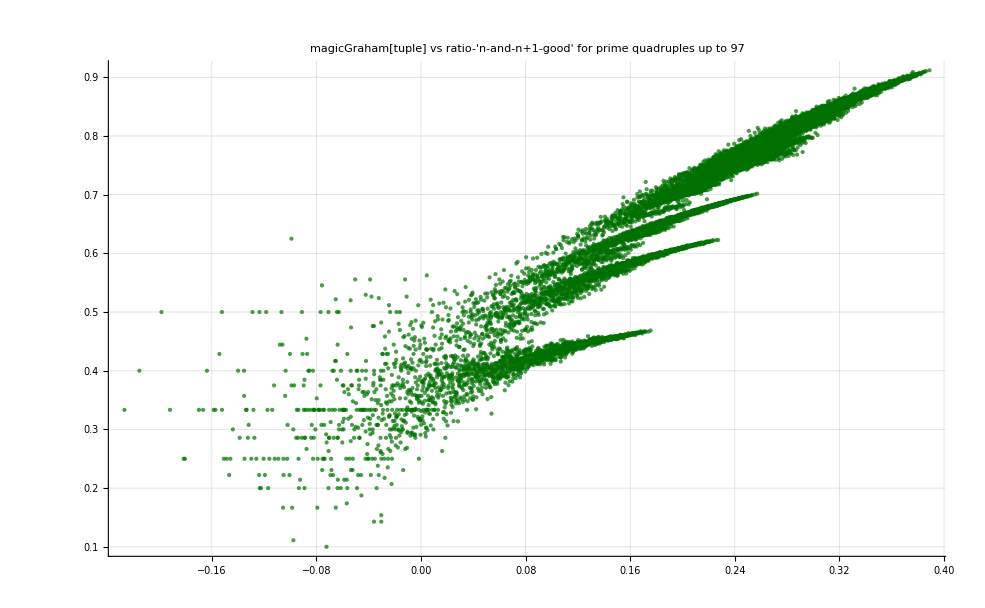

```mathematica
ListPlot[Sort[{{-0.22682794141729878,0.3333333333333333},{-0.21539526476721393,0.4},{-0.19852580764953276,0.5},{-0.19203819462697214,0.3333333333333333},{-0.18154091238929437,0.25},{-0.16982862385103914,0.3333333333333333},{-0.16665333139811345,0.3333333333333333},{-0.15862294956523237,0.3333333333333333},{-0.1542130398380358,0.42857142857142855},{-0.1522262282213992,0.3333333333333333},{-0.14861279605049604,0.25},{-0.14392510810623388,0.3},{-0.1399194144359625,0.4},{-0.13870728631608842,0.2857142857142857},{-0.1353770698042383,0.4},{-0.13337689867105262,0.3333333333333333},{-0.1324340041198372,0.2857142857142857},{-0.1298058330422998,0.25},{-0.12820119618394987,0.3333333333333333},{-0.12598309887876297,0.25},{-0.12332483053980903,0.2},{-0.18058790267404412,0.25},{-0.16371844555636295,0.4},{-0.15723083253380238,0.3333333333333333},{-0.14673355029612467,0.2222222222222222},{-0.13502126175786938,0.25},{-0.1318459693049437,0.3076923076923077},{-0.12381558747206256,0.2222222222222222},{-0.11940567774486605,0.2222222222222222},{-0.1174188661282295,0.3333333333333333},{-0.11380543395732623,0.3333333333333333},{-0.10911774601306412,0.25},{-0.10511205234279275,0.2222222222222222},{-0.1038999242229186,0.35714285714285715},{-0.10056970771106855,0.2222222222222222},{-0.09856953657788292,0.16666666666666666},{-0.09762664202666743,0.1111111111111111},{-0.09499847094913005,0.3333333333333333},{-0.09339383409078017,0.2},{-0.09117573678559321,0.2857142857142857},{-0.08851746844663932,0.3333333333333333},{-0.1522857689062781,0.5},{-0.14579815588371758,0.25},{-0.13530087364603982,0.35714285714285715},{-0.12358858510778459,0.5},{-0.1204132926548589,0.25},{-0.11238291082197777,0.375},{-0.10797300109478125,0.4444444444444444},{-0.10598618947814464,0.4444444444444444},{-0.10237275730724144,0.25},{-0.09768506936297927,0.3},{-0.0936793756927079,0.25},{-0.09246724757283381,0.21428571428571427},{-0.0891370310609837,0.38461538461538464},{-0.08713685992779807,0.42857142857142855},{-0.08619396537658264,0.4},{-0.0835657942990452,0.3076923076923077},{-0.08196115744069532,0.2857142857142857},{-0.07974306013550836,0.35294117647058826},{-0.07708479179655447,0.3333333333333333},{-0.12892869876603635,0.5},{-0.11843141652835865,0.5},{-0.10671912799010336,0.5},{-0.10354383553717766,0.4},{-0.09551345370429654,0.2857142857142857},{-0.09110354397710002,0.5},{-0.08911673236046347,0.2},{-0.0855033001895602,0.4},{-0.0808156122452981,0.3},{-0.07680991857502673,0.5},{-0.07559779045515258,0.23076923076923078},{-0.07226757394330252,0.1},{-0.0702674028101169,0.2857142857142857},{-0.06932450825890141,0.2222222222222222},{-0.06669633718136403,0.4},{-0.06509170032301415,0.4166666666666667},{-0.06287360301782718,0.5},{-0.0602153346788733,0.2777777777777778},{-0.11194380350579802,0.25},{-0.10023151496754279,0.42857142857142855},{-0.0970562225146171,0.375},{-0.08902584068173602,0.2857142857142857},{-0.08461593095453945,0.3333333333333333},{-0.08262911933790285,0.4},{-0.07901568716699969,0.25},{-0.07432799922273753,0.25},{-0.07032230555246616,0.3333333333333333},{-0.06911017743259207,0.3125},{-0.06577996092074195,0.3333333333333333},{-0.06377978978755627,0.4444444444444444},{-0.06283689523634084,0.3},{-0.06020872415880346,0.3333333333333333},{-0.05860408730045352,0.3333333333333333},{-0.05638598999526662,0.42857142857142855},{-0.05372772165631268,0.32142857142857145},{-0.08973423272986503,0.375},{-0.08655894027693933,0.3333333333333333},{-0.07852855844405826,0.3333333333333333},{-0.07411864871686169,0.3333333333333333},{-0.07213183710022514,0.2777777777777778},{-0.06851840492932193,0.23076923076923078},{-0.06383071698505982,0.2},{-0.05982502331478845,0.3125},{-0.058612895194914305,0.36363636363636365},{-0.055282678683064246,0.36},{-0.053282507549878566,0.375},{-0.052339612998663076,0.23076923076923078},{-0.049711441921125754,0.3448275862068966},{-0.048106805062775815,0.30303030303030304},{-0.04588870775758891,0.3333333333333333},{-0.04323043941863497,0.3333333333333333},{-0.0748466517386841,0.3333333333333333},{-0.06681626990580303,0.2857142857142857},{-0.06240636017860646,0.3333333333333333},{-0.06041954856196985,0.3},{-0.0568061163910667,0.17391304347826086},{-0.05211842844680453,0.25},{-0.04811273477653316,0.2222222222222222},{-0.04690060665665907,0.2857142857142857},{-0.04357039014480896,0.36363636363636365},{-0.04157021901162328,0.3333333333333333},{-0.04062732446040784,0.32},{-0.037999153382870465,0.3333333333333333},{-0.036394516524520526,0.3793103448275862},{-0.03417641921933362,0.3684210526315789},{-0.03151815088037968,0.3888888888888889},{-0.06364097745287733,0.21428571428571427},{-0.059231067725680764,0.3333333333333333},{-0.057244256109044156,0.25},{-0.053630823938141,0.23076923076923078},{-0.04894313599387884,0.2},{-0.04493744232360747,0.3076923076923077},{-0.04372531420373338,0.3157894736842105},{-0.040395097691883264,0.25},{-0.038394926558697584,0.2222222222222222},{-0.03745203200748215,0.25},{-0.03482386092994477,0.35},{-0.03321922407159483,0.3076923076923077},{-0.031001126766407927,0.2857142857142857},{-0.028342858427453987,0.3181818181818182},{-0.05120068589279969,0.2857142857142857},{-0.04921387427616308,0.3333333333333333},{-0.045600442105259875,0.1875},{-0.04091275416099771,0.275},{-0.03690706049072634,0.3},{-0.03569493237085225,0.3333333333333333},{-0.032364715859002136,0.2222222222222222},{-0.03036454472581651,0.14285714285714285},{-0.029421650174601077,0.25806451612903225},{-0.026793479097063644,0.2857142857142857},{-0.02518884223871376,0.25},{-0.0229707449335268,0.3611111111111111},{-0.020312476594572915,0.3142857142857143},{-0.04480396454896651,0.36363636363636365},{-0.04119053237806336,0.25806451612903225},{-0.036502844433801196,0.375},{-0.032497150763529825,0.32},{-0.031285022643655735,0.38461538461538464},{-0.02795480613180562,0.25},{-0.02595463499861994,0.35714285714285715},{-0.025011740447404507,0.26666666666666666},{-0.02238356936986713,0.3},{-0.02077893251151719,0.4117647058823529},{-0.018560835206330284,0.3076923076923077},{-0.015902566867376344,0.3333333333333333},{-0.03920372076142675,0.30952380952380953},{-0.034516032817164644,0.3333333333333333},{-0.030510339146893273,0.34146341463414637},{-0.029298211027019128,0.3269230769230769},{-0.02596799451516907,0.34375},{-0.02396782338198339,0.32432432432432434},{-0.0230249288307679,0.2857142857142857},{-0.020396757753230577,0.35135135135135137},{-0.018792120894880637,0.3225806451612903},{-0.01657402358969373,0.2894736842105263},{-0.013915755250739792,0.3},{-0.03090260064626138,0.2631578947368421},{-0.02689690697599001,0.34615384615384615},{-0.02568477885611592,0.3333333333333333},{-0.022354562344265805,0.27906976744186046},{-0.02035439121108018,0.30612244897959184},{-0.019411496659864746,0.3},{-0.016783325582327313,0.2978723404255319},{-0.01517868872397743,0.29545454545454547},{-0.012960591418790468,0.3150684931506849},{-0.010302323079836584,0.29577464788732394},{-0.0222092190317279,0.25},{-0.020997090911853755,0.3018867924528302},{-0.017666874400003696,0.2692307692307692},{-0.01566670326681807,0.2777777777777778},{-0.014723808715602582,0.3055555555555556},{-0.012095637638065204,0.26666666666666666},{-0.01049100077971532,0.3375},{-0.00827290347452836,0.3333333333333333},{-0.005614635135574475,0.3333333333333333},{-0.016991397241582384,0.3258426966292135},{-0.013661180729732325,0.23076923076923078},{-0.011661009596546701,0.3114754098360656},{-0.010718115045331211,0.26865671641791045},{-0.008089943967793833,0.2894736842105263},{-0.00648530710944395,0.3333333333333333},{-0.004267209804256988,0.3333333333333333},{-0.0016089414653031042,0.25},{-0.01244905260985818,0.3246753246753247},{-0.010448881476672556,0.29411764705882354},{-0.009505986925457122,0.3333333333333333},{-0.006877815847919688,0.29457364341085274},{-0.0052731789895698045,0.3235294117647059},{-0.0030550816843828432,0.35135135135135137},{-0.0003968133454289591,0.2909090909090909},{-0.0071186649648224964,0.3300970873786408},{-0.006175770413607007,0.2909090909090909},{-0.003547599336069629,0.30434782608695654},{-0.0019429624777197452,0.3181818181818182},{0.00027513482746721607,0.33125},{0.0029334031664211,0.32894736842105265},{-0.004175599280421327,0.33532934131736525},{-0.0015474282028840047,0.34545454545454546},{0.000057208655465934566,0.3078947368421053},{0.0022753059606528403,0.3105022831050228},{0.00493357429960678,0.2987012987012987},{-0.0006045336516685151,0.3148148148148148},{0.0010001032066814242,0.32222222222222224},{0.00321820051186833,0.29365079365079366},{0.0058764688508222696,0.3333333333333333},{0.0036282742842187465,0.2878787878787879},{0.005846371589405708,0.3275862068965517},{0.008504639928359592,0.3333333333333333},{0.007451008447755592,0.30666666666666664},{0.010109276786709531,0.3333333333333333},{0.012327374091896437,0.32558139534883723},{-0.150779722943985,0.25},{-0.13391026582630383,0.3333333333333333},{-0.12742265280374326,0.2857142857142857},{-0.11692537056606556,0.2},{-0.10521308202781027,0.25},{-0.10203778957488457,0.3076923076923077},{-0.09400740774200345,0.2857142857142857},{-0.08959749801480693,0.3333333333333333},{-0.08761068639817038,0.26666666666666666},{-0.08399725422726712,0.2857142857142857},{-0.079309566283005,0.16666666666666666},{-0.07530387261273364,0.25},{-0.07409174449285949,0.3076923076923077},{-0.07076152798100943,0.2},{-0.0687613568478238,0.25},{-0.06781846229660832,0.4},{-0.06519029121907094,0.16666666666666666},{-0.06358565436072106,0.2857142857142857},{-0.061367557055534094,0.2},{-0.05870928871658021,0.21428571428571427},{-0.12247758917621898,0.2},{-0.11598997615365847,0.25},{-0.1054926939159807,0.16666666666666666},{-0.09378040537772547,0.3333333333333333},{-0.09060511292479978,0.42857142857142855},{-0.08257473109191865,0.25},{-0.07816482136472214,0.3333333333333333},{-0.07617800974808553,0.3076923076923077},{-0.07256457757718232,0.2916666666666667},{-0.06787688963292016,0.3333333333333333},{-0.06387119596264879,0.2857142857142857},{-0.0626590678427747,0.3076923076923077},{-0.05932885133092458,0.375},{-0.05732868019773896,0.3333333333333333},{-0.05638578564652352,0.2},{-0.05375761456898609,0.28},{-0.052152977710636206,0.34782608695652173},{-0.049934880405449245,0.30434782608695654},{-0.04727661206649536,0.2857142857142857},{-0.09912051903597724,0.375},{-0.08862323679829953,0.2857142857142857},{-0.07691094826004424,0.375},{-0.07373565580711855,0.25},{-0.06570527397423742,0.4166666666666667},{-0.06129536424704091,0.4},{-0.059308552630404354,0.3333333333333333},{-0.05569512045950109,0.3181818181818182},{-0.05100743251523898,0.3},{-0.04700173884496761,0.3333333333333333},{-0.045789610725093466,0.2222222222222222},{-0.04245939421324341,0.25},{-0.04045922308005778,0.25},{-0.03951632852884229,0.3333333333333333},{-0.036888157451304915,0.32432432432432434},{-0.03528352059295503,0.25},{-0.03306542328776807,0.23809523809523808},{-0.030407154948814186,0.15384615384615385},{-0.08213562377573891,0.3333333333333333},{-0.07042333523748368,0.2857142857142857},{-0.06724804278455798,0.2222222222222222},{-0.05921766095167691,0.3},{-0.05480775122448034,0.25},{-0.05282093960784373,0.3076923076923077},{-0.04920750743694058,0.4},{-0.044519819492678414,0.3333333333333333},{-0.04051412582240704,0.36363636363636365},{-0.039301997702532954,0.3},{-0.03597178119068284,0.14285714285714285},{-0.03397161005749716,0.2},{-0.033028715506281725,0.3076923076923077},{-0.030400544428744347,0.25},{-0.028795907570394408,0.4},{-0.026577810265207502,0.3076923076923077},{-0.023919541926253562,0.2903225806451613},{-0.05992605299980591,0.375},{-0.05675076054688022,0.21428571428571427},{-0.048720378713999146,0.4},{-0.044310468986802576,0.3333333333333333},{-0.042323657370166023,0.38636363636363635},{-0.038710225199262815,0.2916666666666667},{-0.03402253725500071,0.3076923076923077},{-0.030016843584729336,0.3157894736842105},{-0.02880471546485519,0.38461538461538464},{-0.02547449895300513,0.23529411764705882},{-0.02347432781981945,0.2631578947368421},{-0.022531433268603962,0.34782608695652173},{-0.01990326219106664,0.32727272727272727},{-0.0182986253327167,0.3225806451612903},{-0.016080528027529795,0.35294117647058826},{-0.013422259688575855,0.3142857142857143},{-0.045038472008624986,0.4},{-0.03700809017574391,0.29411764705882354},{-0.03259818044854734,0.2727272727272727},{-0.030611368831910735,0.38461538461538464},{-0.026997936661007582,0.3684210526315789},{-0.022310248716745418,0.39285714285714285},{-0.018304555046474047,0.3333333333333333},{-0.017092426926599957,0.3888888888888889},{-0.013762210414749843,0.42105263157894735},{-0.011762039281564163,0.35294117647058826},{-0.010819144730348729,0.3333333333333333},{-0.00819097365281135,0.36666666666666664},{-0.0065863367944614115,0.37037037037037035},{-0.004368239489274506,0.2857142857142857},{-0.0017099711503205661,0.3333333333333333},{-0.03383279772281822,0.26666666666666666},{-0.02942288799562165,0.42857142857142855},{-0.02743607637898504,0.4375},{-0.02382264420808189,0.3},{-0.019134956263819725,0.2857142857142857},{-0.015129262593548354,0.4},{-0.013917134473674264,0.3333333333333333},{-0.01058691796182415,0.36363636363636365},{-0.00858674682863847,0.4375},{-0.0076438522774230355,0.29411764705882354},{-0.005015681199885658,0.3333333333333333},{-0.0034110443415357183,0.35714285714285715},{-0.0011929470363488126,0.35714285714285715},{0.001465321302605127,0.34375},{-0.021392506162740577,0.35714285714285715},{-0.01940569454610397,0.2727272727272727},{-0.01579226237520076,0.37037037037037035},{-0.011104574430938596,0.32653061224489793},{-0.0070988807606672255,0.3333333333333333},{-0.005886752640793136,0.30303030303030304},{-0.002556536128943021,0.375},{-0.0005563649957573968,0.3181818181818182},{0.00038652955545803724,0.35714285714285715},{0.0030147006329954706,0.3488372093023256},{0.004619337491345354,0.3333333333333333},{0.006837434796532316,0.32608695652173914},{0.0094957031354862,0.375},{-0.014995784818907398,0.3170731707317073},{-0.011382352648004246,0.3333333333333333},{-0.0066946647037420814,0.358974358974359},{-0.0026889710334707106,0.35714285714285715},{-0.001476842913596621,0.3488372093023256},{0.0018533735982534938,0.3333333333333333},{0.0038535447314391735,0.30303030303030304},{0.004796439282654608,0.36923076923076925},{0.0074246103601919855,0.35294117647058826},{0.009029247218541925,0.3472222222222222},{0.01124734452372883,0.3783783783783784},{0.01390561286268277,0.39344262295081966},{-0.009395541031367638,0.3673469387755102},{-0.004707853087105529,0.2903225806451613},{-0.0007021594168341583,0.3157894736842105},{0.0005099687030399869,0.34615384615384615},{0.003840185214890046,0.3333333333333333},{0.005840356348075726,0.34146341463414637},{0.0067832508992912155,0.35},{0.009411421976828538,0.38571428571428573},{0.011016058835178477,0.34285714285714286},{0.013234156140365383,0.3541666666666667},{0.015892424479319323,0.38372093023255816},{-0.0010944209162022656,0.3181818181818182},{0.0029112727540691052,0.3620689655172414},{0.004123400873943195,0.3026315789473684},{0.00745361738579331,0.375},{0.009453788518978934,0.3},{0.010396683070194368,0.3333333333333333},{0.013024854147731801,0.3333333333333333},{0.014629491006081685,0.36666666666666664},{0.016847588311268646,0.32894736842105265},{0.01950585665022253,0.3467741935483871},{0.007598960698331214,0.4375},{0.00881108881820536,0.34615384615384615},{0.012141305330055419,0.36363636363636365},{0.014141476463241043,0.358974358974359},{0.015084371014456532,0.3684210526315789},{0.01771254209199391,0.34831460674157305},{0.019317178950343794,0.3611111111111111},{0.021535276255530755,0.3626373626373626},{0.02419354459448464,0.3381294964028777},{0.01281678248847673,0.4},{0.01614699900032679,0.2631578947368421},{0.018147170133512414,0.3375},{0.019090064684727903,0.3137254901960784},{0.02171823576226528,0.3888888888888889},{0.023322872620615165,0.34210526315789475},{0.025540969925802126,0.36363636363636365},{0.02819923826475601,0.34782608695652173},{0.017359127120200935,0.3181818181818182},{0.01935929825338656,0.32608695652173914},{0.020302192804601993,0.30666666666666664},{0.022930363882139426,0.3283582089552239},{0.02453500074048931,0.36904761904761907},{0.02675309804567627,0.3492063492063492},{0.029411366384630155,0.38},{0.022689514765236618,0.35384615384615387},{0.023632409316452108,0.35294117647058826},{0.026260580393989486,0.35714285714285715},{0.02786521725233937,0.4230769230769231},{0.03008331455752633,0.35443037974683544},{0.032741582896480215,0.4},{0.025632580449637787,0.35526315789473684},{0.02826075152717511,0.3137254901960784},{0.02986538838552505,0.4},{0.032083485690711955,0.3469387755102041},{0.034741754029665894,0.3956043956043956},{0.0292036460783906,0.34459459459459457},{0.03080828293674054,0.35185185185185186},{0.033026380241927444,0.35625},{0.035684648580881384,0.3787878787878788},{0.03343645401427786,0.3508771929824561},{0.03565455131946482,0.347953216374269},{0.038312819658418706,0.3701923076923077},{0.037259188177814706,0.3711340206185567},{0.039917456516768646,0.3563218390804598},{0.04213555382195555,0.3345070422535211},{-0.08767022708304922,0.45454545454545453},{-0.08118261406048871,0.3333333333333333},{-0.07068533182281095,0.2631578947368421},{-0.058973043284555715,0.3181818181818182},{-0.05579775083163002,0.3684210526315789},{-0.047767368998748894,0.3684210526315789},{-0.04335745927155238,0.35714285714285715},{-0.04137064765491577,0.36},{-0.03775721548401256,0.35135135135135137},{-0.0330695275397504,0.3448275862068966},{-0.029063833869479028,0.3333333333333333},{-0.027851705749604938,0.21739130434782608},{-0.024521489237754823,0.32142857142857145},{-0.0225213181045692,0.20689655172413793},{-0.021578423553353765,0.3142857142857143},{-0.01895025247581633,0.32},{-0.017345615617466448,0.3},{-0.015127518312279487,0.4032258064516129},{-0.012469249973325602,0.4067796610169492},{-0.06431315694280748,0.38461538461538464},{-0.053815874705129774,0.4},{-0.042103586166874485,0.4166666666666667},{-0.03892829371394879,0.3181818181818182},{-0.030897911881067663,0.375},{-0.02648800215387115,0.4117647058823529},{-0.024501190537234596,0.4666666666666667},{-0.020887758366331333,0.36585365853658536},{-0.016200070422069224,0.375},{-0.012194376751797853,0.41379310344827586},{-0.010982248631923708,0.4074074074074074},{-0.0076520321200736485,0.36363636363636365},{-0.005651860986888024,0.40384615384615385},{-0.004708966435672535,0.2916666666666667},{-0.002080795358135157,0.4090909090909091},{-0.000476158499785273,0.4186046511627907},{0.0017419388054016882,0.42857142857142855},{0.004400207144355572,0.43617021276595747},{-0.04732826168256915,0.38461538461538464},{-0.03561597314431392,0.36363636363636365},{-0.032440680691388224,0.35},{-0.02441029885850715,0.34782608695652173},{-0.02000038913131058,0.40625},{-0.018013577514673973,0.3783783783783784},{-0.01440014534377082,0.3},{-0.009712457399508656,0.36},{-0.005706763729237285,0.42857142857142855},{-0.004494635609363196,0.3888888888888889},{-0.0011644190975130808,0.4166666666666667},{0.0008357520356725989,0.38028169014084506},{0.001778646586888033,0.37254901960784315},{0.004406817664425411,0.3673469387755102},{0.00601145452277535,0.3496932515337423},{0.008229551827962256,0.3548387096774194},{0.010887820166916196,0.34545454545454546},{-0.025118690906636154,0.40425531914893614},{-0.02194339845371046,0.375},{-0.013913016620829388,0.38461538461538464},{-0.009503106893632818,0.40816326530612246},{-0.007516295276996265,0.34545454545454546},{-0.0039028631060930574,0.4},{0.0007848248381690515,0.4146341463414634},{0.004790518508440422,0.3333333333333333},{0.006002646628314567,0.37606837606837606},{0.009332863140164627,0.35294117647058826},{0.011333034273350306,0.4024390243902439},{0.012275928824565796,0.3888888888888889},{0.014904099902103118,0.36666666666666664},{0.016508736760453058,0.3795180722891566},{0.018726834065639963,0.34375},{0.021385102404593903,0.38571428571428573},{-0.010231109915455228,0.40384615384615385},{-0.002200728082574155,0.35384615384615387},{0.0022091816446224155,0.38461538461538464},{0.004195993261259023,0.4166666666666667},{0.007809425432162176,0.3877551020408163},{0.01249711337642434,0.4025974025974026},{0.01650280704669571,0.3894736842105263},{0.0177149351665698,0.37209302325581395},{0.021045151678419916,0.39},{0.023045322811605595,0.36283185840707965},{0.02398821736282103,0.4067796610169492},{0.026616388440358407,0.38848920863309355},{0.028221025298708347,0.38333333333333336},{0.030439122603895252,0.3924731182795699},{0.03309739094284919,0.37628865979381443},{0.0009745643703515383,0.36666666666666664},{0.005384474097548109,0.35714285714285715},{0.0073712857141847166,0.3917525773195876},{0.010984717885087869,0.4},{0.015672405829350033,0.36893203883495146},{0.019678099499621404,0.3958333333333333},{0.020890227619495494,0.3741496598639456},{0.02422044413134561,0.38392857142857145},{0.02622061526453129,0.41935483870967744},{0.027163509815746723,0.36318407960199006},{0.0297916808932841,0.3924050632911392},{0.03139631775163404,0.37037037037037035},{0.033614415056820945,0.40336134453781514},{0.036272683395774885,0.3842364532019704},{0.013414855930429181,0.3953488372093023},{0.01540166754706579,0.47058823529411764},{0.019015099717968997,0.423728813559322},{0.023702787662231162,0.3869346733668342},{0.027708481332502533,0.3516483516483517},{0.028920609452376622,0.38144329896907214},{0.03225082596422674,0.39344262295081966},{0.03425099709741236,0.4175824175824176},{0.035193891648627795,0.3333333333333333},{0.03782206272616523,0.4064516129032258},{0.03942669958451511,0.39444444444444443},{0.041644796889702074,0.38144329896907214},{0.04430306522865596,0.4105691056910569},{0.01981157727426236,0.4074074074074074},{0.023425009445165512,0.391304347826087},{0.028112697389427677,0.3950617283950617},{0.03211839105969905,0.39325842696629215},{0.03333051917957314,0.4166666666666667},{0.03666073569142325,0.4107142857142857},{0.03866090682460893,0.39869281045751637},{0.039603801375824366,0.4105263157894737},{0.042231972453361744,0.3986013986013986},{0.04383660931171168,0.3991228070175439},{0.04605470661689859,0.36538461538461536},{0.04871297495585253,0.3770491803278688},{0.02541182106180212,0.41935483870967744},{0.03009950900606423,0.4090909090909091},{0.0341052026763356,0.41025641025641024},{0.035317330796209745,0.40540540540540543},{0.038647547308059804,0.38461538461538464},{0.040647718441245484,0.41450777202072536},{0.041590612992460974,0.4107142857142857},{0.044218784069998296,0.3655913978494624},{0.045823420928348235,0.38235294117647056},{0.04804151823353514,0.4304635761589404},{0.05069978657248908,0.41148325358851673},{0.03371294117696749,0.3795454545454545},{0.03771863484723886,0.4020618556701031},{0.03893076296711295,0.378698224852071},{0.04226097947896307,0.39565217391304347},{0.04426115061214869,0.39880952380952384},{0.045204045163364126,0.37735849056603776},{0.04783221624090156,0.40350877192982454},{0.04943685309925144,0.39285714285714285},{0.051654950404438404,0.3939393939393939},{0.05431321874339229,0.4117647058823529},{0.04240632279150097,0.3548387096774194},{0.04361845091137512,0.3699186991869919},{0.04694866742322518,0.38461538461538464},{0.0489488385564108,0.40458015267175573},{0.04989173310762629,0.401673640167364},{0.05251990418516367,0.3723849372384937},{0.05412454104351355,0.39255014326647564},{0.05634263834870051,0.3911764705882353},{0.0590009066876544,0.39226519337016574},{0.04762414458164649,0.41040462427745666},{0.05095436109349655,0.3782608695652174},{0.05295453222668217,0.40425531914893614},{0.05389742677789766,0.3269230769230769},{0.05652559785543504,0.4010989010989011},{0.05813023471378492,0.40117994100294985},{0.060348332018971884,0.3860294117647059},{0.06300660035792577,0.39228295819935693},{0.05216648921337069,0.37593984962406013},{0.05416666034655632,0.3903345724907063},{0.05510955489777175,0.38181818181818183},{0.057737725975309184,0.3959731543624161},{0.05934236283365907,0.4015748031496063},{0.06156046013884603,0.39015151515151514},{0.06421872847779991,0.40388349514563104},{0.057496876858406376,0.40214477211796246},{0.058439771409621866,0.3891625615763547},{0.061067942487159244,0.396969696969697},{0.06267257934550913,0.40217391304347827},{0.06489067665069609,0.40809968847352024},{0.06754894498964997,0.4090909090909091},{0.060439942542807545,0.3945945945945946},{0.06306811362034487,0.4096153846153846},{0.06467275047869481,0.390745501285347},{0.06689084778388171,0.37545126353790614},{0.06954911612283565,0.40476190476190477},{0.06401100817156036,0.36666666666666664},{0.0656156450299103,0.38847117794486213},{0.0678337423350972,0.38202247191011235},{0.07049201067405114,0.4050632911392405},{0.06824381610744762,0.4010507880910683},{0.07046191341263458,0.38688524590163936},{0.07312018175158846,0.39280774550484093},{0.07206655027098446,0.4069097888675624},{0.0747248186099384,0.39950980392156865},{0.07694291591512531,0.4027355623100304},{-0.05288048029272269,0.375},{-0.04238319805504498,0.2962962962962963},{-0.03067090951678969,0.4},{-0.027495617063863997,0.4117647058823529},{-0.01946523523098287,0.41304347826086957},{-0.015055325503786354,0.41025641025641024},{-0.013068513887149802,0.4117647058823529},{-0.009455081716246538,0.46153846153846156},{-0.0047673937719844295,0.358974358974359},{-0.0007617001017130587,0.3898305084745763},{0.00045042801816108646,0.38235294117647056},{0.0037806445300111458,0.4142857142857143},{0.00578081566319677,0.3950617283950617},{0.00672371021441226,0.375},{0.009351881291949637,0.3829787234042553},{0.010956518150299521,0.3706896551724138},{0.013174615455486482,0.37142857142857144},{0.015832883794440367,0.39490445859872614},{-0.035895585032484356,0.3939393939393939},{-0.024183296494229123,0.3230769230769231},{-0.02100800404130343,0.375},{-0.012977622208422357,0.37209302325581395},{-0.008567712481225787,0.34782608695652173},{-0.006580900864589179,0.41379310344827586},{-0.002967468693686026,0.3684210526315789},{0.0017202192505761382,0.38095238095238093},{0.005725912920847509,0.3717948717948718},{0.006938041040721599,0.4090909090909091},{0.010268257552571713,0.3787878787878788},{0.012268428685757393,0.4},{0.013211323236972827,0.4},{0.015839494314510205,0.37362637362637363},{0.017444131172860144,0.32954545454545453},{0.01966222847804705,0.4049586776859504},{0.02232049681700099,0.379746835443038},{-0.01368601425655136,0.3787878787878788},{-0.010510721803625667,0.38095238095238093},{-0.002480339970744594,0.32142857142857145},{0.0019295697564519765,0.3780487804878049},{0.003916381373088529,0.40789473684210525},{0.007529813543991737,0.3870967741935484},{0.012217501488253846,0.35714285714285715},{0.016223195158525217,0.3877551020408163},{0.01743532327839936,0.37681159420289856},{0.02076553979024942,0.4095238095238095},{0.0227657109234351,0.34831460674157305},{0.02370860547465059,0.39215686274509803},{0.026336776552187913,0.36283185840707965},{0.027941413410537852,0.3835616438356164},{0.030159510715724758,0.3904382470119522},{0.0328177790546787,0.37606837606837606},{0.0012015667346295666,0.3157894736842105},{0.00923194856751064,0.3176470588235294},{0.01364185829470721,0.3939393939393939},{0.015628669911343818,0.41304347826086957},{0.01924210208224697,0.4126984126984127},{0.023929790026509135,0.3956043956043956},{0.027935483696780505,0.41025641025641024},{0.029147611816654595,0.3888888888888889},{0.03247782832850471,0.4025974025974026},{0.03447799946169039,0.37593984962406013},{0.035420894012905824,0.3591549295774648},{0.0380490650904432,0.36283185840707965},{0.03965370194879314,0.35},{0.04187179925398005,0.3925233644859813},{0.044530067592933986,0.40606060606060607},{0.012407241020436333,0.39344262295081966},{0.016817150747632903,0.35714285714285715},{0.01880396236426951,0.42528735632183906},{0.022417394535172663,0.39263803680981596},{0.027105082479434828,0.3619047619047619},{0.0311107761497062,0.3821138211382114},{0.03232290426958029,0.3669724770642202},{0.0356531207814304,0.3986013986013986},{0.03765329191461608,0.35294117647058826},{0.03859618646583152,0.3684210526315789},{0.041224357543368895,0.40145985401459855},{0.042828994401718834,0.38626609442060084},{0.04504709170690574,0.40298507462686567},{0.04770536004585968,0.39285714285714285},{0.024847532580513976,0.3142857142857143},{0.026834344197150584,0.3442622950819672},{0.03044777636805379,0.417910447761194},{0.035135464312315956,0.3939393939393939},{0.03914115798258733,0.36428571428571427},{0.040353286102461416,0.3739495798319328},{0.04368350261431153,0.4107142857142857},{0.045683673747497155,0.3893805309734513},{0.04662656829871259,0.3712121212121212},{0.04925473937625002,0.42045454545454547},{0.05085937623459991,0.3516483516483517},{0.05307747353978687,0.3716216216216216},{0.05573574187874075,0.3986013986013986},{0.031244253924347154,0.4074074074074074},{0.034857686095250306,0.36046511627906974},{0.03954537403951247,0.3816793893129771},{0.04355106770978384,0.3902439024390244},{0.04476319582965793,0.39416058394160586},{0.048093412341508046,0.39919354838709675},{0.050093583474693726,0.4068965517241379},{0.05103647802590916,0.37823834196891193},{0.05366464910344654,0.3551020408163265},{0.05526928596179648,0.38977635782747605},{0.05748738326698338,0.3865546218487395},{0.06014565160593732,0.3922413793103448},{0.036844497711886914,0.3939393939393939},{0.04153218565614902,0.389937106918239},{0.045537879326420394,0.4019607843137255},{0.04675000744629454,0.4065040650406504},{0.0500802239581446,0.4235294117647059},{0.05208039509133028,0.39080459770114945},{0.05302328964254577,0.39622641509433965},{0.05565146072008309,0.38764044943820225},{0.05725609757843303,0.398876404494382},{0.059474194883619935,0.39090909090909093},{0.062132463222573875,0.41522491349480967},{0.04514561782705229,0.4031746031746032},{0.04915131149732366,0.39144736842105265},{0.05036343961719775,0.409375},{0.05369365612904786,0.39751552795031053},{0.055693827262233486,0.425},{0.05663672181344892,0.4122448979591837},{0.059264892890986354,0.3887147335423197},{0.06086952974933624,0.4054878048780488},{0.0630876270545232,0.3973727422003284},{0.06574589539347708,0.3975481611208406},{0.053838999441585766,0.4006514657980456},{0.05505112756145991,0.38666666666666666},{0.05838134407330997,0.3776978417266187},{0.060381515206495595,0.38837920489296635},{0.061324409757711085,0.415625},{0.06395258083524846,0.4084967320261438},{0.06555721769359835,0.4155124653739612},{0.06777531499878531,0.39690721649484534},{0.07043358333773919,0.40219092331768386},{0.05905682123173128,0.3862928348909657},{0.06238703774358134,0.3904282115869018},{0.06438720887676697,0.3901639344262295},{0.06533010342798246,0.392},{0.06795827450551983,0.39969135802469136},{0.06956291136386972,0.42115027829313545},{0.07178100866905668,0.415973377703827},{0.07443927700801056,0.41229656419529837},{0.06359916586345549,0.4187725631768953},{0.06559933699664111,0.40939597315436244},{0.06654223154785655,0.43312101910828027},{0.06917040262539398,0.4144736842105263},{0.07077503948374386,0.3935483870967742},{0.07299313678893082,0.4033898305084746},{0.07565140512788471,0.42096774193548386},{0.06892955350849117,0.41935483870967744},{0.06987244805970666,0.41914893617021276},{0.07250061913724404,0.41379310344827586},{0.07410525599559392,0.39950980392156865},{0.07632335330078088,0.4194078947368421},{0.07898162163973477,0.41631799163179917},{0.07187261919289234,0.40468227424749165},{0.07450079027042966,0.4096989966555184},{0.0761054271287796,0.41102756892230574},{0.07832352443396651,0.4204081632653061},{0.08098179277292045,0.40308370044052866},{0.07544368482164515,0.40372670807453415},{0.07704832167999509,0.407514450867052},{0.079266418985182,0.40472175379426645},{0.08192468732413594,0.415041782729805},{0.07967649275753241,0.39855072463768115},{0.08189459006271937,0.4163380281690141},{0.08455285840167326,0.4139834406623735},{0.08349922692106926,0.41375291375291373},{0.0861574952600232,0.40955137481910275},{0.0883755925652101,0.41417165668662675},{-0.019026127914803126,0.375},{-0.007313839376547893,0.40186915887850466},{-0.0041385469236221994,0.4358974358974359},{0.0038918349092588733,0.43636363636363634},{0.008301744636455444,0.36585365853658536},{0.010288556253092052,0.4117647058823529},{0.013901988423995204,0.43636363636363634},{0.01858967636825737,0.40350877192982454},{0.02259537003852874,0.40625},{0.02380749815840283,0.37272727272727274},{0.027137714670252944,0.40522875816993464},{0.029137885803438623,0.4406779661016949},{0.030080780354654058,0.38636363636363635},{0.032708951432191435,0.4074074074074074},{0.034313588290541375,0.39325842696629215},{0.03653168559572828,0.391025641025641},{0.03918995393468222,0.4146341463414634},{0.0031834428611298704,0.3865546218487395},{0.006358735314055564,0.391304347826087},{0.014389117146936636,0.39344262295081966},{0.018799026874133207,0.4205607476635514},{0.02078583849076976,0.37037037037037035},{0.024399270661672967,0.410958904109589},{0.029086958605935076,0.37572254335260113},{0.03309265227620645,0.39072847682119205},{0.03430478039608059,0.42105263157894735},{0.03763499690793065,0.4125},{0.03963516804111633,0.3516483516483517},{0.04057806259233182,0.4098360655737705},{0.04320623366986914,0.41216216216216217},{0.04481087052821908,0.38181818181818183},{0.04702896783340599,0.36},{0.04968723617235993,0.38317757009345793},{0.018071023852310797,0.3898305084745763},{0.02610140568519187,0.42592592592592593},{0.03051131541238844,0.373134328358209},{0.03249812702902505,0.43548387096774194},{0.0361115591999282,0.40441176470588236},{0.040799247144190365,0.40444444444444444},{0.044804940814461736,0.4175824175824176},{0.046017068934335825,0.41935483870967744},{0.04934728544618594,0.4274193548387097},{0.05134745657937162,0.4222222222222222},{0.052290351130587054,0.40569395017793597},{0.05491852220812443,0.4074074074074074},{0.05652315906647437,0.4020618556701031},{0.05874125637166128,0.40718562874251496},{0.061399524710615216,0.4115384615384615},{0.029276698138117563,0.37333333333333335},{0.03368660786531413,0.39344262295081966},{0.03567341948195074,0.40816326530612246},{0.039286851652853894,0.3950617283950617},{0.04397453959711606,0.38235294117647056},{0.04798023326738743,0.40562248995983935},{0.04919236138726152,0.39322033898305087},{0.05252257789911163,0.40369393139841686},{0.05452274903229731,0.3940774487471526},{0.05546564358351275,0.38095238095238093},{0.058093814661050125,0.3813559322033898},{0.059698451519400064,0.43795620437956206},{0.06191654882458697,0.40344827586206894},{0.06457481716354091,0.3795918367346939},{0.041716989698195206,0.3886255924170616},{0.043703801314831814,0.4046511627906977},{0.04731723348573502,0.4},{0.052004921429997186,0.39267015706806285},{0.05601061510026856,0.40869565217391307},{0.05722274322014265,0.41312741312741313},{0.06055295973199276,0.4049079754601227},{0.06255313086517839,0.4221105527638191},{0.06349602541639382,0.4088397790055249},{0.06612419649393125,0.3888888888888889},{0.06772883335228114,0.4150641025641026},{0.0699469306574681,0.4161290322580645},{0.07260519899642198,0.4187725631768953},{0.048113711042028384,0.3945578231292517},{0.05172714321293154,0.4050632911392405},{0.0564148311571937,0.37719298245614036},{0.06042052482746507,0.41714285714285715},{0.06163265294733916,0.4105263157894737},{0.06496286945918928,0.43147208121827413},{0.06696304059237496,0.39037433155080214},{0.06790593514359039,0.43209876543209874},{0.07053410622112777,0.43577981651376146},{0.07213874307947771,0.4367816091954023},{0.07435684038466461,0.39325842696629215},{0.07701510872361855,0.4108761329305136},{0.053713954829568145,0.4093567251461988},{0.058401642773830253,0.42857142857142855},{0.062407336444101624,0.4148148148148148},{0.06361946456397577,0.42338709677419356},{0.06694968107582583,0.4215686274509804},{0.06894985220901151,0.4069767441860465},{0.069892746760227,0.38144329896907214},{0.07252091783776432,0.4024390243902439},{0.07412555469611426,0.41832669322709165},{0.07634365200130117,0.39690721649484534},{0.0790019203402551,0.42297650130548303},{0.06201507494473352,0.41452991452991456},{0.06602076861500489,0.43946188340807174},{0.06723289673487898,0.428},{0.07056311324672909,0.3930635838150289},{0.07256328437991472,0.40425531914893614},{0.07350617893113015,0.44029850746268656},{0.07613435000866758,0.41959798994974873},{0.07773898686701747,0.40492957746478875},{0.07995708417220443,0.4365079365079365},{0.08261535251115831,0.43717277486910994},{0.070708456559267,0.39902676399026765},{0.07192058467914114,0.41262135922330095},{0.0752508011909912,0.4166666666666667},{0.07725097232417683,0.40865384615384615},{0.07819386687539231,0.42105263157894735},{0.08082203795292969,0.42277992277992277},{0.08242667481127958,0.4074074074074074},{0.08464477211646654,0.4185022026431718},{0.08730304045542042,0.4198071866783523},{0.07592627834941251,0.40681362725450904},{0.07925649486126257,0.43253467843631777},{0.0812566659944482,0.41947115384615385},{0.08219956054566369,0.43352601156069365},{0.08482773162320106,0.41544117647058826},{0.08643236848155095,0.4256120527306968},{0.08865046578673791,0.4211309523809524},{0.09130873412569179,0.41379310344827586},{0.08046862298113672,0.422},{0.08246879411432234,0.4106951871657754},{0.08341168866553778,0.42731277533039647},{0.08603985974307521,0.4185606060606061},{0.08764449660142509,0.4157068062827225},{0.08986259390661205,0.4276018099547511},{0.09252086224556594,0.4303153611393693},{0.0857990106261724,0.4150552486187845},{0.08674190517738789,0.4236111111111111},{0.08937007625492527,0.42015209125475284},{0.09097471311327515,0.4222222222222222},{0.09319281041846211,0.4209245742092457},{0.095851078757416,0.431858407079646},{0.08874207631057357,0.4128065395095368},{0.09137024738811089,0.4171195652173913},{0.09297488424646083,0.4179431072210066},{0.09519298155164774,0.42105263157894735},{0.09785124989060168,0.42606790799561883},{0.09231314193932638,0.4203187250996016},{0.09391777879767632,0.41421568627450983},{0.09613587610286323,0.4423963133640553},{0.09879414444181717,0.42349726775956287},{0.09654594987521364,0.4302477183833116},{0.0987640471804006,0.42251655629139073},{0.10142231551935449,0.4288537549407115},{0.10036868403875049,0.4166666666666667},{0.10302695237770443,0.41814159292035397},{0.10524504968289133,0.42377260981912146},{0.009671055883690438,0.375},{0.012846348336616131,0.4111111111111111},{0.020876730169497204,0.39215686274509803},{0.025286639896693774,0.41414141414141414},{0.027273451513330327,0.358974358974359},{0.030886883684233535,0.3877551020408163},{0.035574571628495644,0.4158415841584158},{0.039580265298767014,0.416289592760181},{0.04079239341864116,0.40350877192982454},{0.04412260993049122,0.38839285714285715},{0.0461227810636769,0.39751552795031053},{0.04706567561489239,0.42},{0.04969384669242971,0.3709677419354839},{0.05129848355077965,0.4069264069264069},{0.053516580855966556,0.40476190476190477},{0.056174849194920495,0.39800995024875624},{0.024558636874871365,0.3769230769230769},{0.03258901870775244,0.40384615384615385},{0.03699892843494901,0.40384615384615385},{0.038985740051585616,0.38626609442060084},{0.04259917222248877,0.3942307692307692},{0.04728686016675093,0.4},{0.0512925538370223,0.3950617283950617},{0.05250468195689639,0.4056603773584906},{0.05583489846874651,0.40304182509505704},{0.05783506960193219,0.4090909090909091},{0.05877796415314762,0.4069767441860465},{0.061406135230685,0.4129032258064516},{0.06301077208903494,0.4148936170212766},{0.06522886939422184,0.4256410256410256},{0.06788713773317578,0.4049586776859504},{0.03576431116067813,0.39490445859872614},{0.0401742208878747,0.41919191919191917},{0.04216103250451131,0.410958904109589},{0.04577446467541446,0.43214285714285716},{0.050462152619676626,0.3987341772151899},{0.054467846289947996,0.43636363636363634},{0.055679974409822086,0.37988826815642457},{0.0590101909216722,0.430327868852459},{0.06101036205485788,0.4150197628458498},{0.061953256606073315,0.42408376963350786},{0.06458142768361069,0.4142857142857143},{0.06618606454196063,0.4044943820224719},{0.06840416184714754,0.42528735632183906},{0.07106243018610148,0.4100486223662885},{0.048204602720755774,0.3865979381443299},{0.05019141433739238,0.38372093023255816},{0.05380484650829559,0.4423076923076923},{0.058492534452557754,0.4355300859598854},{0.062498228122829125,0.43243243243243246},{0.06371035624270321,0.4105960264900662},{0.06704057275455333,0.41420118343195267},{0.06904074388773895,0.4235294117647059},{0.06998363843895439,0.4142857142857143},{0.07261180951649182,0.41226215644820297},{0.0742164463748417,0.4153225806451613},{0.07643454368002867,0.3953488372093023},{0.07909281201898255,0.4100877192982456},{0.05460132406458895,0.4025157232704403},{0.058214756235492104,0.4133738601823708},{0.06290244417975427,0.41702127659574467},{0.06690813785002564,0.42201834862385323},{0.06812026596989973,0.4117647058823529},{0.07145048248174984,0.4137353433835846},{0.07345065361493552,0.40606060606060607},{0.07439354816615096,0.4201388888888889},{0.07702171924368834,0.4119291705498602},{0.07862635610203828,0.4326750448833034},{0.08084445340722518,0.42411642411642414},{0.08350272174617912,0.4340723453908985},{0.06020156785212871,0.41566265060240964},{0.06488925579639082,0.4097560975609756},{0.06889494946666219,0.4076086956521739},{0.07010707758653634,0.40484429065743943},{0.0734372940983864,0.4152173913043478},{0.07543746523157208,0.4016393442622951},{0.07638035978278757,0.4154929577464789},{0.07900853086032489,0.42117117117117114},{0.08061316771867483,0.436046511627907},{0.08283126502386173,0.41032608695652173},{0.08548953336281567,0.4183381088825215},{0.06850268796729408,0.40492957746478875},{0.07250838163756546,0.4379746835443038},{0.07372050975743955,0.4068965517241379},{0.07705072626928966,0.40384615384615385},{0.07905089740247528,0.42917547568710357},{0.07999379195369072,0.4274193548387097},{0.08262196303122815,0.4166666666666667},{0.08422659988957804,0.41750503018108653},{0.086444697194765,0.4156378600823045},{0.08910296553371888,0.41452991452991456},{0.07719606958182756,0.4292565947242206},{0.07840819770170171,0.4137055837563452},{0.08173841421355177,0.4060721062618596},{0.0837385853467374,0.4280851063829787},{0.08468147989795288,0.4117647058823529},{0.08730965097549026,0.41733430444282593},{0.08891428783384014,0.43201754385964913},{0.0911323851390271,0.4357894736842105},{0.09379065347798099,0.42987249544626593},{0.08241389137197308,0.4264705882352941},{0.08574410788382314,0.41634980988593157},{0.08774427901700876,0.4294770206022187},{0.08868717356822425,0.42391304347826086},{0.09131534464576163,0.42193755004003203},{0.09291998150411152,0.42081447963800905},{0.09513807880929848,0.4199706314243759},{0.09779634714825236,0.4269081500646831},{0.08695623600369728,0.42377260981912146},{0.08895640713688291,0.41113490364025695},{0.08989930168809834,0.41346153846153844},{0.09252747276563578,0.4206896551724138},{0.09413210962398566,0.4106813996316759},{0.09635020692917262,0.4343220338983051},{0.0990084752681265,0.4117647058823529},{0.09228662364873297,0.4217067108533554},{0.09322951819994846,0.43284936479128855},{0.09585768927748584,0.42604074402125774},{0.09746232613583572,0.41965973534971646},{0.09968042344102268,0.41836734693877553},{0.10233869177997656,0.42324755989352264},{0.09522968933313414,0.4188235294117647},{0.09785786041067146,0.4308571428571429},{0.0994624972690214,0.42414664981036665},{0.1016805945742083,0.41928079571537874},{0.10433886291316224,0.4299153339604892},{0.09880075496188695,0.4247422680412371},{0.10040539182023689,0.42919389978213507},{0.1026234891254238,0.41916167664670656},{0.10528175746437773,0.43263964950711936},{0.10303356289777421,0.42894736842105263},{0.10525166020296117,0.4307496823379924},{0.10790992854191506,0.43774781919111816},{0.10685629706131106,0.42263898191560617},{0.109514565400265,0.4275814275814276},{0.1117326627054519,0.4304932735426009},{0.03505591911254913,0.40229885057471265},{0.0430863009454302,0.4076923076923077},{0.04749621067262677,0.4112903225806452},{0.04948302228926338,0.4115942028985507},{0.05309645446016653,0.42948717948717946},{0.057784142404428696,0.40298507462686567},{0.061789836074700066,0.39893617021276595},{0.06300196419457416,0.4233576642335766},{0.06633218070642427,0.43478260869565216},{0.06833235183960995,0.41735537190082644},{0.06927524639082538,0.41114982578397213},{0.07190341746836276,0.42857142857142855},{0.0735080543267127,0.4252577319587629},{0.07572615163189961,0.3886792452830189},{0.07838441997085355,0.41411042944785276},{0.046261593398355894,0.4222222222222222},{0.050671503125552464,0.4189723320158103},{0.05265831474218907,0.40540540540540543},{0.056271746913092224,0.4},{0.06095943485735439,0.41686746987951806},{0.06496512852762576,0.42857142857142855},{0.06617725664749985,0.40370370370370373},{0.06950747315934996,0.43209876543209874},{0.07150764429253564,0.4140625},{0.07245053884375108,0.38746438746438744},{0.07507870992128846,0.4288577154308617},{0.0766833467796384,0.4076655052264808},{0.0789014440848253,0.4132841328413284},{0.08155971242377924,0.43628509719222464},{0.05870188495843354,0.40897097625329815},{0.060688696575070145,0.3945578231292517},{0.06430212874597335,0.41847826086956524},{0.06898981669023552,0.4343065693430657},{0.07299551036050689,0.42091152815013405},{0.07420763848038098,0.42857142857142855},{0.07753785499223109,0.41954022988505746},{0.07953802612541672,0.42344045368620037},{0.08048092067663215,0.4113821138211382},{0.08310909175416958,0.43859649122807015},{0.08471372861251947,0.4109090909090909},{0.08693182591770643,0.4163934426229508},{0.08959009425666031,0.4390581717451524},{0.06509860630226671,0.39814814814814814},{0.06871203847316987,0.41739130434782606},{0.07339972641743203,0.4236559139784946},{0.0774054200877034,0.40772532188841204},{0.07861754820757749,0.43399638336347196},{0.08194776471942761,0.41681574239713776},{0.08394793585261329,0.4141791044776119},{0.08489083040382872,0.42857142857142855},{0.0875190014813661,0.4304857621440536},{0.08912363833971604,0.42471443406022846},{0.09134173564490294,0.4339152119700748},{0.09400000398385688,0.42921960072595283},{0.07069885008980648,0.4202401372212693},{0.07538653803406858,0.4350758853288364},{0.07939223170433996,0.4347048300536673},{0.0806043598242141,0.41693461950696675},{0.08393457633606416,0.41773399014778323},{0.08593474746924984,0.42857142857142855},{0.08687764202046533,0.4256926952141058},{0.08950581309800265,0.4119193689745837},{0.09111044995635259,0.4326424870466321},{0.0933285472615395,0.42134314627414904},{0.09598681560049344,0.43436578171091444},{0.07899997020497185,0.4156769596199525},{0.08300566387524322,0.4229122055674518},{0.08421779199511731,0.43577235772357725},{0.08754800850696742,0.4219204655674103},{0.08954817964015305,0.43693239152371344},{0.09049107419136848,0.43137254901960786},{0.09311924526890591,0.4237427864798021},{0.0947238821272558,0.43162719633307867},{0.09694197943244276,0.41766109785202865},{0.09960024777139664,0.41878172588832485},{0.08769335181950533,0.42931034482758623},{0.08890547993937947,0.4229559748427673},{0.09223569645122953,0.43066666666666664},{0.09423586758441516,0.4297619047619048},{0.09517876213563065,0.42777777777777776},{0.09780693321316802,0.41901603095632944},{0.09941157007151791,0.42566371681415927},{0.10162966737670487,0.4288659793814433},{0.10428793571565875,0.4306110793832096},{0.09291117360965084,0.43388429752066116},{0.0962413901215009,0.4273832373640435},{0.09824156125468653,0.4357218124341412},{0.09918445580590202,0.42824074074074076},{0.1018126268834394,0.43266932270916336},{0.10341726374178928,0.4357929066449246},{0.10563536104697624,0.4335427742870952},{0.10829362938593012,0.43327556325823224},{0.09745351824137505,0.42674418604651165},{0.09945368937456067,0.44062806673209026},{0.1003965839257761,0.43151227236737927},{0.10302475500331354,0.42902208201892744},{0.10462939186166342,0.4378769601930036},{0.10684748916685038,0.41568627450980394},{0.10950575750580427,0.4416243654822335},{0.10278390588641073,0.4361036639857015},{0.10372680043762622,0.44505494505494503},{0.1063549715151636,0.4280701754385965},{0.10795960837351348,0.4294683968187526},{0.11017770567870044,0.4226415094339623},{0.11283597401765433,0.43342776203966005},{0.1057269715708119,0.43532684283727396},{0.10835514264834922,0.4440330390202222},{0.10995977950669916,0.43209876543209874},{0.11217787681188607,0.4330925352597179},{0.11483614515084001,0.4365781710914454},{0.10929803719956471,0.43522654754307594},{0.11090267405791465,0.42737094837935174},{0.11312077136310156,0.4395734597156398},{0.1157790397020555,0.429061000685401},{0.11353084513545197,0.4401041666666667},{0.11574894244063894,0.4316425932146456},{0.11840721077959282,0.4358974358974359},{0.11735357929898882,0.4398271276595745},{0.12001184763794276,0.43993839835728954},{0.12222994494312966,0.4374575118966689},{0.05797388193661113,0.411214953271028},{0.0623837916638077,0.40611353711790393},{0.0643706032804443,0.3958333333333333},{0.06798403545134746,0.42480211081794195},{0.07267172339560962,0.42385786802030456},{0.07667741706588099,0.42048517520215634},{0.07788954518575508,0.42105263157894735},{0.0812197616976052,0.42065009560229444},{0.08321993283079088,0.43478260869565216},{0.08416282738200631,0.4249471458773784},{0.08679099845954369,0.4205128205128205},{0.08839563531789363,0.4237012987012987},{0.09061373262308053,0.42555994729907776},{0.09327200096203447,0.42565597667638483},{0.07041417349668877,0.4166666666666667},{0.07240098511332538,0.41509433962264153},{0.07601441728422859,0.41643835616438357},{0.08070210522849075,0.4329608938547486},{0.08470779889876212,0.4503171247357294},{0.08591992701863621,0.416403785488959},{0.08925014353048633,0.42908438061041293},{0.09125031466367195,0.43455497382198954},{0.09219320921488738,0.4175365344467641},{0.09482138029242482,0.42857142857142855},{0.0964260171507747,0.42410714285714285},{0.09864411445596166,0.4346764346764347},{0.10130238279491555,0.4411384217335058},{0.07681089484052195,0.42105263157894735},{0.0804243270114251,0.42857142857142855},{0.08511201495568727,0.4415954415954416},{0.08911770862595864,0.43305785123966944},{0.09032983674583273,0.4233576642335766},{0.09366005325768284,0.43103448275862066},{0.09566022439086852,0.43315508021390375},{0.09660311894208395,0.43037974683544306},{0.09923129001962133,0.44193548387096776},{0.10083592687797127,0.4206008583690987},{0.10305402418315818,0.4315403422982885},{0.10571229252211212,0.42857142857142855},{0.08241113862806171,0.42424242424242425},{0.08709882657232382,0.41418439716312055},{0.09110452024259519,0.410958904109589},{0.09231664836246933,0.4307692307692308},{0.09564686487431939,0.44242424242424244},{0.09764703600750507,0.43650047036688616},{0.09858993055872056,0.4267990074441687},{0.10121810163625788,0.4329268292682927},{0.10282273849460782,0.43006993006993005},{0.10504083579979473,0.43655913978494626},{0.10769910413874867,0.42597087378640774},{0.09071225874322708,0.43157894736842106},{0.09471795241349845,0.43037974683544306},{0.09593008053337254,0.4295366795366795},{0.09926029704522266,0.4370860927152318},{0.10126046817840828,0.42650602409638555},{0.10220336272962371,0.4339622641509434},{0.10483153380716115,0.4396313364055299},{0.10643617066551103,0.4298531810766721},{0.10865426797069799,0.445970695970696},{0.11131253630965188,0.4309782608695652},{0.09940564035776056,0.43379446640316205},{0.1006177684776347,0.4340490797546012},{0.10394798498948477,0.43486842105263157},{0.10594815612267039,0.43329532497149376},{0.10689105067388588,0.4228130360205832},{0.10951922175142326,0.430784123910939},{0.11112385860977314,0.4496487119437939},{0.1133419559149601,0.4360520469692161},{0.11600022425391399,0.43852065321805955},{0.10462346214790608,0.44550898203592815},{0.10795367865975614,0.44086021505376344},{0.10995384979294176,0.43557772236076475},{0.11089674434415725,0.44175824175824174},{0.11352491542169463,0.43772563176895307},{0.11512955228004451,0.44305772230889234},{0.11734764958523147,0.4398045313194136},{0.12000591792418536,0.44340796019900497},{0.10916580677963028,0.44499178981937604},{0.1111659779128159,0.44044502617801046},{0.11210887246403134,0.4400785854616896},{0.11473704354156877,0.4460300036589828},{0.11634168039991866,0.438974358974359},{0.11855977770510562,0.4359977641140302},{0.1212180460440595,0.4394572025052192},{0.11449619442466596,0.4424398625429553},{0.11543908897588145,0.43959390862944164},{0.11806726005341883,0.44609402615765287},{0.11967189691176872,0.44305555555555554},{0.12188999421695568,0.4405216284987277},{0.12454826255590956,0.4509915014164306},{0.11743926010906713,0.437757625721352},{0.12006743118660446,0.4371859296482412},{0.1216720680449544,0.4445945945945946},{0.1238901653501413,0.4418740849194729},{0.12654843368909524,0.4432471264367816},{0.12101032573781995,0.4458109146810146},{0.12261496259616989,0.444022770398482},{0.12483305990135679,0.4447227191413238},{0.12749132824031073,0.44329896907216493},{0.1252431336737072,0.445625},{0.12746123097889417,0.4492107069320522},{0.13011949931784805,0.44592161750450077},{0.12906586783724405,0.4469914040114613},{0.131724136176198,0.4486607142857143},{0.1339422334813849,0.4452731680029834},{0.07358946594961446,0.43410852713178294},{0.07557627756625107,0.4318181818181818},{0.07918970973715428,0.4232902033271719},{0.08387739768141644,0.4166666666666667},{0.08788309135168781,0.4297520661157025},{0.0890952194715619,0.42602892102335926},{0.09242543598341202,0.4221014492753623},{0.09442560711659764,0.4335548172757475},{0.09536850166781308,0.4387878787878788},{0.09799667274535051,0.42752562225475843},{0.0996013096037004,0.44675540765391014},{0.10181940690888736,0.43313373253493015},{0.10447767524784124,0.4392430278884462},{0.07998618729344764,0.4251497005988024},{0.0835996194643508,0.42705005324813633},{0.08828730740861296,0.42377260981912146},{0.09229300107888433,0.4327485380116959},{0.09350512919875842,0.4253164556962025},{0.09683534571060853,0.44254278728606355},{0.09883551684379421,0.4305442729488221},{0.09977841139500965,0.4327485380116959},{0.10240658247254703,0.44173140954495005},{0.10401121933089696,0.4326241134751773},{0.10622931663608387,0.4391727493917275},{0.10888758497503781,0.4323507180650038},{0.0855864310809874,0.42226148409893993},{0.09027411902524951,0.42127659574468085},{0.09427981269552088,0.44064748201438847},{0.09549194081539503,0.42549019607843136},{0.09882215732724509,0.44461778471138846},{0.10082232846043077,0.4384858044164038},{0.10176522301164626,0.43664717348927873},{0.10439339408918358,0.4339788732394366},{0.10599803094753352,0.4359673024523161},{0.10821612825272042,0.4445658110322228},{0.11087439659167436,0.438584779706275},{0.09388755119615277,0.43137254901960786},{0.09789324486642415,0.42857142857142855},{0.09910537298629823,0.4426981008513425},{0.10243558949814835,0.4430970149253731},{0.10443576063133397,0.4338074398249453},{0.10537865518254941,0.43707973102785785},{0.10800682626008684,0.437801350048216},{0.10961146311843672,0.4341534008683068},{0.11182956042362369,0.44706911636045493},{0.11448782876257757,0.4394849785407725},{0.10258093281068625,0.4375},{0.1037930609305604,0.44},{0.10712327744241046,0.4296926095487247},{0.10912344857559608,0.44237695078031214},{0.11006634312681157,0.43930248155600266},{0.11269451420434895,0.4351663272233537},{0.11429915106269883,0.44155844155844154},{0.1165172483678858,0.4326923076923077},{0.11917551670683968,0.4401015228426396},{0.10779875460083177,0.43448275862068964},{0.11112897111268183,0.43963443963443966},{0.11312914224586745,0.44575561476969927},{0.11407203679708294,0.4382940108892922},{0.11670020787462032,0.44333807491702226},{0.1183048447329702,0.4446685878962536},{0.12052294203815717,0.44565440723238137},{0.12318121037711105,0.4449877750611247},{0.11234109923255597,0.4464540694907187},{0.1143412703657416,0.4372707263389582},{0.11528416491695703,0.442225392296719},{0.11791233599449447,0.44384707287933095},{0.11951697285284435,0.4424581005586592},{0.12173507015803131,0.44829199812821713},{0.1243933384969852,0.4378432351472791},{0.11767148687759166,0.4423621704074962},{0.11861438142880715,0.4387755102040816},{0.12124255250634453,0.4477332334207568},{0.12284718936469441,0.443666899930021},{0.12506528666988137,0.4474929044465468},{0.12772355500883525,0.4484585741811175},{0.12061455256199283,0.4445797807551766},{0.12324272363953015,0.4426430852370425},{0.12484736049788009,0.446693657219973},{0.127065457803067,0.4484341252699784},{0.12972372614202093,0.44743501265240393},{0.12418561819074564,0.4393226716839135},{0.12579025504909558,0.4450958286358512},{0.12800835235428248,0.44691607684529827},{0.13066662069323642,0.4423076923076923},{0.1284184261266329,0.4454188783752596},{0.13063652343181986,0.4503623188405797},{0.13329479177077375,0.4475703324808184},{0.13224116029016975,0.4483050847457627},{0.13489942862912369,0.4512372634643377},{0.1371175259343106,0.4499514091350826},{0.08801656912632871,0.43376623376623374},{0.09163000129723187,0.4301191765980498},{0.09631768924149403,0.43399810066476735},{0.1003233829117654,0.4458161865569273},{0.10153551103163949,0.43457943925233644},{0.1048657275434896,0.43359375},{0.10686589867667529,0.43686502177068215},{0.10780879322789072,0.44155339805825244},{0.1104369643054281,0.44171779141104295},{0.11204160116377804,0.4424477901894123},{0.11425969846896494,0.44329896907216493},{0.11691796680791888,0.442056792018419},{0.09361681291386847,0.43243243243243246},{0.09830450085813058,0.43564356435643564},{0.10231019452840195,0.4424853064651553},{0.1035223226482761,0.44130925507900676},{0.10685253916012616,0.42782152230971127},{0.10885271029331184,0.4528061224489796},{0.10979560484452733,0.44945454545454544},{0.11242377592206465,0.4465220643231114},{0.11402841278041459,0.44710211591536336},{0.1162465100856015,0.4375451263537906},{0.11890477842455544,0.44288449266113594},{0.10191793302903385,0.4306282722513089},{0.10592362669930522,0.44203347799132053},{0.10713575481917931,0.44143484626647145},{0.11046597133102942,0.4444444444444444},{0.11246614246421505,0.4382530120481928},{0.11340903701543048,0.4492208490059108},{0.11603720809296791,0.4407935523868568},{0.1176418449513178,0.44224196855775805},{0.11985994225650476,0.44830246913580246},{0.12251821059545864,0.44899860270144387},{0.11061131464356733,0.44002741603838247},{0.11182344276344147,0.43984674329501916},{0.11515365927529153,0.44253322908522286},{0.11715383040847716,0.44581911262798635},{0.11809672495969264,0.444743935309973},{0.12072489603723002,0.44649552927603114},{0.1223295328955799,0.4479472140762463},{0.12454763020076687,0.4470046082949309},{0.12720589853972075,0.4491558696505693},{0.11582913643371284,0.4497695852534562},{0.1191593529455629,0.44143723751749886},{0.12115952407874853,0.4393776824034335},{0.12210241862996402,0.44932079414838033},{0.1247305897075014,0.44498977505112475},{0.12633522656585128,0.44753649635036497},{0.12855332387103824,0.44734473447344736},{0.13121159220999212,0.45229007633587787},{0.12037148106543705,0.4413439635535307},{0.12237165219862267,0.4463882618510158},{0.1233145467498381,0.448098974049487},{0.12594271782737554,0.4459234608985025},{0.12754735468572542,0.4468151866959523},{0.12976545199091238,0.44967139398132133},{0.13242372032986627,0.4517156862745098},{0.12570186871047273,0.450790413054564},{0.12664476326168822,0.4471113591962043},{0.1292729343392256,0.45327200501777126},{0.13087757119757548,0.4478442280945758},{0.13309566850276244,0.45072506658774786},{0.13575393684171633,0.45181347150259066},{0.1286449343948739,0.44495412844036697},{0.13127310547241122,0.4493729679516953},{0.13287774233076116,0.4480183802412407},{0.13509583963594807,0.45704845814977973},{0.137754107974902,0.4528069093152375},{0.1322160000236267,0.4483409765308875},{0.13382063688197665,0.45171128431040325},{0.13603873418716356,0.45350404312668463},{0.1386970025261175,0.44893715341959334},{0.13644880795951397,0.4563966356795042},{0.13866690526470093,0.45277463193657985},{0.14132517360365482,0.4540622627182992},{0.14027154212305082,0.4491620111731844},{0.14292981046200476,0.4542596667714555},{0.14514790776719166,0.4533530780621959},{0.09802672264106504,0.42835249042145596},{0.10271441058532715,0.43647136273864384},{0.10672010425559852,0.4519932622122403},{0.10793223237547267,0.4378265412748171},{0.11126244888732273,0.440231700895208},{0.11326262002050841,0.43471337579617836},{0.1142055145717239,0.44350580781414994},{0.11683368564926122,0.43601190476190477},{0.11843832250761116,0.4400570884871551},{0.12065641981279807,0.4443127962085308},{0.123314688151752,0.4463667820069204},{0.10632784275623042,0.42846212700841624},{0.11033353642650179,0.44804088586030666},{0.11154566454637588,0.43911007025761123},{0.11487588105822599,0.4371859296482412},{0.11687605219141162,0.446853516657853},{0.11781894674262705,0.4444444444444444},{0.12044711782016448,0.44680851063829785},{0.12205175467851437,0.44236960721184804},{0.12426985198370133,0.44669117647058826},{0.1269281203226552,0.44648985959438375},{0.1150212243707639,0.4479166666666667},{0.11623335249063804,0.4381846635367762},{0.1195635690024881,0.4491376275959169},{0.12156374013567373,0.43953488372093025},{0.12250663468688922,0.44990079365079366},{0.1251348057644266,0.44343065693430656},{0.12673944262277648,0.44622487778381315},{0.12895753992796344,0.4481065918653576},{0.13161580826691732,0.45546088303640586},{0.12023904616090941,0.4524003254678601},{0.12356926267275947,0.4481955762514552},{0.1255694338059451,0.4405394360441357},{0.12651232835716059,0.44858989424206813},{0.12914049943469796,0.4475278483486418},{0.13074513629304785,0.453898606581678},{0.1329632335982348,0.44363751184085887},{0.1356215019371887,0.4505752023860247},{0.12478139079263362,0.44556628621597894},{0.12678156192581924,0.4492857142857143},{0.12772445647703468,0.4588917059036581},{0.1303526275545721,0.44878048780487806},{0.131957264412922,0.44834898515601335},{0.13417536171810895,0.44986149584487534},{0.13683363005706284,0.45232005845816586},{0.1301117784376693,0.4475774424146148},{0.1310546729888848,0.4484917472965282},{0.13368284406642217,0.45195810564663025},{0.13528748092477205,0.4522275147100028},{0.137505578229959,0.4525099313831708},{0.1401638465689129,0.4526968560715316},{0.13305484412207047,0.4478291316526611},{0.1356830151996078,0.4505384422739795},{0.13728765205795773,0.44881889763779526},{0.13950574936314464,0.4535822401614531},{0.14216401770209858,0.4547025425820785},{0.13662590975082328,0.44959545156352504},{0.13823054660917322,0.45512955550874235},{0.14044864391436013,0.4533721898417985},{0.14310691225331407,0.45723270440251573},{0.14085871768671054,0.4535082715345123},{0.1430768149918975,0.4512859020086353},{0.1457350833308514,0.45585106382978724},{0.1446814518502474,0.4569276121847363},{0.14733972018920133,0.45559458103361766},{0.14955781749438823,0.4537166900420757},{0.10831465437286703,0.44163424124513617},{0.1123203480431384,0.4431349440188568},{0.11353247616301249,0.43646408839779005},{0.1168626926748626,0.4426719840478564},{0.11886286380804822,0.4442815249266862},{0.11980575835926366,0.44805426633345236},{0.12243392943680109,0.44313725490196076},{0.12403856629515098,0.44470774091627174},{0.12625666360033794,0.4431977559607293},{0.12891493193929182,0.45310519645120406},{0.1170080359874005,0.44227005870841485},{0.11822016410727465,0.4473125884016973},{0.12155038061912471,0.4424778761061947},{0.12355055175231033,0.4426229508196721},{0.12449344630352582,0.444006309148265},{0.1271216173810632,0.4489299610894942},{0.12872625423941308,0.4523809523809524},{0.13094435154460005,0.4487238979118329},{0.13360261988355393,0.451363073110285},{0.12222585777754602,0.4379222972972973},{0.12555607428939608,0.44436813186813184},{0.1275562454225817,0.44707146695325095},{0.1284991399737972,0.4465174129353234},{0.13112731105133457,0.4481786133960047},{0.13273194790968446,0.455437448896157},{0.13495004521487142,0.4520654715510522},{0.1376083135538253,0.45359572400388726},{0.12676820240927023,0.44857719023078646},{0.12876837354245585,0.44848840622248315},{0.12971126809367128,0.45143273433705683},{0.13233943917120872,0.4510556621880998},{0.1339440760295586,0.45536635706914347},{0.13616217333474556,0.45251141552511415},{0.13882044167369945,0.45370504116712407},{0.1320985900543059,0.451152223304122},{0.1330414846055214,0.4521205654841291},{0.13566965568305878,0.4533582089552239},{0.13727429254140866,0.4508258258258258},{0.13949238984659562,0.4536652835408022},{0.1421506581855495,0.4550102249488753},{0.13504165573870708,0.44646397884996697},{0.1376698268162444,0.45245965389850284},{0.13927446367459434,0.4552763819095477},{0.14149256097978125,0.4533373603141045},{0.14415082931873519,0.4554167876851583},{0.1386127213674599,0.4574818721160185},{0.14021735822580983,0.45256547300908606},{0.14243545553099674,0.4541903409090909},{0.14509372386995067,0.45255474452554745},{0.14284552930334715,0.45221799746514574},{0.1450636266085341,0.4568442010950722},{0.147721894947488,0.457370647575659},{0.146668263466884,0.4572873082287308},{0.14932653180583794,0.45454545454545453},{0.15154462911102484,0.4568941308621174},{0.12062146815830366,0.4465526456440406},{0.1218335962781778,0.44970703125},{0.12516381279002786,0.45036376437455994},{0.12716398392321349,0.44502617801047123},{0.12810687847442898,0.44983818770226536},{0.13073504955196635,0.4537909376401974},{0.13233968641031624,0.4464842396951853},{0.1345577837155032,0.4505791505791506},{0.13721605205445708,0.4522733315607551},{0.12583928994844917,0.4486140724946695},{0.12916950646029923,0.4487859335752163},{0.13116967759348486,0.45094985985674246},{0.13211257214470035,0.45681925436526666},{0.13474074322223772,0.454762341714076},{0.1363453800805876,0.4465478841870824},{0.13856347738577457,0.4532399299474606},{0.14122174572472845,0.45401308990699274},{0.13038163458017338,0.44660194174757284},{0.132381805713359,0.45099118942731276},{0.13332470026457444,0.45021337126600286},{0.13595287134211187,0.45056548704852245},{0.13755750820046175,0.45228561895228564},{0.13977560550564871,0.4527802294792586},{0.1424338738446026,0.452923557754916},{0.13571202222520906,0.4523151909017059},{0.13665491677642455,0.45061624176937365},{0.13928308785396193,0.4532921321606846},{0.1408877247123118,0.4554775014239605},{0.14310582201749877,0.4551004551004551},{0.14576409035645266,0.452895419187554},{0.13865508790961023,0.45402184707050647},{0.14128325898714755,0.45482596889656873},{0.1428878958454975,0.4548338160253758},{0.1451059931506844,0.45426704777460186},{0.14776426148963834,0.45542134023583547},{0.14222615353836304,0.45620022753128553},{0.14383079039671298,0.4560175054704595},{0.1460488877018999,0.45569620253164556},{0.14870715604085383,0.4546684709066306},{0.1464589614742503,0.4568671963677639},{0.14867705877943727,0.45874628344895935},{0.15133532711839115,0.4586706433745207},{0.15028169563778715,0.4562137797810689},{0.1529399639767411,0.45714730129102504},{0.155158061281928,0.455044612216884},{0.13052697789271134,0.45022288261515603},{0.1338571944045614,0.4511116423619412},{0.13585736553774702,0.45752479517033207},{0.1368002600889625,0.44698855151816824},{0.1394284311664999,0.4526273077703388},{0.14103306802484977,0.4551000488042948},{0.14325116533003673,0.45336886181956604},{0.14590943366899062,0.4545050055617353},{0.13506932252443554,0.4484705882352941},{0.13706949365762117,0.4526441081448733},{0.1380123882088366,0.44945219123505975},{0.14064055928637403,0.45488636363636364},{0.14224519614472392,0.4525170367113651},{0.14446329344991088,0.45770065075921906},{0.14712156178886476,0.4550258843830889},{0.14039971016947123,0.451180744777475},{0.14134260472068672,0.45577085088458297},{0.1439707757982241,0.45315468453154684},{0.14557541265657398,0.45860284605433377},{0.14779350996176094,0.4571226080793763},{0.15045177830071482,0.4581084919057086},{0.1433427758538724,0.4526833915528739},{0.14597094693140972,0.45455882352941174},{0.14757558378975966,0.45754136469301243},{0.14979368109494656,0.4553284118871853},{0.1524519494339005,0.46136226642555755},{0.1469138414826252,0.45537536247449256},{0.14851847834097515,0.4568141592920354},{0.15073657564616205,0.4555422305979099},{0.153394843985116,0.4603445012303615},{0.15114664941851247,0.45713305898491086},{0.15336474672369943,0.45914215971172845},{0.15602301506265331,0.4596094821393587},{0.1549693835820493,0.46000784159968633},{0.15762765192100325,0.4591313730779606},{0.15984574922619016,0.4620408163265306},{0.1390750161947069,0.45289103893112187},{0.14107518732789254,0.45325137495956},{0.14201808187910797,0.4535732916014606},{0.1446462529566454,0.4580138736765243},{0.1462508898149953,0.4554772581678411},{0.14846898712018225,0.4575862588518909},{0.15112725545913613,0.45551501543642997},{0.1444054038397426,0.45756633994740614},{0.1453482983909581,0.4574001947419669},{0.14797646946849546,0.45781544256120527},{0.14958110632684535,0.4587485053806297},{0.1517992036320323,0.46024116017598177},{0.1544574719709862,0.45585689555683784},{0.14734846952414377,0.4586594079618918},{0.1499766406016811,0.4588281868566904},{0.15158127746003103,0.4560971606761858},{0.15379937476521793,0.45836403831982314},{0.15645764310417187,0.4603699804481877},{0.15091953515289658,0.45444096133751305},{0.15252417201124652,0.4578937958161988},{0.15474226931643342,0.45920259619842374},{0.15740053765538736,0.4605714285714286},{0.15515234308878384,0.46090373280943026},{0.1573704403939708,0.46018960282545385},{0.16002870873292468,0.4615647187329328},{0.15897507725232068,0.46161772282328695},{0.16163334559127462,0.4627868735254165},{0.16385144289646153,0.464583627880673},{0.1456175319596167,0.4571294888291028},{0.14656042651083218,0.4541947926711668},{0.14918859758836955,0.4587378640776699},{0.15079323444671944,0.4561143319401375},{0.1530113317519064,0.4571773220747889},{0.15566960009086028,0.4597200622083981},{0.14856059764401786,0.4541501470776314},{0.15118876872155518,0.4589182291155394},{0.15279340557990512,0.45933274444519945},{0.15501150288509202,0.459775040171398},{0.15766977122404596,0.45933572710951526},{0.15213166327277067,0.45911405784568077},{0.1537363001311206,0.4607079071277805},{0.1559543974363075,0.4602173621360526},{0.15861266577526145,0.4640015910898966},{0.15636447120865793,0.4621628934788491},{0.1585825685138449,0.4603024574669187},{0.16124083685279877,0.4610122112696778},{0.16018720537219477,0.46168838400712775},{0.1628454737111487,0.46137122447394985},{0.16506357101633562,0.46466524973432516},{0.15189081415586797,0.45941380184137176},{0.1545189852334053,0.4599452726929609},{0.15612362209175523,0.4611865407319953},{0.15834171939694214,0.4624762507916403},{0.16099998773589608,0.4632987491515563},{0.15546187978462078,0.4589895311788803},{0.15706651664297072,0.4597181400256236},{0.15928461394815763,0.4605797886751558},{0.16194288228711157,0.46414469494331934},{0.15969468772050804,0.46045977011494255},{0.161912785025695,0.46207766718070936},{0.1645710533646489,0.4628520736305167},{0.1635174218840449,0.4639163541311513},{0.16617569022299883,0.46412005457025923},{0.16839378752818573,0.46680899326172526},{0.15746205091780646,0.4613958416103827},{0.1590666877761564,0.46222168877152975},{0.1612847850813433,0.4636957011028584},{0.16394305342029725,0.4607112130771437},{0.16169485885369372,0.4623924941360438},{0.16391295615888068,0.4643431881925606},{0.16657122449783457,0.4642277437882382},{0.16551759301723057,0.46543489190548015},{0.1681758613561845,0.46510713583644586},{0.17039395866137141,0.466600638274458},{0.16263775340490916,0.46341850499920645},{0.16485585071009612,0.4642482822871783},{0.16751411904905,0.466986685988588},{0.166460487568446,0.4638602645618651},{0.16911875590739994,0.4660756448523188},{0.17133685321258685,0.4672175643886845},{0.16908865864598338,0.4634656652360515},{0.17174692698493732,0.466196408941004},{0.17396502429012423,0.466627548775121},{0.17556966114847417,0.46855636123928807},{-0.09910328202945728,0.625},{-0.08223382491177611,0.3333333333333333},{-0.07574621188921554,0.5454545454545454},{-0.06524892965153783,0.5217391304347826},{-0.053536641113282546,0.47368421052631576},{-0.05036134866035685,0.5555555555555556},{-0.042330966827475724,0.5294117647058824},{-0.03792105710027921,0.5263157894736842},{-0.03593424548364266,0.4},{-0.032320813312739394,0.5238095238095238},{-0.027633125368477285,0.4583333333333333},{-0.023627431698205914,0.5},{-0.02241530357833177,0.37037037037037035},{-0.01908508706648171,0.43243243243243246},{-0.017084915933296085,0.48},{-0.016142021382080596,0.5},{-0.013513850304543218,0.45714285714285713},{-0.011909213446193334,0.4418604651162791},{-0.009691116141006373,0.43902439024390244},{-0.007032847802052489,0.45454545454545453},{-0.07080114826169126,0.5},{-0.06431353523913075,0.5},{-0.053816253001452985,0.52},{-0.04210396446319775,0.4},{-0.03892867201027206,0.5555555555555556},{-0.03089829017739093,0.2608695652173913},{-0.026488380450194415,0.42857142857142855},{-0.024501568833557807,0.5116279069767442},{-0.0208881366626546,0.4444444444444444},{-0.016200448718392435,0.46938775510204084},{-0.012194755048121064,0.5555555555555556},{-0.010982626928246975,0.5263157894736842},{-0.00765241041639686,0.41935483870967744},{-0.005652239283211236,0.4423076923076923},{-0.0047093447319958015,0.45714285714285713},{-0.002081173654458368,0.38461538461538464},{-0.0004765367961084843,0.4444444444444444},{0.001741560509078477,0.4818181818181818},{0.004399828848032361,0.5625},{-0.04744407812144952,0.375},{-0.03694679588377181,0.47619047619047616},{-0.02523450734551652,0.42857142857142855},{-0.022059214892590828,0.3333333333333333},{-0.0140288330597097,0.375},{-0.009618923332513185,0.39622641509433965},{-0.007632111715876633,0.40350877192982454},{-0.004018679544973369,0.38},{0.0006690083992887397,0.4745762711864407},{0.0046747020695601105,0.4358974358974359},{0.005886830189434256,0.35},{0.009217046701284315,0.47368421052631576},{0.01121721783446994,0.4444444444444444},{0.012160112385685429,0.4186046511627907},{0.014788283463222807,0.4},{0.01639292032157269,0.48717948717948717},{0.01861101762675965,0.2857142857142857},{0.021269285965713536,0.4864864864864865},{-0.030459182861211187,0.48214285714285715},{-0.018746894322955954,0.5},{-0.01557160187003026,0.40625},{-0.007541220037149188,0.40476190476190477},{-0.0031313103099526174,0.3541666666666667},{-0.0011444986933160095,0.43859649122807015},{0.002468933477587143,0.45454545454545453},{0.007156621421849307,0.423728813559322},{0.011162315092120678,0.4117647058823529},{0.012374443211994768,0.40350877192982454},{0.015704659723844883,0.43859649122807015},{0.017704830857030562,0.40476190476190477},{0.018647725408245996,0.45588235294117646},{0.021275896485783374,0.45161290322580644},{0.022880533344133314,0.4666666666666667},{0.02509863064932022,0.4588235294117647},{0.02775689898827416,0.47},{-0.00824961208527819,0.47761194029850745},{-0.0050743196323524975,0.45161290322580644},{0.0029560622005285753,0.44761904761904764},{0.007365971927725146,0.5211267605633803},{0.009352783544361698,0.43478260869565216},{0.012966215715264906,0.4875},{0.017653903659527015,0.4236111111111111},{0.021659597329798386,0.4528301886792453},{0.02287172544967253,0.425},{0.02620194196152259,0.4056603773584906},{0.02820211309470827,0.49122807017543857},{0.02914500764592376,0.40229885057471265},{0.03177317872346108,0.5080645161290323},{0.03337781558181102,0.4358974358974359},{0.03559591288699793,0.45098039215686275},{0.03825418122595187,0.46153846153846156},{0.006637968905902736,0.38095238095238093},{0.014668350738783809,0.45588235294117646},{0.01907826046598038,0.5081967213114754},{0.021065072082616987,0.45054945054945056},{0.02467850425352014,0.4230769230769231},{0.029366192197782304,0.44},{0.033371885868053675,0.45569620253164556},{0.034584013987927764,0.5},{0.03791423049977788,0.5},{0.03991440163296356,0.4421052631578947},{0.04085729618417899,0.4550561797752809},{0.04348546726171637,0.42424242424242425},{0.04509010412006631,0.4423076923076923},{0.047308201425253216,0.45454545454545453},{0.049966469764207155,0.4690265486725664},{0.017843643191709502,0.3898305084745763},{0.022253552918906072,0.4482758620689655},{0.02424036453554268,0.425},{0.027853796706445832,0.4583333333333333},{0.032541484650708,0.46938775510204084},{0.03654717832097937,0.48214285714285715},{0.03775930644085346,0.4619883040935672},{0.04108952295270357,0.4648648648648649},{0.04308969408588925,0.4968152866242038},{0.044032588637104686,0.4875},{0.046660759714642064,0.46206896551724136},{0.048265396572992,0.43},{0.05048349387817891,0.4620253164556962},{0.05314176221713285,0.4657142857142857},{0.030283934751787145,0.45384615384615384},{0.03227074636842375,0.425531914893617},{0.03588417853932696,0.42616033755274263},{0.040571866483589125,0.4457593688362919},{0.044577560153860496,0.45714285714285713},{0.045789688273734586,0.4281609195402299},{0.0491199047855847,0.458128078817734},{0.051120075918770325,0.45901639344262296},{0.05206297046998576,0.45739910313901344},{0.05469114154752319,0.4402035623409669},{0.056295778405873076,0.46037735849056605},{0.05851387571106004,0.4582651391162029},{0.06117214405001392,0.4522058823529412},{0.03668065609562032,0.4652777777777778},{0.040294088266523476,0.4025157232704403},{0.04498177621078564,0.4444444444444444},{0.04898746988105701,0.47391304347826085},{0.0501995980009311,0.47580645161290325},{0.053529814512781215,0.49019607843137253},{0.055529985645966895,0.46557377049180326},{0.05647288019718233,0.45077720207253885},{0.05910105127471971,0.4279661016949153},{0.060705688133069646,0.4697986577181208},{0.06292378543825655,0.45514950166112955},{0.06558205377721049,0.4365079365079365},{0.042280899883160084,0.45989304812834225},{0.04696858782742219,0.46301369863013697},{0.05097428149769356,0.4825174825174825},{0.05218640961756771,0.4444444444444444},{0.05551662612941777,0.44594594594594594},{0.05751679726260345,0.49377593360995853},{0.05845969181381894,0.463768115942029},{0.06108786289135626,0.4489795918367347},{0.0626924997497062,0.46875},{0.0649105970548931,0.4221105527638191},{0.06756886539384704,0.4740608228980322},{0.050582019998325456,0.4697674418604651},{0.05458771366859683,0.47126436781609193},{0.055799841788470916,0.46875},{0.05913005830032103,0.4838709677419355},{0.061130229433506655,0.4524714828897338},{0.06207312398472209,0.4632352941176471},{0.06470129506225952,0.45126353790613716},{0.0663059319206094,0.425},{0.06852402922579637,0.4787234042553192},{0.07118229756475025,0.4798387096774194},{0.059275401612858936,0.4632352941176471},{0.06048752973273308,0.4364406779661017},{0.06381774624458314,0.4666666666666667},{0.06581791737776876,0.49174917491749176},{0.06676081192898425,0.4650655021834061},{0.06938898300652163,0.47368421052631576},{0.07099361986487152,0.47703180212014135},{0.07321171717005848,0.45614035087719296},{0.07586998550901236,0.45433255269320844},{0.06449322340300445,0.46750524109014674},{0.06782343991485451,0.4923469387755102},{0.06982361104804014,0.48405797101449277},{0.07076650559925562,0.47717842323651455},{0.073394676676793,0.4664764621968616},{0.07499931353514289,0.4835680751173709},{0.07721741084032985,0.48756218905472637},{0.07987567917928373,0.4708860759493671},{0.06903556803472866,0.46952595936794583},{0.07103573916791428,0.4682170542635659},{0.07197863371912971,0.4797687861271676},{0.07460680479666715,0.4813008130081301},{0.07621144165501703,0.4608},{0.07842953896020399,0.4965893587994543},{0.08108780729915788,0.47478991596638653},{0.07436595567976434,0.4836272040302267},{0.07530885023097983,0.48089887640449436},{0.07793702130851721,0.455},{0.07954165816686709,0.46932515337423314},{0.08175975547205405,0.46681175190424373},{0.08441802381100794,0.483065953654189},{0.07730902136416551,0.468013468013468},{0.07993719244170283,0.47036328871892924},{0.08154182930005277,0.4872389791183295},{0.08375992660523968,0.4697508896797153},{0.08641819494419362,0.48072562358276644},{0.08088008699291832,0.49233390119250425},{0.08248472385126826,0.44808743169398907},{0.08470282115645517,0.4739583333333333},{0.0873610894954091,0.494488188976378},{0.08511289492880558,0.4697986577181208},{0.08733099223399254,0.48087818696883855},{0.08998926057294643,0.4951171875},{0.08893562909234243,0.4793875147232038},{0.09159389743129637,0.48231511254019294},{0.09381199473648327,0.48125},{-0.0359937861685215,0.47619047619047616},{-0.02950617314596099,0.42857142857142855},{-0.019008890908283227,0.4186046511627907},{-0.007296602370027994,0.4827586206896552},{-0.0041213099171023004,0.4852941176470588},{0.003909071915778828,0.39215686274509803},{0.008318981642975343,0.5},{0.01030579325961195,0.4594594594594595},{0.013919225430515159,0.5145631067961165},{0.018606913374777323,0.5384615384615384},{0.022612607045048694,0.4552238805970149},{0.023824735164922783,0.34782608695652173},{0.027154951676772898,0.45121951219512196},{0.029155122809958522,0.4722222222222222},{0.030098017361173957,0.46994535519125685},{0.03272618843871139,0.4945054945054945},{0.034330825297061274,0.4642857142857143},{0.036548922602248235,0.49206349206349204},{0.03920719094120212,0.48717948717948717},{-0.01263671602827976,0.45901639344262296},{-0.002139433790602052,0.5116279069767442},{0.009572854747653237,0.437125748502994},{0.01274814720057893,0.4930555555555556},{0.020778529033460058,0.485},{0.025188438760656573,0.4755244755244755},{0.027175250377293125,0.44313725490196076},{0.03078868254819639,0.47572815533980584},{0.0354763704924585,0.46612466124661245},{0.03948206416272987,0.4957983193277311},{0.040694192282604014,0.5086206896551724},{0.04402440879445407,0.45180722891566266},{0.0460245799276397,0.44642857142857145},{0.04696747447885519,0.5050505050505051},{0.049595645556392565,0.4225352112676056},{0.05120028241474245,0.4895833333333333},{0.05341837971992941,0.4927536231884058},{0.056076648058883294,0.44},{0.004348179231958571,0.4230769230769231},{0.016060467770213804,0.44610778443113774},{0.019235760223139498,0.4583333333333333},{0.02726614205602057,0.47368421052631576},{0.03167605178321714,0.5},{0.03366286339985375,0.4581673306772908},{0.0372762955707569,0.45714285714285713},{0.041963983515019065,0.5218978102189781},{0.045969677185290436,0.47560975609756095},{0.047181805305164526,0.5053763440860215},{0.05051202181701464,0.4788732394366197},{0.05251219295020032,0.4852941176470588},{0.053455087501415754,0.5},{0.05608325857895313,0.5233644859813084},{0.05768789543730307,0.46981627296587924},{0.05990599274248998,0.4900990099009901},{0.06256426108144392,0.49310344827586206},{0.026557750007891567,0.4672897196261682},{0.02973304246081726,0.4714285714285714},{0.03776342429369833,0.44794188861985473},{0.042173334020894904,0.4787234042553192},{0.044160145637531456,0.5028121484814398},{0.047773577808434664,0.48903508771929827},{0.05246126575269677,0.4816849816849817},{0.056466959422968144,0.5235602094240838},{0.05767908754284229,0.5131086142322098},{0.06100930405469235,0.46153846153846156},{0.06300947518787803,0.5081206496519721},{0.06395236973909352,0.5014409221902018},{0.06658054081663084,0.5035714285714286},{0.06818517767498078,0.48677248677248675},{0.07040327498016768,0.4943181818181818},{0.07306154331912162,0.5194029850746269},{0.041445330999072494,0.5146198830409356},{0.04947571283195357,0.47619047619047616},{0.05388562255915014,0.5098425196850394},{0.055872434175786745,0.5056433408577878},{0.0594858663466899,0.4954682779456193},{0.06417355429095206,0.5035971223021583},{0.06817924796122343,0.48036951501154734},{0.06939137608109752,0.48698884758364314},{0.07272159259294764,0.4912718204488778},{0.07472176372613332,0.5077105575326216},{0.07566465827734875,0.49262536873156343},{0.07829282935488613,0.5245579567779961},{0.07989746621323607,0.5152722443559097},{0.08211556351842297,0.519453207150368},{0.08477383185737691,0.5147286821705427},{0.05265100528487926,0.49795918367346936},{0.05706091501207583,0.49782608695652175},{0.05904772662871244,0.5070339976553341},{0.06266115879961559,0.49836779107725787},{0.06734884674387775,0.49130434782608695},{0.07135454041414913,0.5321428571428571},{0.07256666853402322,0.4831081081081081},{0.07589688504587333,0.49693251533742333},{0.07789705617905901,0.49008498583569404},{0.07883995073027444,0.4875239923224568},{0.08146812180781182,0.49570200573065903},{0.08307275866616176,0.512280701754386},{0.08529085597134867,0.5182012847965739},{0.0879491243103026,0.5135135135135135},{0.0650912968449569,0.49777117384843983},{0.06707810846159351,0.47692307692307695},{0.07069154063249672,0.5085910652920962},{0.07537922857675888,0.4921911973497397},{0.07938492224703025,0.4981132075471698},{0.08059705036690434,0.5170731707317073},{0.08392726687875446,0.5073891625615764},{0.08592743801194008,0.5106253794778385},{0.08687033256315552,0.5026595744680851},{0.08949850364069295,0.5117403314917127},{0.09110314049904283,0.5237430167597765},{0.0933212378042298,0.5225872689938398},{0.09597950614318368,0.4982758620689655},{0.07148801818879008,0.4814264487369985},{0.07510145035969323,0.5076291079812206},{0.0797891383039554,0.5048275862068966},{0.08379483197422677,0.5241935483870968},{0.08500696009410086,0.5087412587412588},{0.08833717660595097,0.5163776493256262},{0.09033734773913665,0.5117370892018779},{0.09128024229035209,0.5104333868378812},{0.09390841336788947,0.5207006369426752},{0.0955130502262394,0.5211038961038961},{0.09773114753142631,0.5133795837462835},{0.10038941587038025,0.5026833631484794},{0.07708826197632984,0.515828677839851},{0.08177594992059195,0.5077569489334195},{0.08578164359086332,0.5134529147982063},{0.08699377171073747,0.5125570776255708},{0.09032398822258753,0.5123825789923142},{0.0923241593557732,0.5156608097784569},{0.0932670539069887,0.5053304904051172},{0.09589522498452602,0.5135467980295566},{0.09749986184287596,0.512012012012012},{0.09971795914806286,0.5191256830601093},{0.1023762274870168,0.5172413793103449},{0.08538938209149521,0.5092267135325131},{0.08939507576176658,0.4986737400530504},{0.09060720388164067,0.5128552097428958},{0.09393742039349079,0.5051124744376279},{0.09593759152667641,0.5224386113463166},{0.09688048607789185,0.5151301900070373},{0.09950865715542928,0.5280588776448942},{0.10111329401377916,0.525691699604743},{0.10333139131896613,0.5175257731958763},{0.10598965965792001,0.5231788079470199},{0.0940827637060287,0.4960380348652932},{0.09529489182590284,0.5204460966542751},{0.0986251083377529,0.509009009009009},{0.10062527947093852,0.521856449001619},{0.10156817402215401,0.5108200455580866},{0.10419634509969139,0.5303234501347709},{0.10580098195804127,0.5173310225303293},{0.10801907926322823,0.5130373502466525},{0.11067734760218212,0.5256140350877193},{0.09930058549617421,0.5097125097125097},{0.10263080200802427,0.5091937765205092},{0.1046309731412099,0.5213963963963963},{0.10557386769242538,0.5184877440797674},{0.10820203876996276,0.5310283687943262},{0.10980667562831264,0.513622603430878},{0.1120247729334996,0.5211628901239846},{0.11468304127245349,0.5184687709872398},{0.10384293012789841,0.5207667731629393},{0.10584310126108404,0.5149532710280373},{0.10678599581229947,0.5128543177323666},{0.1094141668898369,0.5225},{0.11101880374818679,0.5290550783223851},{0.11323690105337375,0.5147727272727273},{0.11589516939232763,0.5181518151815182},{0.1091733177729341,0.5255443886097152},{0.11011621232414959,0.5226244343891403},{0.11274438340168697,0.5270513976555455},{0.11434902026003685,0.5251450676982592},{0.11656711756522381,0.5255872483221476},{0.1192253859041777,0.5276482345103265},{0.11211638345733527,0.5230613279270147},{0.11474455453487259,0.5250737463126843},{0.11634919139322253,0.5239520958083832},{0.11856728869840943,0.5418900804289544},{0.12122555703736337,0.5355504587155964},{0.11568744908608808,0.5304080061585835},{0.11729208594443802,0.5420408163265306},{0.11951018324962492,0.5298139004937333},{0.12216845158857886,0.5233446519524618},{0.11992025702197534,0.5240732850447379},{0.1221383543271623,0.5320650506290273},{0.12479662266611619,0.5257186081694403},{0.12374299118551219,0.5361532899493854},{0.12640125952446613,0.5359447004608295},{0.12861935682965303,0.5307525325615051},{-0.0012040393781949654,0.45149253731343286},{0.009293242859482742,0.5119047619047619},{0.02100553139773803,0.49480249480249483},{0.024180823850663724,0.4752475247524752},{0.03221120568354485,0.480225988700565},{0.03662111541074137,0.5206611570247934},{0.03860792702737792,0.4909090909090909},{0.04222135919828118,0.48598130841121495},{0.04690904714254329,0.49310344827586206},{0.05091474081281466,0.5057471264367817},{0.05212686893268881,0.49406175771971494},{0.05545708544453887,0.4945945945945946},{0.05745725657772449,0.4932249322493225},{0.05840015112893998,0.5147679324894515},{0.06102832220647736,0.5},{0.06263295906482724,0.49537037037037035},{0.0648510563700142,0.4767225325884544},{0.06750932470896809,0.49029126213592233},{0.015780855882043365,0.46174142480211083},{0.0274931444202986,0.48066298342541436},{0.030668436873224292,0.4850498338870432},{0.038698818706105365,0.49375},{0.043108728433301935,0.5027624309392266},{0.04509554004993854,0.49019607843137253},{0.048708972220841695,0.49288486416558863},{0.05339666016510386,0.4797297297297297},{0.05740235383537523,0.4975609756097561},{0.05861448195524932,0.5102040816326531},{0.061944698467099435,0.49032258064516127},{0.06394486960028511,0.5273224043715847},{0.06488776415150055,0.48135593220338985},{0.06751593522903793,0.5031446540880503},{0.06912057208738787,0.5125628140703518},{0.07133866939257477,0.5040322580645161},{0.07399693773152871,0.5},{0.03799042665797636,0.5043103448275862},{0.041165719110902055,0.49404761904761907},{0.04919610094378313,0.49403973509933774},{0.0536060106709797,0.4712041884816754},{0.05559282228761625,0.5281899109792285},{0.05920625445851946,0.4932014833127318},{0.06389394240278157,0.5047732696897375},{0.06789963607305294,0.5155709342560554},{0.06911176419292708,0.5173553719008265},{0.07244198070477714,0.5060422960725075},{0.07444215183796282,0.5036710719530103},{0.07538504638917831,0.5040650406504065},{0.07801321746671563,0.5064935064935064},{0.07961785432506557,0.5008726003490401},{0.08183595163025248,0.5272542027508915},{0.08449421996920642,0.49658314350797267},{0.05287800764915729,0.48214285714285715},{0.06090838948203836,0.5303643724696356},{0.06531829920923493,0.503731343283582},{0.06730511082587154,0.5082417582417582},{0.07091854299677469,0.5131578947368421},{0.07560623094103686,0.49413735343383586},{0.07961192461130823,0.5263157894736842},{0.08082405273118232,0.5183946488294314},{0.08415426924303243,0.5065217391304347},{0.08615444037621811,0.519163763066202},{0.08709733492743355,0.5174488567990373},{0.08972550600497092,0.5133189344852411},{0.09133014286332086,0.5254394079555966},{0.09354824016850777,0.5308713214079631},{0.09620650850746171,0.5133614627285513},{0.06408368193496405,0.5046296296296297},{0.06849359166216062,0.5023866348448688},{0.07048040327879723,0.50231124807396},{0.07409383544970038,0.5080971659919028},{0.07878152339396255,0.5159390159390159},{0.08278721706423392,0.5289421157684631},{0.08399934518410801,0.5181695827725438},{0.08732956169595812,0.5012787723785166},{0.0893297328291438,0.5157515751575158},{0.09027262738035924,0.5088825214899714},{0.09290079845789662,0.5328467153284672},{0.09450543531624656,0.5159574468085106},{0.09672353262143346,0.5341506129597198},{0.0993818009603874,0.5407503234152652},{0.0765239734950417,0.5146510388918487},{0.0785107851116783,0.5188335358444714},{0.08212421728258151,0.5213469633193024},{0.08681190522684368,0.5189283634245777},{0.09081759889711505,0.5221674876847291},{0.09202972701698914,0.5224006762468301},{0.09535994352883925,0.5267249757045676},{0.09736011466202488,0.5316455696202531},{0.09830300921324031,0.521087160262418},{0.10093118029077774,0.531416400425985},{0.10253581714912763,0.5113350125944585},{0.10475391445431459,0.524298219136734},{0.10741218279326847,0.5227629513343799},{0.08292069483887488,0.5170940170940171},{0.08653412700977803,0.5192522321428571},{0.09122181495404019,0.5171381936887922},{0.09522750862431156,0.533737680060652},{0.09643963674418565,0.5326542840023967},{0.09976985325603577,0.5337972166998012},{0.10177002438922145,0.5198275862068965},{0.10271291894043688,0.529073482428115},{0.10534109001797426,0.5133587786259542},{0.1069457268763242,0.522038567493113},{0.1091638241815111,0.5306986591390261},{0.11182209252046504,0.5275387263339071},{0.08852093862641464,0.5222188633615478},{0.09320862657067674,0.5263515810948657},{0.09721432024094812,0.5349544072948328},{0.09842644836082226,0.5289169295478444},{0.10175666487267232,0.530031612223393},{0.103756836005858,0.5309882747068677},{0.10469973055707349,0.5406464250734574},{0.10732790163461081,0.5268817204301075},{0.10893253849296075,0.5319148936170213},{0.11115063579814766,0.5324830609804703},{0.1138089041371016,0.5383411580594679},{0.09682205874158001,0.5307965172524992},{0.10082775241185138,0.5340160936356986},{0.10203988053172547,0.5188893946290396},{0.10537009704357558,0.5353535353535354},{0.10737026817676121,0.5300618921308576},{0.10831316272797664,0.5377049180327869},{0.11094133380551408,0.5284794452699356},{0.11254597066386396,0.5345653661875428},{0.11476406796905092,0.540643063583815},{0.1174223363080048,0.5341805433829974},{0.10551544035611349,0.5232520325203251},{0.10672756847598763,0.5310372446936323},{0.11005778498783769,0.5381426202321725},{0.11205795612102332,0.532258064516129},{0.1130008506722388,0.5316217908578584},{0.11562902174977618,0.5330140266849127},{0.11723365860812607,0.5378416257883673},{0.11945175591331303,0.5363196125907991},{0.12211002425226691,0.5375135918811164},{0.110733262146259,0.537786583639966},{0.11406347865810906,0.5339335180055401},{0.11606364979129469,0.533611981887844},{0.11700654434251018,0.5410267661254936},{0.11963471542004755,0.5363508912477468},{0.12123935227839744,0.539756782039289},{0.1234574495835844,0.5389559492083399},{0.12611571792253828,0.5439374185136897},{0.11527560677798321,0.5304684748150758},{0.11727577791116883,0.5338345864661654},{0.11821867246238427,0.5320649499753978},{0.1208468435399217,0.5382227396197129},{0.12245148039827158,0.5363067718248572},{0.12466957770345855,0.5456257490155795},{0.12732784604241243,0.5439620576431959},{0.12060599442301889,0.5438656614119259},{0.12154888897423438,0.5415561450044208},{0.12417706005177176,0.5465116279069767},{0.12578169691012164,0.5403825717321998},{0.1279997942153086,0.5403812824956672},{0.1306580625542625,0.5581395348837209},{0.12354906010742006,0.5408866995073892},{0.12617723118495738,0.5447394296951819},{0.12778186804330732,0.5437400590774824},{0.12999996534849423,0.5444170265268353},{0.13265823368744817,0.541701073492981},{0.12712012573617287,0.5400723888314375},{0.1287247625945228,0.5438815926620805},{0.13094285989970972,0.5391566265060241},{0.13360112823866366,0.5458715596330275},{0.13135293367206013,0.5420196931531944},{0.1335710309772471,0.5372586186470797},{0.13622929931620098,0.5450544359508919},{0.13517566783559698,0.5472093999160722},{0.13783393617455092,0.5381325730577334},{0.14005203347973783,0.5430488259411107},{0.032650312999724596,0.5019230769230769},{0.04436260153797983,0.4994887525562372},{0.04753789399090552,0.5015015015015015},{0.055568275823786595,0.5132743362831859},{0.059978185550983165,0.5081081081081081},{0.06196499716761977,0.4902789518174134},{0.06557842933852293,0.50875},{0.07026611728278509,0.5324532453245324},{0.07427181095305646,0.5362903225806451},{0.07548393907293055,0.5115830115830116},{0.07881415558478067,0.5282258064516129},{0.08081432671796634,0.5182250396196514},{0.08175722126918178,0.5055045871559632},{0.08438539234671916,0.5089686098654709},{0.0859900292050691,0.526046986721144},{0.088208126510256,0.5223628691983122},{0.09086639484920994,0.51931330472103},{0.05485988377565759,0.5092378752886836},{0.058035176228583285,0.49859154929577465},{0.06606555806146436,0.5347885402455662},{0.07047546778866093,0.5333333333333333},{0.07246227940529748,0.5207667731629393},{0.07607571157620069,0.5057232049947971},{0.0807633995204628,0.5308866279069767},{0.08476909319073417,0.5307557117750439},{0.08598122131060831,0.5173992673992674},{0.08931143782245837,0.5080789946140036},{0.09131160895564405,0.5195729537366548},{0.09225450350685954,0.5764705882352941},{0.09488267458439686,0.5316573556797021},{0.0964873114427468,0.5571227080394923},{0.09870540874793371,0.5301645338208409},{0.10136367708688765,0.5240137221269296},{0.06974746476683852,0.5106761565836299},{0.07777784659971959,0.5260115606936416},{0.08218775632691616,0.5491329479768786},{0.08417456794355277,0.5202185792349727},{0.08778800011445592,0.5336283185840708},{0.09247568805871809,0.5383104125736738},{0.09648138172898946,0.5312753858651503},{0.09769350984886355,0.5328884652049571},{0.10102372636071366,0.5348703170028818},{0.10302389749389934,0.5388291517323776},{0.10396679204511478,0.5465879265091863},{0.10659496312265215,0.537962962962963},{0.10819959998100209,0.5370886781929727},{0.110417697286189,0.5307017543859649},{0.11307596562514294,0.5393654524089306},{0.08095313905264528,0.5228813559322034},{0.08536304877984185,0.5274261603375527},{0.08734986039647846,0.5274244833068362},{0.09096329256738162,0.5223057644110276},{0.09565098051164378,0.537712895377129},{0.09965667418191515,0.5274193548387097},{0.10086880230178924,0.5328571428571428},{0.10419901881363935,0.5364656381486677},{0.10619918994682503,0.5352112676056338},{0.10714208449804047,0.5533691115086464},{0.10977025557557785,0.5413793103448276},{0.11137489243392779,0.5301542776998598},{0.11359298973911469,0.5509478672985783},{0.11625125807806863,0.5434949961508853},{0.09339343061272293,0.5308254963427377},{0.09538024222935954,0.5337357954545454},{0.09899367440026274,0.5390046691720761},{0.10368136234452491,0.5378583680470473},{0.10768705601479628,0.5376411543287327},{0.10889918413467037,0.5395467160037003},{0.11222940064652048,0.5435962951133823},{0.11422957177970611,0.5506783719074222},{0.11517246633092154,0.5484363081617086},{0.11780063740845897,0.5402494331065759},{0.11940527426680886,0.5483563601715102},{0.12162337157199582,0.549587697793626},{0.1242816399109497,0.55043445409898},{0.0997901519565561,0.5388818831441782},{0.10340358412745926,0.5184162062615101},{0.10809127207172142,0.5427290092185034},{0.1120969657419928,0.5390681003584229},{0.11330909386186688,0.5473801560758083},{0.116639310373717,0.5446570972886763},{0.11863948150690268,0.5491306105944197},{0.11958237605811811,0.5497154335453632},{0.12221054713565549,0.5561239843514896},{0.12381518399400543,0.5491169977924945},{0.12603328129919233,0.555079559363525},{0.12869154963814627,0.5543595263724435},{0.10539039574409587,0.5407430533874492},{0.11007808368835797,0.5459950346269437},{0.11408377735862935,0.5569932224276032},{0.11529590547850349,0.5451467268623025},{0.11862612199035355,0.549598832968636},{0.12062629312353923,0.5500790722192936},{0.12156918767475472,0.5468607825295724},{0.12419735875229204,0.5537436839687644},{0.12580199561064198,0.5586904445035933},{0.1280200929158289,0.5577876337072789},{0.13067836125478283,0.5579676674364896},{0.11369151585926124,0.5438909065990544},{0.11769720952953261,0.5547138047138047},{0.1189093376494067,0.5445182724252492},{0.12223955416125681,0.55357833655706},{0.12423972529444244,0.5529411764705883},{0.12518261984565787,0.5538914148167959},{0.1278107909231953,0.5521885521885522},{0.1294154277815452,0.5511993382961125},{0.13163352508673215,0.5561444186816826},{0.13429179342568603,0.5556301167628507},{0.12238489747379472,0.5512658227848102},{0.12359702559366886,0.5574818814835868},{0.12692724210551892,0.5556711758584808},{0.12892741323870455,0.5579696572391833},{0.12987030778992004,0.5523494165878272},{0.13249847886745741,0.5596085409252669},{0.1341031157258073,0.5577299412915852},{0.13632121303099426,0.561411655444625},{0.13897948136994814,0.5586032038723061},{0.12760271926394023,0.5475213675213675},{0.1309329357757903,0.5561735261401557},{0.13293310690897592,0.5521609538002981},{0.1338760014601914,0.5589016829052259},{0.13650417253772879,0.5512971698113207},{0.13810880939607867,0.5647887323943662},{0.14032690670126563,0.5581810075791351},{0.14298517504021951,0.563674635393174},{0.13214506389566444,0.5537654552266766},{0.13414523502885006,0.5577972548371093},{0.1350881295800655,0.5603869552209035},{0.13771630065760293,0.5571315996847912},{0.13932093751595281,0.5555313351498637},{0.14153903482113978,0.5545438928019241},{0.14419730316009366,0.5616234427642404},{0.13747545154070012,0.5594915607418212},{0.1384183460919156,0.5596631751899774},{0.141046517169453,0.5604699378023497},{0.14265115402780287,0.5656152647975078},{0.14486925133298983,0.5663117134559535},{0.14752751967194372,0.5626339969372128},{0.1404185172251013,0.562567228397275},{0.1430466883026386,0.5577706022743226},{0.14465132516098855,0.5629796242392168},{0.14686942246617546,0.5677215189873418},{0.1495276908051294,0.5622014141028091},{0.1439895828538541,0.5591516103692066},{0.14559421971220404,0.5653648122566872},{0.14781231701739095,0.5658753709198813},{0.1504705853563449,0.5618402937127123},{0.14822239078974137,0.5642023346303502},{0.15044048809492833,0.5650982727814176},{0.1530987564338822,0.5678781784226404},{0.1520451249532782,0.5682289506428868},{0.15470339329223215,0.5653754544314905},{0.15692149059741906,0.5656444177189818},{0.06134749679821816,0.5160607130250617},{0.06452278925114385,0.5072175211548033},{0.07255317108402493,0.5219224283305227},{0.0769630808112215,0.532518337408313},{0.07894989242785805,0.5208488458674609},{0.08256332459876126,0.5248775864792292},{0.08725101254302337,0.5370752768913084},{0.09125670621329474,0.5318518518518518},{0.09246883433316888,0.5310033821871477},{0.09579905084501894,0.5503194888178914},{0.09779922197820462,0.5401382243487507},{0.09874211652942011,0.5273010920436817},{0.10137028760695743,0.5187406296851574},{0.10297492446530737,0.5455322787516033},{0.10519302177049428,0.543424317617866},{0.10785129010944822,0.5407597097737943},{0.07623507778939909,0.522911051212938},{0.08426545962228016,0.5236288375301829},{0.08867536934947673,0.5274629468177855},{0.09066218096611334,0.5449438202247191},{0.09427561313701649,0.5337171052631579},{0.09896330108127865,0.5444325481798715},{0.10296899475155002,0.5384012539184952},{0.10418112287142411,0.5408479834539814},{0.10751133938327423,0.5513054037644202},{0.10951151051645991,0.5427542754275427},{0.11045440506767534,0.5466992665036675},{0.11308257614521272,0.5395114942528736},{0.11468721300356266,0.5469522240527183},{0.11690531030874957,0.5424139602520601},{0.1195635786477035,0.5385062481836675},{0.08744075207520585,0.5355007473841554},{0.09185066180240242,0.5395864851235502},{0.09383747341903903,0.54279176201373},{0.09745090558994218,0.541649312786339},{0.10213859353420435,0.5353570196619524},{0.10614428720447572,0.5446507515473032},{0.10735641532434981,0.5419693301049233},{0.11068663183619992,0.5500181884321571},{0.1126868029693856,0.5521941489361702},{0.11362969752060104,0.5414235705950992},{0.11625786859813841,0.5444264943457189},{0.11786250545648835,0.5479885967690846},{0.12008060276167526,0.5544348857905665},{0.1227388711006292,0.5506164828033744},{0.0998810436352835,0.5356012658227848},{0.1018678552519201,0.5421715947649055},{0.10548128742282331,0.5451849267271458},{0.11016897536708548,0.547484324820309},{0.11417466903735685,0.5567462250365319},{0.11538679715723094,0.5483625285605483},{0.11871701366908105,0.5521117166212534},{0.12071718480226667,0.558405682715075},{0.12166007935348211,0.5531655844155844},{0.12428825043101954,0.5469736353509098},{0.12589288728936943,0.5578645646721605},{0.1281109845945564,0.5551330798479087},{0.13076925293351027,0.5627718179182372},{0.10627776497911667,0.5464272353161242},{0.10989119715001983,0.5494573857745213},{0.11457888509428199,0.5489608443546811},{0.11858457876455336,0.5587131367292225},{0.11979670688442745,0.5549132947976878},{0.12312692339627757,0.5526535148652404},{0.12512709452946325,0.5548762736535662},{0.12606998908067868,0.5536050156739812},{0.12869816015821606,0.5570388349514563},{0.130302797016566,0.5608779237423902},{0.1325208943217529,0.5588775242591135},{0.13517916266070684,0.5603917301414582},{0.11187800876665643,0.5474800492742756},{0.11656569671091854,0.5494991544165474},{0.12057139038118991,0.5535475234270415},{0.12178351850106406,0.550652579241765},{0.12511373501291412,0.5521456436931079},{0.1271139061460998,0.5582741383846356},{0.1280568006973153,0.5559484193011647},{0.1306849717748526,0.560039860488291},{0.13228960863320255,0.5570383912248629},{0.13450770593838945,0.5534858967535924},{0.1371659742773434,0.5604955264969029},{0.1201791288818218,0.5541152446062328},{0.12418482255209318,0.5586452762923351},{0.12539695067196727,0.5564345246503744},{0.12872716718381738,0.5577282775038259},{0.130727338317003,0.5659755595221749},{0.13167023286821844,0.5628850488354621},{0.13429840394575587,0.5617772367620207},{0.13590304080410576,0.5608304681301243},{0.13812113810929272,0.5550605844618675},{0.1407794064482466,0.5639727361246348},{0.12887251049635529,0.5634352635003254},{0.13008463861622943,0.5643138659978503},{0.1334148551280795,0.557266342517558},{0.13541502626126511,0.5610431947840261},{0.1363579208124806,0.5634828862164662},{0.13898609189001798,0.5613095238095238},{0.14059072874836787,0.565903890160183},{0.14280882605355483,0.5661328054705776},{0.1454670943925087,0.5644778105103108},{0.1340903322865008,0.5631366519315779},{0.13742054879835086,0.5685015290519878},{0.13942071993153649,0.5675141940261664},{0.14036361448275197,0.5664},{0.14299178556028935,0.5652881040892194},{0.14459642241863924,0.569129916567342},{0.1468145197238262,0.574554608830364},{0.14947278806278008,0.5709621245102308},{0.138632676918225,0.5643935338828819},{0.14063284805141063,0.5668287554212117},{0.14157574260262606,0.5628642132992736},{0.1442039136801635,0.567496520797897},{0.14580855053851338,0.5688927803868503},{0.14802664784370034,0.5670326271841658},{0.15068491618265423,0.5689352818371608},{0.1439630645632607,0.56627382511276},{0.14490595911447618,0.5674837709524271},{0.14753413019201356,0.5681635926222935},{0.14913876705036344,0.5631876606683804},{0.1513568643555504,0.57216618635927},{0.1540151326945043,0.5691285658460336},{0.14690613024766186,0.56528531491531},{0.14953430132519918,0.5637635231122282},{0.15113893818354912,0.5680283049211965},{0.15335703548873603,0.5712303422756707},{0.15601530382768997,0.5699263180485014},{0.15047719587641467,0.56797583081571},{0.1520818327347646,0.5731570412872645},{0.15429993003995152,0.5729541785669937},{0.15695819837890546,0.5706378322713522},{0.15471000381230193,0.572645571990264},{0.1569281011174889,0.5705122933969246},{0.15958636945644278,0.5701863354037268},{0.15853273797583878,0.5714192919779149},{0.16119100631479272,0.5730762960547766},{0.16340910361997962,0.574483335324334},{0.08673236002707685,0.5290617848970252},{0.09476274185995792,0.5420197740112994},{0.09917265158715449,0.5367847411444142},{0.1011594632037911,0.5509404388714734},{0.10477289537469425,0.5484908840202237},{0.10946058331895642,0.5487732221199155},{0.11346627698922779,0.5468876313662085},{0.11467840510910188,0.5517970401691332},{0.11800862162095199,0.554639175257732},{0.12000879275413767,0.5571581196581197},{0.1209516873053531,0.5600226500566251},{0.12357985838289048,0.5469309110927608},{0.12518449524124042,0.5588467614533965},{0.12740259254642733,0.5540363363925829},{0.13006086088538127,0.5603207160171546},{0.09793803431288362,0.5423085510158517},{0.10234794404008019,0.5471831368501113},{0.1043347556567168,0.5473500218490542},{0.10794818782761995,0.5501562363110709},{0.11263587577188211,0.5529558772836953},{0.11664156944215348,0.5549668874172186},{0.11785369756202757,0.5599109131403118},{0.12118391407387769,0.5439948619139371},{0.12318408520706337,0.5600226500566251},{0.1241269797582788,0.5633561643835616},{0.12675515083581618,0.5640766902119072},{0.12835978769416612,0.5617194307290154},{0.13057788499935302,0.5524353876739563},{0.13323615333830696,0.5618159708147548},{0.11037832587296126,0.553740779768177},{0.11236513748959787,0.5539297433966324},{0.11597856966050107,0.5527519051651143},{0.12066625760476324,0.555840290056176},{0.12467195127503461,0.5568008150789607},{0.1258840793949087,0.5602115541090318},{0.1292142959067588,0.5633373934226553},{0.13121446703994444,0.5652525252525252},{0.13215736159115987,0.5632454488386692},{0.1347855326686973,0.5657918884198936},{0.1363901695270472,0.5649181832084417},{0.13860826683223415,0.5670245930031175},{0.14126653517118803,0.5695162047909816},{0.11677504721679444,0.5563879864748392},{0.12038847938769759,0.5568377988507106},{0.12507616733195975,0.5607277317142173},{0.12908186100223112,0.5690008789920891},{0.1302939891221052,0.5624270711785297},{0.13362420563395533,0.5572990965287684},{0.135624376767141,0.5679214402618658},{0.13656727131835644,0.5667495854063018},{0.13919544239589382,0.5720897116411534},{0.14080007925424376,0.5727333111922949},{0.14301817655943067,0.5713463751438435},{0.1456764448983846,0.5655790147152912},{0.1223752910043342,0.5581525699232106},{0.1270629789485963,0.5622039299644408},{0.13106867261886768,0.5672514619883041},{0.13228080073874182,0.567557803468208},{0.13561101725059188,0.5670397191134519},{0.13761118838377756,0.5649386334493497},{0.13855408293499305,0.5659259259259259},{0.14118225401253037,0.5673052362707535},{0.1427868908708803,0.5670409958057097},{0.14500498817606722,0.568736810370817},{0.14766325651502116,0.5730474732006126},{0.13067641111949957,0.5632408162174442},{0.13468210478977094,0.5656319290465632},{0.13589423290964503,0.569050832208727},{0.13922444942149514,0.5691997310020175},{0.14122462055468077,0.5672842515845928},{0.1421675151058962,0.5720862105042896},{0.14479568618343364,0.5709995194617972},{0.14640032304178352,0.570592538405267},{0.14861842034697048,0.57168590299553},{0.15127668868592437,0.573106127494261},{0.13936979273403305,0.5677002274631868},{0.1405819208539072,0.5682892551424557},{0.14391213736575725,0.5736928104575163},{0.14591230849894288,0.5717936237527379},{0.14685520305015837,0.5724153549994339},{0.14948337412769575,0.572534605458669},{0.15108801098604563,0.5716103965702036},{0.1533061082912326,0.5757148894210452},{0.15596437663018647,0.5775282506079245},{0.14458761452417856,0.5696468820435763},{0.14791783103602862,0.5763184820016742},{0.14991800216921425,0.5734912675082138},{0.15086089672042974,0.5745781598217128},{0.15348906779796712,0.5740411300078275},{0.155093704656317,0.5718627876682588},{0.15731180196150396,0.5791859614915915},{0.15997007030045785,0.5776428429225562},{0.14912995915590277,0.575813953488372},{0.1511301302890884,0.5766945422535211},{0.15207302484030383,0.5748146871229098},{0.15470119591784126,0.5790523347775256},{0.15630583277619114,0.5755352597694265},{0.1585239300813781,0.5754754470621629},{0.161182198420332,0.5805619602172809},{0.15446034680093845,0.5755561237535157},{0.15540324135215394,0.5779431406220187},{0.15803141242969132,0.5785944661347818},{0.1596360492880412,0.5800335354056494},{0.16185414659322817,0.5813514533786335},{0.16451241493218205,0.5810662437477125},{0.15740341248533962,0.5797128647837102},{0.16003158356287694,0.5791267501842299},{0.16163622042122688,0.5804327375352775},{0.1638543177264138,0.5813241235501108},{0.16651258606536773,0.5821367477061842},{0.16097447811409243,0.577992485238862},{0.16257911497244237,0.5781021897810219},{0.16479721227762928,0.5791817881887166},{0.16745548061658322,0.5833963821445767},{0.1652072860499797,0.5828190570229573},{0.16742538335516666,0.5819316538549357},{0.17008365169412054,0.5822082485666729},{0.16903002021351654,0.5809869518296871},{0.17168828855247048,0.5848445595854922},{0.1739063858576574,0.5872930043933762},{0.10965032285113885,0.5571623258631133},{0.11406023257833542,0.5563557654466745},{0.11604704419497203,0.5477148946246744},{0.11966047636587518,0.5586423210485045},{0.12434816431013734,0.5601279755789721},{0.12835385798040871,0.5717411691153486},{0.1295659861002828,0.5643564356435643},{0.13289620261213292,0.5665934065934066},{0.1348963737453186,0.5710794882851804},{0.13583926829653403,0.5651741293532339},{0.1384674393740714,0.5674480318443167},{0.14007207623242135,0.569701280227596},{0.14229017353760826,0.5709903593339176},{0.1449484418765622,0.5719898961549256},{0.12209061441121649,0.5621045887723232},{0.1240774260278531,0.5621987004820792},{0.1276908581987563,0.56381492120177},{0.13237854614301847,0.5670486777171151},{0.13638423981328984,0.5710014947683109},{0.13759636793316393,0.5669136549221231},{0.14092658444501405,0.5686374447842337},{0.14292675557819967,0.5687565858798735},{0.1438696501294151,0.5735666772252138},{0.14649782120695254,0.5731215638362859},{0.14810245806530242,0.5743460079743266},{0.15032055537048938,0.5778913144449606},{0.15297882370944327,0.5762100286176434},{0.12848733575504967,0.5659183067945801},{0.13210076792595282,0.5675944005030281},{0.136788455870215,0.5733115213835008},{0.14079414954048636,0.5740169104818145},{0.14200627766036045,0.576336351234032},{0.14533649417221056,0.5797041906327034},{0.14733666530539624,0.5779138269608409},{0.14827955985661168,0.5766540642722118},{0.15090773093414905,0.5792328042328042},{0.152512367792499,0.5810954920019389},{0.1547304650976859,0.5820370764969103},{0.15738873343663984,0.5845863181925529},{0.13408757954258943,0.5687237419475306},{0.13877526748685154,0.5723694171082513},{0.1427809611571229,0.5758599508599509},{0.14399308927699705,0.5752045767253241},{0.14732330578884711,0.577233782129743},{0.1493234769220328,0.5768860353130016},{0.15026637147324828,0.5805068717690077},{0.1528945425507856,0.5771135781383433},{0.15449917940913555,0.5770323360531883},{0.15671727671432245,0.5824675324675325},{0.1593755450532764,0.5809111523397238},{0.1423886996577548,0.5737338738754584},{0.14639439332802617,0.5759966777408638},{0.14760652144790026,0.576052373959863},{0.15093673795975038,0.5781152051264191},{0.152936909092936,0.5798443868099296},{0.15387980364415144,0.5807437878703652},{0.15650797472168887,0.5791247854866389},{0.15811261158003875,0.5810262529832936},{0.16033070888522571,0.5858735618550587},{0.1629889772241796,0.5801712395407667},{0.15108208127228828,0.5799908634079488},{0.15229420939216243,0.5823802592361544},{0.1556244259040125,0.5806086112010359},{0.1576245970371981,0.5835342546309908},{0.1585674915884136,0.5825103250134674},{0.16119566266595098,0.5841907151819322},{0.16280029952430086,0.5853593658562537},{0.16501839682948782,0.5854458977407848},{0.1676766651684417,0.5873487645981567},{0.1562999030624338,0.5836411609498681},{0.15963011957428386,0.5822727272727273},{0.16163029070746948,0.5873202496156281},{0.16257318525868497,0.5861645746164574},{0.16520135633622235,0.5859655113539355},{0.16680599319457223,0.5901702291053372},{0.1690240904997592,0.5868480032599837},{0.17168235883871308,0.5863515534141884},{0.160842247694158,0.5839110041094184},{0.16284241882734363,0.5849023911285665},{0.16378531337855906,0.584654912731461},{0.1664134844560965,0.5892872532965613},{0.16801812131444638,0.5882040147117472},{0.17023621861963334,0.5883764423585871},{0.17289448695858722,0.589923651655575},{0.16617263533919369,0.5862270939670321},{0.16711552989040918,0.5870535714285714},{0.16974370096794655,0.5902968602189288},{0.17134833782629644,0.5877607788595272},{0.1735664351314834,0.5880475507655303},{0.17622470347043728,0.5935834813499112},{0.16911570102359486,0.5884739171248491},{0.17174387210113218,0.5904921529788206},{0.17334850895948212,0.5910678642714571},{0.17556660626466902,0.5920757538001495},{0.17822487460362296,0.5945667010686819},{0.17268676665234767,0.5912983005172339},{0.1742914035106976,0.5901431848746144},{0.1765095008158845,0.5931591669150028},{0.17916776915483845,0.5937931034482758},{0.17691957458823493,0.5906183368869936},{0.1791376718934219,0.5941431979933519},{0.18179594023237577,0.5944600981639702},{0.18074230875177177,0.5948377930381246},{0.1834005770907257,0.5958417971083761},{0.18561867439591262,0.5958762886597938},{0.12526590686414218,0.5663091677838507},{0.1272527184807788,0.5671824104234527},{0.130866150651682,0.5678511595097434},{0.13555383859594416,0.57150233650892},{0.13955953226621554,0.5769487008660893},{0.14077166038608963,0.5733146395606964},{0.14410187689793974,0.5789531680440771},{0.14610204803112536,0.5759825327510917},{0.1470449425823408,0.5742640202477688},{0.14967311365987823,0.5761959559427914},{0.15127775051822812,0.5780737921556189},{0.15349584782341508,0.5802296275553066},{0.15615411616236896,0.5820915559135454},{0.13166262820797536,0.5710372666330282},{0.13527606037887852,0.5707651866171612},{0.13996374832314068,0.57312124248497},{0.14396944199341205,0.5742874469375379},{0.14518157011328614,0.5745920745920746},{0.14851178662513626,0.5756028368794326},{0.15051195775832193,0.5832817975675119},{0.15145485230953737,0.5783204288266826},{0.15408302338707475,0.5799407268756824},{0.15568766024542469,0.5822946046765536},{0.1579057575506116,0.5789816074279969},{0.16056402588956553,0.5825440382402408},{0.13726287199551512,0.5705537012754798},{0.14195055993977723,0.5752138034508627},{0.1459562536100486,0.5793720017444396},{0.14716838172992275,0.5775024852794983},{0.1504985982417728,0.5821806734713345},{0.1524987693749585,0.5791130577607446},{0.15344166392617398,0.5807512925268448},{0.1560698350037113,0.5793191292264938},{0.15767447186206124,0.5796887796887797},{0.15989256916724814,0.5865221558652216},{0.16255083750620208,0.5848619768477293},{0.1455639921106805,0.5768733116927337},{0.14956968578095187,0.5834186284544524},{0.15078181390082596,0.5795540308747856},{0.15411203041267607,0.5834624851855228},{0.1561122015458617,0.584070796460177},{0.15705509609707713,0.5845953620444865},{0.15968326717461456,0.5860918655375931},{0.16128790403296445,0.587685290763968},{0.1635060013381514,0.5879903468508967},{0.1661642696771053,0.5842819273351005},{0.15425737372521398,0.5805916857944402},{0.15546950184508812,0.5819186735096723},{0.15879971835693818,0.5837233670974502},{0.1607998894901238,0.5869031630621034},{0.1617427840413393,0.5845934980768217},{0.16437095511887667,0.5867834394904459},{0.16597559197722656,0.5888451722671204},{0.16819368928241352,0.5886869579627686},{0.1708519576213674,0.591754562562913},{0.1594751955153595,0.5848025146918135},{0.16280541202720955,0.5854684985765565},{0.16480558316039517,0.5889960993635803},{0.16574847771161066,0.5898755569211861},{0.16837664878914804,0.5865020576131688},{0.16998128564749793,0.5882465178401068},{0.1721993829526849,0.5929982397809506},{0.17485765129163877,0.5914370182662866},{0.1640175401470837,0.5886043460902298},{0.16601771128026932,0.590321546843286},{0.16696060583148475,0.5867053420352912},{0.1695887769090222,0.5905811156800372},{0.17119341376737207,0.5906282672749739},{0.17341151107255903,0.5919823003004986},{0.17606977941151292,0.5926955397543633},{0.16934792779211938,0.5894835773644638},{0.17029082234333487,0.5895152628114064},{0.17291899342087225,0.5925026706807808},{0.17452363027922213,0.594559980484235},{0.1767417275844091,0.5925069015380571},{0.17939999592336298,0.5932333039129155},{0.17229099347652055,0.5888928375278648},{0.17491916455405787,0.5932953090443487},{0.1765238014124078,0.593259035678353},{0.17874189871759472,0.5936177238749962},{0.18140016705654866,0.5930032435294896},{0.17586205910527336,0.5937338315607933},{0.1774666959636233,0.5956504854368933},{0.1796847932688102,0.5922933685728016},{0.18234306160776415,0.596234772978959},{0.18009486704116062,0.5954216414402557},{0.18231296434634758,0.5959019332064753},{0.18497123268530147,0.5968475372981811},{0.18391760120469747,0.5976841586597684},{0.1865758695436514,0.5974362720035059},{0.1887939668488383,0.5988775611861986},{0.13969301004085644,0.5752185247661402},{0.1433064422117596,0.57698226054641},{0.14799413015602175,0.5792173611548888},{0.15199982382629312,0.5815217391304348},{0.1532119519461672,0.5809516331658291},{0.15654216845801733,0.5826080258799969},{0.158542339591203,0.5844808126410835},{0.15948523414241844,0.5834142656738966},{0.16211340521995582,0.5847388364663051},{0.16371804207830576,0.5850987518530917},{0.16593613938349266,0.5910952339461532},{0.1685944077224466,0.589264027204275},{0.1452932538283962,0.5780121241353606},{0.1499809417726583,0.581196873752068},{0.15398663544292968,0.5823865925388768},{0.15519876356280382,0.5827095349122592},{0.15852898007465388,0.5881144534115921},{0.16052915120783956,0.5864862535551151},{0.16147204575905505,0.586664158751058},{0.16410021683659237,0.5883817944088164},{0.1657048536949423,0.5895346090243326},{0.16792295100012922,0.5889797427784854},{0.17058121933908316,0.5913624070317782},{0.15359437394356157,0.5832601583182105},{0.15760006761383294,0.588060588060588},{0.15881219573370703,0.5850911974623315},{0.16214241224555714,0.5861520095503382},{0.16414258337874277,0.5897920604914934},{0.1650854779299582,0.5903561600127627},{0.16771364900749564,0.5914634146341463},{0.16931828586584552,0.5910571081409478},{0.17153638317103248,0.5930098511842381},{0.17419465150998636,0.5915150673517567},{0.16228775555809505,0.5885295603840324},{0.1634998836779692,0.5904873572593801},{0.16683010018981925,0.5889365413971069},{0.16883027132300488,0.5933049626378045},{0.16977316587422037,0.5932483365129589},{0.17240133695175774,0.5921285088006282},{0.17400597381010763,0.59415817855003},{0.1762240711152946,0.5980812196083585},{0.17888233945424847,0.5956024941078194},{0.16750557734824056,0.5902667932089002},{0.17083579386009062,0.5926609488654869},{0.17283596499327625,0.592943465792708},{0.17377885954449174,0.5946632096364717},{0.17640703062202912,0.5978413232408186},{0.178011667480379,0.5968888651306997},{0.18022976478556596,0.5975706016488336},{0.18288803312451984,0.5986160477955078},{0.17204792197996477,0.5949942821499117},{0.1740480931131504,0.5961600777705768},{0.17499098766436583,0.5935262383521334},{0.17761915874190326,0.5958106044075933},{0.17922379560025314,0.595970102319731},{0.1814418929054401,0.5975004329504128},{0.184100161244394,0.5983828690745924},{0.17737830962500045,0.5952252858103564},{0.17832120417621594,0.5971161591751248},{0.18094937525375332,0.5977736183627229},{0.1825540121121032,0.5990506399307943},{0.18477210941729016,0.5985433403144634},{0.18743037775624405,0.5994446112278595},{0.18032137530940162,0.5968564969318548},{0.18294954638693894,0.5979760555202256},{0.18455418324528888,0.5997409947719315},{0.1867722805504758,0.6012322073507542},{0.18943054888942973,0.603104908264074},{0.18389244093815443,0.5997696703678755},{0.18549707779650437,0.600767715744202},{0.18771517510169128,0.6004782387620762},{0.19037344344064522,0.6023636497100492},{0.1881252488740417,0.6003115538198254},{0.19034334617922866,0.6017337529678096},{0.19300161451818254,0.6051259601225774},{0.19194798303757854,0.6034339188706928},{0.19460625137653248,0.6040048457208009},{0.19682434868171939,0.6054329428719857},{0.14970316355559277,0.5806705853332772},{0.15439085149985488,0.5838114329162922},{0.15839654517012625,0.5865876846570133},{0.1596086732900004,0.5856146220064461},{0.16293888980185045,0.5851626761670247},{0.16493906093503613,0.5885863788733546},{0.16588195548625162,0.5873256738203627},{0.16851012656378894,0.591582154930248},{0.17011476342213888,0.5917516538037486},{0.1723328607273258,0.5888126465734387},{0.17499112906627973,0.5947863218430387},{0.15800428367075814,0.5860891863989076},{0.1620099773410295,0.5921740187143031},{0.1632221054609036,0.5897768093751841},{0.16655232197275371,0.590076747004174},{0.16855249310593934,0.5913695018731788},{0.16949538765715477,0.5923566878980892},{0.1721235587346922,0.5939816513761468},{0.1737281955930421,0.5951825461882843},{0.17594629289822905,0.5926862249397378},{0.17860456123718293,0.5982265289331749},{0.16669766528529162,0.5924383744170553},{0.16790979340516576,0.5922680048059934},{0.17124000991701582,0.5925428283506886},{0.17324018105020145,0.5953189300411522},{0.17418307560141694,0.597892590074779},{0.17681124667895431,0.5974368162559811},{0.1784158835373042,0.594604458773077},{0.18063398084249116,0.5990438939591481},{0.18329224918144504,0.598198119587269},{0.17191548707543713,0.5939962990884792},{0.1752457035872872,0.5965347842163647},{0.17724587472047282,0.5964158585982571},{0.1781887692716883,0.5983058548617421},{0.18081694034922569,0.5976045680330533},{0.18242157720757557,0.5984908033328094},{0.18463967451276253,0.6001912502988286},{0.18729794285171641,0.6013320321194378},{0.17645783170716134,0.5951386489966398},{0.17845800284034696,0.5958552946813608},{0.1794008973915624,0.5977968143125871},{0.18202906846909983,0.5961334825885699},{0.18363370532744971,0.6001916320664324},{0.18585180263263668,0.5989887082764611},{0.18851007097159056,0.603459095815448},{0.18178821935219702,0.6004769329542328},{0.1827311139034125,0.598565967852988},{0.1853592849809499,0.6004733489437772},{0.18696392183929977,0.5992956955006931},{0.18918201914448673,0.6042692573363934},{0.19184028748344062,0.6032647534509347},{0.1847312850365982,0.5997020730748541},{0.18735945611413551,0.6003829101168884},{0.18896409297248545,0.6029380390722624},{0.19118219027767236,0.6044214253801731},{0.1938404586166263,0.6034328709146485},{0.188302350665351,0.601738901907536},{0.18990698752370094,0.6029064240119516},{0.19212508482888785,0.6036363636363636},{0.1947833531678418,0.604655770183259},{0.19253515860123827,0.6047037314053021},{0.19475325590642523,0.605311561784286},{0.1974115242453791,0.606838080461044},{0.1963578927647751,0.606231179059532},{0.19901616110372905,0.6079592398788213},{0.20123425840891596,0.607972382934193},{0.15999109528739475,0.5868560056998255},{0.16399678895766612,0.5922496303789588},{0.1652089170775402,0.5892786756011037},{0.16853913358939032,0.592961200057695},{0.17053930472257595,0.59449150841129},{0.17148219927379138,0.5938117948121437},{0.1741103703513288,0.5953653367732424},{0.1757150072096787,0.5942395796623202},{0.17793310451486566,0.5967370781213123},{0.18059137285381954,0.5984626458943905},{0.16868447690192823,0.5916498449116242},{0.16989660502180237,0.5948953798623788},{0.17322682153365243,0.5920177383592018},{0.17522699266683806,0.5959460916442049},{0.17616988721805354,0.5962132273739139},{0.17879805829559092,0.5962087703778592},{0.1804026951539408,0.598756135653726},{0.18262079245912777,0.5990325946065569},{0.18527906079808165,0.5998054474708171},{0.17390229869207374,0.5951907225285658},{0.1772325152039238,0.5968297970643637},{0.17923268633710943,0.5985803199423898},{0.18017558088832492,0.6001262980634297},{0.1828037519658623,0.6019842960618419},{0.18440838882421218,0.5993595052730385},{0.18662648612939914,0.6006199784905422},{0.18928475446835302,0.6027726269315673},{0.17844464332379795,0.5987325541253637},{0.18044481445698357,0.5994485619608935},{0.181387709008199,0.5992414495550552},{0.18401588008573644,0.5991256830601093},{0.18562051694408632,0.6017275409900139},{0.18783861424927328,0.601765560875513},{0.19049688258822717,0.6028732156509237},{0.18377503096883363,0.6013495276653171},{0.18471792552004912,0.6010630791664707},{0.1873460965975865,0.6013151485630784},{0.18895073345593638,0.6037125997093972},{0.19116883076112334,0.6048203441295547},{0.19382709910007723,0.6041027991863164},{0.1867180966532348,0.6015877425108554},{0.18934626773077212,0.602413850507741},{0.19095090458912206,0.6049648040864636},{0.19316900189430897,0.6059218760292471},{0.1958272702332629,0.6066966606320242},{0.1902891622819876,0.6047578655151141},{0.19189379914033755,0.6035140997830802},{0.19411189644552446,0.6062210160595262},{0.1967701647844784,0.6062524532458817},{0.19452197021787487,0.6042687817485073},{0.19674006752306183,0.6071792496526169},{0.19939833586201572,0.6069527520166822},{0.19834470438141172,0.6076270821676064},{0.20100297272036566,0.6087153387789107},{0.20322107002555256,0.6091425848395112},{0.17229790907283138,0.5917058140122241},{0.17351003719270552,0.5944861280753795},{0.17684025370455558,0.5983858319173965},{0.1788404248377412,0.5975491620652911},{0.1797833193889567,0.5991504698159351},{0.18241149046649408,0.6018352598310458},{0.18401612732484396,0.6000572525511063},{0.18623422463003092,0.6009356587781628},{0.1888924929689848,0.6013373004447004},{0.1775157308629769,0.5971353265355023},{0.18084594737482695,0.5993983030794713},{0.18284611850801258,0.6006112753729111},{0.18378901305922807,0.6005671300854634},{0.18641718413676545,0.603137022787807},{0.18802182099511533,0.602521031735014},{0.1902399183003023,0.6031245305693255},{0.19289818663925618,0.6051821051821051},{0.1820580754947011,0.5994611676052344},{0.18405824662788672,0.6005217584369449},{0.18500114117910216,0.6007828522835276},{0.1876293122566396,0.6029355699580633},{0.18923394911498947,0.6040901781108717},{0.19145204642017644,0.6043826329090937},{0.19411031475913032,0.605383816312641},{0.18738846313973678,0.6040825263977422},{0.18833135769095227,0.6043950843206235},{0.19095952876848965,0.6055199020662536},{0.19256416562683953,0.6038879646300053},{0.1947822629320265,0.6064254641405377},{0.19744053127098038,0.6078329466357308},{0.19033152882413795,0.6054599276395132},{0.19295969990167527,0.6054502810766539},{0.1945643367600252,0.6060515043877978},{0.19678243406521212,0.6079605494892568},{0.19944070240416606,0.6089037239604279},{0.19390259445289076,0.6067313141489831},{0.1955072313112407,0.6066481994459834},{0.1977253286164276,0.6082206618361097},{0.20038359695538155,0.6099097320675484},{0.19813540238877803,0.6071344080570482},{0.200353499693965,0.6090951608022229},{0.20301176803291887,0.6101388560424339},{0.20195813655231487,0.6098711170894986},{0.2046164048912688,0.6117287987791585},{0.20683450219645572,0.6126632702834535},{0.182203418807239,0.5999949669074163},{0.18553363531908906,0.6013877036102556},{0.1875338064522747,0.6031443480141672},{0.18847670100349018,0.6036846467297465},{0.19110487208102755,0.6067548128424081},{0.19270950893937744,0.6059156833186048},{0.1949276062445644,0.6068611234811375},{0.19758587458351828,0.607691832829187},{0.1867457634389632,0.6035854955942664},{0.18874593457214883,0.6041340432195428},{0.18968882912336427,0.6043758356630606},{0.1923170002009017,0.6063384999191518},{0.19392163705925158,0.6067186340014847},{0.19613973436443854,0.60779074945306},{0.19879800270339243,0.6090794618596328},{0.1920761510839989,0.6054706800798466},{0.19301904563521438,0.6057092297662289},{0.19564721671275176,0.6071548480463097},{0.19725185357110164,0.6085088267769958},{0.1994699508762886,0.6096457832059209},{0.2021282192152425,0.6103497647780732},{0.19501921676840006,0.6071803301622831},{0.19764738784593738,0.6075539246397565},{0.19925202470428732,0.6096960174693421},{0.20147012200947423,0.6096567565327555},{0.20412839034842817,0.6111142089239313},{0.19859028239715287,0.6088361987387674},{0.2001949192555028,0.6086294050425705},{0.20241301656068972,0.611739626381435},{0.20507128489964366,0.6111162276662369},{0.20282309033304013,0.6104480274957977},{0.2050411876382271,0.6126733176186735},{0.20769945597718098,0.613057925145317},{0.20664582449657698,0.6125558516892686},{0.20930409283553092,0.6137940342826292},{0.21152219014071783,0.6159587773275301},{0.1907514571092347,0.6042861373610101},{0.19275162824242031,0.6064151439463652},{0.19369452279363575,0.6067667070556436},{0.19632269387117318,0.6084151519172084},{0.19792733072952307,0.6091855622397039},{0.20014542803471003,0.610875106202209},{0.2028036963736639,0.6113428375770404},{0.19608184475427037,0.6086368211745681},{0.19702473930548586,0.6086324838065258},{0.19965291038302324,0.6095209278870398},{0.20125754724137312,0.6095292143703119},{0.20347564454656009,0.6132066827525121},{0.20613391288551397,0.611629488811762},{0.19902491043867154,0.6103677291695238},{0.20165308151620887,0.61121185935275},{0.2032577183745588,0.6130458179581796},{0.2054758156797457,0.6126218784712223},{0.20813408401869965,0.6141931356159578},{0.20259597606742435,0.6112734938265044},{0.2042006129257743,0.6121681051715623},{0.2064187102309612,0.6130376316700964},{0.20907697856991514,0.6135126182638759},{0.20682878400331162,0.6136999328708883},{0.20904688130849858,0.6147920792079208},{0.21170514964745246,0.615593220338983},{0.21065151816684846,0.613554642352639},{0.2133097865058024,0.6149101289609961},{0.2155278838109893,0.6174620588773084},{0.1972939728741444,0.6092229894499063},{0.1982368674253599,0.6090472926662097},{0.20086503850289728,0.6109850569928709},{0.20246967536124716,0.6111789584645644},{0.20468777266643412,0.613041338019301},{0.207346041005388,0.6132661882349713},{0.20023703855854558,0.6111948090169506},{0.2028652096360829,0.6120212611038299},{0.20446984649443284,0.6128225748660334},{0.20668794379961974,0.6127595183170726},{0.20934621213857368,0.6145498128324687},{0.2038081041872984,0.6111607878203167},{0.20541274104564833,0.6130635250173008},{0.20763083835083523,0.6131235540956025},{0.21028910668978917,0.6158107947098773},{0.20804091212318565,0.6133601931843128},{0.2102590094283726,0.6143614127022661},{0.2129172777673265,0.616916902036569},{0.2118636462867225,0.6170652770799986},{0.21452191462567644,0.6159908768373036},{0.21674001193086334,0.6183755421106173},{0.20356725507039564,0.6118064952638701},{0.20619542614793296,0.6133380293756485},{0.2078000630062829,0.6145898657970651},{0.2100181603114698,0.6153889722749285},{0.21267642865042374,0.6154688373975031},{0.20713832069914845,0.6138798858793685},{0.2087429575574984,0.614517193165104},{0.2109610548626853,0.6155095656359042},{0.21361932320163923,0.6164089270812989},{0.2113711286350357,0.6162903552649822},{0.21358922594022267,0.6168952950329635},{0.21624749427917656,0.6160741707616708},{0.21519386279857255,0.6175293025414877},{0.2178521311375265,0.6181479401005631},{0.2200702284427134,0.6194187173415661},{0.20913849183233418,0.615227623740531},{0.21074312869068412,0.6151952519053079},{0.21296122599587103,0.6171035037139523},{0.21561949433482497,0.6182009468700684},{0.21337129976822145,0.6171657919110837},{0.2155893970734084,0.617241558411579},{0.2182476654123623,0.6190758001676777},{0.2171940339317583,0.6184847374611928},{0.21985230227071223,0.6195358226230245},{0.22207039957589914,0.6203665568369028},{0.21431419431943688,0.618532423537587},{0.21653229162462384,0.6179092345489584},{0.21919055996357772,0.6203059062338634},{0.21813692848297372,0.6202096263183021},{0.22079519682192766,0.6203891935268155},{0.22301329412711457,0.6221754276792808},{0.22076509956051105,0.6201398879810346},{0.223423367899465,0.6216745927111781},{0.2256414652046519,0.6224544028075385},{0.2272461020630019,0.6227189039909027},{-0.006185606438462388,0.4714285714285714},{0.00030200658409812453,0.47707394646170154},{0.010799288821775888,0.4841628959276018},{0.02251157736003112,0.50625},{0.025686869812956814,0.5358255451713395},{0.03371725164583794,0.5178165276724791},{0.03812716137303446,0.5285313376987839},{0.040113972989671065,0.5152129817444219},{0.04372740516057427,0.5161910868868227},{0.04841509310483644,0.519496855345912},{0.05242078677510781,0.5590551181102362},{0.0536329148949819,0.44776119402985076},{0.05696313140683201,0.5645161290322581},{0.05896330254001764,0.4909090909090909},{0.05990619709123307,0.5555555555555556},{0.0625343681687705,0.5255813953488372},{0.06413900502712039,0.5408163265306123},{0.06635710233230735,0.5238095238095238},{0.06901537067126123,0.5619834710743802},{0.017171463701779355,0.5158831003811944},{0.027668745939457062,0.530562347188264},{0.03938103447771235,0.5332326283987915},{0.042556326930638044,0.5159574468085106},{0.05058670876351917,0.5250387196695921},{0.05499661849071569,0.5289855072463768},{0.05698343010735224,0.5355607012901091},{0.0605968622782555,0.531322505800464},{0.06528455022251761,0.5408670931058991},{0.06929024389278898,0.5309278350515464},{0.07050237201266313,0.5203804347826086},{0.07383258852451319,0.5377176015473888},{0.07583275965769881,0.5349127182044888},{0.0767756542089143,0.5276381909547738},{0.07940382528645168,0.550351288056206},{0.08100846214480156,0.5517693315858454},{0.08322655944998852,0.5524553571428571},{0.08588482778894241,0.5566298342541437},{0.034156358962017686,0.5425531914893617},{0.04586864750027292,0.5211538461538462},{0.04904393995319861,0.5314851485148515},{0.057074321786079685,0.5330599692465402},{0.061484231513276255,0.5355017006802721},{0.06347104312991286,0.5336201041430836},{0.06708447530081602,0.5384724790214763},{0.07177216324507818,0.5430076067875951},{0.07577785691534955,0.5355029585798816},{0.07698998503522364,0.5513196480938416},{0.08032020154707376,0.5743073047858942},{0.08232037268025943,0.5747330960854092},{0.08326326723147487,0.5056179775280899},{0.08589143830901225,0.5627450980392157},{0.08749607516736219,0.5398587285570131},{0.08971417247254909,0.5558912386706949},{0.09237244081150303,0.5515151515151515},{0.05636592973795068,0.5390422778257118},{0.059541222190876375,0.5346219201359388},{0.06757160402375745,0.5405476914935838},{0.07198151375095402,0.5485365340071594},{0.07396832536759057,0.5458852867830424},{0.07758175753849378,0.5441139240506329},{0.08226944548275589,0.5519431988041853},{0.08627513915302726,0.5399449035812672},{0.0874872672729014,0.5640648011782032},{0.09081748378475146,0.5527306967984934},{0.09281765491793714,0.5625},{0.09376054946915263,0.5536363636363636},{0.09638872054668995,0.5616016427104723},{0.0979933574050399,0.5566106647187729},{0.1002114547102268,0.5637663885578069},{0.10286972304918074,0.5654618473895582},{0.07125351072913161,0.5344655344655345},{0.07928389256201268,0.5544798389895205},{0.08369380228920925,0.5533008658008658},{0.08568061390584586,0.5557322941106295},{0.08929404607674901,0.5585644646159018},{0.09398173402101118,0.5653654943840913},{0.09798742769128255,0.5668449197860963},{0.09919955581115664,0.5687830687830688},{0.10252977232300675,0.5599541021227769},{0.10452994345619243,0.5736766809728183},{0.10547283800740787,0.5556552962298025},{0.10810100908494524,0.5904079382579934},{0.10970564594329518,0.5537352555701179},{0.11192374324848209,0.5864611260053619},{0.11458201158743603,0.5646925688419464},{0.08245918501493837,0.5542993156798572},{0.08686909474213494,0.5538226987578416},{0.08885590635877155,0.5597926995980494},{0.0924693385296747,0.5604166976267257},{0.09715702647393687,0.5645494152717266},{0.10116272014420824,0.5818847209515096},{0.10237484826408233,0.5608856088560885},{0.10570506477593244,0.5765682656826568},{0.10770523590911812,0.567111735769501},{0.10864813046033356,0.5696320447135538},{0.11127630153787094,0.5827067669172933},{0.11288093839622088,0.5694352159468439},{0.11509903570140778,0.5716783216783217},{0.11775730404036172,0.5845642540620384},{0.09489947657501602,0.5649515832080165},{0.09688628819165263,0.5666165580981014},{0.10049972036255583,0.567119331448937},{0.105187408306818,0.5708926774223063},{0.10919310197708937,0.584561403508772},{0.11040523009696346,0.5814087759815243},{0.11373544660881357,0.5858585858585859},{0.1157356177419992,0.5741340642910541},{0.11667851229321463,0.5941176470588235},{0.11930668337075206,0.5846255361266909},{0.12091132022910195,0.5811648079306072},{0.12312941753428891,0.5725068618481244},{0.1257876858732428,0.5748521630874572},{0.1012961979188492,0.569221655472723},{0.10490963008975235,0.5709717576402615},{0.10959731803401451,0.5743377736946869},{0.11360301170428588,0.5732355173286112},{0.11481513982415997,0.5725778244141309},{0.11814535633601009,0.5863781482795317},{0.12014552746919577,0.5878279118572928},{0.1210884220204112,0.5871307533776048},{0.12371659309794858,0.5822543792840823},{0.12532122995629852,0.5760473588342441},{0.12753932726148542,0.5824336154070616},{0.13019759560043936,0.5771270463454},{0.10689644170638896,0.5710291429185934},{0.11158412965065106,0.5747977106769292},{0.11558982332092244,0.5767867690490254},{0.11680195144079658,0.5801317233809001},{0.12013216795264664,0.5878121032585696},{0.12213233908583232,0.5821823204419889},{0.12307523363704781,0.5721840296139609},{0.12570340471458513,0.5877976190476191},{0.12730804157293507,0.5837250293772033},{0.12952613887812198,0.5751269035532995},{0.13218440721707592,0.5824638844301766},{0.11519756182155433,0.5776772247360482},{0.1192032554918257,0.5785191212367778},{0.12041538361169979,0.5875429131927415},{0.1237456001235499,0.5829406220546655},{0.12574577125673553,0.5836104048503814},{0.12668866580795096,0.5814574589851201},{0.1293168368854884,0.5885383129426915},{0.13092147374383828,0.5828848223896663},{0.13313957104902524,0.5890138980807412},{0.13579783938797912,0.5748351090816844},{0.12389094343608781,0.583616093068347},{0.12510307155596195,0.5876494023904383},{0.128433288067812,0.584832134292566},{0.13043345920099764,0.5729655172413793},{0.13137635375221313,0.582312925170068},{0.1340045248297505,0.5942535430013589},{0.1356091616881004,0.5884491114701131},{0.13782725899328735,0.5854025583145221},{0.14048552733224123,0.5935943060498221},{0.12910876522623332,0.5887212643678161},{0.13243898173808338,0.5892930963207937},{0.134439152871269,0.5905760485093482},{0.1353820474224845,0.5916757344940152},{0.13801021850002188,0.5918298446995274},{0.13961485535837176,0.5898478952953661},{0.14183295266355872,0.5881485849056604},{0.1444912210025126,0.5906510851419031},{0.13365110985795753,0.579533732205488},{0.13565128099114315,0.5888478333893181},{0.1365941755423586,0.5907552083333333},{0.13922234661989602,0.5903138640615256},{0.1408269834782459,0.5927373017697081},{0.14304508078343287,0.592158106108645},{0.14570334912238675,0.591881686595343},{0.1389814975029932,0.5851851851851851},{0.1399243920542087,0.5915345758578645},{0.14255256313174608,0.5967181467181467},{0.14415719999009596,0.5959531416400426},{0.14637529729528292,0.5989956958393113},{0.1490335656342368,0.5936863543788188},{0.14192456318739438,0.5895978100652769},{0.1445527342649317,0.5998263888888888},{0.14615737112328164,0.5908322926614266},{0.14837546842846855,0.5926107683679193},{0.1510337367674225,0.5955110413901291},{0.1454956288161472,0.5873038930854154},{0.14710026567449713,0.5958622867972204},{0.14931836297968404,0.5968979035282086},{0.15197663131863798,0.5939353250531498},{0.14972843675203446,0.6005941405449703},{0.15194653405722142,0.5937134258485203},{0.1546048023961753,0.5918751681463545},{0.1535511709155713,0.5956404359564044},{0.15620943925452524,0.5966424682395645},{0.15842753655971215,0.6006897873155777},{0.02860414035186415,0.514723713840291},{0.03910142258954186,0.5299043062200957},{0.050813711127797145,0.5316939890710383},{0.05398900358072284,0.5337268128161888},{0.06201938541360397,0.536144578313253},{0.06642929514080048,0.5474613686534217},{0.06841610675743703,0.5453061224489796},{0.0720295389283403,0.5413563308506468},{0.0767172268726024,0.550896691083607},{0.08072292054287378,0.5479651162790697},{0.08193504866274792,0.5621890547263682},{0.08526526517459798,0.5562130177514792},{0.0872654363077836,0.5492957746478874},{0.0882083308589991,0.5409395973154363},{0.09083650193653647,0.5512265512265512},{0.09244113879488636,0.5603644646924829},{0.09465923610007332,0.5762032085561497},{0.0973175044390272,0.5627009646302251},{0.04558903561210248,0.5258426966292135},{0.05730132415035771,0.5462262694860318},{0.060476616603283406,0.5482021886399167},{0.06850699843616448,0.5532276330690826},{0.07291690816336105,0.5827538247566064},{0.07490371977999766,0.5519517795637199},{0.07851715195090081,0.5495078170237406},{0.08320483989516297,0.558066361556064},{0.08721053356543434,0.5547337278106509},{0.08842266168530843,0.5517241379310345},{0.09175287819715855,0.5474683544303798},{0.09375304933034423,0.5567282321899736},{0.09469594388155966,0.561510353227771},{0.09732411495909704,0.5737704918032787},{0.09892875181744698,0.563230605738576},{0.10114684912263389,0.5856929955290611},{0.10380511746158783,0.5700934579439252},{0.06779860638803548,0.5514511873350924},{0.07097389884096117,0.5477707006369427},{0.07900428067384224,0.5652759084791387},{0.08341419040103881,0.5599628137589092},{0.08540100201767536,0.5621575342465753},{0.08901443418857857,0.5616763879887665},{0.09370212213284068,0.5635113268608414},{0.09770781580311205,0.5689243027888446},{0.0989199439229862,0.5645896656534954},{0.10225016043483626,0.5665236051502146},{0.10425033156802194,0.5734138972809668},{0.10519322611923743,0.556640625},{0.10782139719677475,0.5701172870984191},{0.10942603405512469,0.5716723549488054},{0.1116441313603116,0.5801886792452831},{0.11430239969926553,0.5685634328358209},{0.0826861873792164,0.5682704811443433},{0.09071656921209748,0.56640625},{0.09512647893929405,0.5701290825608594},{0.09711329055593065,0.5786541889483066},{0.1007267227268338,0.5755829718004338},{0.10541441067109597,0.5737888995829323},{0.10942010434136734,0.5765146783260462},{0.11063223246124143,0.5802047781569966},{0.11396244897309155,0.5852882703777336},{0.11596262010627723,0.5892740353172008},{0.11690551465749266,0.589170392449081},{0.11953368573503004,0.585187887632251},{0.12113832259337998,0.5947901591895803},{0.12335641989856688,0.5894125242091672},{0.12601468823752082,0.5810104529616724},{0.09389186166502317,0.579225352112676},{0.09830177139221974,0.5828765335421561},{0.10028858300885635,0.580755361548681},{0.1039020151797595,0.5806159420289855},{0.10858970312402166,0.5800235941801022},{0.11259539679429303,0.5873397435897436},{0.11380752491416712,0.588937093275488},{0.11713774142601724,0.5858064516129032},{0.11913791255920292,0.5927808845958312},{0.12008080711041835,0.5866127252666421},{0.12270897818795573,0.5904139433551199},{0.12431361504630567,0.5767468499427262},{0.12653171235149258,0.5888070692194404},{0.12918998069044652,0.5818649045521292},{0.10633215322510081,0.5769742089869716},{0.10831896484173742,0.5802979542376506},{0.11193239701264063,0.5842638275772527},{0.11662008495690279,0.588113427424576},{0.12062577862717416,0.5901918976545842},{0.12183790674704825,0.5926133184107443},{0.12516812325889837,0.5958378970427163},{0.127168294392084,0.5868405453467694},{0.12811118894329943,0.5844438400870274},{0.13073936002083686,0.5907172995780591},{0.13234399687918674,0.5864462809917356},{0.1345620941843737,0.597124824684432},{0.1372203625233276,0.5960472402988672},{0.11272887456893399,0.5859269282814614},{0.11634230673983714,0.5877470536983538},{0.1210299946840993,0.5902047019272836},{0.12503568835437068,0.5914127423822715},{0.12624781647424477,0.5865904990980156},{0.12957803298609488,0.5950413223140496},{0.13157820411928056,0.5895316804407713},{0.132521098670496,0.5938983050847457},{0.13514926974803337,0.595852534562212},{0.1367539066063833,0.6013102480112307},{0.13897200391157022,0.6022819885900571},{0.14163027225052416,0.597478176527643},{0.11832911835647375,0.589241529799131},{0.12301680630073586,0.5920787237943891},{0.12702249997100723,0.5783500654735924},{0.12823462809088138,0.5934159897392048},{0.13156484460273143,0.6047507788161994},{0.13356501573591711,0.5981232150142799},{0.1345079102871326,0.5932960893854748},{0.13713608136466993,0.6023282012767556},{0.13874071822301987,0.5983772819472617},{0.14095881552820677,0.6018970968669157},{0.1436170838671607,0.6018518518518519},{0.12663023847163912,0.5940569552643234},{0.1306359321419105,0.5955426356589147},{0.13184806026178458,0.5980643324793624},{0.1351782767736347,0.5995303661009713},{0.13717844790682032,0.6045662100456621},{0.13812134245803576,0.6092375366568915},{0.1407495135355732,0.6031390134529148},{0.14235415039392307,0.5997987252599799},{0.14457224769911003,0.6035805626598465},{0.14723051603806392,0.6025957972805933},{0.1353236200861726,0.5895308924485125},{0.13653574820604675,0.602287166454892},{0.1398659647178968,0.5925414364640884},{0.14186613585108243,0.6057810578105781},{0.14280903040229792,0.602770083102493},{0.1454372014798353,0.6041847220502662},{0.14704183833818518,0.6014935505770537},{0.14925993564337214,0.6084422110552764},{0.15191820398232603,0.5990366369873011},{0.14054144187631812,0.6051755060210094},{0.14387165838816818,0.6031976744186046},{0.1458718295213538,0.6127725856697819},{0.1468147240725693,0.6062015503875969},{0.14944289515010667,0.6059218559218559},{0.15104753200845655,0.6058029014507254},{0.15326562931364351,0.6062064387653502},{0.1559238976525974,0.6107660455486542},{0.14508378650804232,0.6027837259100642},{0.14708395764122795,0.6054507337526206},{0.14802685219244338,0.6016362492133417},{0.15065502326998081,0.6072727272727273},{0.1522596601283307,0.6084806997528047},{0.15447775743351766,0.6085526315789473},{0.15713602577247154,0.6086540967938135},{0.150414174153078,0.6067665825790176},{0.1513570687042935,0.6064738498426495},{0.15398523978183087,0.60740153915799},{0.15558987664018076,0.6119733924611973},{0.15780797394536772,0.6074813811780636},{0.1604662422843216,0.6064592292773421},{0.15335723983747918,0.6086215063950734},{0.1559854109150165,0.605956961664529},{0.15759004777336644,0.6105756707475906},{0.15980814507855334,0.6096073198627526},{0.16246641341750728,0.6123774509803922},{0.156928305466232,0.6088764044943821},{0.15853294232458193,0.6103770544634225},{0.16075103962976883,0.6129234629861983},{0.16340930796872277,0.6143766611039001},{0.16116111340211925,0.6139352040124711},{0.1633792107073062,0.611524736772545},{0.1660374790462601,0.6159420289855072},{0.1649838475656561,0.6117564237944386},{0.16764211590461003,0.6140401699497876},{0.16986021320979694,0.6178232651023465},{0.06245849272978371,0.5520107238605898},{0.07417078126803894,0.559183306350063},{0.07734607372096464,0.5694502727654217},{0.08537645555384571,0.5650773195876289},{0.08978636528104228,0.5771765522025668},{0.09177317689767889,0.5691342071257154},{0.09538660906858204,0.5714453999293203},{0.1000742970128442,0.5724107919930375},{0.10407999068311558,0.5816761363636364},{0.10529211880298966,0.568100358422939},{0.10862233531483978,0.5727466288147622},{0.11062250644802546,0.5995798319327731},{0.1115654009992409,0.585792349726776},{0.11419357207677827,0.5826612903225806},{0.11579820893512821,0.5977093772369363},{0.11801630624031512,0.5864766694607432},{0.12067457457926906,0.5862282878411911},{0.0846680635057167,0.5716489586702829},{0.0878433559586424,0.5715363339200402},{0.09587373779152347,0.5779404077365394},{0.10028364751872004,0.5793862931679675},{0.1022704591353566,0.5818995447882108},{0.1058838913062598,0.583926189417519},{0.11057157925052191,0.5870214805209449},{0.11457727292079328,0.5934095860566448},{0.11578940104066743,0.5907377490576198},{0.11911961755251749,0.6038338658146964},{0.12111978868570317,0.6018392370572208},{0.12206268323691866,0.5961472308221534},{0.12469085431445598,0.5983263598326359},{0.12629549117280592,0.5995337995337995},{0.12851358847799282,0.6015514809590973},{0.13117185681694676,0.6018445839874411},{0.09955564449689763,0.5834486849911015},{0.1075860263297787,0.589577854054295},{0.11199593605697528,0.5935176301271288},{0.11398274767361188,0.5941745462449733},{0.11759617984451504,0.594735366936049},{0.1222838677887772,0.5987958833078536},{0.12628956145904857,0.6133093525179856},{0.12750168957892266,0.60034516765286},{0.13083190609077278,0.6049272781240724},{0.13283207722395846,0.6026304441569642},{0.1337749717751739,0.6084078119827872},{0.13640314285271127,0.6035182679296346},{0.1380077797110612,0.6067317753749564},{0.1402258770162481,0.607073808711475},{0.14288414535520205,0.6057818659658344},{0.1107613187827044,0.591397491766741},{0.11517122850990097,0.5935233845160154},{0.11715804012653758,0.5970039349241779},{0.12077147229744073,0.5999700314669597},{0.1254591602417029,0.6024253934648256},{0.12946485391197426,0.6065359477124183},{0.13067698203184835,0.6053391053391053},{0.13400719854369847,0.6068815503262804},{0.13600736967688415,0.604906391220142},{0.13695026422809958,0.607374267201481},{0.13957843530563696,0.613859129245498},{0.1411830721639869,0.6105060858424087},{0.1434011694691738,0.6131030598836118},{0.14605943780812775,0.6135422061108234},{0.12320161034278204,0.6032414126753749},{0.12518842195941865,0.6019952894318595},{0.12880185413032186,0.6024732527441989},{0.13348954207458402,0.6081397114654518},{0.1374952357448554,0.6143575017946877},{0.13870736386472948,0.6088073394495412},{0.1420375803765796,0.6089950190448286},{0.14403775150976522,0.6162520729684908},{0.14498064606098066,0.6143537490309005},{0.1476088171385181,0.6146730052678916},{0.14921345399686797,0.6158691701998789},{0.15143155130205493,0.6187921785776086},{0.15408981964100882,0.6148899332179075},{0.12959833168661522,0.6051003720996374},{0.13321176385751837,0.6089959225280326},{0.13789945180178054,0.6103874662194454},{0.1419051454720519,0.6126729788783686},{0.143117273591926,0.609961572568726},{0.1464474901037761,0.6196391213389121},{0.1484476612369618,0.6203809213739215},{0.14939055578817723,0.6168283615921661},{0.1520187268657146,0.6218278063210337},{0.15362336372406454,0.619582194455291},{0.15584146102925145,0.6244900932400932},{0.1584997293682054,0.6216709785420789},{0.13519857547415498,0.6100560477677527},{0.1398862634184171,0.6130942866036799},{0.14389195708868846,0.6127080181543116},{0.1451040852085626,0.6148130393096836},{0.14843430172041266,0.6220131702728128},{0.15043447285359834,0.620265780730897},{0.15137736740481383,0.6187484899734236},{0.15400553848235116,0.6217608240785449},{0.1556101753407011,0.6153969784635166},{0.157828272645888,0.6247544204322201},{0.16048654098484194,0.6259738834631845},{0.14349969558932035,0.6157359017347934},{0.14750538925959172,0.6145349566963726},{0.1487175173794658,0.6155714285714285},{0.15204773389131593,0.6217404642601493},{0.15404790502450155,0.6207050923335199},{0.154990799575717,0.6167471819645732},{0.15761897065325442,0.6240261547022816},{0.1592236075116043,0.6286851148489782},{0.16144170481679126,0.6231674581870741},{0.16409997315574515,0.6230114978736809},{0.15219307720385383,0.6225252291811109},{0.15340520532372798,0.6207536231884058},{0.15673542183557804,0.625470419990968},{0.15873559296876366,0.6215426435609922},{0.15967848751997915,0.6265943325445836},{0.16230665859751653,0.6252479899759841},{0.1639112954558664,0.6248158738410883},{0.16612939276105337,0.6270592127026133},{0.16878766110000726,0.6291097308488612},{0.15741089899399935,0.6241540500941882},{0.1607411155058494,0.6245437956204379},{0.16274128663903503,0.6299011440630901},{0.16368418119025052,0.62533179457588},{0.1663123522677879,0.6295115234091897},{0.16791698912613778,0.6256228243805884},{0.17013508643132474,0.6307123254981506},{0.17279335477027863,0.6318892314349073},{0.16195324362572355,0.6258052808275111},{0.16395341475890918,0.626079256143458},{0.1648963093101246,0.6245321224765294},{0.16752448038766204,0.6301895480009209},{0.16912911724601193,0.6295169616519174},{0.1713472145511989,0.6323914708371962},{0.17400548289015277,0.6339436836436375},{0.16728363127075924,0.6314360914624115},{0.16822652582197473,0.6311089880208716},{0.1708546968995121,0.6309437480575987},{0.172459333757862,0.6310504878279815},{0.17467743106304895,0.63253873659118},{0.17733569940200283,0.6351299694189603},{0.1702266969551604,0.6307012002526847},{0.17285486803269773,0.6327227341140194},{0.17445950489104767,0.636311630734027},{0.17667760219623457,0.6345685758283245},{0.1793358705351885,0.6347150259067358},{0.17379776258391322,0.6312573297944571},{0.17540239944226316,0.6313352199639825},{0.17762049674745006,0.6350735951858176},{0.180278765086404,0.6360286147843053},{0.17803057051980048,0.636127609631184},{0.18024866782498744,0.6364321608040201},{0.18290693616394132,0.6376488362890751},{0.18185330468333732,0.6361849678524301},{0.18451157302229126,0.6396816253861863},{0.18672967032747817,0.6399290615187813},{0.09115567652827727,0.5757365860251386},{0.09433096898120297,0.5797083228564245},{0.10236135081408404,0.583777270421106},{0.10677126054128061,0.5902473730297724},{0.10875807215791716,0.5926275355482176},{0.11237150432882037,0.5930902111324377},{0.11705919227308248,0.5947835947835948},{0.12106488594335385,0.6005367926638336},{0.122277014063228,0.6003508771929824},{0.12560723057507805,0.6011090573012939},{0.12760740170826373,0.600398494576046},{0.12855029625947922,0.6050453291288924},{0.13117846733701655,0.5970074812967581},{0.13278310419536649,0.6061126795139316},{0.1350012015005534,0.6050955414012739},{0.13765946983950733,0.6028700670722196},{0.1060432575194582,0.5897176782669109},{0.11407363935233927,0.5955611921369689},{0.11848354907953584,0.600534906048553},{0.12047036069617245,0.6},{0.1240837928670756,0.6005413607841529},{0.12877148081133777,0.6067692051185861},{0.13277717448160914,0.6041512231282431},{0.13398930260148323,0.6111739425469351},{0.13731951911333334,0.6115571776155718},{0.13931969024651902,0.6135438387449111},{0.14026258479773446,0.6150923621118826},{0.14289075587527184,0.6181757656458056},{0.14449539273362177,0.6155475534844312},{0.14671349003880868,0.6180716951898021},{0.14937175837776262,0.6172411192397617},{0.11724893180526497,0.5976728397985444},{0.12165884153246154,0.6055938857527818},{0.12364565314909814,0.604769952338454},{0.1272590853200013,0.6070098087092408},{0.13194677326426346,0.6109835073259314},{0.13595246693453483,0.6163798364457463},{0.13716459505440892,0.6064209274673008},{0.14049481156625904,0.6154846047607442},{0.14249498269944472,0.6197283774124375},{0.14343787725066015,0.6133130783041016},{0.14606604832819753,0.6222635000663393},{0.14767068518654747,0.6131778509085706},{0.14988878249173437,0.6224942726231386},{0.1525470508306883,0.6220943976046017},{0.1296892233653426,0.6079981165074667},{0.13167603498197922,0.6101040386172158},{0.13528946715288243,0.6121856692203695},{0.1399771550971446,0.6155746579373788},{0.14398284876741596,0.61491195891416},{0.14519497688729005,0.6176100628930817},{0.14852519339914017,0.6213082259663033},{0.1505253645323258,0.6215187947040024},{0.15146825908354122,0.6260692809350386},{0.15409643016107866,0.6206185567010309},{0.15570106701942854,0.625346865853195},{0.1579191643246155,0.6230410136712238},{0.16057743266356939,0.6229950647748304},{0.1360859447091758,0.6144813141205904},{0.13969937688007894,0.6135622720742624},{0.1443870648243411,0.6186435209086216},{0.14839275849461248,0.619898741945382},{0.14960488661448657,0.6212630792227205},{0.15293510312633668,0.6227992957746479},{0.15493527425952236,0.6220591660843233},{0.1558781688107378,0.6234200958042362},{0.15850633988827517,0.6300285080772886},{0.1601109767466251,0.626681846408611},{0.16232907405181202,0.632472185555346},{0.16498734239076596,0.6320361124410095},{0.14168618849671555,0.6175016366867225},{0.14637387644097766,0.620234291799787},{0.15037957011124903,0.6221710394552373},{0.15159169823112317,0.6254067735326021},{0.15492191474297323,0.629663330300273},{0.1569220858761589,0.6242895864300079},{0.1578649804273744,0.6254816955684007},{0.16049315150491172,0.6321212121212121},{0.16209778836326166,0.6320362965241464},{0.16431588566844857,0.6287533512064343},{0.1669741540074025,0.6285765459185958},{0.14998730861188092,0.6232285833294765},{0.1539930022821523,0.6284937160007503},{0.15520513040202638,0.6245205479452055},{0.1585353469138765,0.6276791732195013},{0.16053551804706212,0.6315654295620907},{0.16147841259827755,0.6282900470629249},{0.164106583675815,0.6332073358532829},{0.16571122053416487,0.6307616558724387},{0.16792931783935183,0.6309737693136903},{0.17058758617830572,0.6316916488222698},{0.1586806902264144,0.6310370188771758},{0.15989281834628855,0.6316587997302765},{0.1632230348581386,0.6331618519984171},{0.16522320599132423,0.634856606067304},{0.16616610054253972,0.634192981549434},{0.1687942716200771,0.6346796843653872},{0.17039890847842698,0.6357236132402203},{0.17261700578361394,0.637450773220632},{0.17527527412256783,0.6368550946057115},{0.16389851201655992,0.6285155522443658},{0.16722872852840998,0.6346720600982375},{0.1692288996615956,0.6337660761950983},{0.1701717942128111,0.6351108608809888},{0.17279996529034847,0.6354988399071926},{0.17440460214869835,0.6380327734029648},{0.1766226994538853,0.6379204328844617},{0.1792809677928392,0.6402796258415586},{0.16844085664828412,0.63318552792237},{0.17044102778146974,0.6328324808184144},{0.17138392233268518,0.6367102754585497},{0.1740120934102226,0.6380607411535246},{0.1756167302685725,0.6365617722577178},{0.17783482757375946,0.6378146101903008},{0.18049309591271334,0.639094315035022},{0.1737712442933198,0.6365589857460068},{0.1747141388445353,0.6358198810535259},{0.17734230992207267,0.6390119305506159},{0.17894694678042256,0.6411075391475682},{0.18116504408560952,0.6411220543935736},{0.1838233124245634,0.642168437622983},{0.17671430997772097,0.638665050274549},{0.1793424810552583,0.6412570507655116},{0.18094711791360824,0.6414807598636142},{0.18316521521879514,0.6423881294543755},{0.18582348355774908,0.642781752081623},{0.18028537560647379,0.6409447399260795},{0.18189001246482372,0.6424746283189154},{0.18410810977001063,0.6418824997872401},{0.18676637810896457,0.6424466886848285},{0.18451818354236105,0.6429084083255121},{0.186736280847548,0.6449008052543974},{0.1893945491865019,0.6427389725630063},{0.1883409177058979,0.6441960589501573},{0.19099918604485183,0.6460714542448422},{0.19321728335003874,0.6457736123694803},{0.11654053975713596,0.602336705752868},{0.12457092159001704,0.6053499822344044},{0.1289808313172136,0.6101597751312967},{0.13096764293385021,0.6124697611127911},{0.13458107510475337,0.6143023898752842},{0.13926876304901553,0.6182678065639373},{0.1432744567192869,0.6214124475975492},{0.144486584839161,0.6164723165916812},{0.1478168013510111,0.6275016139444803},{0.1498169724841968,0.6272030026109661},{0.15075986703541222,0.6229469548133595},{0.1533880381129496,0.6276538420088371},{0.15499267497129954,0.6296497789867392},{0.15721077227648644,0.6291447518865767},{0.15986904061544038,0.6289706780696396},{0.12774621404294273,0.6104338707563246},{0.1321561237701393,0.6130360352649148},{0.1341429353867759,0.6142554458462007},{0.13775636755767906,0.6174674228485802},{0.14244405550194122,0.6215655312429506},{0.1464497491722126,0.6235112142304717},{0.14766187729208669,0.6241704505763186},{0.1509920938039368,0.6256368453230079},{0.15299226493712248,0.6265867696917133},{0.1539351594883379,0.6279924863114983},{0.1565633305658753,0.6262315270935961},{0.15816796742422523,0.6283089830753652},{0.16038606472941214,0.6284542314335061},{0.16304433306836608,0.6304777811964309},{0.14018650560302037,0.6209486927342586},{0.14217331721965698,0.6226348399006314},{0.1457867493905602,0.6240857194707233},{0.15047443733482235,0.6272433925815607},{0.15448013100509372,0.6311741265869706},{0.1556922591249678,0.6333133612941881},{0.15902247563681793,0.6312541694462975},{0.16102264677000355,0.6335125049975567},{0.161965541321219,0.6355642403517342},{0.16459371239875642,0.6347333929103366},{0.1661983492571063,0.6376494792336377},{0.16841644656229326,0.6363014124821106},{0.17107471490124715,0.6373302679790215},{0.14658322694685355,0.6243845520520384},{0.1501966591177567,0.6275894617964839},{0.15488434706201887,0.6308374200612717},{0.15889004073229024,0.6307362526794698},{0.16010216885216433,0.6348999376381881},{0.16343238536401444,0.6376374363100027},{0.16543255649720012,0.6342992788999866},{0.16637545104841556,0.6368656781319303},{0.16900362212595293,0.6391592651174108},{0.17060825898430287,0.6404914713251193},{0.17282635628948978,0.6404068061803246},{0.17548462462844372,0.641622415546266},{0.1521834707343933,0.6294264558572705},{0.15687115867865542,0.6323194152451411},{0.1608768523489268,0.6338566151779718},{0.16208898046880094,0.6371493803000652},{0.165419196980651,0.6374499141385231},{0.16741936811383668,0.6374023245124434},{0.16836226266505216,0.6391909583990167},{0.1709904337425895,0.6403332819009412},{0.17259507060093943,0.6404417346164206},{0.17481316790612633,0.6408065618591935},{0.17747143624508027,0.6405504866842323},{0.16048459084955868,0.6344763208662643},{0.16449028451983005,0.6366377829522465},{0.16570241263970414,0.6356778996865203},{0.16903262915155426,0.6379683248447638},{0.17103280028473988,0.6370211376044048},{0.17197569483595532,0.642563421269058},{0.17460386591349275,0.6427789712618054},{0.17620850277184263,0.6435153583617748},{0.1784266000770296,0.6447867298578199},{0.18108486841598348,0.6440903897422877},{0.16917797246409216,0.6415523324186594},{0.1703901005839663,0.6417358980674922},{0.17372031709581637,0.6418823956113705},{0.175720488229002,0.6432941176470588},{0.17666338278021748,0.6438218900695155},{0.17929155385775486,0.6459684893419834},{0.18089619071610474,0.6456843230585181},{0.1831142880212917,0.6470326409495549},{0.1857725563602456,0.6482454703806816},{0.17439579425423768,0.6415182755388941},{0.17772601076608774,0.6461973674082057},{0.17972618189927336,0.6463759461880257},{0.18066907645048885,0.6455755898951472},{0.18329724752802623,0.6473774277691937},{0.18490188438637611,0.6494079871563315},{0.18711998169156308,0.6512885864186652},{0.18977825003051696,0.651073946323297},{0.17893813888596188,0.6442033123929183},{0.1809383100191475,0.6471306195330335},{0.18188120457036294,0.6472045616016614},{0.18450937564790038,0.648527327138132},{0.18611401250625026,0.6503955000878889},{0.18833210981143722,0.650622526088521},{0.1909903781503911,0.6502107728337236},{0.18426852653099757,0.6479320627511993},{0.18521142108221306,0.6499312350811742},{0.18783959215975043,0.6481263460157932},{0.18944422901810032,0.6504062655832917},{0.19166232632328728,0.6526481919881167},{0.19432059466224116,0.6545498067913689},{0.18721159221539874,0.6524184476940382},{0.18983976329293606,0.6515593225159629},{0.191444400151286,0.6527876631079478},{0.1936624974564729,0.6540520819081498},{0.19632076579542684,0.6551428026206985},{0.19078265784415155,0.6518920298640801},{0.1923872947025015,0.6527162036995405},{0.1946053920076884,0.6542575432633297},{0.19726366034664233,0.6551323215756931},{0.1950154657800388,0.656069226746121},{0.19723356308522577,0.6550275125522257},{0.19989183142417966,0.6568893794040241},{0.19883819994357566,0.655980348932418},{0.2014964682825296,0.6581211601456508},{0.2037145655877165,0.6597418493379326},{0.13945850258119796,0.621997170781893},{0.14386841230839453,0.6259053252449209},{0.14585522392503114,0.626407928409591},{0.1494686560959343,0.6284587859308561},{0.15415634404019646,0.6320913619901929},{0.15816203771046783,0.6352266805627931},{0.15937416583034192,0.6370041753653445},{0.16270438234219203,0.6381280110116999},{0.1647045534753777,0.6398214540101619},{0.16564744802659315,0.6369577055726993},{0.16827561910413052,0.6404118023742673},{0.16988025596248046,0.6403426923403173},{0.17209835326766737,0.6420282943888094},{0.1747566216066213,0.6435655116089137},{0.1518987941412756,0.6316255539062868},{0.1538856057579122,0.6328744047052444},{0.15749903792881542,0.635521729153235},{0.1621867258730776,0.6383758238685765},{0.16619241954334896,0.6406649616368286},{0.16740454766322305,0.6404770687323251},{0.17073476417507316,0.6428821266176985},{0.17273493530825879,0.6441459946279033},{0.17367782985947422,0.644234393574763},{0.17630600093701165,0.6473783719010465},{0.17791063779536154,0.6464944072171669},{0.1801287351005485,0.6476209687586676},{0.18278700343950238,0.6501669327914066},{0.15829551548510878,0.6364538882031388},{0.16190894765601194,0.639756206317274},{0.1665966356002741,0.6422914111442074},{0.17060232927054547,0.6423141891891891},{0.17181445739041956,0.6436082199092608},{0.17514467390226968,0.6459691116640992},{0.17714484503545536,0.6479928217532087},{0.1780877395866708,0.6474058777978539},{0.18071591066420817,0.650748620961387},{0.1823205475225581,0.6503521660102999},{0.184538644827745,0.6523276674281436},{0.18719691316669895,0.6540199258572753},{0.16389575927264854,0.6398234978129077},{0.16858344721691065,0.6430703549880982},{0.17258914088718202,0.6453810481388763},{0.17380126900705617,0.6433958418263351},{0.17713148551890623,0.6486431753746456},{0.1791316566520919,0.6484303439087351},{0.1800745512033074,0.64936303562913},{0.18270272228084472,0.6511879829565971},{0.18430735913919466,0.6521654953437493},{0.18652545644438157,0.653202275877161},{0.1891837247833355,0.6546046250996789},{0.17219687938781392,0.6461543141002053},{0.1762025730580853,0.6472833930816146},{0.17741470117795938,0.6474298984437281},{0.1807449176898095,0.6491928277834038},{0.18274508882299512,0.6530548725450528},{0.18368798337421055,0.6518176572417773},{0.18631615445174798,0.6528639252622712},{0.18792079131009787,0.6535329425392257},{0.19013888861528483,0.6566677469010775},{0.1927971569542387,0.6568380429929196},{0.1808902610023474,0.6530533104743245},{0.18210238912222154,0.6515990082892991},{0.1854326056340716,0.6545358756661466},{0.18743277676725723,0.6566853162822562},{0.18837567131847271,0.6552412466056432},{0.1910038423960101,0.65791846938892},{0.19260847925435998,0.6562671045429667},{0.19482657655954694,0.6583729686880697},{0.19748484489850082,0.6598188273426449},{0.1861080827924929,0.6536975006441639},{0.18943829930434297,0.6562800475872297},{0.1914384704375286,0.6571399789894804},{0.19238136498874409,0.6595777773169366},{0.19500953606628146,0.6602660606921366},{0.19661417292463135,0.660423116615067},{0.1988322702298183,0.6604279513577501},{0.2014905385687722,0.662953370197435},{0.19065042742421712,0.659770302191089},{0.19265059855740274,0.658595680242289},{0.19359349310861818,0.6583957085828344},{0.1962216641861556,0.660185626765472},{0.1978263010445055,0.6611710631494804},{0.20004439834969245,0.6625573208277582},{0.20270266668864634,0.6632903973805246},{0.1959808150692528,0.6607006214889607},{0.1969237096204683,0.6614945807187679},{0.19955188069800567,0.6625489579704851},{0.20115651755635555,0.6645810129070301},{0.2033746148615425,0.6647342603478331},{0.2060328832004964,0.6655228098506257},{0.19892388075365397,0.6618978832157342},{0.2015520518311913,0.6642505223514845},{0.20315668868954123,0.663120485364293},{0.20537478599472814,0.665300499633328},{0.20803305433368208,0.6662789384528515},{0.20249494638240678,0.664374300860853},{0.20409958324075672,0.6644739213495297},{0.20631768054594363,0.6659619857864367},{0.20897594888489757,0.6672300931190264},{0.20672775431829404,0.6665945159698352},{0.208945851623481,0.6680460096408432},{0.2116041199624349,0.6682250728067869},{0.2105504884818309,0.6683707196685911},{0.21320875682078483,0.6693994977799211},{0.21542685412597173,0.6711608492317386},{0.1550740865942013,0.6345071195253087},{0.1570608982108379,0.6359121218838557},{0.16067433038174112,0.6384356882976364},{0.16536201832600328,0.6408739681443054},{0.16936771199627465,0.6454335593709422},{0.17057984011614874,0.6455061680046994},{0.17391005662799885,0.6460208119595486},{0.17591022776118448,0.647250619841728},{0.1768531223123999,0.649463320151723},{0.17948129338993735,0.64855516775147},{0.18108593024828723,0.6506190307746728},{0.1833040275534742,0.6507370106049489},{0.18596229589242808,0.6524840873168439},{0.16147080793803448,0.6385380017487161},{0.16508424010893763,0.6417621458678603},{0.1697719280531998,0.6450759498725137},{0.17377762172347117,0.6470463837586353},{0.17498974984334525,0.64811939268461},{0.17831996635519537,0.6490666178623719},{0.18032013748838105,0.6514040322355763},{0.18126303203959648,0.6527173580050242},{0.18389120311713386,0.6533774432029167},{0.1854958399754838,0.6521408258901751},{0.1877139372806707,0.6540006215486123},{0.19037220561962465,0.6565119827663585},{0.16707105172557424,0.6435804918088854},{0.17175873966983635,0.6462860228868751},{0.17576443334010772,0.650923833988425},{0.17697656145998186,0.6510754523728235},{0.18030677797183192,0.6525878835379837},{0.1823069491050176,0.6534548690444696},{0.1832498436562331,0.651038503583141},{0.1858780147337704,0.6534922018792987},{0.18748265159212035,0.6551902544565166},{0.18970074889730726,0.6559237307797768},{0.1923590172362612,0.6573193403298351},{0.1753721718407396,0.6486359492909568},{0.17937786551101098,0.6515293676111841},{0.18058999363088507,0.6519027010893896},{0.18392021014273519,0.6541030965062743},{0.1859203812759208,0.6555713562631059},{0.18686327582713624,0.6544859845953646},{0.18949144690467368,0.6550971586855249},{0.19109608376302356,0.6591338222725737},{0.19331418106821052,0.6583482724902217},{0.1959724494071644,0.6591980208871561},{0.1840655534552731,0.6540869665115745},{0.18527768157514724,0.6552169039108272},{0.1886078980869973,0.6580781862485433},{0.19060806922018292,0.65866649345588},{0.1915509637713984,0.6577295935581097},{0.19417913484893579,0.6623058614017363},{0.19578377170728567,0.6615276659855943},{0.19800186901247263,0.6615129357178516},{0.20066013735142652,0.6645708335399415},{0.1892833752454186,0.6563275434243176},{0.19261359175726867,0.65798071040883},{0.1946137628904543,0.6614489624565192},{0.19555665744166978,0.6613201054204227},{0.19818482851920716,0.6618970242281668},{0.19978946537755704,0.6633232965762029},{0.202007562682744,0.6651226054368711},{0.20466583102169789,0.6673893706915721},{0.1938257198771428,0.6597615442364707},{0.19582589101032843,0.6621015745742223},{0.19676878556154387,0.6625130890052356},{0.1993969566390813,0.6635579708902641},{0.20100159349743119,0.6641515856356726},{0.20321969080261815,0.6663443283237814},{0.20587795914157203,0.6668539325842696},{0.1991561075221785,0.6620548771994986},{0.20009900207339398,0.6650622292511862},{0.20272717315093136,0.6661048760868733},{0.20433181000928125,0.6651699634588676},{0.2065499073144682,0.6674243185097869},{0.2092081756534221,0.6688774242748118},{0.20209917320657966,0.6645886827687534},{0.20472734428411699,0.6675884680984948},{0.20633198114246692,0.6666041113292528},{0.20855007844765383,0.669195751138088},{0.21120834678660777,0.669485048910627},{0.20567023883533248,0.6665410919207141},{0.20727487569368241,0.6672194073391678},{0.20949297299886932,0.6701041548621055},{0.21215124133782326,0.6702765734417546},{0.20990304677121974,0.6683199008059516},{0.2121211440764067,0.6698200099781249},{0.21477941241536058,0.6716971369437738},{0.21372578093475658,0.6710017358500882},{0.21638404927371052,0.6726832212375548},{0.21860214657889743,0.6729393975485601},{0.16950118977091555,0.6460119768652005},{0.1731146219418187,0.6489124813825752},{0.17780230988608087,0.6514595534819921},{0.18180800355635224,0.6552255702483321},{0.18302013167622633,0.6559620042147642},{0.18635034818807644,0.6571788060953446},{0.18835051932126212,0.659264828738513},{0.18929341387247756,0.6590385836773579},{0.19192158495001493,0.6596276112624887},{0.19352622180836487,0.6612147530211696},{0.19574431911355178,0.6612572199255284},{0.19840258745250572,0.662158782037386},{0.1751014335584553,0.6500146758680947},{0.17978912150271742,0.6530146163215591},{0.1837948151729888,0.6554914123848112},{0.18500694329286294,0.6561136111802085},{0.188337159804713,0.6578626870012543},{0.19033733093789867,0.6599586422555102},{0.19128022548911416,0.6619037090265878},{0.1939083965666515,0.6613583646450808},{0.19551303342500143,0.6631167281645639},{0.19773113073018833,0.6614120995754534},{0.20038939906914227,0.6618659170928901},{0.18340255367362068,0.6540368974409839},{0.18740824734389205,0.6566931392409602},{0.18862037546376614,0.6585642794061988},{0.19195059197561626,0.6608227831160837},{0.19395076310880188,0.6612938449133181},{0.19489365766001732,0.6622658436324197},{0.19752182873755475,0.6645792330172362},{0.19912646559590463,0.6648893718904416},{0.2013445629010916,0.6653954295285953},{0.20400283124004548,0.6663457853125474},{0.19209593528815416,0.6623925775904538},{0.1933080634080283,0.6620600246321384},{0.19663827991987837,0.6640874086427625},{0.198638451053064,0.6644801245635267},{0.19958134560427948,0.6660256638533766},{0.20220951668181686,0.6670554929355946},{0.20381415354016674,0.6693402972082323},{0.2060322508453537,0.668535374431113},{0.2086905191843076,0.6701084184940624},{0.19731375707829968,0.662999934327182},{0.20064397359014974,0.6657401173415408},{0.20264414472333536,0.6669594304187767},{0.20358703927455085,0.6683230734999629},{0.20621521035208823,0.6694801490082894},{0.2078198472104381,0.6695417478292449},{0.21003794451562507,0.6724002625420924},{0.21269621285457896,0.673313159401325},{0.20185610171002388,0.6671045171045171},{0.2038562728432095,0.668587314754613},{0.20479916739442494,0.6693056860155516},{0.20742733847196237,0.6711935576224279},{0.20903197533031226,0.6709361559081859},{0.21125007263549922,0.6723692630312936},{0.2139083409744531,0.6720587853452081},{0.20718648935505957,0.6710810329474621},{0.20812938390627506,0.6716090768437338},{0.21075755498381243,0.6731468664332437},{0.21236219184216232,0.6717227363988052},{0.21458028914734928,0.6749374837124972},{0.21723855748630316,0.6759016818814427},{0.21012955503946074,0.6725486771498949},{0.21275772611699806,0.6736163191840407},{0.214362362975348,0.6744998118724957},{0.2165804602805349,0.6750278355496733},{0.21923872861948884,0.6766906773541306},{0.21370062066821355,0.6739535109585937},{0.2153052575265635,0.6751602885784794},{0.2175233548317504,0.6760935689455388},{0.22018162317070433,0.6766614288423505},{0.2179334286041008,0.6763261727312582},{0.22015152590928777,0.6774523229692991},{0.22280979424824165,0.6787652084548994},{0.22175616276763765,0.6794364901498322},{0.2244144311065916,0.6793593258815341},{0.2266325284117785,0.6808368824385942},{0.17951134328565188,0.6525407530786664},{0.184199031229914,0.655685387611509},{0.18820472490018536,0.6601379381204968},{0.1894168530200595,0.6592917852364171},{0.19274706953190957,0.6607555200048295},{0.19474724066509524,0.6621029492040542},{0.19569013521631073,0.663130477922937},{0.19831830629384806,0.6647024907749077},{0.199922943152198,0.665653624185948},{0.2021410404573849,0.6658745278697883},{0.20479930879633884,0.667660403599485},{0.18781246340081725,0.6595323887188101},{0.19181815707108862,0.6616694058069774},{0.1930302851909627,0.6615045577481719},{0.19636050170281283,0.6640443322942952},{0.19836067283599845,0.6660814415591486},{0.1993035673872139,0.6667391737814273},{0.20193173846475132,0.6680706277354758},{0.2035363753231012,0.6693452187303446},{0.20575447262828817,0.6695546535143235},{0.20841274096724205,0.6708037158223326},{0.19650584501535073,0.665680473372781},{0.19771797313522488,0.664476501247656},{0.20104818964707494,0.6685557070968349},{0.20304836078026056,0.6676603215905216},{0.20399125533147605,0.668698011082398},{0.20661942640901343,0.6709502300824904},{0.2082240632673633,0.6715340792294364},{0.21044216057255027,0.6726200289424997},{0.21310042891150416,0.6740948891694974},{0.20172366680549625,0.6684985507246377},{0.2050538833173463,0.670013300725104},{0.20705405445053193,0.6728165137614679},{0.20799694900174742,0.6719947208270705},{0.2106251200792848,0.674271208375504},{0.21222975693763468,0.6750605296579684},{0.21444785424282164,0.6747803304492805},{0.21710612258177553,0.676684345927036},{0.20626601143722045,0.6707116017105891},{0.20826618257040608,0.6726022320141662},{0.2092090771216215,0.6725842981135791},{0.21183724819915895,0.6734050615876074},{0.21344188505750883,0.6741835371197862},{0.2156599823626958,0.6759980776492397},{0.21831825070164967,0.6766072435311729},{0.21159639908225614,0.6740537990966783},{0.21253929363347163,0.6740198872632845},{0.215167464711009,0.6763582205530013},{0.2167721015693589,0.6761336645085984},{0.21899019887454585,0.6767145824336274},{0.22164846721349973,0.6789518748461749},{0.2145394647666573,0.6759187141542166},{0.21716763584419463,0.6770680546721876},{0.21877227270254457,0.6773780475508682},{0.22099037000773147,0.6793642307850475},{0.2236486383466854,0.67965379874989},{0.21811053039541012,0.6775255163545769},{0.21971516725376006,0.6786807921743514},{0.22193326455894696,0.6789365352934686},{0.2245915328979009,0.6809305719821838},{0.22234333833129738,0.6793484846444873},{0.22456143563648434,0.6813360485297594},{0.22721970397543823,0.6814517497708835},{0.22616607249483422,0.6816104626208731},{0.22882434083378816,0.6825657835814212},{0.23104243813897507,0.6838459602624617},{0.18979927501745386,0.6619951206288968},{0.19380496868772523,0.6624072547403133},{0.19501709680759932,0.6627992538973595},{0.19834731331944944,0.6647078028077049},{0.20034748445263506,0.6665705913436134},{0.2012903790038505,0.667236787450827},{0.20391855008138793,0.6688977044125665},{0.2055231869397378,0.6688818633460223},{0.20774128424492477,0.6704260651629073},{0.21039955258387866,0.6717918189158489},{0.19849265663198734,0.6667020486147968},{0.19970478475186149,0.6664551419542345},{0.20303500126371155,0.6690654459401792},{0.20503517239689717,0.6703809099324579},{0.20597806694811266,0.6695672587839424},{0.20860623802565004,0.6726803300505723},{0.21021087488399992,0.6740155591033674},{0.21242897218918688,0.6751579247344173},{0.21508724052814077,0.6756361206405678},{0.20371047842213286,0.6689573486194451},{0.20704069493398292,0.6713068272835037},{0.20904086606716854,0.6733133663837608},{0.20998376061838403,0.6729178915440873},{0.2126119316959214,0.6748306344752935},{0.2142165685542713,0.67604466062348},{0.21643466585945825,0.676923528942652},{0.21909293419841214,0.6782084520723076},{0.20825282305385706,0.671904432465015},{0.21025299418704269,0.6732723747677156},{0.21119588873825812,0.6740514216046181},{0.21382405981579555,0.6749617274223819},{0.21542869667414544,0.6766626708223448},{0.2176467939793324,0.6779421727615988},{0.22030506231828628,0.6783618361836183},{0.21358321069889274,0.6766613050569134},{0.21452610525010823,0.6755823222035249},{0.2171542763276456,0.6775494423791821},{0.2187589131859955,0.6796806955020895},{0.22097701049118246,0.6800058289971281},{0.22363527883013634,0.6806065900934467},{0.21652627638329391,0.676817929142455},{0.21915444746083124,0.6793278514326194},{0.22075908431918118,0.6797933620706319},{0.22297718162436808,0.6810232248482831},{0.22563544996332202,0.6818675957153935},{0.22009734201204673,0.6795578610953726},{0.22170197887039667,0.6810601853205109},{0.22392007617558357,0.6808125291925229},{0.2265783445145375,0.6823174247632565},{0.224330149947934,0.6811199077229592},{0.22654824725312095,0.6823763680824292},{0.22920651559207483,0.6836605423116755},{0.22815288411147083,0.6825380365349837},{0.23081115245042477,0.6844661457486191},{0.23302924975561168,0.685467876856427},{0.2021060888028905,0.6692926767094354},{0.20331821692276464,0.6688967432466549},{0.2066484334346147,0.6714298092336131},{0.20864860456780032,0.6735431124631619},{0.2095914991190158,0.6742530392736521},{0.2122196701965532,0.67495937875305},{0.21382430705490307,0.6756826525929326},{0.21604240436009003,0.6761807064124226},{0.21870067269904392,0.677611482292553},{0.207323910593036,0.6724755593464996},{0.21065412710488607,0.6741745858718259},{0.2126542982380717,0.6750728127063027},{0.21359719278928718,0.6758834855783257},{0.21622536386682456,0.677937279289008},{0.21783000072517444,0.6782720506416755},{0.2200480980303614,0.6796443539226822},{0.2227063663693153,0.6804213445080318},{0.2118662552247602,0.6756154459607516},{0.21386642635794584,0.6764181658309371},{0.21480932090916127,0.6779204618475944},{0.2174374919866987,0.6777090481483271},{0.2190421288450486,0.6796566177212403},{0.22126022615023555,0.6801974476026871},{0.22391849448918943,0.6816361860121383},{0.2171966428697959,0.6785715687698486},{0.2181395374210114,0.6783301785811476},{0.22076770849854876,0.6799870323701402},{0.22237234535689865,0.6799668435013263},{0.2245904426620856,0.6822864408419365},{0.2272487110010395,0.6833952893000869},{0.22013970855419707,0.6798688609080953},{0.2227678796317344,0.6807831119562107},{0.22437251649008433,0.6820803955681715},{0.22659061379527123,0.6834731418368186},{0.22924888213422517,0.6848177432990203},{0.22371077418294988,0.6817981177419443},{0.22531541104129982,0.6826576795795212},{0.22753350834648672,0.6839840423147608},{0.23019177668544066,0.6844828864221781},{0.22794358211883714,0.6841092073216128},{0.2301616794240241,0.6851445537710704},{0.23281994776297799,0.6865423523896469},{0.23176631628237399,0.6862306436845667},{0.23442458462132792,0.686617980474112},{0.23664268192651483,0.6883853901806356},{0.21201159853729812,0.6752872689688716},{0.21534181504914818,0.6776966191153161},{0.2173419861823338,0.6780518217143839},{0.2182848807335493,0.6793499831787925},{0.22091305181108667,0.6805615496830939},{0.22251768866943655,0.6816878379556046},{0.22473578597462351,0.6834044467251412},{0.2273940543135774,0.6839497652177128},{0.21655394316902232,0.6777374610772279},{0.21855411430220795,0.6791772563390271},{0.21949700885342338,0.6801744002472238},{0.22212517993096081,0.6811661395636359},{0.2237298167893107,0.6821937152736535},{0.22594791409449766,0.6832053560304523},{0.22860618243345154,0.6845579603721904},{0.221884330814058,0.6809281092862414},{0.2228272253652735,0.682537002645056},{0.22545539644281087,0.6832674764312758},{0.22706003330116076,0.6849130894074714},{0.22927813060634772,0.6847533692004475},{0.2319363989453016,0.6868713674553159},{0.22482739649845918,0.6840052802693168},{0.2274555675759965,0.6843606273735453},{0.22906020443434644,0.6853169637587062},{0.23127830173953334,0.6865954542691519},{0.23393657007848728,0.6876064735945485},{0.228398462127212,0.6852244014877278},{0.23000309898556193,0.685404170552303},{0.23222119629074883,0.6872384702714712},{0.23487946462970277,0.6882750504289793},{0.23263127006309925,0.6869691301117904},{0.2348493673682862,0.6884389770575273},{0.2375076357072401,0.6899181881746209},{0.2364540042266361,0.6895414116610589},{0.23911227256559003,0.6906842848713501},{0.24133036987077694,0.6916480410150332},{0.2205596368392938,0.6810125528671831},{0.22255980797247943,0.6820417058844255},{0.22350270252369486,0.6823339850726129},{0.2261308736012323,0.6841231527093596},{0.22773551045958218,0.6855447987851176},{0.22995360776476914,0.6854399655892836},{0.23261187610372303,0.6874193057146452},{0.2258900244843295,0.6839457328584404},{0.22683291903554498,0.6845309954967903},{0.22946109011308236,0.6861123764631321},{0.23106572697143224,0.6869641501227433},{0.2332838242766192,0.6881637725849757},{0.23594209261557308,0.6893646060498168},{0.22883309016873066,0.6862381067301608},{0.23146126124626798,0.6868832031898987},{0.23306589810461792,0.6879368194400178},{0.23528399540980482,0.6892027138684262},{0.23794226374875876,0.6903634331932103},{0.23240415579748347,0.687643973245261},{0.2340087926558334,0.6889109331316047},{0.23622688996102031,0.6897925714565456},{0.23888515829997425,0.6910138115452439},{0.23663696373337073,0.6899606140615396},{0.2388550610385577,0.6912895920913374},{0.24151332937751158,0.6928021017573256},{0.24045969789690758,0.6920510833836983},{0.24311796623586152,0.6931380053917799},{0.24533606354104842,0.694617798272993},{0.22710215260420352,0.6846314880632056},{0.228045047155419,0.685109843167527},{0.2306732182329564,0.6866598721903923},{0.23227785509130627,0.6875404734872377},{0.23449595239649323,0.688686221345822},{0.23715422073544712,0.6899291360768074},{0.2300452182886047,0.6859187668500384},{0.232673389366142,0.6876737608472543},{0.23427802622449195,0.6886190198812655},{0.23649612352967886,0.6899345274957254},{0.2391543918686328,0.691037038190282},{0.2336162839173575,0.688615794797591},{0.23522092077570744,0.6892920479697188},{0.23743901808089435,0.6904257807459027},{0.2400972864198483,0.6914976933899372},{0.23784909185324477,0.6907477736604116},{0.24006718915843173,0.6917559121779879},{0.2427254574973856,0.6933331163418123},{0.2416718260167816,0.6925902993429752},{0.24433009435573555,0.6937794470804285},{0.24654819166092246,0.6949638028783254},{0.23337543480045475,0.6885610197566326},{0.23600360587799207,0.6899994690269573},{0.237608242736342,0.6905354830446971},{0.23982634004152892,0.6920020373419664},{0.24248460838048286,0.693388006150692},{0.23694650042920756,0.6906611772582604},{0.2385511372875575,0.6912719541858995},{0.2407692345927444,0.6922995860692385},{0.24342750293169835,0.6936505043349073},{0.24117930836509482,0.6929331061184608},{0.24339740567028179,0.69417061626984},{0.24605567400923567,0.6951409177458975},{0.24500204252863167,0.6949273337362526},{0.2476603108675856,0.6963507132992531},{0.24987840817277251,0.6969317530017742},{0.2389466715623933,0.691772458539843},{0.24055130842074324,0.6920490103318481},{0.24276940572593014,0.6936111763391152},{0.24542767406488408,0.6950927315578002},{0.24317947949828056,0.693951556841052},{0.24539757680346752,0.695135280720242},{0.2480558451424214,0.6963769742318234},{0.2470022136618174,0.6959796893315976},{0.24966048200077134,0.6973256313599875},{0.25187857930595825,0.6981682761369392},{0.244122374049496,0.6943862442933985},{0.24634047135468295,0.695784400216911},{0.24899873969363684,0.6973507907990711},{0.24794510821303284,0.6963968944799197},{0.2506033765519868,0.697438469985567},{0.2528214738571737,0.6989776347341624},{0.25057327929057016,0.6980744867224347},{0.2532315476295241,0.6992056276564311},{0.255449644934711,0.7004083879746544},{0.257054281793061,0.7016644244355301},{0.06341150244503396,0.5714835312405052},{0.07390878468271167,0.5855758880516685},{0.08562107322096696,0.5912255950484686},{0.08879636567389265,0.5923841680735322},{0.09682674750677378,0.5991018891297616},{0.1012366572339703,0.6011904761904762},{0.10322346885060685,0.6076447442383361},{0.10683690102151011,0.6140642303433002},{0.11152458896577222,0.6192909119058678},{0.11553028263604359,0.6243131868131868},{0.11674241075591774,0.6190807799442897},{0.1200726272677678,0.629735752944922},{0.12207279840095342,0.614957264957265},{0.12301569295216891,0.6219096334185849},{0.1256438640297063,0.6197669400086319},{0.12724850088805617,0.6267666570522065},{0.12946659819324313,0.6233359436178544},{0.13212486653219702,0.616196090598821},{0.0803963977052723,0.5933158511409921},{0.09210868624352753,0.5990167260619619},{0.09528397869645322,0.6008747064064145},{0.10331436052933429,0.6072307271733187},{0.10772427025653086,0.6092424685580579},{0.10971108187316747,0.6274731486715659},{0.11332451404407062,0.6171364569721859},{0.11801220198833279,0.6085098476402824},{0.12201789565860416,0.601010101010101},{0.12323002377847825,0.6233167965981573},{0.12656024029032836,0.6250403355921265},{0.12856041142351404,0.635},{0.12950330597472948,0.6300623052959502},{0.13213147705226685,0.631336405529954},{0.1337361139106168,0.6310965630114567},{0.1359542112158037,0.6395961369622476},{0.13861247955475764,0.6305240280125574},{0.10260596848120529,0.6114088127738151},{0.10578126093413098,0.6161616161616161},{0.11381164276701206,0.6191849434620931},{0.11822155249420863,0.6222374117110959},{0.12020836411084518,0.6266554551187723},{0.12382179628174839,0.6335740072202166},{0.1285094842260105,0.6411437864209243},{0.13251517789628187,0.6251833740831296},{0.133727306016156,0.63257935753659},{0.13705752252800607,0.6402266288951841},{0.13905769366119175,0.631578947368421},{0.14000058821240724,0.6358293426208097},{0.14262875928994456,0.6436739210623387},{0.1442333961482945,0.6413416851889271},{0.1464514934534814,0.6380705394190871},{0.14910976179243535,0.6407525736599219},{0.11749354947238622,0.6253720238095238},{0.1255239313052673,0.6358681410827525},{0.12993384103246386,0.6402734263742523},{0.13192065264910047,0.6393936989127847},{0.13553408482000362,0.6434475503456567},{0.14022177276426578,0.6440192723971789},{0.14422746643453715,0.6525781910397295},{0.14543959455441124,0.6462264150943396},{0.14876981106626136,0.6424242424242425},{0.15076998219944704,0.6496516207209936},{0.15171287675066247,0.6505608283002589},{0.15434104782819985,0.6524449369718798},{0.1559456846865498,0.6555600981193785},{0.1581637819917367,0.654308398281011},{0.16082205033069064,0.6564043463944682},{0.12869922375819298,0.6347093766448605},{0.13310913348538955,0.636909790669295},{0.13509594510202616,0.6364639775235802},{0.1387093772729293,0.6393304024349002},{0.14339706521719148,0.6474171164225135},{0.14740275888746285,0.6481074198402593},{0.14861488700733694,0.6445306670646173},{0.15194510351918705,0.6466351101049599},{0.15394527465237273,0.6452380952380953},{0.15488816920358817,0.651654490760636},{0.15751634028112554,0.6469015795868773},{0.15912097713947548,0.6536409516943043},{0.1613390744446624,0.6526951672862453},{0.16399734278361633,0.6543367346938775},{0.14113951531827063,0.6473545966228893},{0.14312632693490723,0.6497791952894995},{0.14673975910581044,0.6474314560031674},{0.1514274470500726,0.657892882311487},{0.15543314072034398,0.6570238370747512},{0.15664526884021807,0.6489169675090253},{0.15997548535206818,0.6526310956010652},{0.1619756564852538,0.6655275879313219},{0.16291855103646924,0.666801021093645},{0.16554672211400667,0.6623955781672005},{0.16715135897235656,0.6617386564927101},{0.16936945627754352,0.6625086396998321},{0.1720277246164974,0.6664159458443024},{0.1475362366621038,0.6480150466850272},{0.15114966883300696,0.6522946608345483},{0.15583735677726912,0.6543044242133844},{0.1598430504475405,0.6549957301451751},{0.16105517856741458,0.6614123581336696},{0.1643853950792647,0.6616682821141456},{0.16638556621245038,0.6601778050275904},{0.1673284607636658,0.6632375776397516},{0.1699566318412032,0.6649838334562369},{0.17156126869955313,0.6648125122701394},{0.17377936600474003,0.6653421152904033},{0.17643763434369397,0.6626911466323552},{0.15313648044964356,0.6557992050377384},{0.15782416839390567,0.6562424878166044},{0.16182986206417704,0.6564245810055865},{0.1630419901840512,0.6635979828779172},{0.16637220669590125,0.6661689516311479},{0.16837237782908693,0.6674035676170148},{0.16931527238030242,0.6672873991309746},{0.17194344345783974,0.6663331280788177},{0.17354808031618968,0.6651441621467313},{0.17576617762137658,0.6688084740294655},{0.17842444596033052,0.6676606126321496},{0.16143760056480894,0.662055271638293},{0.1654432942350803,0.6578465296153063},{0.1666554223549544,0.6566548454802056},{0.1699856388668045,0.6608005726898527},{0.17198580999999014,0.6648502610129132},{0.17292870455120557,0.6663979794722984},{0.175556875628743,0.6661592658635237},{0.1771615124870929,0.6689482904042042},{0.17937960979227985,0.6707428720899817},{0.18203787813123373,0.6711371576693339},{0.17013098217934242,0.6655496790342768},{0.17134311029921656,0.664438988907074},{0.17467332681106662,0.6670991119958843},{0.17667349794425224,0.6702669655594049},{0.17761639249546773,0.6683160967885595},{0.1802445635730051,0.6698783354428745},{0.181849200431355,0.6715348063035249},{0.18406729773654196,0.6708400646203554},{0.18672556607549584,0.6784428896374997},{0.17534880396948793,0.6678591084204734},{0.178679020481338,0.6724390185402825},{0.18067919161452362,0.6711822660098522},{0.1816220861657391,0.6774965118596771},{0.18425025724327648,0.6725647738557371},{0.18585489410162637,0.6720093823299452},{0.18807299140681333,0.6768712960577171},{0.1907312597457672,0.677197395679195},{0.17989114860121214,0.6673219961335561},{0.18189131973439776,0.6679394778292206},{0.1828342142856132,0.6679361624954661},{0.18546238536315063,0.6710536918159599},{0.1870670222215005,0.6742966402622235},{0.18928511952668747,0.6739034116083297},{0.19194338786564136,0.6772340326557194},{0.18522153624624782,0.6707689766250929},{0.1861644307974633,0.6765592923942519},{0.1887926018750007,0.6766725211559955},{0.19039723873335057,0.6758741725644303},{0.19261533603853753,0.6799356066149568},{0.19527360437749142,0.6790730741886517},{0.188164601930649,0.6778223390033652},{0.1907927730081863,0.6784910701729715},{0.19239740986653625,0.6789791365962472},{0.19461550717172316,0.6793345359791542},{0.1972737755106771,0.6824365731094497},{0.1917356675594018,0.6789512017479971},{0.19334030441775174,0.6788581407193617},{0.19555840172293865,0.6752365133241858},{0.19821667006189259,0.6783310371974021},{0.19596847549528906,0.680202647593952},{0.19818657280047602,0.6812281952207675},{0.2008448411394299,0.6812059804769554},{0.1997912096588259,0.6802409672391276},{0.20244947799777985,0.6840467366396017},{0.20466757530296675,0.6835159817351598},{0.09726585482295358,0.6111755109050317},{0.10897814336120881,0.62249401448063},{0.1121534358141345,0.6265388768898488},{0.12018381764701558,0.6299791764626855},{0.12459372737421215,0.62572318647085},{0.12658053899084876,0.6330275229357798},{0.1301939711617519,0.6497714997922726},{0.13488165910601407,0.6409116175653141},{0.13888735277628544,0.6389530408006159},{0.14009948089615953,0.6456222865412445},{0.14342969740800965,0.6530401923737548},{0.14542986854119533,0.6523286399504874},{0.14637276309241076,0.651147752990624},{0.14900093416994814,0.6487565244089653},{0.15060557102829808,0.6507670491169266},{0.15282366833348499,0.6518111132182818},{0.15548193667243893,0.6524980527428508},{0.11947542559888658,0.6334477632934539},{0.12265071805181227,0.6372506160082664},{0.13068109988469334,0.6428310133040682},{0.1350910096118899,0.6522810129076756},{0.13707782122852646,0.6526200073286919},{0.14069125339942967,0.6549114197787573},{0.14537894134369178,0.6531725680615418},{0.14938463501396315,0.6539825100449066},{0.1505967631338373,0.6585514923092595},{0.15392697964568736,0.6592182135758597},{0.15592715077887304,0.6599042303006262},{0.15687004533008853,0.6589749938103491},{0.15949821640762585,0.6624546424759872},{0.1611028532659758,0.6631309834638817},{0.1633209505711627,0.6652602739726028},{0.16597921891011663,0.6667623558681403},{0.1343630065900675,0.6491539070003955},{0.14239338842294857,0.6557483731019523},{0.14680329815014515,0.6640185036202735},{0.14879010976678175,0.6642741061755146},{0.1524035419376849,0.664623048184692},{0.15709122988194707,0.6653290529695024},{0.16109692355221844,0.6668748536185495},{0.16230905167209253,0.6707639731010914},{0.16563926818394265,0.6740508276413759},{0.16763943931712832,0.668317285648785},{0.16858233386834376,0.6751811461611652},{0.17121050494588114,0.6710907561454341},{0.17281514180423108,0.676979374584165},{0.17503323910941798,0.6772949344304449},{0.17769150744837192,0.6780341023069207},{0.14556868087587427,0.6576622239162433},{0.14997859060307084,0.6597956002078642},{0.15196540221970745,0.6575200970045358},{0.1555788343906106,0.6671923536439666},{0.16026652233487276,0.6665769230769231},{0.16427221600514413,0.6697410671585707},{0.16548434412501822,0.6731684110371076},{0.16881456063686834,0.6676528599605522},{0.17081473177005402,0.678151676357788},{0.17175762632126945,0.6727627658481455},{0.17438579739880683,0.6783978222827144},{0.17599043425715677,0.6778119753777281},{0.17820853156234367,0.6817148823782323},{0.18086679990129761,0.6781236560918323},{0.1580089724359519,0.6659367256382182},{0.15999578405258852,0.6690848851822232},{0.16360921622349173,0.6703296703296703},{0.1682969041677539,0.6725920088996014},{0.17230259783802526,0.6820945468256586},{0.17351472595789935,0.680739903981926},{0.17684494246974947,0.6812069878242456},{0.1788451136029351,0.6838775050664265},{0.17978800815415052,0.6825006005284651},{0.18241617923168796,0.681728996967715},{0.18402081609003784,0.6850202259437027},{0.1862389133952248,0.6864705187285832},{0.1888971817341787,0.6857294931693181},{0.1644056937797851,0.6735359251968503},{0.16801912595068824,0.6763866735560398},{0.1727068138949504,0.6814988930494438},{0.17671250756522178,0.6834010218786847},{0.17792463568509587,0.6816164256732837},{0.18125485219694598,0.6858124828155073},{0.18325502333013166,0.687298185874479},{0.1841979178813471,0.6872433136331764},{0.18682608895888447,0.6917955268092507},{0.1884307258172344,0.6875933911113009},{0.19064882312242132,0.6905416044086695},{0.19330709146137526,0.6958006440597376},{0.17000593756732485,0.6778165887158842},{0.17469362551158696,0.6803164741620471},{0.17869931918185833,0.6863180964308078},{0.17991144730173247,0.6824241896131056},{0.18324166381358253,0.6863857915470388},{0.1852418349467682,0.688051763871654},{0.1861847294979837,0.6871716591003707},{0.18881290057552103,0.6925354527037556},{0.19041753743387096,0.6881954102920723},{0.19263563473905787,0.6934616473252193},{0.1952939030780118,0.6941785352945754},{0.17830705768249022,0.684546375886791},{0.1823127513527616,0.6867585312931496},{0.18352487947263568,0.6882826145784644},{0.1868550959844858,0.6887950062896068},{0.18885526711767142,0.6907037358818419},{0.18979816166888686,0.6917795925693261},{0.1924263327464243,0.6916398263548522},{0.19403096960477417,0.6937837361651691},{0.19624906690996113,0.6936115454331613},{0.19890733524891502,0.6960335742008772},{0.1870004392970237,0.6894329896907216},{0.18821256741689785,0.6891792888419402},{0.1915427839287479,0.691156862745098},{0.19354295506193353,0.6933703361085415},{0.19448584961314902,0.6930132930132931},{0.1971140206906864,0.6951280595719104},{0.19871865754903628,0.6965045417960216},{0.20093675485422324,0.6956172465562199},{0.20359502319317713,0.7001671325671858},{0.19221826108716922,0.693764375964962},{0.19554847759901928,0.6957974960741093},{0.1975486487322049,0.6960350873078232},{0.1984915432834204,0.6986523692218519},{0.20111971436095777,0.699033655448184},{0.20272435121930765,0.7008057583307835},{0.2049424485244946,0.6999269302
```